# Hints of a Local Matter Underdensity or Modified Gravity in the Low z Pantheon Data - L. Kazantzidis and L. Perivolaropoulos

## General Settings

### Setting the Directory

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"];
(* Some unimportant error messages are switched off for future convenience *)
Off[ListInterpolation::inhr,FindMinimum::lstol,LinkObject::linkw,Kernels::rdead];
```

### Various Constants

```mathematica
(* Planck18 Values *)
obh2pl=0.02237;
obh2plerr=0.00015;
ompl=0.3153;
omplerr=0.0073;
σ8pl=0.8111;
σ8err=0.0060;
h0pl=0.6736;
(* Subscript[H, 0] by Riess et al. https://arxiv.org/abs/1903.07603.pdf *)
h0riess=74/100;
c=299792.458;
```

### Pantheon Data Analysis

#### Import the Data

```mathematica
(* Import the corrected Pantheon data acquired from https://github.com/dscolnic/Pantheon *)
dataPanth=Import[".\\data_Pantheon\\lcparam_full_long_zhel.txt","Table"];
ndatPanth=Length[dataPanth]-1;
(* Import the Full Uncorrected Data Given in https://github.com/dscolnic/Pantheon/tree/master/data_fitres. We select the C11 Scattering Model. *)
eqcoor0=Import[".\\data_fitres\\Ancillary_C11.FITRES","Table"];
eqcoor=Partition[eqcoor0[[70;;-1]],{ndatPanth}];
```

```mathematica
(* The right ascension(ra) given in https://github.com/dscolnic/Pantheon/tree/master/data_fitres measured in degrees - The last 18 are not given in this file *)
ra=Table[eqcoor[[1,i,35]],{i,1,ndatPanth-18}];
(* The declination(dec) given in https://github.com/dscolnic/Pantheon/tree/master/data_fitres measured in degrees - The last 18 are not given in this file *)
dec=Table[eqcoor[[1,i,36]],{i,1,ndatPanth-18}];
(* The corrected redshift of each SNIa in the CMB Frame *)
zcmb=Table[dataPanth[[1+i,2]],{i,1,ndatPanth}];
(* The corrected redshift of each SNIa in the Heliocentric Frame *)
zhel=Table[dataPanth[[1+i,3]],{i,1,ndatPanth}];
(* The corrected apparent magnitude Subscript[m, obs] of each SNIa *)
mb=Table[dataPanth[[1+i,5]],{i,1,ndatPanth}];
(* The corrected error of the apparent magnitude Subscript[σ, Subscript[m, obs]] of each SNIa *)
smb=Table[dataPanth[[1+i,6]],{i,1,ndatPanth}];
(* The name of each SNIa*)
name=Table[dataPanth[[1+i,1]],{i,1,ndatPanth}];
varnames=Table[dataPanth[[1,i]],{i,1,19}];
```

```mathematica
(* The ra and dec values of the remaining 18 data. These values can be found in https://sne.space/ *)
raot={53.15630,189.28829,189.33646,53.09299,189.05763,189.09550,189.23633,189.14522,53.04175,53.10558,189.53734,53.07563,189.22552,53.10326,189.37083,35.42527,35.44368,187.35689};
decot={-27.77956,62.19116,62.22819,-27.74084,62.20210,62.30644,189.23633,62.26357,-27.83055,-27.75084,62.31316,-27.73626,62.13950,-27.77169,62.19106,-3.36476,-3.38227,1.84905};
(* Join the two lists *)
ratot=Join[ra,raot];
dectot=Join[dec,decot];
(* First line to identify each column of the created file "data_final.txt" *)
varnamestab={{varnames[[1]],varnames[[2]],varnames[[3]],varnames[[5]],varnames[[6]],varnames[[17]],varnames[[18]]}};
```

```mathematica
(* Construct "data_final.txt" file which will be used in the analysis *)
data=Table[{name[[i]],zcmb[[i]],zhel[[i]],mb[[i]],smb[[i]],ratot[[i]],dectot[[i]]},{i,1,ndatPanth}];
datajoined=Join[varnamestab,data];
Export[".\\data_Pantheon\\data_final.txt",datajoined,"Table","FieldSeparators"->" "];
```

```mathematica
Clear[dataPanth]
dataPanth=Import[".\\data_Pantheon\\data_final.txt","Table"];
ndatPanth=Length[dataPanth]-1;
```

```mathematica
(* H(α) for ΛCDM *)
H[a_?NumberQ,om_?NumberQ]:=√(om a^-3+(1-om))
(* Luminosity distance Subscript[d, L] *)
dLsol[om_?NumberQ]:=(dLsol[om]=NDSolve[{D[dL[zz]/(1+zz),zz]==c/H[1/(1+zz),om],dL[0]==0},dL,{zz,0,1300},AccuracyGoal->5,PrecisionGoal->5,MaxSteps->Infinity])
(* Hubble free luminosity distance Subscript[D, L] *)
DL[z_?NumberQ,om_?NumberQ]:=1/c(dL[z]/.dLsol[om])[[1]]//Chop
```

#### χ^2 Formulas

```mathematica
(* χ^2 formula ignoring the Subscript[C̄, sys] non diagonal matrix substituting Eq. (1.5) *)
chi2Panthstat1[data_,M_?NumberQ,om_?NumberQ,h_?NumberQ]:=Module[{Δm,InvCovTotal},
Δm=Table[data[[i,4]]-(M+5 Log10[(1+data[[i,3]])/(1+data[[i,2]])DL[data[[i,2]],om]]-5Log10[h]+42.38),{i,1,Length[data]}];
InvCovTotal=Inverse[DiagonalMatrix[data[[All,5]]^2]];
Δm.InvCovTotal.Δm]
```

```mathematica
(* χ^2 formula ignoring the Subscript[C̄, sys] non diagonal matrix - Eq. (2.1) from paper  *)
chi2Panthstat2[data_,Mcal_?NumberQ,om_?NumberQ]:=Module[{Δm,InvCovTotal},
Δm=Table[data[[i,4]]-(5 Log10[(1+data[[i,3]])/(1+data[[i,2]])DL[data[[i,2]],om]]+Mcal),{i,1,Length[data]}];
InvCovTotal=Inverse[DiagonalMatrix[data[[All,5]]^2]];
Δm.InvCovTotal.Δm]
```

#### Useful Formulas

```mathematica
(* Formulas for calculating σ differences of terms - M corresponds to the number of free parameters *)
dchi[nsig_,M_]:=2 InverseGammaRegularized[M/2,1-Erf[nsig/(√2)]]//N
nsig[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,2},AccuracyGoal->2][[1,2]]
(* Formula for the 1σ error of the galactic coordinates (l,b) used in Section III *)
mycircle[b_,l_,errb_,errl_]:=Circle[GeoPosition@{b,l},GeoPosition@{Abs[errb] Degree,Abs[errl] Degree}]
(* Ticks Definitions for the geoGraphics plots constructed in Section III *)
ticksbdeg={{-1.5707963267948966,-90" °"},{-1.27,-75" °"},{-1.07,-60" °"},{-0.835,-45" °"},{-0.57,-30" °"},{-0.28,-15" °"},{0.29,15" °"},{0.57,30" °"},{0.835,45" °"},{1.07,60" °"},{1.285,75" °"}};
tickslgal={{-2.82,0" °"},{-2.36,30" °"},{-1.89,60" °"},{-1.42,90" °"},{-0.949,120" °"},{-0.47,150" °"},{0.479,210" °"},{0.94,240" °"},{1.41,270" °"},{1.89,300" °"},{2.35,330" °"},{2.82,360" °"}};
```

## Section II - Searching for a Redshift Dependence of ℳ

### Best Fit Parameters and ContourPlot for the Full Dataset

```mathematica
(* Minimization of χ^2 with respect to M and Subscript[Ω, 0m]. We fix h=0.74. Best fit value and 1σ error of Subscript[Ω, 0m] equal to the published value in https://arxiv.org/pdf/1710.00845.pdf *)min1=FindMinimum[chi2Panthstat1[data,M,om,h0riess],{M,-19.,-19.1},{om,0.28,0.29}];
Mbf=min1[[2,1,2]];
ombf=min1[[2,2,2]];
chifun=ListInterpolation[ParallelTable[chi2Panthstat1[data,M,om,h0riess],{M,Mbf-0.02,Mbf+0.02,0.02},{om,ombf-0.02,ombf+0.02,0.02},DistributedContexts->Automatic],{{Mbf-0.02,Mbf+0.02},{ombf-0.02,ombf+0.02}}];
(* Params that we want to calculate the errors *)
params={M,om};
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
Fij=1/2 Table[D[chifun[M,om],params[[p]],params[[d]]]/.min1[[2]],{p,1,Length[params]},{d,1,Length[params]}];
cij=Inverse[Fij];
errors=Sqrt[Diagonal[cij]];
Print["The best fit parameters for M and Ω_(0  m) are: M=",Mbf,"±",errors[[1]]," and Ω_(0  m)=",ombf,"±",errors[[2]]," respectively"]
```

The best fit parameters for M and Ω_(0  m) are: M=-19.2309±0.00675922 and Ω_(0  m)=0.285±0.0124654 respectively

```mathematica
(* Minimization of χ^2 with respect to ℳ and Subscript[Ω, 0m]. Best fit value and 1σ error of ℳ and Subscript[Ω, 0m] equal to the published values in https://arxiv.org/pdf/1903.12401.pdf and https://arxiv.org/pdf/1710.00845.pdf respectively *)
min2=FindMinimum[chi2Panthstat2[data,Mcal,om],{Mcal,23,23.1},{om,0.28,0.29}];
Mbf2=min2[[2,1,2]];
ombf2=min2[[2,2,2]];
chifun2=ListInterpolation[ParallelTable[chi2Panthstat2[data,Mcal,om],{Mcal,Mbf2-0.02,Mbf2+0.02,0.02},{om,ombf2-0.02,ombf2+0.02,0.02},DistributedContexts->Automatic],{{Mbf2-0.02,Mbf2+0.02},{ombf2-0.02,ombf2+0.02}}];
(* Params that we want to calculate the errors *)
params2={Mcal,om};
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
Fij2=1/2Table[D[chifun2[Mcal,om],params2[[p]],params2[[d]]]/.min2[[2]],{p,1,Length[params2]},{d,1,Length[params2]}];
cij2=Inverse[Fij2];
errors2=√Diagonal[cij2];
Print["The best fit parameters for ℳ and Ω_(0  m) are: ℳ=",Mbf2,"±",errors2[[1]]," and Ω_(0  m)=",ombf2,"±",errors2[[2]]," respectively"]
```

The best fit parameters for ℳ and Ω_(0  m) are: ℳ=23.803±0.00675922 and Ω_(0  m)=0.285±0.0124654 respectively

```mathematica
(* ContourPlot for the full data which will be used later on (blue contours in Fig. 4 *)
contouromMfull=ContourPlot[chi2Panthstat2[data,Mcal,om],{om,0.24,0.33},{Mcal,23.775,23.83},Contours->{min2[[1]]+dchi[1,2],min2[[1]]+dchi[2,2],min2[[1]]+dchi[3,2]},ContourShading->False,ContourStyle->Blue];
```

### Cutoffs at Various Redshifts z_max - Figure 1

```mathematica
(* χ^2 formula various z⩽Subscript[z, max] cutoffs substituting Eq. (1.5) *)
chi2Panthcutoff1[data_,zmax_?NumberQ,M_?NumberQ,om_?NumberQ,h_?NumberQ]:=Module[{Δm,InvCovTotal,sel,datapos,datapos1},
sel=Select[data[[All,{1,2}]],#[[2]]≤zmax&];
datapos=Position[data,sel[[#,1]]]&/@Range[1,Length[sel]];
datapos1=datapos[[All,1]][[All,1]];
Δm=Table[data[[i,4]]-(M+5 Log10[(1+data[[i,3]])/(1+data[[i,2]])DL[data[[i,2]],om]]-5 Log10[h]+42.38),{i,datapos1}];
InvCovTotal=Inverse[(DiagonalMatrix[data[[All,5]]^2])[[datapos1,datapos1]]];
Δm.InvCovTotal.Δm]
```

```mathematica
(* χ^2 Formula for various z⩽Subscript[z, max] cutoffs with respect to ℳ *)
chi2Panthcutoff2[data_,zmax_?NumberQ,Mcal_?NumberQ,om_?NumberQ]:=Module[{Δm,InvCovTotal,sel,datapos,datapos1},
sel=Select[data[[All,{1,2}]],#[[2]]≤zmax&];
datapos=Position[data,sel[[#,1]]]&/@Range[1,Length[sel]];
datapos1=datapos[[All,1]][[All,1]];
Δm=Table[data[[i,4]]-(5 Log10[(1+data[[i,3]])/(1+data[[i,2]])DL[data[[i,2]],om]]+Mcal),{i,datapos1}];
InvCovTotal=Inverse[(DiagonalMatrix[data[[All,5]]^2])[[datapos1,datapos1]]];
Δm.InvCovTotal.Δm]
```

```mathematica
(* ℳ Cuttoff Plot *)
tabcutoffMcal={}; 
paramscutoffMcal={Mcal};
(* Do loop for various cutoffs z⩽Subscript[z, max] starting from Subscript[z, min]=0.02 and covering the range 0.02<z<0.5 *)
Do[
(* Minimization of χ^2 with respect to ℳ. We fix Subscript[Ω, 0m] to the best fit value indicated by the full dataset *)
mincutoffMcal=FindMinimum[chi2Panthcutoff2[data,j,Mcal,ombf2],{Mcal,23.,23.1}];
chimincutoffMcal=mincutoffMcal[[1]];
Mcalbfcutoff=mincutoffMcal[[2,1,2]];
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
chifuncutoffMcal=ListInterpolation[ParallelTable[chi2Panthcutoff2[data,j,Mcal,ombf2],{Mcal,Mcalbfcutoff-0.02,Mcalbfcutoff+0.02,0.02},DistributedContexts->Automatic],{{Mcalbfcutoff-0.02,Mcalbfcutoff+0.02}}];
FijcutoffMcal=1/2 Table[D[chifuncutoffMcal[Mcal],paramscutoffMcal[[i]],paramscutoffMcal[[k]]]/.mincutoffMcal[[2]],{i,1,Length[paramscutoffMcal]},{k,1,Length[paramscutoffMcal]}];
cijcutoffMcal=Inverse[FijcutoffMcal];
errorscutoffMcal=Sqrt[Diagonal[cijcutoffMcal]];
(* Append the ℳ's as well as the 1σ errors in a list *)
AppendTo[tabcutoffMcal,{j,chimincutoffMcal,Mcalbfcutoff,errorscutoffMcal[[1]]}],{j,0.02,0.5,0.01}]
```

```mathematica
(* Create the table for ErrorListPlot for convenience*)
Mcaltabcutoff=Table[{{tabcutoffMcal[[i,1]],tabcutoffMcal[[i,3]]},ErrorBar[{-tabcutoffMcal[[i,4]],tabcutoffMcal[[i,4]]}]},{i,1,Length[tabcutoffMcal]}];
(* ErrorListPlot of ℳ for various cutoffs z⩽Subscript[z, max] *)
Mcalplotcutoff=ErrorListPlot[Mcaltabcutoff,PlotRange->{{0.001,0.51},{23.76,23.82}},Frame->True,PlotStyle->Blue,FrameLabel->{"z_max","ℳ"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImageSize->Large,Axes->None];
cutofffig1=Show[{Mcalplotcutoff,Graphics[{{Directive[Black,Dashed],Line[{{0,Mbf2},{0.6,Mbf2}}]}}]}];
```

```mathematica
(* M Cutoff Plot *)
tabcutoff={}; 
paramscutoff={M};
(* Do loop for various cutoffs z⩽Subscript[z, max] starting from Subscript[z, min]=0.02 and covering the range 0.02<z<0.5 *)
Do[
(* Minimization of χ^2 with respect to M. We fix Subscript[Ω, 0m] to the best fit value indicated by the full dataset and h=0.74 *)
mincutoff=FindMinimum[chi2Panthcutoff1[data,j,M,ombf,h0riess],{M,-19.,-19.1}];
chimincutoff=mincutoff[[1]];
Mbfcutoff=mincutoff[[2,1,2]];
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
chifuncutoff=ListInterpolation[ParallelTable[chi2Panthcutoff1[data,j,M,ombf,h0riess],{M,Mbfcutoff-0.02,Mbfcutoff+0.02,0.02},DistributedContexts->Automatic],{{Mbfcutoff-0.02,Mbfcutoff+0.02}}];
Fijcutoff=1/2 Table[D[chifuncutoff[M],paramscutoff[[i]],paramscutoff[[k]]]/.mincutoff[[2]],{i,1,Length[paramscutoff]},{k,1,Length[paramscutoff]}];
cijcutoff=Inverse[Fijcutoff];
errorscutoff=Sqrt[Diagonal[cijcutoff]];
(* Append the M's as well as the 1σ errors in a list *)
AppendTo[tabcutoff,{j,chimincutoff,Mbfcutoff,errorscutoff[[1]]}],{j,0.02,0.5,0.01}]
```

```mathematica
(* Create the table for ErrorListPlot for convenience *)
Mtabcutoff=Table[{{tabcutoff[[i,1]],tabcutoff[[i,3]]},ErrorBar[{-tabcutoff[[i,4]],tabcutoff[[i,4]]}]},{i,1,Length[tabcutoff]}];
(* ErrorListPlot of M for various cutoffs z⩽Subscript[z, max] *)
Mplotcutoff=ErrorListPlot[Mtabcutoff,PlotRange->{{0.001,0.51},{-19.21,-19.28}},Frame->True,PlotStyle->Blue,FrameLabel->{"z_max","M"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImageSize->Large,Axes->None];
cutofffig2=Show[{Mplotcutoff,Graphics[{{Directive[Black,Dashed],Line[{{0,Mbf},{0.6,Mbf}}]}}]}];
```

```mathematica
(* h Cutoff Plot *)
tabcutoffh={}; 
paramscutoffh={h};
(* Do loop for various cutoffs z⩽Subscript[z, max] starting from Subscript[z, min]=0.02 and covering the range 0.02<z<0.5 *)
Do[
(* Minimization of χ^2 with respect to h. We fix Subscript[Ω, 0m] and M to the best fit value indicated by the full dataset *)
mincutoffh=FindMinimum[chi2Panthcutoff1[data,j,Mbf,ombf,h],{h,0.73,0.74}];
chimincutoffh=mincutoffh[[1]];
hbfcutoff=mincutoffh[[2,1,2]];
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
chifuncutoffh=ListInterpolation[ParallelTable[chi2Panthcutoff1[data,j,Mbf,ombf,h],{h,hbfcutoff-0.02,hbfcutoff+0.02,0.02},DistributedContexts->Automatic],{{hbfcutoff-0.02,hbfcutoff+0.02}}];
Fijcutoffh=1/2 Table[D[chifuncutoffh[h],paramscutoffh[[i]],paramscutoffh[[k]]]/.mincutoffh[[2]],{i,1,Length[paramscutoffh]},{k,1,Length[paramscutoffh]}];
cijcutoffh=Inverse[Fijcutoffh];
errorscutoffh=Sqrt[Diagonal[cijcutoffh]];
(* Append the h's as well as the 1σ errors in a list *)
AppendTo[tabcutoffh,{j,chimincutoffh,hbfcutoff,errorscutoffh[[1]]}],{j,0.02,0.5,0.01}]
```

```mathematica
(* Create the table for ErrorListPlot for convenience *)
htabcutoff=Table[{{tabcutoffh[[i,1]],tabcutoffh[[i,3]]},ErrorBar[{-tabcutoffh[[i,4]],tabcutoffh[[i,4]]}]},{i,1,Length[tabcutoffh]}];
(* ErrorListPlot of M for various cutoffs z⩽Subscript[z, max] *)
hplotcutoff=ErrorListPlot[htabcutoff,PlotRange->{{0.001,0.51},{0.734,0.753}},Frame->True,PlotStyle->Blue,FrameLabel->{"z_max","h"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImageSize->Large,Axes->None];
cutofffig3=Show[{hplotcutoff,Graphics[{{Directive[Black,Dashed],Line[{{0,h0riess},{0.6,h0riess}}]}}]}];
```

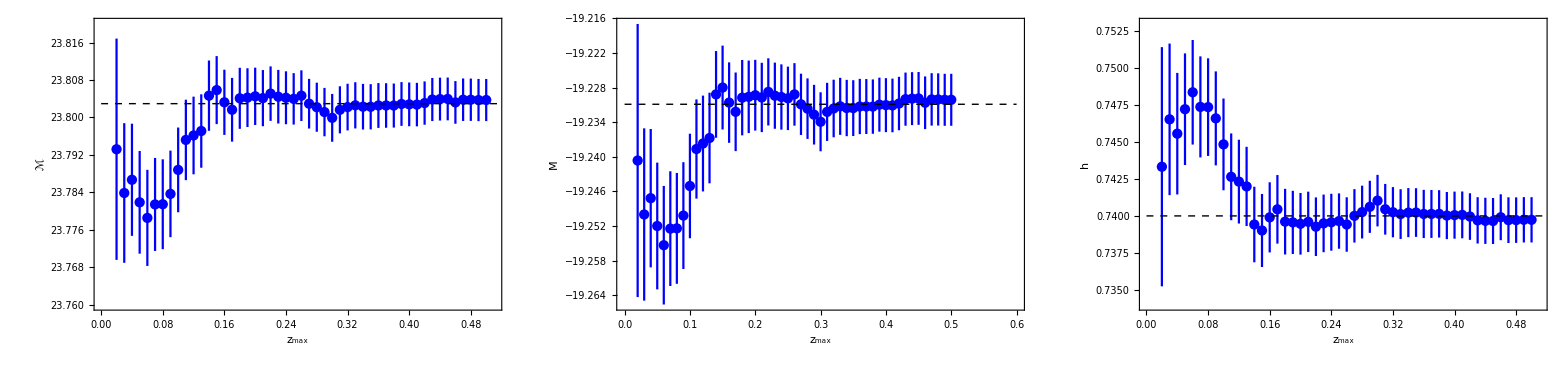

```mathematica
(* Figure 1 - Combine the plots for the three different parameters *)
cutofffig=GraphicsGrid[{{cutofffig1,cutofffig2,cutofffig3}},Spacings->0]
```

```mathematica
Export[NotebookDirectory[]<>"cutofffig.pdf",cutofffig,ImageResolution->1000];
```

### 100 Point Subsamples - Figure 2

```mathematica
(* Basic parameters for the subsample loops that follows *)
step=1; numdat=100;
```

```mathematica
(* ℳ Subsample Plot *)
paramssubsampMcal={Mcal};
tabsubsampMcal={};
(* Do loop for 100 point subsamples covering the entire redshift range of the Pantheon dataset *)
Do[
(* Rank the data from the lowest to the highest redshift and select the first 100 points. Repeat this procedure untill the entire redshift range of the Pantheon dataset is covered *)
datasubsampMcal=Take[Sort[data,#1[[2]]<#2[[2]]&],{j+1,numdat+j}];
(* Minimization of χ^2 with respect to ℳ. We fix Subscript[Ω, 0m] to the best fit value indicated by the full dataset *)
minsubsampMcal=FindMinimum[chi2Panthstat2[datasubsampMcal,Mcal,ombf2],{Mcal,23.,23.1}];
chiminsubsampMcal=minsubsampMcal[[1]];
Mcalbfsubsamp=minsubsampMcal[[2,1,2]];
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
chifunsubsampMcal=ListInterpolation[ParallelTable[chi2Panthstat2[datasubsampMcal,Mcal,ombf2],{Mcal,Mcalbfsubsamp-0.02,Mcalbfsubsamp+0.02,0.02},DistributedContexts->Automatic],{{Mcalbfsubsamp-0.02,Mcalbfsubsamp+0.02}}];
FijsubsampMcal=1/2 Table[D[chifunsubsampMcal[Mcal],paramssubsampMcal[[i]],paramssubsampMcal[[k]]]/.minsubsampMcal[[2]],{i,1,Length[paramssubsampMcal]},{k,1,Length[paramssubsampMcal]}];
cijsubsampMcal=Inverse[FijsubsampMcal];
errorssubsampMcal=Sqrt[Diagonal[cijsubsampMcal]];
(* Calculate the mean value of z for each subsample *)
tabmeansubsampMcal=Table[datasubsampMcal[[p,2]],{p,1,Length[datasubsampMcal]}];
(* Append the corresponding quantities to a list *)
AppendTo[tabsubsampMcal,{j,datasubsampMcal[[1,2]],datasubsampMcal[[numdat,2]],chiminsubsampMcal,Mean[tabmeansubsampMcal],Mcalbfsubsamp,errorssubsampMcal[[1]],Length[datasubsampMcal]}],{j,0,Length[data]-numdat,step}]
```

```mathematica
(* Create the table for ErrorListPlot *)
Mcaltabsubsamp=Table[{{tabsubsampMcal[[i,5]],tabsubsampMcal[[i,6]]},ErrorBar[{-tabsubsampMcal[[i,7]],tabsubsampMcal[[i,7]]}]},{i,1,Length[tabsubsampMcal]}];
(* ErrorListPlot of ℳ for Subsmaple subsets *)
Mcalplotsubsamp=ErrorListPlot[Mcaltabsubsamp,PlotRange->{{0,1},{23.75,23.86}},Frame->True,PlotStyle->Blue,FrameLabel->{"z_mean","ℳ"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImageSize->Large,Axes->None];subsampfigMcal=Show[{Mcalplotsubsamp,Graphics[{{Directive[Black,Dashed],Line[{{0,Mbf2},{1,Mbf2}}]}}]}];
```

```mathematica
(* M Subsample Plot *)
paramssubsamp={M};
tabsubsamp={};
(* Do loop for 100 point subsamples covering the entire redshift range of the Pantheon dataset *)
Do[
(* Rank the data from the lowest to the highest redshift and select the first 100 points. Repeat this procedure untill the entire redshift range of the Pantheon dataset is covered *)
datasubsamp=Take[Sort[data,#1[[2]]<#2[[2]]&],{j+1,numdat+j}];
(* Minimization of χ^2 with respect to M. We fix Subscript[Ω, 0m] to the best fit value indicated by the full dataset and h=0.74 *)
minsubsamp=FindMinimum[chi2Panthstat1[datasubsamp,M,ombf,h0riess],{M,-19.,-19.1}];
chiminsubsamp=minsubsamp[[1]];
Mbfsubsamp=minsubsamp[[2,1,2]];
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
chifunsubsamp=ListInterpolation[ParallelTable[chi2Panthstat1[datasubsamp,M,ombf,h0riess],{M,Mbfsubsamp-0.02,Mbfsubsamp+0.02,0.02},DistributedContexts->Automatic],{{Mbfsubsamp-0.02,Mbfsubsamp+0.02}}];
Fijsubsamp=1/2 Table[D[chifunsubsamp[M],paramssubsamp[[i]],paramssubsamp[[k]]]/.minsubsamp[[2]],{i,1,Length[paramssubsamp]},{k,1,Length[paramssubsamp]}];
cijsubsamp=Inverse[Fijsubsamp];
errorssubsamp=Sqrt[Diagonal[cijsubsamp]];
(* Calculate the mean value of z for each subsample *)
tabmeansubsamp=Table[datasubsamp[[p,2]],{p,1,Length[datasubsamp]}];
(* Append the corresponding quantities to a list *)
AppendTo[tabsubsamp,{j,datasubsamp[[1,2]],datasubsamp[[numdat,2]],chiminsubsamp,Mean[tabmeansubsamp],Mbfsubsamp,errorssubsamp[[1]],Length[datasubsamp]}],{j,0,Length[data]-numdat,step}]
```

```mathematica
(* Create the table for ErrorListPlot *)
Mtabsubsamp=Table[{{tabsubsamp[[i,5]],tabsubsamp[[i,6]]},ErrorBar[{-tabsubsamp[[i,7]],tabsubsamp[[i,7]]}]},{i,1,Length[tabsubsamp]}];
(* ErrorListPlot of M for Subsmaple subsets *)
Mplotsubsamp=ErrorListPlot[Mtabsubsamp,PlotRange->{{0,1},{-19.284,-19.176}},Frame->True,PlotStyle->Blue,FrameLabel->{"z_mean","M"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImageSize->Large,Axes->None];subsampfigM=Show[{Mplotsubsamp,Graphics[{{Directive[Black,Dashed],Line[{{0,Mbf},{1,Mbf}}]}}]}];
```

```mathematica
(* h Subsample Plot *)
paramssubsamph={h};
tabsubsamph={};
(* Do loop for 100 point subsamples covering the entire redshift range of the Pantheon dataset *)
Do[
(* Rank the data from the lowest to the highest redshift and select the first 100 points. Repeat this procedure untill the entire redshift range of the Pantheon dataset is covered *)
datasubsamph=Take[Sort[data,#1[[2]]<#2[[2]]&],{j+1,numdat+j}];
(* Minimization of χ^2 with respect to h. We fix Subscript[Ω, 0m] and M to the best fit values indicated by the full dataset *)
minsubsamph=FindMinimum[chi2Panthstat1[datasubsamph,Mbf,ombf,h],{h,0.73,0.74}];
chiminsubsamph=minsubsamph[[1]];
hbfsubsamp=minsubsamph[[2,1,2]];
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
chifunsubsamph=ListInterpolation[ParallelTable[chi2Panthstat1[datasubsamph,Mbf,ombf,h],{h,hbfsubsamp-0.02,hbfsubsamp+0.02,0.02},DistributedContexts->Automatic],{{hbfsubsamp-0.02,hbfsubsamp+0.02}}];
Fijsubsamph=1/2 Table[D[chifunsubsamph[h],paramssubsamph[[i]],paramssubsamph[[k]]]/.minsubsamph[[2]],{i,1,Length[paramssubsamph]},{k,1,Length[paramssubsamph]}];
cijsubsamph=Inverse[Fijsubsamph];
errorssubsamph=Sqrt[Diagonal[cijsubsamph]];
(* Calculate the mean value of z for each subsample *)
tabmeansubsamph=Table[datasubsamph[[p,2]],{p,1,Length[datasubsamph]}];
(* Append the corresponding quantities to a list *)
AppendTo[tabsubsamph,{j,datasubsamph[[1,2]],datasubsamph[[numdat,2]],chiminsubsamph,Mean[tabmeansubsamph],hbfsubsamp,errorssubsamph[[1]],Length[datasubsamph]}],{j,0,Length[data]-numdat,step}]
```

```mathematica
(* Create the table for ErrorListPlot *)
htabsubsamp=Table[{{tabsubsamph[[i,5]],tabsubsamph[[i,6]]},ErrorBar[{-tabsubsamph[[i,7]],tabsubsamph[[i,7]]}]},{i,1,Length[tabsubsamph]}];
(* ErrorListPlot of h for Subsmaple subsets *)
hplotsubsamp=ErrorListPlot[htabsubsamp,PlotRange->{{0,1},{0.72,0.76}},Frame->True,PlotStyle->Blue,FrameLabel->{"z_mean","h"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImageSize->Large,Axes->None];subsampfigh=Show[{hplotsubsamp,Graphics[{{Directive[Black,Dashed],Line[{{0,h0riess},{1,h0riess}}]}}]}];
```

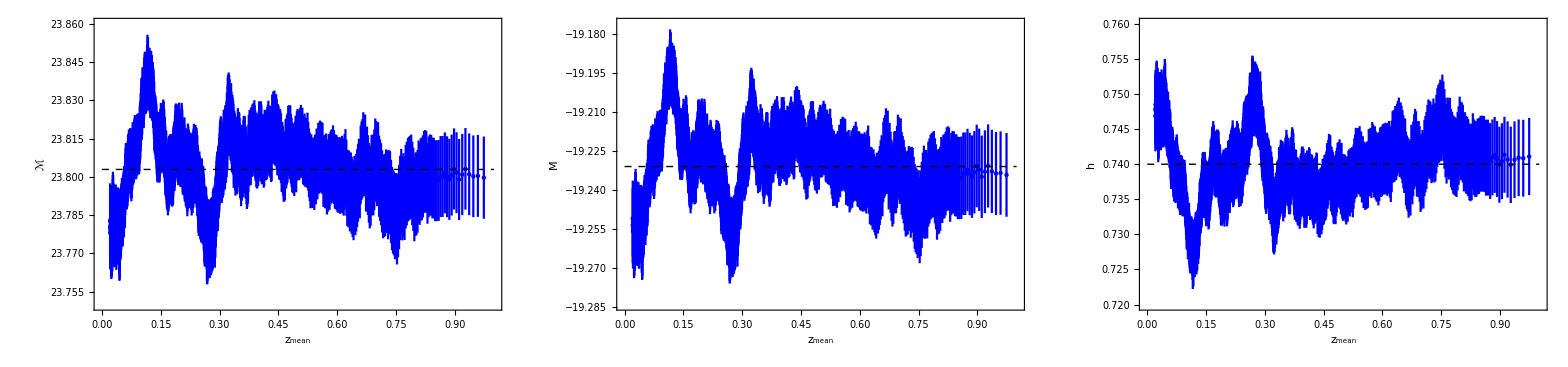

```mathematica
(* Figure 2 - Combine the plots for the three different parameters *)
subsampfig=GraphicsGrid[{{subsampfigMcal,subsampfigM,subsampfigh}},Spacings->0]
```

```mathematica
Export[NotebookDirectory[]<>"subsampfig.pdf",subsampfig,ImageResolution->1000];
```

### Redshift Tomography - Figures 3 and 4

```mathematica
(* 1st Bin *)
datatom1=Take[Sort[data,#1[[2]]<#2[[2]]&],{1,(ndatPanth/4)}];
ndat1=Length[datatom1];
(* 2nd Bin *)
datatom2=Take[Sort[data,#1[[2]]<#2[[2]]&],{(ndatPanth/4)+1,(ndatPanth/2)}];
ndat2=Length[datatom2];
(* 3rd Bin *)
datatom3=Take[Sort[data,#1[[2]]<#2[[2]]&],{(ndatPanth/2)+1,(3*ndatPanth/4)}];
ndat3=Length[datatom3];
(* 4th Bin *)
datatom4=Take[Sort[data,#1[[2]]<#2[[2]]&],{(3*ndatPanth/4)+1,ndatPanth}];
ndat4=Length[datatom4];
```

#### First Bin Analysis

##### Redshift Range

```mathematica
datatom1[[All,2]]
```

{0.01012,0.01038,0.01043,0.01082,0.01209,0.0122,0.01226,0.01268,0.01271,0.01291,0.01318,0.01382,0.01402,0.01447,0.01451,0.01454,0.01472,0.01504,0.01506,0.0152,0.0153,0.01531,0.01531,0.01532,0.01567,0.01568,0.01572,0.01629,0.01635,0.01662,0.01663,0.01678,0.01697,0.01698,0.01705,0.01724,0.01726,0.01732,0.0174,0.01741,0.01752,0.01754,0.01763,0.01908,0.0197,0.01972,0.0202,0.02024,0.02031,0.02038,0.0204,0.02091,0.0212,0.02171,0.02189,0.02197,0.0221,0.02223,0.02249,0.02275,0.02348,0.02349,0.02384,0.02398,0.02401,0.02414,0.02454,0.02477,0.02482,0.02525,0.02529,0.02547,0.02557,0.02559,0.0258,0.02627,0.02639,0.02643,0.02651,0.02673,0.02689,0.02751,0.02752,0.02752,0.02763,0.02811,0.02837,0.02845,0.02846,0.02878,0.0288,0.02894,0.02932,0.0295,0.0299,0.03001,0.03048,0.03049,0.03055,0.03144,0.03155,0.03161,0.03163,0.03184,0.03191,0.03212,0.0322,0.03273,0.0328,0.03292,0.03314,0.03348,0.03359,0.03378,0.03399,0.03408,0.03411,0.03416,0.03426,0.03434,0.03438,0.03489,0.03501,0.03507,0.03518,0.03578,0.03682,0.037,0.03713,0.0373,0.03743,0.03791,0.038,0.03827,0.03837,0.03863,0.03984,0.04028,0.04067,0.04093,0.04093,0.0415,0.04269,0.0431,0.04341,0.04437,0.04437,0.04486,0.04582,0.04597,0.04651,0.0471,0.04713,0.04714,0.04819,0.04949,0.04976,0.05035,0.05067,0.05092,0.05322,0.05344,0.05359,0.05418,0.05458,0.05495,0.05573,0.05581,0.05684,0.05715,0.05721,0.0589,0.05895,0.05948,0.06119,0.06441,0.06455,0.06481,0.06559,0.06641,0.06845,0.06877,0.06888,0.0706,0.07063,0.07141,0.0718,0.07369,0.07515,0.07523,0.0755,0.07877,0.07883,0.07976,0.08141,0.0822,0.08254,0.08282,0.08504,0.08543,0.08784,0.08806,0.08848,0.0896,0.0906,0.0919,0.09227,0.09391,0.09401,0.0963,0.0994,0.10018,0.1004,0.1022,0.1023,0.10264,0.10288,0.103,0.10337,0.10351,0.1056,0.10638,0.10683,0.1072,0.1075,0.10886,0.1098,0.11242,0.11364,0.11628,0.11635,0.11741,0.11771,0.11797,0.11845,0.1187,0.1194,0.11966,0.11991,0.12042,0.1206,0.12164,0.1219,0.1221,0.12262,0.12303,0.12336,0.12376,0.1238,0.12455,0.12516,0.12608,0.12622,0.12688,0.12694,0.12715,0.12837,0.12899,0.12903,0.12928,0.1294,0.13045}

##### χ^2 Analysis

```mathematica
(* Minimization of χ^2 with respect to ℳ and Subscript[Ω, 0m] *)
mintom1=FindMinimum[chi2Panthstat2[datatom1,Mcal,om],{Mcal,23,23.1},{om,0.28,0.29}];
Mcalbftom1=mintom1[[2,1,2]];
ombftom1=mintom1[[2,2,2]];
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
chifuntom1=ListInterpolation[ParallelTable[chi2Panthstat2[datatom1,Mcal,om],{Mcal,Mcalbftom1-0.02,Mcalbftom1+0.02,0.02},{om,ombftom1-0.02,ombftom1+0.02,0.02},DistributedContexts->Automatic],{{Mcalbftom1-0.02,Mcalbftom1+0.02},{ombftom1-0.02,ombftom1+0.02}}];
paramstom1={Mcal,om};
Fijtom1=1/2Table[D[chifuntom1[Mcal,om],paramstom1[[p]],paramstom1[[d]]]/.mintom1[[2]],{p,1,Length[paramstom1]},{d,1,Length[paramstom1]}];
cijtom1=Inverse[Fijtom1];
errorstom1=√Diagonal[cijtom1];
Print["The best fit parameters for ℳ and Ω_(0  m) are: ℳ=",Mcalbftom1,"±",errorstom1[[1]]," and Ω_(0  m)=",ombftom1,"±",errorstom1[[2]]," respectively"]
```

The best fit parameters for ℳ and Ω_(0  m) are: ℳ=23.7674±0.0144723 and Ω_(0  m)=-0.012182±0.114718 respectively

```mathematica
(* Sigma difference from the full Dataset *)
diffchitom1=chi2Panthstat2[datatom1,Mbf2,ombf2]-mintom1[[1]];
sigmadifftom1=nsig[diffchitom1,2]
```

2.06119

##### Contour Plot for the 1st Bin

```mathematica
contouromMtom1=ContourPlot[chi2Panthstat2[datatom1,Mcal,om],{om,-0.5,0.5},{Mcal,23.71,23.82},Contours->{mintom1[[1]]+dchi[1,2],mintom1[[1]]+dchi[2,2],mintom1[[1]]+dchi[3,2]},ContourShading->False,ContourStyle->Red];
```

#### Second Bin Analysis

##### Redshift Range

```mathematica
datatom2[[All,2]]
```

{0.13243,0.1326,0.13353,0.13514,0.1352,0.1361,0.13639,0.13687,0.13696,0.13729,0.13811,0.13818,0.13833,0.1384,0.13864,0.13868,0.1388,0.1396,0.1407,0.1412,0.1431,0.1436,0.14387,0.14409,0.14478,0.1453,0.14533,0.14581,0.1466,0.14703,0.14729,0.1476,0.14792,0.14882,0.1496,0.1505,0.1506,0.15186,0.1526,0.15271,0.15304,0.15317,0.15325,0.15339,0.15492,0.15509,0.15517,0.15596,0.15653,0.1568,0.15689,0.15837,0.15899,0.1592,0.15935,0.1599,0.15999,0.16035,0.1604,0.16059,0.1612,0.1618,0.16284,0.16356,0.16431,0.16455,0.16477,0.16595,0.16817,0.1692,0.1696,0.17028,0.17063,0.1712,0.1717,0.1727,0.17315,0.1735,0.17357,0.17373,0.17383,0.174,0.17428,0.17483,0.17558,0.17625,0.17653,0.17696,0.17706,0.17768,0.1777,0.17789,0.17839,0.17851,0.1789,0.17915,0.1792,0.1792,0.17958,0.1799,0.18037,0.1806,0.1806,0.18079,0.1808,0.1808,0.1812,0.18123,0.18203,0.1828,0.18322,0.18376,0.18388,0.18443,0.18468,0.18481,0.185,0.18507,0.18516,0.1852,0.18563,0.18581,0.18651,0.18891,0.18914,0.18931,0.1896,0.18979,0.19009,0.19025,0.19029,0.1912,0.19176,0.19392,0.19422,0.1958,0.1959,0.19611,0.19654,0.19671,0.19718,0.19726,0.19801,0.1985,0.19862,0.19867,0.1994,0.1996,0.1998,0.2006,0.2006,0.20215,0.20267,0.20308,0.20313,0.20318,0.20323,0.20335,0.20368,0.20453,0.2049,0.20515,0.20548,0.20557,0.20735,0.20847,0.2085,0.20852,0.2088,0.21005,0.2102,0.2102,0.21054,0.2106,0.21075,0.21082,0.21099,0.2116,0.21163,0.21179,0.21226,0.21323,0.21338,0.21353,0.2145,0.21457,0.21513,0.2166,0.21674,0.21728,0.21757,0.21835,0.21865,0.21885,0.21887,0.21935,0.21938,0.21955,0.2196,0.21975,0.22068,0.2212,0.2212,0.22256,0.22286,0.22334,0.2236,0.22452,0.2246,0.2253,0.22534,0.2255,0.22669,0.22786,0.2288,0.22916,0.2296,0.22967,0.2305,0.2307,0.2307,0.2318,0.2335,0.2338,0.23381,0.2348,0.23542,0.2363,0.23652,0.2367,0.2368,0.23684,0.23775,0.2388,0.2396,0.24,0.2406,0.2411,0.2416,0.24185,0.24206,0.2426,0.24267,0.24315,0.2434,0.24436,0.24448,0.2448,0.2454,0.2454,0.24552,0.24555,0.24558,0.2457,0.24603,0.24637,0.24639,0.24643,0.24835,0.24852,0.24857,0.2488}

##### χ^2 Analysis

```mathematica
(* Minimization of χ^2 with respect to ℳ and Subscript[Ω, 0m] *)
mintom2=FindMinimum[chi2Panthstat2[datatom2,Mcal,om],{Mcal,23,23.1},{om,0.28,0.29}];
Mcalbftom2=mintom2[[2,1,2]];
ombftom2=mintom2[[2,2,2]];
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
chifuntom2=ListInterpolation[ParallelTable[chi2Panthstat2[datatom2,Mcal,om],{Mcal,Mcalbftom2-0.02,Mcalbftom2+0.02,0.02},{om,ombftom2-0.02,ombftom2+0.02,0.02},DistributedContexts->Automatic],{{Mcalbftom2-0.02,Mcalbftom2+0.02},{ombftom2-0.02,ombftom2+0.02}}];
paramstom2={Mcal,om};
Fijtom2=1/2Table[D[chifuntom2[Mcal,om],paramstom2[[p]],paramstom2[[d]]]/.mintom2[[2]],{p,1,Length[paramstom2]},{d,1,Length[paramstom2]}];
cijtom2=Inverse[Fijtom2];
errorstom2=√Diagonal[cijtom2];
Print["The best fit parameters for ℳ and Ω_(0  m) are: ℳ=",Mcalbftom2,"±",errorstom2[[1]]," and Ω_(0  m)=",ombftom2,"±",errorstom2[[2]]," respectively"]
```

The best fit parameters for ℳ and Ω_(0  m) are: ℳ=23.8789±0.0517107 and Ω_(0  m)=0.526194±0.185935 respectively

```mathematica
(* Sigma difference from the full Dataset *)
diffchitom2=chi2Panthstat2[datatom2,Mbf2,ombf2]-mintom2[[1]];
sigmadifftom2=nsig[diffchitom2,2]
```

1.14967

##### Contour Plot

```mathematica
contouromMtom2=ContourPlot[chi2Panthstat2[datatom2,Mcal,om],{om,-0.02,1.42},{Mcal,23.7,24.08},Contours->{mintom2[[1]]+dchi[1,2],mintom2[[1]]+dchi[2,2],mintom2[[1]]+dchi[3,2]},ContourShading->False,ContourStyle->Red];
```

#### Third Bin Analysis

##### Redshift Range

```mathematica
datatom3[[All,2]]
```

{0.2488,0.24883,0.2492,0.24961,0.24973,0.24973,0.25,0.2501,0.25029,0.25037,0.2504,0.2504,0.25104,0.25174,0.25191,0.25249,0.2528,0.2534,0.25609,0.25625,0.25655,0.25672,0.25721,0.25722,0.2576,0.258,0.2588,0.2604,0.2607,0.2607,0.26129,0.26162,0.26166,0.2622,0.2631,0.26338,0.26349,0.26357,0.2637,0.26405,0.2641,0.26451,0.2647,0.26576,0.26687,0.268,0.26821,0.26838,0.26856,0.2688,0.26891,0.27,0.2701,0.2707,0.2708,0.27091,0.2712,0.2734,0.2748,0.2749,0.2752,0.27544,0.27573,0.27656,0.27749,0.27822,0.27923,0.2797,0.2798,0.2804,0.2824,0.28332,0.28391,0.2842,0.28434,0.28436,0.2854,0.28543,0.2856,0.2858,0.28655,0.28662,0.28742,0.28746,0.2888,0.2889,0.2896,0.2902,0.29021,0.2907,0.29114,0.29135,0.2916,0.2921,0.2927,0.2928,0.2928,0.29353,0.2956,0.29567,0.29683,0.2988,0.2988,0.29888,0.29936,0.2996,0.3001,0.30021,0.30041,0.3006,0.3012,0.3018,0.30191,0.3026,0.3032,0.30354,0.30394,0.3051,0.3055,0.3056,0.30569,0.30632,0.3065,0.3068,0.308,0.30915,0.3092,0.30929,0.30938,0.3106,0.31065,0.3112,0.31288,0.31376,0.31468,0.3148,0.31494,0.3156,0.31582,0.318,0.3185,0.3188,0.3192,0.3192,0.32045,0.3207,0.3212,0.3218,0.32416,0.3253,0.3254,0.32569,0.3264,0.32793,0.3283,0.3288,0.3288,0.32931,0.3297,0.32984,0.3302,0.33051,0.3306,0.3306,0.33103,0.3312,0.3312,0.3312,0.33136,0.3316,0.3327,0.33439,0.3347,0.3374,0.3374,0.3376,0.3379,0.3386,0.3388,0.34039,0.3412,0.3412,0.3456,0.34621,0.347,0.3473,0.349,0.349,0.3491,0.34916,0.34916,0.3492,0.3503,0.3509,0.35116,0.3512,0.35346,0.3536,0.35486,0.35568,0.35816,0.35819,0.359,0.36,0.36,0.3606,0.3618,0.36193,0.3652,0.3666,0.3669,0.3676,0.3682,0.36952,0.36976,0.3701,0.37016,0.37039,0.3704,0.37046,0.37091,0.3712,0.3712,0.37129,0.37191,0.37391,0.37425,0.3782,0.37986,0.3802,0.3804,0.38048,0.3806,0.3812,0.3815,0.3826,0.38492,0.3857,0.3876,0.3878,0.3892,0.3922,0.40091,0.40127,0.40128,0.4019,0.40439,0.4045,0.40591,0.4096,0.4098,0.40991,0.4114,0.4118,0.41616,0.41816,0.4194,0.4198,0.4198,0.4206,0.4208,0.42291}

##### χ^2 Analysis

```mathematica
(* Minimization of χ^2 with respect to ℳ and Subscript[Ω, 0m] *)
mintom3=FindMinimum[chi2Panthstat2[datatom3,Mcal,om],{Mcal,23,23.1},{om,0.28,0.29}];
Mcalbftom3=mintom3[[2,1,2]];
ombftom3=mintom3[[2,2,2]];
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
chifuntom3=ListInterpolation[ParallelTable[chi2Panthstat2[datatom3,Mcal,om],{Mcal,Mcalbftom3-0.02,Mcalbftom3+0.02,0.02},{om,ombftom3-0.02,ombftom3+0.02,0.02},DistributedContexts->Automatic],{{Mcalbftom3-0.02,Mcalbftom3+0.02},{ombftom3-0.02,ombftom3+0.02}}];
paramstom3={Mcal,om};
Fijtom3=1/2Table[D[chifuntom3[Mcal,om],paramstom3[[p]],paramstom3[[d]]]/.mintom3[[2]],{p,1,Length[paramstom3]},{d,1,Length[paramstom3]}];
cijtom3=Inverse[Fijtom3];
errorstom3=√Diagonal[cijtom3];
Print["The best fit parameters for ℳ and Ω_(0  m) are: ℳ=",Mcalbftom3,"±",errorstom3[[1]]," and Ω_(0  m)=",ombftom3,"±",errorstom3[[2]]," respectively"]
```

The best fit parameters for ℳ and Ω_(0  m) are: ℳ=23.7482±0.0560581 and Ω_(0  m)=0.18417±0.101426 respectively

```mathematica
(* Sigma difference from the full Dataset *)
diffchitom3=chi2Panthstat2[datatom3,Mbf2,ombf2]-mintom3[[1]];
sigmadifftom3=nsig[diffchitom3,2]
```

0.465102

##### Contour Plot

```mathematica
contouromMtom3=ContourPlot[chi2Panthstat2[datatom3,Mcal,om],{om,-0.13,0.67},{Mcal,23.55,23.99},Contours->{mintom3[[1]]+dchi[1,2],mintom3[[1]]+dchi[2,2],mintom3[[1]]+dchi[3,2]},ContourShading->False,ContourStyle->Red];
```

#### Fourth Bin Analysis

##### Redshift Range

```mathematica
datatom4[[All,2]]
```

{0.4231,0.4235,0.4267,0.4269,0.4276,0.42816,0.4292,0.4294,0.4305,0.43521,0.43591,0.4365,0.4391,0.4392,0.4399,0.4404,0.44238,0.44316,0.4474,0.44939,0.4504,0.4507,0.45117,0.4512,0.45138,0.4604,0.4607,0.46109,0.46138,0.4661,0.46691,0.46891,0.47039,0.4704,0.47091,0.4712,0.47516,0.4774,0.4796,0.48016,0.48038,0.4804,0.4812,0.4892,0.4952,0.49791,0.50016,0.5006,0.5025,0.5027,0.50349,0.5078,0.50791,0.5088,0.51,0.5106,0.51116,0.51416,0.5142,0.51491,0.51539,0.5192,0.5194,0.5196,0.52216,0.5283,0.53216,0.53316,0.53491,0.53516,0.53591,0.545,0.54891,0.5501,0.55091,0.55239,0.55316,0.55819,0.5592,0.5592,0.5632,0.5652,0.57516,0.5761,0.57639,0.5779,0.57891,0.57921,0.57938,0.58038,0.58119,0.5834,0.58392,0.58421,0.58421,0.58621,0.58791,0.5892,0.59091,0.59116,0.60038,0.60392,0.60891,0.60916,0.6104,0.61191,0.6162,0.6192,0.62039,0.62116,0.62591,0.62791,0.6304,0.63116,0.6312,0.63291,0.63821,0.63892,0.64116,0.64339,0.64339,0.64739,0.64839,0.66259,0.66438,0.67039,0.6782,0.68116,0.68339,0.68591,0.68921,0.69038,0.69391,0.69791,0.69892,0.69916,0.69992,0.69992,0.70116,0.70116,0.7012,0.70191,0.71538,0.71839,0.7202,0.72039,0.72091,0.72639,0.72739,0.73091,0.73316,0.73416,0.7342,0.735,0.73516,0.7362,0.7364,0.74,0.74116,0.7424,0.74526,0.74538,0.74991,0.75039,0.75639,0.75816,0.76039,0.76191,0.7622,0.7662,0.76639,0.7672,0.76791,0.7692,0.77391,0.77721,0.78891,0.78991,0.7972,0.7992,0.80039,0.80538,0.80538,0.80691,0.80892,0.80991,0.8104,0.81338,0.8174,0.82116,0.82238,0.8292,0.83716,0.83791,0.84091,0.84116,0.8412,0.8489,0.8492,0.85039,0.85391,0.854,0.8592,0.8592,0.8592,0.86491,0.8652,0.8672,0.87116,0.87891,0.89038,0.89216,0.89791,0.90139,0.91039,0.9142,0.92116,0.92116,0.92516,0.92591,0.92891,0.93116,0.93291,0.93491,0.935,0.93639,0.94791,0.94921,0.95039,0.95991,0.96038,0.96038,0.97,0.9752,0.98216,0.98339,0.9842,0.9972,0.99891,1.0024,1.014,1.02,1.02991,1.06039,1.092,1.12,1.206,1.23,1.23,1.3,1.305,1.315,1.33,1.34,1.37,1.39,1.54,1.55,1.7,1.8,1.914,2.26}

##### χ^2 Analysis

```mathematica
(* Minimization of χ^2 with respect to ℳ and Subscript[Ω, 0m] *)
mintom4=FindMinimum[chi2Panthstat2[datatom4,Mcal,om],{Mcal,23,23.1},{om,0.28,0.29}];
Mcalbftom4=mintom4[[2,1,2]];
ombftom4=mintom4[[2,2,2]];
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
chifuntom4=ListInterpolation[ParallelTable[chi2Panthstat2[datatom4,Mcal,om],{Mcal,Mcalbftom4-0.03,Mcalbftom4+0.03,0.03},{om,ombftom4-0.03,ombftom4+0.03,0.03},DistributedContexts->Automatic],{{Mcalbftom4-0.03,Mcalbftom4+0.03},{ombftom4-0.03,ombftom4+0.03}}];
paramstom4={Mcal,om};
Fijtom4=1/2Table[D[chifuntom4[Mcal,om],paramstom4[[p]],paramstom4[[d]]]/.mintom4[[2]],{p,1,Length[paramstom4]},{d,1,Length[paramstom4]}];
cijtom4=Inverse[Fijtom4];
errorstom4=√Diagonal[cijtom4];
Print["The best fit parameters for ℳ and Ω_(0  m) are: ℳ=",Mcalbftom4,"±",errorstom4[[1]]," and Ω_(0  m)=",ombftom4,"±",errorstom4[[2]]," respectively"]
```

The best fit parameters for ℳ and Ω_(0  m) are: ℳ=23.849±0.0413748 and Ω_(0  m)=0.333779±0.0443008 respectively

```mathematica
(* Sigma difference from the full Dataset *)
diffchitom4=chi2Panthstat2[datatom4,Mbf2,ombf2]-mintom4[[1]];
sigmadifftom4=nsig[diffchitom4,2]
```

0.679699

##### Contour Plot

```mathematica
contouromMtom4=ContourPlot[chi2Panthstat2[datatom4,Mcal,om],{om,0.19,0.53},{Mcal,23.7,24.01},Contours->{mintom4[[1]]+dchi[1,2],mintom4[[1]]+dchi[2,2],mintom4[[1]]+dchi[3,2]},ContourShading->False,ContourStyle->Red];
```

#### Cross Plot - Figure 3

```mathematica
(* Best Fits of ℳ for the four bins *)
listMcal={{{Mean[datatom1[[All,2]]],Mcalbftom1},ErrorBar[{datatom1[[1,2]]-Mean[datatom1[[All,2]]],datatom1[[262,2]]-Mean[datatom1[[All,2]]]},errorstom1[[1]]]},{{Mean[datatom2[[All,2]]],Mcalbftom2},ErrorBar[{datatom2[[1,2]]-Mean[datatom2[[All,2]]],datatom2[[262,2]]-Mean[datatom2[[All,2]]]},errorstom2[[1]]]},{{Mean[datatom3[[All,2]]],Mcalbftom3},ErrorBar[{datatom3[[1,2]]-Mean[datatom3[[All,2]]],datatom3[[262,2]]-Mean[datatom3[[All,2]]]},errorstom3[[1]]]},{{Mean[datatom4[[All,2]]],Mcalbftom4},ErrorBar[{datatom4[[1,2]]-Mean[datatom4[[All,2]]],datatom4[[262,2]]-Mean[datatom4[[All,2]]]},errorstom4[[1]]]}};
(* ℳ Plot *)
Mcalplotcross=ErrorListPlot[listMcal,BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],Frame->True,PlotRange->{{-0.02,2.35},{23.65,23.97}},PlotStyle->Blue,ImageSize->700,FrameLabel->{"z","ℳ"},FrameStyle->Directive[Black,Thick],Epilog->{Text["1st Bin",{0.11,23.74}],Text["2nd Bin",{0.2,23.94}],Text["3rd Bin",{0.32,23.68}],Text["4th Bin",{0.75,23.9}],,{Dashing[0.02],Line[{{0,Mbf2},{8,Mbf2}}]},{Dashing[0.008],Line[{{0,Mbf2+errors2[[1]]},{8,Mbf2+errors2[[1]]}}]},{Dashing[0.008],Line[{{0,Mbf2-errors2[[1]]},{8,Mbf2-errors2[[1]]}}]}}];
```

```mathematica
(* Best Fit of Subscript[Ω, 0m] for the four bins *)
listom={{{Mean[datatom1[[All,2]]],ombftom1},ErrorBar[{datatom1[[1,2]]-Mean[datatom1[[All,2]]],datatom1[[262,2]]-Mean[datatom1[[All,2]]]},errorstom1[[2]]]},{{Mean[datatom2[[All,2]]],ombftom2},ErrorBar[{datatom2[[1,2]]-Mean[datatom2[[All,2]]],datatom2[[262,2]]-Mean[datatom2[[All,2]]]},errorstom2[[2]]]},{{Mean[datatom3[[All,2]]],ombftom3},ErrorBar[{datatom3[[1,2]]-Mean[datatom3[[All,2]]],datatom3[[262,2]]-Mean[datatom3[[All,2]]]},errorstom3[[2]]]},{{Mean[datatom4[[All,2]]],ombftom4},ErrorBar[{datatom4[[1,2]]-Mean[datatom4[[All,2]]],datatom4[[262,2]]-Mean[datatom4[[All,2]]]},errorstom4[[2]]]}};
(* Subscript[Ω, 0m] Plot *)
omplotcross=ErrorListPlot[listom,BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],Frame->True,PlotRange->{{-0.02,2.35},{-0.25,0.79}},PlotStyle->Blue,ImageSize->700,FrameLabel->{"z","Ω_(0  m)"},FrameStyle->Directive[Black,Thick],Axes->False,Epilog->{Text["1st Bin",{0.12,-0.16}],Text["2nd Bin",{0.2,0.73}],Text["3rd Bin",{0.325,0.052}],Text["4th Bin",{0.75,0.41}],,{Dashing[0.02],Line[{{0,ombf2},{8,ombf2}}]},{Dashing[0.008],Line[{{0,ombf2+errors2[[2]]},{8,ombf2+errors2[[2]]}}]},{Dashing[0.008],Line[{{0,ombf2-errors2[[2]]},{8,ombf2-errors[[2]]}}]}}];
```

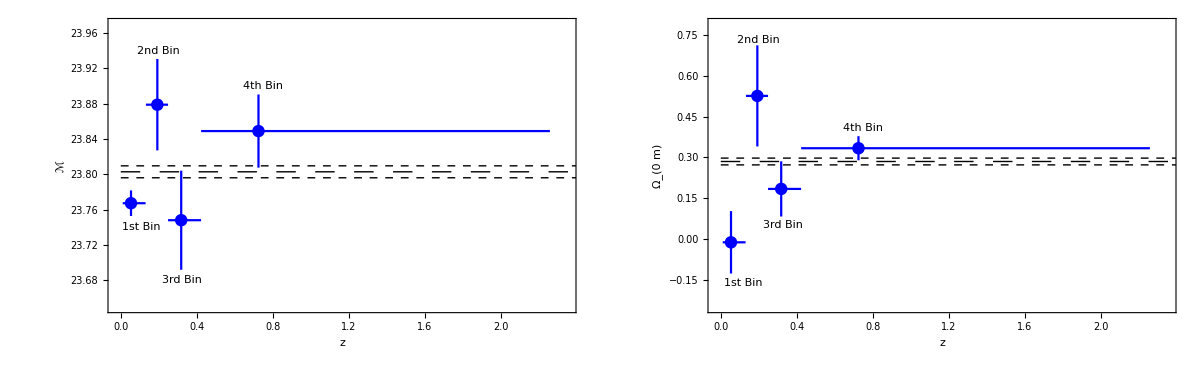

```mathematica
(* Figure 3 - Combine the two plots *)
crossplot=GraphicsGrid[{{Mcalplotcross,omplotcross}},Spacings->0,ImageSize->1200]
```

```mathematica
Export[NotebookDirectory[]<>"crossplot.pdf",crossplot,ImageResolution->1000];
```

#### Overlapping Contours - Figure 4

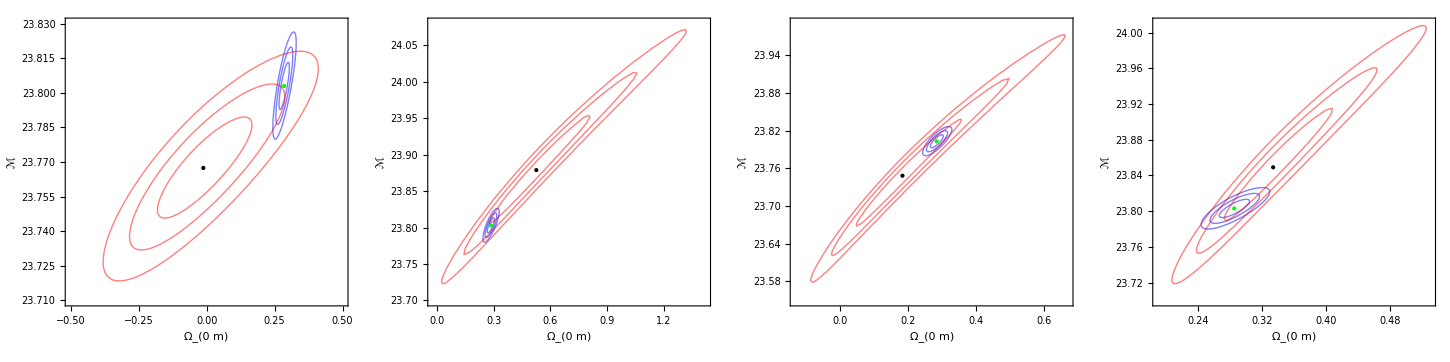

```mathematica
(* Overlapping the contours *)
overlaptom1=Show[{contouromMfull,contouromMtom1},Epilog->{{PointSize[Medium],Green,Point[{ombf2,Mbf2}]},{PointSize[Medium],Black,Point[{ombftom1,Mcalbftom1}]}},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],FrameLabel->{"Ω_(0  m)","ℳ"},PlotRange->{{-0.5,0.5},{23.71,23.83}}];
overlaptom2=Show[{contouromMfull,contouromMtom2},Epilog->{{PointSize[Medium],Green,Point[{ombf2,Mbf2}]},{PointSize[Medium],Black,Point[{ombftom2,Mcalbftom2}]}},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],FrameLabel->{"Ω_(0  m)","ℳ"},PlotRange->{{-0.02,1.42},{23.7,24.08}}];
overlaptom3=Show[{contouromMfull,contouromMtom3},Epilog->{{PointSize[Medium],Green,Point[{ombf2,Mbf2}]},{PointSize[Medium],Black,Point[{ombftom3,Mcalbftom3}]}},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],FrameLabel->{"Ω_(0  m)","ℳ"},PlotRange->{{-0.13,0.67},{23.55,23.99}}];
overlaptom4=Show[{contouromMfull,contouromMtom4},Epilog->{{PointSize[Medium],Green,Point[{ombf2,Mbf2}]},{PointSize[Medium],Black,Point[{ombftom4,Mcalbftom4}]}},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],FrameLabel->{"Ω_(0  m)","ℳ"},PlotRange->{{0.19,0.53},{23.7,24.01}}];
contourtomfig=GraphicsGrid[{{overlaptom1,overlaptom2,overlaptom3,overlaptom4}},Spacings->0,ImageSize->1450]
```

```mathematica
Export[NotebookDirectory[]<>"contourtomfig.pdf",contourtomfig,ImageResolution->1000];
```

### Monte Carlo simulations of Pantheon-like datasets Analysis for the 1st Bin - Figure 5

##### Create Mock Data

```mathematica
(* Create a list with a random apparent magnitude Subscript[m, obs] *)
randdat1[j_]:={datatom1[[j,1]],datatom1[[j,2]],datatom1[[j,3]],RandomReal[NormalDistribution[5 Log10[(1+datatom1[[j,3]])/(1+datatom1[[j,2]])DL[datatom1[[j,2]],ombf2]]+Mbf2,datatom1[[j,5]]]],datatom1[[j,5]]} ;
(* Create a table for convenience *)
randdatab1=Table[randdat1[j],{j,1,ndat1}];
```

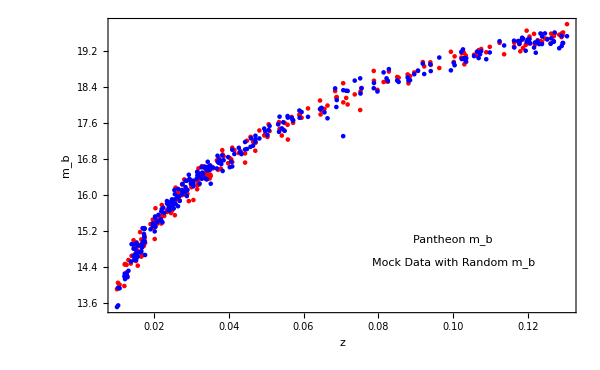

```mathematica
(* Compare the mock with the real data *)
mbmocktom1=Table[{randdatab1[[i,2]],randdatab1[[i,4]]},{i,1,ndat1}];
datatom1mb=Table[{datatom1[[i,2]],datatom1[[i,4]]},{i,1,ndat1}];
ListPlot[{datatom1mb,mbmocktom1},PlotStyle->{Red,Blue},PlotRange->All,Frame->True,FrameLabel->{"z","m_b"},ImageSize -> 600, BaseStyle -> {FontFamily -> "Times",
  20}, FrameStyle -> Directive[Black, Thick],Epilog->{Style[Text["Pantheon m_b",{0.1,15}],Red],Style[Text["Mock Data with Random m_b",{0.1,14.5}],Blue]}]
```

##### Do loop for the frequencies of ℳ and Ω_(0m)

```mathematica
(* ErrorBars Plot - This cell produces 100 different values for ℳ and Subscript[Ω, 0m] through the minimization process. This cell takes some time to be completed. Therefore you can use the following tables to run the program without going through the (time-consuming) data acquisition process *)
jmax=500;Mcalbflistom1={};Mcalerrlistom1={};ombflistom1={};omerrlistom1={};
(* Do loop to calculate the frequencies of ℳ and Subscript[Ω, 0m] *)
Do[randdat1[j_]:={datatom1[[j,1]],datatom1[[j,2]],datatom1[[j,3]],RandomReal[NormalDistribution[5 Log10[(1+datatom1[[j,3]])/(1+datatom1[[j,2]])DL[datatom1[[j,2]],ombf2]]+Mbf2,datatom1[[j,5]]]],datatom1[[j,5]]} ;
(* Create a table for convenience *)
randdatab1=Table[randdat1[j],{j,1,ndat1}];
(* Minimization of χ^2 with respect to ℳ and Subscript[Ω, 0m] *)
mintom1rand=FindMinimum[chi2Panthstat2[randdatab1,Mcal,om],{Mcal,23,23.1},{om,0.28,0.29}];
Mcalbftom1rand=mintom1rand[[2,1,2]];
ombftom1rand=mintom1rand[[2,2,2]];
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
chifuntom1rand=ListInterpolation[ParallelTable[chi2Panthstat2[randdatab1,Mcal,om],{Mcal,Mcalbftom1rand-0.02,Mcalbftom1rand+0.02,0.02},{om,ombftom1rand-0.02,ombftom1rand+0.02,0.02},DistributedContexts->Automatic],{{Mcalbftom1rand-0.02,Mcalbftom1rand+0.02},{ombftom1rand-0.02,ombftom1rand+0.02}}];
paramstom1rand={Mcal,om};
Fijtom1rand=1/2Table[D[chifuntom1rand[Mcal,om],paramstom1rand[[p]],paramstom1rand[[d]]]/.mintom1rand[[2]],{p,1,Length[paramstom1rand]},{d,1,Length[paramstom1rand]}]; 
cijtom1rand=Inverse[Fijtom1rand];
errorstom1rand=√Diagonal[cijtom1rand];
(* Append the corresponding quantities in different lists *)
AppendTo[Mcalbflistom1,Mcalbftom1rand];
AppendTo[Mcalerrlistom1,errorstom1rand[[1]]];
AppendTo[ombflistom1,ombftom1rand]; 
AppendTo[omerrlistom1,errorstom1rand[[2]]]; 
If[Mod[j,100]==0,Print["Finished step ",j," of ",jmax, " realizations // The best fit parameters for ℳ and Ω_(0  m) (two params varied) are: ℳ=",Mcalbftom1rand,"±",errorstom1rand[[1]]," and Ω_(0  m)=",ombftom1rand,"±",errorstom1rand[[2]]," respectively"]],{j,1,jmax}]
```

Finished step 100 of 500 realizations // The best fit parameters for ℳ and Ω_(0  m) (two params varied) are: ℳ=23.7953±0.0146981 and Ω_(0  m)=0.199355±0.122373 respectively

Finished step 200 of 500 realizations // The best fit parameters for ℳ and Ω_(0  m) (two params varied) are: ℳ=23.7917±0.0148066 and Ω_(0  m)=0.185939±0.123309 respectively

Finished step 300 of 500 realizations // The best fit parameters for ℳ and Ω_(0  m) (two params varied) are: ℳ=23.8167±0.0150331 and Ω_(0  m)=0.418845±0.131663 respectively

Finished step 400 of 500 realizations // The best fit parameters for ℳ and Ω_(0  m) (two params varied) are: ℳ=23.7874±0.0146549 and Ω_(0  m)=0.120404±0.119978 respectively

Finished step 500 of 500 realizations // The best fit parameters for ℳ and Ω_(0  m) (two params varied) are: ℳ=23.8095±0.0149901 and Ω_(0  m)=0.375013±0.130091 respectively

```mathematica
(* Print the results of the do loop *)
ombflistom1//Sort
Mcalbflistom1//Sort
```

{-0.0253695,-0.00251933,-0.00185857,0.00119496,0.020011,0.0202206,0.0264001,0.031351,0.036748,0.0375531,0.0433366,0.0456524,0.0467244,0.0522272,0.0549598,0.0575739,0.0597457,0.0612103,0.0639888,0.0644601,0.0677835,0.0693766,0.0696119,0.0706149,0.0741886,0.0849017,0.0861437,0.0868214,0.0926152,0.0940861,0.0975866,0.102075,0.102257,0.104524,0.10563,0.107399,0.10885,0.112259,0.115343,0.116465,0.11765,0.118981,0.119204,0.119636,0.120116,0.120238,0.120404,0.120605,0.12077,0.124591,0.12651,0.128021,0.128133,0.129323,0.132467,0.133254,0.134455,0.135848,0.137005,0.142795,0.143932,0.144048,0.144182,0.144184,0.144233,0.144807,0.145708,0.146237,0.146869,0.146988,0.147721,0.148357,0.148634,0.149824,0.151606,0.152082,0.152915,0.153232,0.153606,0.155045,0.155977,0.156357,0.157506,0.15888,0.159116,0.159574,0.161498,0.16244,0.163823,0.164272,0.165612,0.167023,0.167399,0.170956,0.172007,0.172287,0.172363,0.172816,0.173178,0.173746,0.177054,0.17727,0.178497,0.178541,0.178871,0.179033,0.179367,0.180174,0.181126,0.182611,0.1827,0.183597,0.183844,0.185148,0.185231,0.185505,0.185939,0.185951,0.186406,0.18755,0.188161,0.189367,0.191511,0.191991,0.194057,0.19464,0.194868,0.195475,0.19596,0.196247,0.196752,0.196759,0.199355,0.201998,0.202652,0.203344,0.203399,0.204224,0.20427,0.204868,0.204955,0.20534,0.207899,0.208479,0.208679,0.208832,0.210381,0.211744,0.213278,0.214118,0.214546,0.216483,0.216683,0.216854,0.218015,0.218406,0.21843,0.218644,0.218705,0.218709,0.21903,0.219369,0.220033,0.22058,0.220856,0.221533,0.221893,0.224097,0.224421,0.224708,0.225121,0.22519,0.225223,0.22751,0.227985,0.228611,0.231951,0.232549,0.232609,0.232643,0.233533,0.235335,0.235429,0.235732,0.236335,0.23762,0.237851,0.23867,0.239211,0.240233,0.240285,0.241092,0.241385,0.242066,0.242534,0.242642,0.24353,0.243999,0.244439,0.245281,0.247536,0.24806,0.248067,0.24894,0.248953,0.249504,0.249608,0.250347,0.251941,0.252261,0.254641,0.255913,0.258552,0.259268,0.259318,0.259926,0.260036,0.260607,0.263536,0.263701,0.264821,0.264879,0.265084,0.265132,0.265488,0.266143,0.267108,0.26733,0.267397,0.267931,0.26794,0.269229,0.269595,0.270025,0.270646,0.271926,0.273097,0.273133,0.275307,0.275915,0.277165,0.277487,0.277489,0.277491,0.277726,0.278075,0.278354,0.278397,0.279194,0.27972,0.280796,0.282552,0.282558,0.282559,0.282562,0.28259,0.284116,0.284124,0.284515,0.286248,0.288191,0.288483,0.288548,0.288665,0.28919,0.289463,0.289663,0.290492,0.290737,0.291113,0.292579,0.292683,0.292743,0.292981,0.293036,0.293265,0.294872,0.295236,0.29573,0.296777,0.297112,0.297232,0.297374,0.298938,0.299254,0.299386,0.300471,0.300714,0.301011,0.301025,0.301336,0.302903,0.303811,0.304023,0.304699,0.305513,0.30613,0.306375,0.307624,0.308697,0.309443,0.309631,0.310055,0.310861,0.311113,0.311253,0.313705,0.313792,0.314548,0.314576,0.314775,0.31508,0.315397,0.316041,0.317013,0.317082,0.317702,0.318418,0.320661,0.322101,0.323307,0.324123,0.324415,0.325098,0.326504,0.32724,0.327412,0.327736,0.329002,0.330838,0.331025,0.331154,0.33217,0.332968,0.33299,0.333427,0.333701,0.334613,0.334785,0.335689,0.3368,0.336941,0.33712,0.338248,0.338714,0.339851,0.339994,0.340789,0.3432,0.345237,0.34581,0.346433,0.346727,0.347594,0.347922,0.348291,0.348572,0.349179,0.349915,0.349979,0.350624,0.351789,0.352339,0.352918,0.354284,0.355516,0.355801,0.356144,0.356485,0.357403,0.357512,0.357609,0.359241,0.359978,0.360227,0.360607,0.360936,0.361623,0.362756,0.36463,0.366861,0.367768,0.368098,0.368169,0.369598,0.369998,0.370323,0.37314,0.374217,0.375013,0.375435,0.375594,0.375995,0.378468,0.380579,0.383049,0.383519,0.383696,0.383755,0.384601,0.388512,0.388587,0.389244,0.391214,0.391947,0.39395,0.393994,0.39478,0.395294,0.395455,0.39669,0.396742,0.397876,0.398326,0.398954,0.399622,0.400275,0.402634,0.406422,0.407394,0.407888,0.407932,0.408891,0.409536,0.411188,0.413894,0.413901,0.414144,0.414273,0.416384,0.417039,0.417145,0.417882,0.418845,0.419853,0.420271,0.420828,0.424442,0.425374,0.426686,0.427535,0.428728,0.432153,0.433273,0.433432,0.438351,0.44007,0.442015,0.445917,0.446758,0.447887,0.44882,0.449563,0.454669,0.454891,0.45586,0.458177,0.45964,0.463068,0.46406,0.464473,0.465106,0.467916,0.47183,0.472098,0.472937,0.478351,0.479129,0.480172,0.480818,0.482315,0.483128,0.48774,0.487951,0.488304,0.488396,0.488483,0.492576,0.493577,0.494585,0.49472,0.501712,0.509868,0.51413,0.519465,0.520188,0.523285,0.526745,0.527882,0.537514,0.540403,0.541038,0.548232,0.557467,0.558362,0.561463,0.570048,0.577394,0.601318,0.607676}

{23.7631,23.7681,23.7686,23.7694,23.7698,23.7704,23.7732,23.7735,23.7736,23.7738,23.774,23.7741,23.7745,23.775,23.7758,23.7758,23.7759,23.7763,23.7772,23.7773,23.7776,23.778,23.7782,23.7785,23.7786,23.7786,23.7791,23.7793,23.7797,23.7798,23.7802,23.7803,23.7803,23.7807,23.7809,23.7811,23.7812,23.7814,23.7815,23.7815,23.7825,23.7826,23.7827,23.7827,23.7827,23.783,23.7831,23.7837,23.7838,23.7841,23.7841,23.7843,23.7845,23.7847,23.7848,23.785,23.7852,23.7852,23.7852,23.7853,23.7853,23.7854,23.7857,23.7857,23.786,23.7861,23.7861,23.7862,23.7864,23.7864,23.7865,23.7865,23.7866,23.7866,23.787,23.7874,23.7876,23.7877,23.7878,23.7879,23.788,23.788,23.7881,23.7882,23.7882,23.7882,23.7883,23.7885,23.7887,23.7888,23.7891,23.7891,23.7892,23.7892,23.7892,23.7894,23.7897,23.7898,23.7899,23.79,23.79,23.79,23.7904,23.7904,23.7904,23.7904,23.7905,23.7906,23.7906,23.7907,23.7909,23.7909,23.7913,23.7914,23.7915,23.7915,23.7916,23.7916,23.7917,23.7917,23.7917,23.7917,23.792,23.792,23.7921,23.7925,23.793,23.793,23.7931,23.7931,23.7931,23.7932,23.7934,23.7934,23.7935,23.7935,23.7935,23.7938,23.7938,23.7939,23.7939,23.7941,23.7942,23.7942,23.7943,23.7943,23.7944,23.7944,23.7945,23.7947,23.7947,23.795,23.795,23.7951,23.7952,23.7952,23.7952,23.7953,23.7955,23.7955,23.7956,23.7957,23.7957,23.7958,23.7958,23.7962,23.7962,23.7964,23.7966,23.7967,23.7968,23.7969,23.797,23.7972,23.7972,23.7972,23.7973,23.7973,23.7974,23.7974,23.7976,23.7976,23.7979,23.7979,23.7979,23.798,23.798,23.7983,23.7985,23.7985,23.7985,23.7985,23.7986,23.7986,23.7987,23.7988,23.7989,23.7989,23.799,23.7991,23.7991,23.7992,23.7993,23.7993,23.7993,23.7994,23.7995,23.7995,23.7996,23.7997,23.7998,23.7998,23.7998,23.7999,23.8,23.8003,23.8004,23.8004,23.8004,23.8004,23.8005,23.8005,23.8005,23.8006,23.8006,23.8008,23.8009,23.8009,23.801,23.8012,23.8012,23.8014,23.8014,23.8015,23.8017,23.8017,23.8018,23.8018,23.8018,23.802,23.802,23.8022,23.8022,23.8022,23.8023,23.8026,23.8026,23.8026,23.8027,23.8027,23.8028,23.8028,23.8029,23.8032,23.8032,23.8032,23.8032,23.8033,23.8034,23.8034,23.8034,23.8035,23.8036,23.8037,23.8037,23.8037,23.8037,23.8037,23.8038,23.8039,23.8039,23.8039,23.804,23.804,23.8042,23.8042,23.8042,23.8043,23.8044,23.8044,23.8045,23.8045,23.8047,23.8048,23.8048,23.805,23.805,23.8052,23.8053,23.8055,23.8055,23.8055,23.8055,23.8057,23.8059,23.806,23.8061,23.8061,23.8063,23.8063,23.8065,23.8065,23.8065,23.8065,23.8065,23.8066,23.8066,23.8067,23.8067,23.8067,23.8068,23.8069,23.807,23.8071,23.8072,23.8072,23.8073,23.8073,23.8073,23.8075,23.8076,23.8076,23.8077,23.8078,23.8079,23.8079,23.808,23.8082,23.8084,23.8084,23.8085,23.8085,23.8086,23.8086,23.8087,23.8088,23.8089,23.809,23.8093,23.8093,23.8093,23.8094,23.8094,23.8095,23.8095,23.8099,23.81,23.8101,23.8101,23.8102,23.8102,23.8102,23.8104,23.8104,23.8105,23.8105,23.8105,23.8106,23.8107,23.8109,23.8109,23.8109,23.811,23.8111,23.8111,23.8112,23.8113,23.8114,23.8115,23.8116,23.8116,23.8116,23.8117,23.8118,23.8119,23.8119,23.812,23.8121,23.8121,23.8121,23.8122,23.8124,23.8125,23.8125,23.8126,23.8126,23.8126,23.8126,23.8127,23.8127,23.8128,23.8129,23.813,23.8131,23.8134,23.8135,23.8136,23.8136,23.8137,23.8139,23.814,23.814,23.8142,23.8142,23.8142,23.8143,23.8143,23.8143,23.8146,23.8146,23.8147,23.8147,23.8148,23.8151,23.8151,23.8152,23.8154,23.8156,23.8159,23.8159,23.816,23.816,23.8161,23.8161,23.8163,23.8164,23.8166,23.8167,23.8167,23.8167,23.8167,23.8171,23.8172,23.8173,23.8174,23.8176,23.8176,23.8177,23.8178,23.8178,23.8179,23.8179,23.8184,23.8185,23.8185,23.8185,23.8185,23.8189,23.819,23.819,23.8193,23.8194,23.8197,23.8197,23.8197,23.8201,23.8202,23.8205,23.8206,23.8212,23.8215,23.8215,23.8218,23.8221,23.8223,23.8227,23.8231,23.8232,23.824,23.8242,23.8243,23.8243,23.8244,23.8246,23.8246,23.8248,23.8258,23.8267,23.8279,23.8286,23.8305,23.8306,23.8307,23.831,23.8313,23.8321,23.8322,23.8325,23.8327,23.833,23.8331,23.8335,23.8346,23.8352,23.8357,23.8388,23.8395,23.841,23.8426,23.8445}

```mathematica
(* Use the following lists if you want to use the stored values of ℳ and Subscript[Ω, 0m]. If you run the do loop you can skip this cell *)
ombflistom1={-0.0253695458446393,-0.0025193299191699475,-0.0018585696728812885,0.0011949567036577192,0.020010962089298263,0.020220585616925996,0.026400058840141034,0.03135095911564879,0.036748005482886446,0.037553117950351066,0.04333664651217301,0.04565236227529756,0.04672435324590698,0.052227216423264236,0.05495984247709839,0.05757388733886081,0.05974566092094012,0.06121031449100486,0.06398883717170942,0.06446006452877176,0.06778345993871764,0.06937662655267815,0.06961189248943324,0.07061490202376938,0.07418856693192147,0.08490165613586988,0.08614371491563165,0.08682140966844148,0.09261520898379498,0.09408606975764919,0.09758660648706048,0.10207536630376413,0.10225721227088379,0.1045236807534343,0.10563007313711455,0.10739871823889735,0.10884974472220872,0.11225879879512732,0.11534265812767618,0.11646485776185425,0.11765027543782416,0.11898060403194904,0.11920420976159538,0.11963637038168254,0.12011598153726603,0.12023752482174738,0.12040445878491939,0.12060493308790611,0.1207699360685393,0.12459112856784826,0.12650972446526307,0.12802068192716792,0.12813276132511778,0.12932284057715404,0.1324665490700995,0.13325380807472428,0.1344553210065765,0.1358477726285932,0.13700537207445115,0.14279481004024447,0.1439320768122436,0.14404784569532936,0.14418220882720667,0.14418372990451445,0.14423252428841346,0.14480661813460524,0.14570839443136335,0.14623720691013922,0.14686949774836672,0.14698774118105593,0.14772054659011655,0.14835726306985492,0.14863418637718878,0.14982439108846848,0.15160620730479993,0.1520819846976551,0.1529148010529655,0.15323187430622082,0.15360576678709945,0.1550447249236312,0.15597705453833355,0.15635655912549198,0.15750578396293868,0.1588796060497928,0.1591158521883376,0.15957448260301316,0.16149771027038698,0.16243977081352481,0.16382329219395714,0.1642719163334026,0.16561230942407063,0.1670226118607425,0.16739908451208763,0.17095613181240266,0.17200712262854684,0.17228719480690197,0.17236255180046736,0.1728158321457183,0.17317806377674136,0.173745643560327,0.17705429684674912,0.17727038171031953,0.17849744989652372,0.17854073090577358,0.1788707278485214,0.17903294729046637,0.17936736599532532,0.1801744946976807,0.18112649409964549,0.18261081600840157,0.1827002417623924,0.18359678387406095,0.183844338385426,0.18514750704654526,0.18523149514058068,0.18550525288075992,0.18593852886648807,0.1859513424224165,0.1864055998568432,0.18755038800365462,0.18816091611366273,0.1893665940751719,0.19151127352015637,0.19199058044626777,0.19405712857282478,0.19464043514686624,0.19486796153720337,0.19547494548279193,0.19596007347650785,0.19624746307093133,0.19675167618806302,0.19675906092046208,0.19935468602992384,0.2019979871040311,0.20265243448657747,0.2033439189097988,0.20339891946925837,0.20422352691994589,0.20426971034171448,0.20486795120171472,0.20495530808969686,0.2053398454365077,0.2078989142376941,0.20847939077056488,0.20867912326300728,0.20883185982858593,0.21038080189997418,0.2117436853766178,0.21327768362258015,0.21411849028274177,0.21454576239087347,0.21648328402625863,0.21668340772565337,0.2168540031073796,0.21801522711891017,0.21840569982768102,0.2184303918162169,0.21864383086275851,0.21870452458858905,0.21870853627670508,0.2190297812372418,0.21936929082736714,0.22003307209266174,0.22058006664618288,0.2208564392779364,0.2215327777829917,0.22189252272932386,0.22409715235440453,0.22442134410459996,0.22470756437941508,0.2251210221525644,0.22518980133366492,0.2252231605271699,0.22750960830423664,0.22798495594460907,0.22861097267232441,0.2319511652011659,0.23254896387821275,0.23260857815178293,0.23264282892364072,0.23353338066295765,0.23533482505065242,0.23542895533111105,0.23573224878495425,0.23633475056724537,0.23761957077877632,0.23785104188266648,0.23866966460000755,0.239211376167068,0.2402325221508857,0.2402852269808597,0.2410923208104017,0.241384598237937,0.24206559322014065,0.2425338228476786,0.24264228184848735,0.24353000998786342,0.24399870770385287,0.24443885507911123,0.2452811522882839,0.2475361011472841,0.24805994415689459,0.24806656988025794,0.24894007561821072,0.248952678244714,0.24950416040771992,0.24960840755968888,0.25034676072485407,0.2519414820287132,0.2522607090884123,0.25464148527436253,0.25591253859665564,0.25855186648001816,0.25926757625765257,0.25931828763144954,0.25992623479999033,0.26003631840706926,0.26060721477746407,0.2635359513143971,0.2637011846768286,0.26482093117336675,0.2648793230742377,0.2650836335007387,0.2651316277630211,0.2654878944656924,0.2661425238132457,0.267107956199846,0.2673295678957515,0.2673968690669076,0.2679308885883458,0.267939708550762,0.26922871400938014,0.2695948641224203,0.2700245140041862,0.27064606653985906,0.27192648096772587,0.27309749876431455,0.2731327398023783,0.27530719677927673,0.2759148384753759,0.27716489000702216,0.27748721479796673,0.2774887676186242,0.27749125860019447,0.27772550329047985,0.27807471984164756,0.2783536012314938,0.27839716410610144,0.2791943458390304,0.27972010459606395,0.28079601820605593,0.2825521166089317,0.28255798067998433,0.28255923405908695,0.28256179626511874,0.2825897160977486,0.28411610831789375,0.2841243537582163,0.2845153407999497,0.2862479092764196,0.2881905985537356,0.2884833401429849,0.28854762392933536,0.2886647217303605,0.2891896744710923,0.2894632059208976,0.2896630100223444,0.29049216502264374,0.2907367910960012,0.2911133194338215,0.2925794879961384,0.292683276883456,0.2927432191809636,0.2929811998655398,0.29303590389067724,0.2932646184676833,0.29487179099186034,0.29523612626106144,0.2957299452439244,0.2967771256809076,0.29711212693485467,0.2972322566605569,0.29737389612402276,0.2989381851807756,0.2992539824495028,0.2993856658469437,0.3004707959707521,0.3007141514030088,0.3010109596602812,0.3010247165741262,0.3013355399606808,0.30290303288350984,0.30381134716367236,0.30402291352530547,0.3046990253901207,0.30551324784123646,0.30612960223182534,0.3063752016543079,0.3076237061134896,0.3086968723738687,0.30944276008622096,0.3096305351592877,0.31005477171772405,0.31086099923409405,0.3111133698322995,0.3112528281194056,0.31370544914529275,0.31379226429992263,0.3145476495741418,0.3145763643343056,0.31477500737771713,0.31507994326579647,0.31539658471870086,0.3160408817943432,0.31701299287002876,0.31708175797227417,0.31770189641188196,0.31841842127730424,0.3206607535889568,0.32210130733703707,0.32330681342990863,0.3241229903269034,0.32441461357875934,0.3250982121385635,0.32650378899035737,0.3272402264561268,0.32741150453904105,0.32773582593494704,0.32900161243193243,0.3308384841357686,0.3310245747430152,0.3311544527139314,0.33217014245897475,0.33296793668425007,0.33299031365916176,0.33342737746429524,0.3337005272605236,0.3346132407095551,0.3347845478030004,0.335688800786482,0.33680014241754913,0.33694100631643936,0.33712014839273013,0.3382476708330125,0.33871391606149753,0.33985062264361143,0.33999372156831015,0.34078921415925245,0.34320004682640604,0.34523699501319494,0.3458096684133708,0.3464331910350518,0.3467269475014086,0.34759360591448685,0.3479224978253203,0.3482908441970001,0.3485719688136983,0.349178615820893,0.3499149149544098,0.3499788702341672,0.3506243207722332,0.3517889293185729,0.35233852736075566,0.35291800456277256,0.35428369288436196,0.3555162333017212,0.35580054823556473,0.3561436980798668,0.3564845148018016,0.3574034039210255,0.35751211159102375,0.35760882015359347,0.35924121631387534,0.35997765774179424,0.3602266931366398,0.360606938100058,0.3609359976155399,0.3616230804770364,0.3627564123930063,0.3646298642445568,0.36686082624186583,0.3677675078737323,0.36809832944995446,0.3681686053848747,0.3695976481522172,0.36999777595808025,0.37032279962182035,0.3731402534802882,0.37421679375546285,0.3750130704785274,0.3754353236243588,0.3755941663299191,0.3759946202316546,0.37846802869769686,0.3805791118390989,0.3830494290714544,0.38351863472955516,0.3836961480548657,0.3837549655721212,0.38460136737920386,0.3885115971696853,0.3885872881341102,0.3892438784346502,0.3912144531835905,0.39194738125861633,0.39395028512442853,0.39399410117894273,0.39478016489871043,0.3952943059516216,0.39545546312171487,0.3966902942259983,0.39674183986493705,0.3978756647781558,0.39832614572957536,0.39895437072883577,0.39962188797260806,0.4002746113125046,0.40263405527111645,0.406421897934831,0.4073943902545072,0.4078878789488227,0.4079318682852578,0.4088905145038727,0.4095364898925915,0.411188476566251,0.41389382986051065,0.4139005983178991,0.4141444712102014,0.4142731378210617,0.4163836835480514,0.41703895321961865,0.41714536663870094,0.4178823041760489,0.41884541161755534,0.41985332561826894,0.4202706968886566,0.4208283594992517,0.4244421086062731,0.4253735726097771,0.4266858648806809,0.42753469442578285,0.428728005625321,0.4321531863336637,0.43327325183692933,0.43343222181093866,0.43835084119360135,0.4400697795507143,0.44201475327458034,0.4459165735772492,0.44675820448665743,0.4478867891563711,0.4488203334859547,0.4495634989286417,0.45466852812975417,0.4548912559855883,0.4558598905192753,0.45817654454975604,0.459640271600078,0.4630675505456618,0.4640603278639051,0.4644734025482919,0.4651059738512236,0.46791570533307564,0.47183022917599693,0.47209766111621027,0.47293698897944075,0.47835130800716974,0.4791289461798194,0.48017203577492473,0.48081801542508296,0.48231546489236277,0.4831282191323863,0.48774031208100865,0.48795109377561346,0.48830358537449936,0.4883956960614859,0.48848253059914415,0.4925756620233688,0.49357710003550065,0.494584705538532,0.49471971862065717,0.5017122260642963,0.5098676860658324,0.5141296643148,0.5194648505781818,0.5201880654157218,0.5232847963155344,0.5267446092808907,0.5278823352106802,0.5375137291466294,0.5404032547253259,0.5410382537609758,0.5482321943524848,0.5574671049561605,0.5583618341144699,0.5614634085654058,0.5700477874892466,0.5773943016788392,0.6013175862749097,0.6076758006340494};
Mcalbflistom1={23.763143890219997,23.76812040445314,23.768595513251878,23.769407220542394,23.769830681502953,23.77036219884361,23.773215918530813,23.773517192978368,23.773568766769003,23.773828969157787,23.77403509475633,23.774100923119644,23.77450282276949,23.77500259137217,23.775804094067585,23.77582294050761,23.7758541462432,23.776313226019454,23.77717438588672,23.7773180618007,23.777628959150565,23.77801315786006,23.778189949220575,23.778525239597506,23.778559897066447,23.778633588888344,23.779132552742208,23.77927019189493,23.779714634227354,23.779789216553286,23.780192288668488,23.780290326200237,23.780347883093576,23.78072622668307,23.780908197130497,23.78105415664114,23.78117549051351,23.781365863505155,23.78149903612762,23.781543767453133,23.782467519861225,23.78260997817214,23.782652215002912,23.78267251759215,23.782739299889865,23.783000764037446,23.783051316275913,23.78365758811838,23.78380748432106,23.78405135268978,23.784137964322262,23.78429761220435,23.784478750151912,23.78472529362352,23.784779784765888,23.78496566331016,23.7852085807414,23.785214653095135,23.785219176942935,23.785269559007965,23.785313521026737,23.785359909455117,23.785655324019675,23.785733481474086,23.786006739197646,23.786068025450728,23.78613487028451,23.7862070090776,23.78640614476844,23.786406328305656,23.786450906393195,23.786537045841936,23.786641909528377,23.786642637279463,23.787005424904667,23.787362153621157,23.787648192359857,23.787709686887837,23.78781332063337,23.78785946438722,23.78799415837502,23.78801717466027,23.78809123084555,23.788184057136057,23.788205066870667,23.788229621050856,23.788282738652757,23.788466889862978,23.788711283218497,23.788847784861623,23.78909496383068,23.78910012713882,23.78918035752129,23.789191080449317,23.789210368017923,23.789446936167433,23.789749069630897,23.78982929362659,23.789859412072566,23.78997272657598,23.790014506263983,23.790018770888235,23.7903872405949,23.79040281899069,23.790443405197745,23.790447913175147,23.79048839712927,23.790593091777552,23.79064026923143,23.790687090176522,23.7908854813866,23.790944733300055,23.791301336538773,23.79135698908833,23.791509567798748,23.79153113017798,23.79157370555748,23.79164612786721,23.791676707102294,23.79169277632322,23.791707633954577,23.79174256691218,23.792032230710024,23.79204671886552,23.792059599762112,23.79248465864576,23.792977623054096,23.793012891982656,23.793117349324667,23.793131317306063,23.79313745799142,23.79319381806508,23.793385083693053,23.79338674784862,23.793469100142655,23.793504426963178,23.79352920773537,23.793788338486447,23.793840700822994,23.793868472458517,23.79389547214244,23.794144609400316,23.79417853712458,23.794237700636724,23.794312657214185,23.79432517485872,23.794377728867346,23.794448802222277,23.79451736429081,23.794674371209336,23.794699212966822,23.794970501425787,23.79504108491151,23.79507739397364,23.795156423532415,23.795174219145007,23.795224226960304,23.795346964062976,23.79546064019126,23.795525619460104,23.79560840092121,23.795727310697213,23.795734518386666,23.795778600700626,23.795817984851308,23.79617654815461,23.796184646629534,23.7964188990483,23.7966031824911,23.79672769082733,23.796825641987724,23.796946584607863,23.79701737393911,23.79723405130847,23.797238500220228,23.79723853579753,23.797295967147292,23.79730418786418,23.797386976436687,23.797398355509756,23.797571644860174,23.797607184479073,23.79787169550076,23.79793033203582,23.797940051497605,23.797995183372453,23.79803235120647,23.798342926618844,23.798481933966976,23.798493571649317,23.798501881423924,23.798517406143958,23.798608192445073,23.798642454535482,23.798689714523093,23.79884904112165,23.79889968741473,23.798903428015187,23.798963183621087,23.799072380073824,23.799106886713652,23.799161136391128,23.79932119360776,23.799322407355035,23.799340310349358,23.79940210556432,23.79945081529605,23.799530724677233,23.7995971270069,23.799721755140283,23.79977800542727,23.799805278611352,23.799849556850322,23.799870805534837,23.79998878337177,23.80028096320589,23.800353181765345,23.800422640672938,23.800425988388962,23.80043257513429,23.8004801522447,23.800500587665745,23.800515284962078,23.80056882821905,23.80061910114447,23.80077727502341,23.80085200759956,23.80086632347281,23.800986593919387,23.801218503942238,23.80122015137502,23.801424805879336,23.801427883019,23.801451181824298,23.801651934975872,23.801735048645828,23.801777208048193,23.801818418760234,23.80184429014587,23.80199697170209,23.80199841583093,23.802150631318646,23.802162087950148,23.802192524684667,23.802281677442092,23.802564139554686,23.802593701163563,23.802644387417033,23.80266379118505,23.80267987723905,23.802759624409404,23.802812912729788,23.802916695285933,23.803193507413795,23.803231302369632,23.803237573024525,23.80324916398478,23.80331557876688,23.80338724324653,23.803405299504835,23.803426136043594,23.80354970234848,23.803557949682364,23.803658586029528,23.803658674337793,23.80366001167128,23.803694094872103,23.803740366600255,23.80379642795382,23.80387633557529,23.803895812397162,23.803899384626966,23.803958327764093,23.804004188898425,23.804173880157673,23.804224711005464,23.804245357160312,23.804335506550135,23.804388967114157,23.8044078266039,23.804451972045698,23.804455713607542,23.80468581001224,23.804779969911277,23.804803445107915,23.804999693817575,23.805008499723417,23.80521357516707,23.80531761621997,23.805489696417826,23.805493439336363,23.80549799181151,23.80554810821122,23.805708867892868,23.805929276885315,23.80597617291237,23.80606195736949,23.806106954515197,23.80626266519603,23.806333039202244,23.806456375363588,23.80650914151154,23.806510551207612,23.806519181490227,23.806534707804147,23.80661802952051,23.80664688446274,23.806720025840733,23.806733902408126,23.806738550568493,23.80684361185593,23.806920086256355,23.806962304080457,23.807147163412736,23.80717194318973,23.80721773657319,23.807292113153608,23.807307115090065,23.80733701557406,23.80751756523797,23.807591024133743,23.807607930069704,23.807748868286655,23.80784332164632,23.807873341804285,23.8079168390103,23.807961481854104,23.80818091160033,23.80841118933381,23.80843679409127,23.808454076818403,23.808505924382033,23.8085585417887,23.808621334111205,23.80867910785375,23.808837588042763,23.808907508217803,23.809005041954965,23.809251214117126,23.80927726044839,23.80933985453741,23.80935458344999,23.809405801578517,23.80946519749228,23.80950425561274,23.80991295154002,23.810002554957038,23.810071374885826,23.81009356714379,23.810160584558695,23.810168702616114,23.810239046493546,23.810384766351504,23.810444526173416,23.810497033166016,23.810529439440135,23.810544323782423,23.810613725845766,23.810665083126292,23.810858541137172,23.810865218076035,23.81093147482227,23.811006384447648,23.811117488961532,23.811130367919123,23.81116338462783,23.81126213322536,23.811406903079813,23.81148859150328,23.811579392879864,23.811589611725175,23.81163002916188,23.81172235716117,23.811814018112383,23.81190571337395,23.81193824090577,23.812045906004663,23.812094132586328,23.812096387148745,23.81209860304866,23.812162011737826,23.812418763550433,23.812474900179534,23.81253099653765,23.812593525203255,23.812601426108333,23.812630487871598,23.812636294035084,23.812688977968417,23.81269126371839,23.812789256193835,23.812897907085322,23.813018461005097,23.81312747280199,23.813395678592936,23.813498242283973,23.81357536364631,23.81364778930618,23.81365433517201,23.81388983919269,23.813986501305287,23.814028966701088,23.814191637180798,23.814200176011816,23.814221670188218,23.814279197485845,23.81430577139306,23.814325769958327,23.814596426089746,23.814603270859404,23.814679402448284,23.814732007382915,23.814824114132144,23.815081510788037,23.81511705252843,23.81522144989686,23.815359004924517,23.815639329584346,23.8159238478471,23.815942279345585,23.815983405261644,23.816009857432867,23.816066691722504,23.816139887961562,23.816300285924278,23.816448160872287,23.81655706147585,23.81666238375862,23.816670453911687,23.816679842825152,23.816748222948267,23.81705772783525,23.817213690245545,23.817260548699117,23.817358217694913,23.81762781077166,23.817641780320802,23.817677114420917,23.81775969138395,23.81784948699342,23.81789441927132,23.81790785892247,23.81835132599111,23.81845424713669,23.81852383894178,23.818525441186452,23.818547786497188,23.818884193266204,23.818958889889565,23.81899172291118,23.819336055346167,23.81944920615917,23.819668415344324,23.819676878909398,23.819685450303773,23.820058560000913,23.82018898883162,23.820493554191852,23.820622534913284,23.82124110222253,23.821478630571217,23.821501321627956,23.821814481333742,23.822060281087673,23.822329307210186,23.822744589259155,23.823095869422673,23.823206220583813,23.824043249185905,23.824152845205756,23.824273389135573,23.824330313412105,23.824440193405195,23.824561415809043,23.824637500196378,23.82476163168062,23.825833121996737,23.826741181389036,23.82792507562926,23.82859097607383,23.83053855517024,23.830646925791264,23.83074313364192,23.830962641709615,23.831346241900107,23.832076256870504,23.83222158280865,23.83251944698077,23.832720244365603,23.832952288830914,23.833107619858104,23.833516656544578,23.834625392313907,23.835237526061626,23.83565045311819,23.838836601642683,23.839538479043576,23.84096987826303,23.842580765492546,23.844538538765956};
```

```mathematica
(* Find the number of Monte Carlo data that are smaller than the best fit values of ℳ and Subscript[Ω, 0m] from the 1st bin *)
Select[Mcalbflistom1//Sort,#1<Mcalbftom1&]//Length
Select[ombflistom1//Sort,#1<ombftom1&]//Length
```

1

1

```mathematica
(* Do loop to construct the Subscript[Ω, 0m] steps *)
Do[baromtom1[k_]:=Select[ombflistom1//Sort,k<#<k+0.1&]//Length,{k,-0.1,0.7,0.1}]
omsteptom1=Table[k,{k,-0.1,0.7,0.1}];
```

```mathematica
(* BarChart Plot for Subscript[Ω, 0m] *)
labelsomtom1={"-0.05","0.05","0.15","0.25","0.35","0.45","0.55","0.65"};
barchartom=BarChart[{baromtom1[omsteptom1[[1]]],baromtom1[omsteptom1[[2]]],baromtom1[omsteptom1[[3]]],baromtom1[omsteptom1[[4]]],baromtom1[omsteptom1[[5]]],baromtom1[omsteptom1[[6]]],baromtom1[omsteptom1[[7]]],baromtom1[omsteptom1[[8]]]}, ChartStyle->Blue,Frame->True,ImageSize ->900, BaseStyle -> {FontFamily -> "Times",
20}, PlotRange->{All,All},FrameStyle -> Directive[Black, Thick],FrameLabel->{"Ω_(0  m)","Frequencies of Ω_(0  m)"},ChartLabels->labelsomtom1,Epilog->{{Style[Text["Ω_(0  m)^bf=-0.012 (1 smaller)",{1.4,122}],Red]},{Red,Dashed,Line[{{0.8,0},{0.8,118}}]},{Red,Dashed,Line[{{0.8,125},{0.8,160}}]}}];
```

```mathematica
(* Do loop to construct the ℳ steps *)
Do[barMcaltom1[k_]:=Select[Mcalbflistom1//Sort,k<#<k+0.01&]//Length,{k,23.76,23.85,0.01}];
Mcalsteptom1=Table[k,{k,23.76,23.85,0.01}];
```

```mathematica
(* BarChart Plot for ℳ *)
labelsMcaltom1={"23.765","23.775","23.785","23.795","23.805","23.815","23.825","23.835","23.845"};
barchartMcal=BarChart[{barMcaltom1[Mcalsteptom1[[1]]],barMcaltom1[Mcalsteptom1[[2]]],barMcaltom1[Mcalsteptom1[[3]]],barMcaltom1[Mcalsteptom1[[4]]],barMcaltom1[Mcalsteptom1[[5]]],barMcaltom1[Mcalsteptom1[[6]]],barMcaltom1[Mcalsteptom1[[7]]],barMcaltom1[Mcalsteptom1[[8]]],barMcaltom1[Mcalsteptom1[[9]]]}, ChartStyle->Blue,Frame->True, FrameStyle -> Directive[Black, Thick],FrameLabel->{"ℳ","Frequencies of ℳ"},ChartLabels->labelsMcaltom1,ImageSize ->900, BaseStyle -> {FontFamily -> "Times", 20},Epilog->{{Style[Text["ℳ^bf=23.767 (1 smaller)",{1.7,125}],Red]},{Red,Dashed,Line[{{1.2,0},{1.2,120}}]},{Red,Dashed,Line[{{1.2,130},{1.2,137}}]}}];
```

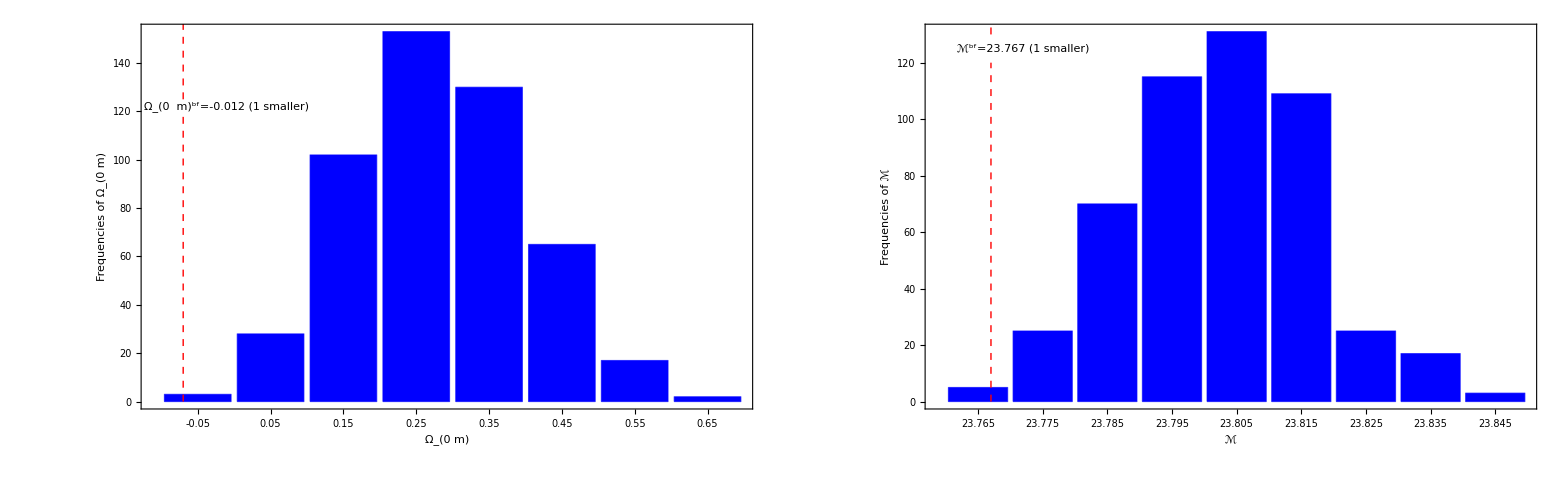

```mathematica
(* Figure 5 - Combine the two plots *)
barfig=GraphicsGrid[{{barchartom,barchartMcal}},Spacings->0,ImageSize->1650]
```

```mathematica
Export[NotebookDirectory[]<>"barfig.pdf",barfig,ImageResolution->1000];
```

## Section III - “Local Void” Scenario

### Hemisphere Comparison (HC) Method - Figures 6, 7 and 8

#### Real Data Analysis - Figure 6

```mathematica
(* Spherical coordinates of the pantheon data *)
phi=ratot Degree;
theta=(90-dectot)Degree;
```

```mathematica
(* Rewrite the data in a vector form for convenience *)
r1[i_]:={zcmb[[i]],zhel[[i]],mb[[i]],smb[[i]]} 
(* The direction of each datapoint *)
v1[i_]:={Sin[theta[[i]]] Cos[phi[[i]]],Sin[theta[[i]]] Sin[phi[[i]]],Cos[theta[[i]]]} 
(* Implementation of the HC Method for ℳ. We use 3000 random directions to split the data into the upper and lower hemishperes. Then we find the best fit values of ℳ as well as the 1σ error for each direction setting Subscript[Ω, 0m]=0.285. Moreover we find the direction corresponding to the maximum difference (Δℳ/(ℳ̄)) - This cell takes some time to be completed. Therefore you can use the following lists to run the progrm without going through the (time-consuming) data acquisition process *)
rnmax=3000; dMcalmax=0;
Do[
(* Generate a random direction where phir=ϕ and csr=cosθ *)
phir=Random[Real,{0,2Pi}];csr=Random[Real,{-1,1}];
vdir[rn]={Cos[phir]Sqrt[1-csr^2],Sin[phir]Sqrt[1-csr^2],csr};
(* Fill in the "up" and "down" tables with datapoints *)
up={};
down={};
Do[If[vdir[rn].v1[i]≥ 0,AppendTo[up,r1[i]],AppendTo[down,r1[i]]],{i,1,ndatPanth}];
(* Length of each hemisphere *)
upl=up//Length;
downl=down//Length;
(* Minimization of χ^2 on "upper" hemisphere with respect to ℳ *)
chi2up[Mcal_?NumberQ,om_?NumberQ]:=Module[{Δm,InvCovTotal},
Δm=Table[up[[i,3]]-(5 Log10[up[[i,2]]/up[[i,1]] DL[up[[i,1]],om]]+Mcal),{i,1,upl}];
InvCovTotal=Inverse[DiagonalMatrix[up[[All,4]]^2]];
Δm.InvCovTotal.Δm];
(* Best fit values of ℳ on the "upper" hemisphere *)
chiminup=FindMinimum[chi2up[Mcal,ombf2],{Mcal,23,23.1}];
Mcalup[rn]=chiminup[[2,1,2]];
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
chifunup=ListInterpolation[ParallelTable[chi2up[Mcal,ombf2],{Mcal,Mcalup[rn]-0.02,Mcalup[rn]+0.02,0.02},DistributedContexts->Automatic],{{Mcalup[rn]-0.02,Mcalup[rn]+0.02}}];
paramsup={Mcal};
Fijup=1/2Table[D[chifunup[Mcal],paramsup[[p]],paramsup[[d]]]/.chiminup[[2]],{p,1,Length[paramsup]},{d,1,Length[paramsup]}];
cijup=Inverse[Fijup];
errorsup=√Diagonal[cijup];
(* Minimization of χ^2 on "lower" hemisphere with respect to ℳ *)
chi2down[Mcal_?NumberQ,om_?NumberQ]:=Module[{Δm,InvCovTotal},
Δm=Table[down[[i,3]]-(5 Log10[down[[i,2]]/down[[i,1]] DL[down[[i,1]],om]]+Mcal),{i,1,downl}];
InvCovTotal=Inverse[DiagonalMatrix[down[[All,4]]^2]];
Δm.InvCovTotal.Δm];
(* Best fit values of ℳ on the "lower" hemisphere *)
chimindown=FindMinimum[chi2down[Mcal,ombf2],{Mcal,23,23.1}];
Mcaldown[rn]=chimindown[[2,1,2]];
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
chifundown=ListInterpolation[ParallelTable[chi2down[Mcal,ombf2],{Mcal,Mcaldown[rn]-0.02,Mcaldown[rn]+0.02,0.02},DistributedContexts->Automatic],{{Mcaldown[rn]-0.02,Mcaldown[rn]+0.02}}];
paramsdown={Mcal};
Fijdown=1/2Table[D[chifundown[Mcal],paramsdown[[p]],paramsdown[[d]]]/.chimindown[[2]],{p,1,Length[paramsdown]},{d,1,Length[paramsdown]}];
cijdown=Inverse[Fijdown];
errorsdown=√Diagonal[cijdown];
(* Construct the quantified Anisotropy Level (AL) for ℳ as (Δℳ/(ℳ̄))≡2 (Subscript[ℳ, up]-Subscript[ℳ, down])/(Subscript[ℳ, up]+Subscript[ℳ, down]) *)
alMcal[rn]=2(Mcalup[rn]-Mcaldown[rn])/(Mcalup[rn]+Mcaldown[rn]);
(* Identify the value of the maximum difference (Δℳ/(ℳ̄))_max^Pan and its corresponiding direction (xc,yc,zc)*)
If[Abs[alMcal[rn]]>Abs[dMcalmax],{dMcalmax=alMcal[rn],xc=vdir[rn][[1]],yc=vdir[rn][[2]],zc=vdir[rn][[3]],Mcalupmax=Mcalup[rn],errMcalup=errorsup[[1]],Mcaldownmax=Mcaldown[rn],errMcaldown=errorsdown[[1]]}];
(* Print the results as the calculation continues *)
If[Mod[rn,1000]==0,Print["Finished step ",rn," of ",rnmax," //  ℳ_up=", Mcalup[rn], ", ℳ_down=", Mcaldown[rn],", Δℳ/(ℳ̄)=",alMcal[rn], " and the direction is (x,y,z)=(",vdir[rn][[1]],",",vdir[rn][[2]],",",vdir[rn][[3]],", ℳ_max^up=",Mcalupmax, "±",errMcalup,", ℳ_max^down=",Mcaldownmax, "±",errMcaldown,", (Δℳ/(ℳ̄))_max^(Pan.)=", dMcalmax, " and the direction is (x_max,y_max,z_max)=(",xc,",",yc,",",zc,")"]],{rn,1,rnmax}]
```

Finished step 1000 of 3000 //  ℳ_up=23.8119, ℳ_down=23.7958, Δℳ/(ℳ̄)=0.000676444 and the direction is (x,y,z)=(-0.562598,-0.409537,0.718166, ℳ_max^up=23.7932±0.00464622, ℳ_max^down=23.8352±0.00912815, (Δℳ/(ℳ̄))_max^(Pan.)=-0.00176303 and the direction is (x_max,y_max,z_max)=(0.831471,-0.0718352,0.550904)

Finished step 2000 of 3000 //  ℳ_up=23.8017, ℳ_down=23.802, Δℳ/(ℳ̄)=-0.0000113984 and the direction is (x,y,z)=(-0.0790129,-0.247879,0.965564, ℳ_max^up=23.7932±0.00464622, ℳ_max^down=23.8352±0.00912815, (Δℳ/(ℳ̄))_max^(Pan.)=-0.00176303 and the direction is (x_max,y_max,z_max)=(0.831471,-0.0718352,0.550904)

Finished step 3000 of 3000 //  ℳ_up=23.7986, ℳ_down=23.8051, Δℳ/(ℳ̄)=-0.000274355 and the direction is (x,y,z)=(0.0182671,-0.882418,0.470111, ℳ_max^up=23.7932±0.00464622, ℳ_max^down=23.8352±0.00912815, (Δℳ/(ℳ̄))_max^(Pan.)=-0.00176303 and the direction is (x_max,y_max,z_max)=(0.831471,-0.0718352,0.550904)

```mathematica
(* Append the data to a table for convenience *)
dirtabMreal1=Table[{alMcal[i],vdir[i][[1]],vdir[i][[2]],vdir[i][[3]]},{i,1,rnmax}];
```

```mathematica
(* These are the asymmetries as obtained from various runs. The format of the list is {(Δℳ/(ℳ̄))_max^Pan, Subscript[x, max],Subscript[y, max],Subscript[z, max]}. Use it if you want to use the stored values in order to save time. If you run the do loop you can skip this cell *)
dirtabMreal={{-0.0002161179385637347,0.5206054691824148,0.8515803618940055,-0.061488476105953205},{-0.00046880986810177627,0.5824007975113504,-0.7847722785086804,-0.2119947686676188},{0.0015440036836521205,-0.7660456020320181,0.12927639727808563,-0.6296520854521181},{0.0013246621067511284,-0.6235820127815447,-0.1343283722765708,-0.7701307432747017},{-0.00009809876700383395,0.3050297532917744,0.5996789663023192,-0.7398256463392853},{-0.0002979086701894818,0.6117291540695573,-0.7092589903008637,-0.35034144307909554},{0.00045560100408408423,-0.4693979167005208,-0.8113606714741927,0.34836684196713996},{0.00026078788445561493,0.07422320951967158,0.8846561377766782,-0.4602982001514344},{-0.000029057664475167522,0.010065087160920558,0.23137512191680837,-0.97281254462431},{-0.0006575871836433789,0.8242633208175364,0.5264018919753788,-0.20854502170895572},{-0.0010484357752836946,0.7583862171384366,-0.4216225185010246,0.49707624922873284},{-0.00028332320059836863,-0.018630916186715668,-0.8047860773794148,0.5932724994623451},{-0.00005929998910597368,0.03706449543075568,-0.8965272563952654,-0.44143527466531407},{-0.0006131206207900072,0.7739120708064109,-0.6026103797633804,-0.19473273187003626},{0.0001494253083865838,-0.12087613824400234,0.5713116600543607,-0.8117831892131959},{0.0008291576947098044,-0.5812061131061327,0.6941992548029338,-0.4246019885953346},{-0.000321831625819086,0.289848476394775,0.2339338763475652,0.9280424571260895},{0.0006375424378499391,-0.37812128392740896,0.0055459041820469564,0.9257394544837609},{0.0015123532377912276,-0.846864548994264,0.3258033872824751,-0.4203243848410504},{0.00015071264850554392,-0.06363639833731485,0.9202854654999242,0.38603765463519535},{0.00022214904855682183,0.28452416803946284,0.8478084398419716,-0.4475118402167405},{-0.00015131586527502338,0.4376998601577595,0.8025307633340958,-0.4054173236558489},{0.000511630614668509,-0.18229833115491562,0.9816806194617625,0.055411910554526767},{0.0008876302033953899,-0.8887616419371893,0.45836778601648,0.0013101768818060133},{0.0007482899167902295,-0.8554637465312865,-0.12255212503036267,-0.5031528147801592},{0.0012751939924351358,-0.5844924960863792,-0.10964268078862192,-0.8039570912481576},{-0.00004041655868583769,0.04780306689806957,0.7209181005069408,-0.6913696255669634},{-0.00007161512683046361,0.3838727805770635,0.6836970087172722,0.620644897347177},{-0.0006177124308376746,0.5324032408904716,0.5769536037699888,-0.6194120826930527},{0.0004884867749148073,-0.3428214086737958,-0.6321233322965653,0.694905442863416},{0.000027859883957116426,-0.22098693295027821,-0.5565107903115841,0.8009123021479976},{0.0011809996296982604,-0.6100299614806701,0.3875560758746281,-0.6911322117717793},{0.0006572206997048991,-0.9672284216022824,0.05248453043613704,0.2484241423647382},{-0.00009505029739880237,0.046626322313929915,0.6982999105028151,0.7142851118840696},{-0.00004652771606919793,0.13912781034846972,0.5739461598266028,-0.8069877681897886},{-0.0003395298701443527,0.3813854873789698,-0.8787273309051851,-0.2870250649977365},{0.00007274103294139057,-0.2663492960026275,-0.6666425432154265,0.6961650465903706},{0.0004310636700179011,-0.1945413535186833,0.8536972499127515,-0.4830679737495789},{0.0006402922919416888,-0.8768110891791756,0.2846387039183802,0.38753467215733406},{-0.0005583084235586564,0.7373907711263772,0.6674567334490787,-0.10371287109675587},{0.0007928216877398908,-0.41810041375788204,0.9083742547059205,0.0069467548503867604},{0.0007327945801507573,-0.9240268682567445,0.32499194338843074,0.2013816860398281},{0.0005433615433751495,-0.6751565903765521,-0.7083172896172559,0.20603445270238918},{-0.0006648915036457695,0.9685270633268543,0.22450404325937187,-0.10748610218839272},{-0.0002990099424890864,0.1871645076180759,0.21897931551429906,0.957610310337651},{-0.0006148506258762628,0.2855660282335206,-0.9416403471526313,0.17822878592753755},{-0.0008164606427828527,0.5747957620217055,-0.2915469263669819,0.7645980785274396},{-0.0006787811262680119,0.8394276711001866,-0.09699351030387665,-0.5347461490747258},{-0.00002567921835522614,0.03242262343405164,0.3621211917351586,-0.9315669680629312},{-0.00001896831540037775,-0.10554714353236626,-0.2992415702029305,0.948321824674853},{-0.00035207512687761007,0.21107250059718005,-0.9239169566039959,-0.3191016402202652},{0.0006631752048511824,-0.8782800528468098,-0.4753067843060535,0.052034695771608686},{0.0006524565576287899,-0.7230397384658426,0.15166664370388724,0.6739516049293481},{-0.0007066198273960194,0.3531505633633559,0.3894536386149288,0.8506530097317806},{-0.0003229845183812733,0.44592051502618685,-0.7197518582014993,-0.532082847773041},{-0.0006621784014451697,0.820945645581473,0.5694698526260955,-0.041860888079826575},{-0.0002324320201163239,-0.2650684438895449,-0.8306258670144773,-0.4896931581106919},{0.0003785391764111443,-0.19213700101505213,0.5956704258656818,0.7799103259926357},{-0.00039199324294106824,0.1545603630916675,-0.9546973662527941,-0.25429123663813136},{0.00036420823165323396,-0.3931549634067043,0.8639562937133196,0.3146564750673617},{0.0008602326197962649,-0.9171158486468866,-0.23398197929178943,-0.3227242685752002},{0.0006158480878069691,-0.67049350208741,-0.6451646205274734,0.3663346503925087},{0.00018304320666673828,0.002142802065796928,-0.08501494970285414,0.996377371645065},{-0.0006787811262680119,0.7014936368129201,0.19422184552228644,-0.6857000453791001},{0.0004220760783939559,-0.16907343444561498,0.7157564754537539,-0.6775742332842831},{-0.000657894853147643,0.7132147216626759,-0.45127614725005827,-0.5363530551108808},{0.0006015697080820843,-0.4926245061883383,0.16473045761849603,0.8545086144887579},{-0.0005528497459144754,0.3361458729978467,-0.7946494717002937,0.5055078329689457},{-0.0002520162079038375,-0.012957220847567837,-0.9388062900126437,0.34420177259944973},{0.0006554711613953008,-0.6854466669286327,-0.0605898066195277,0.7255975069763101},{-0.0006550060749459409,0.90197859641304,-0.15882930454317637,-0.4015069907624189},{-0.00009307148895164158,0.26864276253195113,0.7621289905591488,-0.5890589680910515},{0.0006363189899757799,-0.3545821221948962,0.16009448984575467,0.9212172778127814},{0.0006631752048511824,-0.8925927869006995,-0.44865174411881226,0.04460638151643992},{0.0002824380592504254,-0.16520286215739988,-0.34260642477147557,0.9248399061677164},{0.0008867202183655078,-0.9445740003292841,-0.1872039917525342,-0.26969357310446007},{0.0004951597909794119,-0.6200098420516719,0.5026778295761289,0.6024141394519995},{0.0011064555677472343,-0.4928837013416925,-0.468270585901594,-0.7333405179935792},{-0.0008076222618912062,0.6215888319532713,-0.23294774032049725,0.7479055249632416},{-0.00027160637711070684,0.3417245051640088,-0.9089421476710692,-0.238848350962525},{-0.000113969700112285,0.27131162049774443,0.7555268291979218,-0.5962962476362083},{0.0006209628704579279,-0.26795451139857823,0.9627753023439289,0.03555414206116492},{-0.00011362948692807048,0.1005908425808097,0.5843946795984872,0.8052107431262105},{-0.0005973043356062498,0.7595269817715948,0.5312282436875315,-0.37538688984778357},{-0.00019647628659664822,0.11731112184189314,-0.4525413284721643,0.8839934653134294},{0.0006699166638359995,-0.8061124258927483,-0.1173667395752854,0.5800067286357766},{-0.00027487792418534444,0.2158252569412639,0.18287675752907676,0.959153559145713},{-0.0006572206997048991,0.9873513344559967,-0.05047121012009501,-0.15029969825976341},{0.00018804071187193843,-0.14203005808450112,-0.7523584839852162,-0.6432605803062865},{0.0007707168887841186,-0.6261300490790117,0.6588673642183731,-0.41695918026618417},{-0.00022730339050479456,0.157495619792294,-0.9067437387898025,-0.391166105269528},{0.0007430732422331188,-0.5246098120614661,-0.22199715354236937,0.8218891706963409},{0.0013253241172004732,-0.5275557424207431,-0.29977799796663646,-0.7948698576333197},{0.00025763046180389115,-0.12554695807485747,0.9688060906754348,-0.21366497136482399},{0.0010456181880684704,-0.5074597286887933,0.6183752067726985,-0.6000806007595303},{-0.00039280890871581345,0.25249023570948925,0.4832582528208667,-0.8382780815170404},{0.0003791325936541814,-0.7940687715009291,-0.36759636108454224,-0.48407406607295966},{0.0002941340781543661,-0.5322229480012403,-0.7360547202595,-0.41828481015281693},{0.001419003642748253,-0.8640778000296031,0.2385766705673822,-0.44322762521867254},{0.0006488209485675597,-0.3704925069688163,-0.5717425171086513,0.7320148881069464},{0.00006090235828373837,-0.04963272966368635,-0.5979877249578589,-0.7999670449123861},{0.0006659840602747881,-0.23110734910894168,0.9614552096380754,0.14897406837313065},{-0.0013242756957615462,0.7804884873734045,-0.203276639362243,0.591199060357142},{-0.0003306391848700217,-0.15467627186448754,-0.9322503529813584,0.3270848976767897},{0.0005472960510225281,-0.6612700826374445,0.6431739021216124,0.3860689179904617},{0.0016291206981464666,-0.850374314782356,0.2568128539873803,-0.4592501309583863},{-0.000759099078971698,0.9936310318755311,0.11182815684392969,-0.013850481250007984},{0.00048755633454836974,-0.1466286941492279,0.7699959349663522,-0.6209720494413459},{0.0012389547858860832,-0.8046865271829312,0.2679860871247415,-0.5297764151770483},{0.0005538102634487548,-0.4143094345880571,-0.438907796715867,0.7973127607114712},{-0.00046577884447849036,0.4063963851808468,-0.021186433995211737,0.9134512100416241},{-0.0006134751084151714,0.34958705590347205,-0.06419363977151593,-0.9347021273954754},{0.000019538963699139124,-0.02152644117917105,0.7004077425532463,0.7134182549540102},{-0.0002115061121749573,-0.4040554047419463,-0.9108992941925665,-0.08367619576860597},{0.0001866748215032226,-0.1349273989590816,0.4596688532802351,-0.8777808054031316},{-0.0013812390761925167,0.7822216325997946,-0.20230380247352348,0.5892389065546042},{-0.0006846599806607169,0.8400423103936968,-0.47403822653193745,-0.26384972339359325},{0.0007319896086117781,-0.9980164057520612,-0.04015055529878722,0.048489037512990496},{-0.0009613256438755868,0.5360791069879252,-0.3874507120471355,0.7500007578564147},{0.0002858397515942651,0.13914035951013906,0.9334795055693405,-0.3305389130456635},{0.0007155757923988072,-0.9159416022583453,0.2877076896814173,0.2797771730334633},{0.0003972663391617608,-0.8137104880044733,-0.5670354408932663,-0.12785167375713458},{0.0006600978124626438,-0.9010358339192683,0.23224925151980716,0.36632596299183895},{0.0003200938932193509,-0.690442455387171,-0.6971244283047464,-0.19314954636165926},{-0.00027836484774179703,0.21149875752306208,0.727309975423815,0.6529077080378287},{-0.0005854572914885189,0.42527268033196197,-0.16157176133008452,0.8905266494069468},{-0.0011519693546421432,0.7142510773826338,-0.4563059282538095,0.5306885134409602},{-0.0006554711613953008,0.7110790034314746,-0.07853554985181295,-0.6987122571476576},{-0.0006572206997048991,0.9771989393132176,-0.05355088124455596,-0.2054617631654464},{0.0006632026565334321,-0.9566245418900382,0.14478363316487786,0.2527987053393519},{-0.0006359038559513118,0.8404798232960584,0.5400093328809218,0.044537478978138756},{0.0003201062172797826,0.002038333066649251,0.9090590217060928,-0.4166623816149846},{0.0006079970845794313,-0.41278725261171395,-0.494720485256755,0.7647603059446757},{0.0006644101248422002,-0.4032169607114372,-0.5758696669707294,0.7111892921421501},{-0.00019546246313090923,0.3424831463287685,0.7216814080618691,-0.6015656570471634},{-0.0006648915036457695,0.9811101725352267,0.1681421170590447,-0.09566116149619075},{-0.0006632026565334321,0.9547121139403435,-0.15416901750313208,-0.2544733650849921},{-0.0006817563806931515,0.8612998807821339,0.5079091836116318,0.013812189096862548},{-0.0007483084123423893,0.8963261735019086,0.38787107685019373,0.21483812147404757},{-0.0005932634750247467,0.766626278201207,0.5741445423970742,-0.28747555375547995},{-0.0006457199778341198,0.7289876226421809,0.3640395888986766,-0.5797001153605059},{0.0006302086537584031,-0.623149348177409,-0.6327220029485813,0.45972574090516827},{-0.0009809523131441814,0.9213230125194535,-0.0998324651286852,0.3757624056613553},{0.0004886522278814389,-0.708571174492676,0.694728000316654,-0.12361187747984725},{0.00029766515319491847,-0.4387341758482349,0.6589300092457308,0.6110020997166796},{-0.000310832922077982,-0.16168588125615757,-0.9729167601825757,0.16519883037800276},{-0.0001855729168293297,0.5026231564412814,0.8379647435264748,0.2125677567638431},{0.0000359389905550031,-0.22106916104086538,-0.6362393216585019,-0.7391400081258064},{-0.00010344252543343473,0.3139946585594004,0.7857239900855881,-0.5329588781511649},{0.0005855901628022902,-0.7389000734599475,-0.6268923867648873,0.24704780277733107},{-0.0002818010226345878,0.6864269738945482,0.6820642609842039,0.2522030003747875},{0.0009838967142518052,-0.8834269392043422,-0.05374325515417669,-0.465476643467189},{-0.0006809905662847165,0.9360189577566208,0.309211817724852,-0.1680968842647066},{-0.00044520181214372623,0.7415820083890721,-0.6666794143589929,0.07479761562764287},{-0.00043052331670308,0.8100056930722986,0.36854637402056806,0.4561407100739383},{0.0008179349199140044,-0.5973137471143041,-0.025864005259788155,-0.8015905068925099},{-0.00006523065886101594,-0.08538690920416378,-0.5276834325805213,0.8451386103572587},{-0.0006211958941435585,0.20634570541798913,-0.9779153857755899,0.03321066272948725},{0.00043758305526875665,-0.8637546670112123,-0.3448531536571452,-0.3674291464065844},{-0.0006395624053726607,0.8340004047359255,0.5026122838135552,-0.22764932914470626},{0.00037306119957537955,-0.37964878242765204,0.3994072775988559,-0.8344702682554195},{0.0006556672505837906,-0.8398829272239581,0.13657805587568617,0.5253028680779626},{0.00031052553890042404,0.022083464491794005,0.9959920005205843,-0.08667326863020697},{-0.0008096663159039836,0.9754253636553715,-0.2201370993959001,-0.009220488454848352},{-0.00001706088225352869,0.13226678321259144,0.372455264621938,-0.9185763843655004},{-0.0003409446174436903,0.35010428082011685,0.19596979079132296,0.9159818959175088},{-0.0005902585021196012,0.6442335862356372,0.6667459677424638,-0.3747170944394387},{0.0007247708109404584,-0.6218995223534531,-0.31357747180242934,0.7175724028100186},{0.0005534126173647005,-0.800818755715177,0.5570931605783211,-0.21985570479669725},{-0.0004328884449661791,0.24308276573981907,-0.9172149463867726,-0.3156382599194688},{-0.0003523654299701149,0.2879018838464632,-0.43644182639711016,-0.8524265583901128},{-3.3040273782158723*^-6,-0.11465200076879495,-0.3938156019387137,0.9120110692252374},{0.0005122620458037676,-0.1857091395525714,0.03320041265751357,0.9820437098653065},{0.00004793554977451368,0.09619889366677312,0.7839763659175429,-0.6132917988527252},{0.0003751236708856281,0.1537577050032576,0.9857162598935753,0.06871697849551373},{0.00003908917758956095,-0.09155508844144435,0.9137057176850897,0.39592868960212324},{-0.0007599497736156308,0.9825815443126883,0.1853970068493849,-0.01270663713898601},{0.00021287991733851482,0.35004256762508557,0.8044384849584805,0.47994679368461446},{-0.0004505629453124157,0.6284732192898205,-0.44496152197859956,-0.6379895426995473},{0.0006392703687074202,-0.4977196579508377,-0.41359452393363466,0.7623743908745959},{0.0006787811262680119,-0.81325671794399,0.006729050847084419,0.5818661620971499},{-0.0007954687204335435,0.4194752389956289,-0.904408397896461,0.07801265079406483},{0.0006852556801152449,-0.5022077106328393,-0.7477815511984062,0.43429272048726286},{-0.0003089883430120143,0.7429456952942097,0.6484405668682762,0.16600158156882738},{0.00013613569848878367,0.3591940546345691,0.8163641733360425,0.4522490106219561},{-0.0005357449568983241,0.7260699446909032,-0.6512380697493069,-0.2207066195784475},{-0.0006524565576287899,0.7609643365148561,-0.20223877753376393,-0.6164679678735575},{0.0006073905848874786,-0.6821668270451474,-0.6226394895218896,0.38336469081942925},{-0.0010814418448680096,0.8282339702953855,-0.3962617915311857,0.3962386692654285},{0.0006535378456260583,-0.39139888278367213,0.1750514715510912,0.9034178971348148},{-0.0007318728792621244,0.9850368748919229,0.16891058169586362,0.03422821196497572},{-0.0005112379837765975,0.22589407622700622,-0.4595275924118256,-0.8589564937397811},{0.0006699166638359995,-0.877727613530466,-0.15799624136507656,0.4523620498678258},{-0.0008485079005273883,0.9977565403412729,0.02256097217361332,0.06303085546615406},{-0.0002543007414645689,0.13167030821182388,-0.13592309602222163,-0.981930670619437},{-0.000408874818666246,0.3394652304756216,-0.2830226829591006,0.8970292738973269},{-0.0002884073759334265,-0.3398066245937543,-0.8342778088138996,-0.43417968124139306},{-0.0008247183666855353,0.9923962679753678,0.035887416959473444,0.1177358934757744},{0.00005759393788645568,-0.0729239694856039,-0.5709900598920278,-0.8177117133678355},{0.0005119630277658863,-0.5175306234099671,0.4391594135868705,0.7343712026563451},{-0.00032491814194080356,0.3065644151844578,-0.9274931229468449,-0.21395038263326405},{-0.000739389094135039,0.5341964042583163,-0.1554052950202411,0.8309533055215301},{0.00003819276061200369,0.09814387241327813,-0.6520217440296361,0.7518214054017602},{-0.0006856010696791168,0.4881077478218438,0.5345795501134554,0.6899097992613115},{-5.434938102863422*^-6,0.020476404994768573,0.7133186681207492,-0.7005406444660657},{-0.0005582555010286938,0.6409132581897973,0.6708284973770277,-0.3731210562048428},{0.0007925901829803396,-0.48539394192501933,0.4979883800156772,-0.7186099738466287},{0.000280397313468802,0.0650594871233451,0.9606175421472044,-0.2701503301021697},{0.00007894844497042607,-0.2793517823893915,-0.6402519625388442,0.7155697073947642},{-0.00002984148512756304,0.08191105951411641,0.7865159267577512,0.6121137764220559},{-0.0016240512043479733,0.8119594658683484,-0.2373452170493632,0.5332814207625998},{-0.00043062495737442524,0.27049564621204836,-0.39547449927836287,0.877742573765711},{-0.0003390081271490722,0.5491890732644306,0.7965548321317553,-0.2527681966041361},{-0.00037657189114350634,0.23357471822146447,-0.19191704424906816,-0.9532107317558194},{0.0003960866573899057,-0.7296228708610123,0.6838343380307559,-0.004589602005896198},{-0.00004080733137951599,0.03994262738136164,-0.7647225438694205,-0.6431205310171306},{-0.0006049165314461522,0.6312529387510359,0.7134941897010256,-0.3040489575398305},{0.0005682148235214442,-0.46886357733431966,-0.4972586641527012,0.7300005251877122},{-0.00008987240394959577,0.05984764531702947,-0.8085044562167101,-0.5854389836932018},{0.0004543195668319492,-0.7722683209761735,0.6352964801250857,0.0001508552898816795},{-0.0006384368769569276,0.8435099415351138,0.44484238379558466,-0.30100869108796613},{-0.0002621488007593306,0.5086408439073536,0.7685777236772738,0.3880370788678258},{-0.00033770743287432175,0.7081966138713344,0.6862927866957937,0.1657098881494341},{0.00022410021535638631,-0.3240027758835147,0.7966314827336191,0.510294505102115},{-0.0006524565576287899,0.7977173997926843,-0.1596220916919798,-0.5815219152464299},{0.000635990369492622,-0.7790145267248079,0.42225497339521517,0.4635052368579342},{0.0006384368769569276,-0.7698426388733719,-0.4778661358502788,0.42306768675946627},{0.0002161179385637347,-0.518769175857022,-0.8482390510968466,0.10662576787506506},{0.0009066977080722765,-0.9216126187849523,0.2759798091851392,-0.2728833557007031},{-0.000800787067992653,0.9065662385227488,0.19050218303580405,0.37662524268735287},{0.00004473050201714902,-0.2591232373957786,-0.6784359831529746,-0.6874443720075013},{0.0006629326111589785,-0.48871836052594675,-0.6102214143353802,-0.6235256126025289},{0.0005956388801453579,-0.5933209860078229,-0.5210652875734769,0.6135643190804649},{0.0008286929292433442,-0.9958266888233881,0.09052905607045944,-0.011562691470354713},{0.001700504515589267,-0.8327452861333311,0.040872472156950085,-0.5521455690689692},{0.0003082728278133823,0.4031880938379531,0.7802684285025121,0.47814280342753035},{0.0004028949465846132,-0.23795663486050117,-0.03558598833880327,-0.9706236538225393},{-0.00013706511995563968,0.0033695896354923216,-0.17043919927587392,-0.985362433430404},{-0.0006302204404927039,0.8441242724610127,-0.3639523883599463,-0.3936913405820056},{-0.0006436013849309079,0.8390502130179295,0.5362209533906258,-0.09198820130546903},{0.0006149862976768034,-0.47325885024695014,0.05520381521651431,0.8791920151186974},{-0.0005605670566511919,0.7923657275822362,0.29964125525018037,0.5313865560071782},{-0.0006221995533818314,0.20283212156812788,-0.7986127567505673,0.5666363871261988},{0.0008390832092956542,-0.8503988328489711,0.5028161146042809,0.15491216860970702},{0.0005034586035037512,0.1376285911021324,0.26965163456257796,0.9530720680457339},{-0.0006015697080820843,0.49907524238031375,-0.2369804708504024,-0.8335251399199383},{0.00013569198457703127,-0.35416665396080477,-0.7869695803336009,0.505217637114703},{-0.00018696072160352472,0.03194391128656522,-0.9496539788898245,-0.3116679433474686},{-0.00020585714815317242,0.47561062082432226,0.7398443101073909,0.4758412909372425},{-0.0006699166638359995,0.9451736067057407,0.013098373358027542,-0.32630550991706453},{0.00032954864251559166,0.16212235601128758,0.9781076665904715,-0.13046736848075202},{-0.0008877862967791457,0.5467382284663754,-0.3388322972233592,0.7656826913884045},{-0.0002877688200883096,-0.04811545651127079,-0.9987950736528444,-0.0096593835994494},{-0.00038320620880995064,0.3915287048423071,-0.5102968400768128,-0.7657038646187737},{-0.0010961556963714576,0.8661811907539018,-0.2649620178047796,0.4237042292743518},{0.0008333627349065685,-0.9248565651704339,0.371938865515242,0.07938396677151927},{-0.0003234074081816612,0.15368190581123506,-0.868842471707908,0.47063216122861795},{0.0008289193432712495,-0.9943504641901603,-0.0606822104700636,-0.08709089330854236},{-0.0003382668344323435,0.21548170778968015,0.14677339758262062,0.9654145241139149},{-0.000011322530906987616,0.017253051879896505,-0.6312064486952709,-0.7754229499610739},{-0.0006457009182328081,0.7915347254423741,-0.33606144397884985,-0.5104267668233275},{-0.0002872929616272045,0.011240963819453317,-0.8345070675966405,0.5508825599559908},{0.000028001636534918255,-0.18439650705377722,-0.7625926700950287,0.6200406016574245},{-0.0005186098918134282,0.33326218297623,-0.521917123496981,0.7851998685675863},{-0.0006573970644870394,0.9123511619702966,-0.17462318383505188,-0.3703000147431261},{-0.00176303421926961,0.8314714529826971,-0.07183522559423389,0.55090373318636},{-0.0008778024777220044,0.972878279884125,0.10523117906255425,0.20599575598252207},{0.0005620783730717024,-0.8119800674537663,-0.24778420604944237,-0.5284802335851594},{-0.00009505029739880237,0.04558951397148676,0.6761375449762123,0.7353635947539041},{-0.0006195677873586014,0.8065875505536547,0.19331490924205055,0.5586106597233831},{-0.0006727474105769686,0.39388974687177447,0.5020251945170744,0.7699490706399892},{0.00030460503987504565,-0.1945557502394709,0.9222633071145835,0.33403360968445694},{0.0001103981347321023,0.25026913589897914,0.926690212197756,0.2803758374633165},{0.0006554711613953008,-0.6101140987323105,-0.12014665970080934,0.7831510497284662},{0.0006554711613953008,-0.7507067540757117,0.019918477308411342,0.660335235805892},{0.00045822497145025663,-0.02336480054381304,-0.05956111244052187,0.9979511811608799},{0.0007733004691309162,-0.9863489358809288,-0.16179387537962742,0.030635250549018167},{0.000033816146261948,-0.23638582614638434,-0.7989776069487806,-0.5529525520254801},{0.0006687847093639283,-0.5648082929247875,-0.031004777768937047,0.8246394945664961},{0.0005757025350464837,0.12120285735907811,0.1834546534672579,0.9755276815596794},{-6.7525947608526725*^-6,-0.05033010325676927,0.4099371830463774,-0.9107241001874079},{-0.0006242996443509074,0.593477544326818,0.5547960390590002,-0.5830829781637037},{-0.0006403517957443174,0.5169561899146177,0.5190764223356125,-0.680673170827397},{-0.000824749291056944,0.5156265894328401,-0.8527951455419558,0.08288341215183936},{-0.0009021671797499264,0.8673707035081382,-0.49613595207428846,0.03895099170928651},{0.00027740057034711705,-0.32657759528385966,0.896385846148139,0.2997323624233732},{0.0007180504362003674,-0.815314334598202,0.4380783550694925,0.37861575590339425},{0.0006310064528864018,-0.7147285009465532,-0.6309447587313068,0.3017811812624933},{-0.0005649689436730277,0.6009972065781868,-0.46224770014277144,-0.6520194946456239},{-0.0008277028431920824,0.8383074521946198,-0.5254886557771878,-0.14526626671202647},{0.0008107304847063049,-0.6663950915101977,0.5733356695814376,-0.47665898921212},{-0.0003268289543159415,0.023736903265532967,-0.9923937633239617,-0.12079394827170575},{-0.0006207960548516953,0.6098532759696589,0.5547942710353647,-0.5659348890247121},{0.0002589353342554597,-0.5608799845195881,-0.629508185483571,-0.5377109701080021},{-0.0006548538091585115,0.464528426123495,-0.02291356841624751,-0.8852617181973151},{-0.0005741364736703428,0.27268922856374506,-0.884133452512978,0.3794056177401586},{-0.0007598919988697736,0.8888730887064453,0.451841696652448,0.07578729009339846},{0.00046577884447849036,-0.39065746398731266,0.01963234198455271,-0.9203267446832147},{0.0006772357461937734,-0.40919511187440305,-0.5886520299236644,0.6971715341900042},{-0.0003353487448895173,0.6976470698721415,-0.6811436229833697,-0.22210792594570816},{-0.00023562551707592697,0.04512866591121958,-0.9359642241527124,0.34919102883562814},{-0.0004935543210557031,0.37569143077158873,-0.08145321797433466,0.9231583407663184},{0.0008216139950942762,-0.6774323494277714,0.7146727892782823,-0.17414998195225195},{0.00020504576516658523,0.23496723667960095,0.9710090596773392,0.04395228903802417},{0.00028187106340717426,-0.016267452344745706,0.7936055510953508,-0.6082150929275398},{0.0003740249521985259,-0.8012485721606609,-0.4277792618421062,-0.41833674085397377},{-0.000036726495461672185,-0.04817294393988785,0.6892153403968485,-0.7229533747302247},{-0.00042036959742048025,0.1861314261563934,-0.9614816372089082,0.20225764140586766},{0.0000994853789991073,0.38190858518211,0.9020202395559436,0.20125933517637673},{0.0006849797794090203,-0.2372931423359357,0.9636726793302279,0.12258438608908251},{0.0006699166638359995,-0.8452243026585525,-0.1774580713635947,0.5040878009863727},{0.0012442573277797236,-0.6416113124498138,0.3986311049455613,-0.6553076879652093},{-0.00017174438339395391,0.08452228592179317,-0.5278792640948536,-0.8451032278492554},{0.0012030575508854594,-0.7683484621636161,0.27389358206132114,-0.5784660287315276},{0.0006699265659388302,-0.7794373436775934,0.533109426755051,0.32904675410299666},{0.0002787658466427377,0.09705709393264597,0.920875666830965,0.3775816822304483},{-0.0003342465201062423,0.5801988428530537,0.8120549408223299,-0.06273815296946361},{0.00039814175623137165,-0.5490365484906817,-0.8104995856785432,-0.20408157691557793},{-0.0005563648000310917,0.725262683725666,-0.598782384570518,-0.3397847782392389},{-0.0009295580600449615,0.5683224127070288,-0.5697161675006858,0.5936607816785544},{-0.00023355636240679378,-0.25376157247017667,-0.8514485060806701,0.45895588658438435},{0.0005098896923899892,-0.7267136013679611,-0.4383231254271021,-0.5289236044105282},{0.0005041866246464793,0.14151707154922588,0.2611510244408772,0.9548680855980116},{-0.00039288519823668097,0.2213036441848317,0.4333819650192183,-0.8736159164453189},{0.00044585821957716807,-0.4757237382347968,0.36569498566614905,0.799971313447267},{-0.00010635715196774865,-0.09174471945604683,-0.7033983406733699,0.7048501122862088},{-0.0006699166638359995,0.847268880963902,-0.0470597646097263,-0.5290754406557296},{0.0014222575792927517,-0.7396611381884248,0.018265690629229503,-0.6727315699442394},{-0.0007854376503985423,0.45272386292884254,-0.7143145059570997,0.5336627123137341},{-0.0007992174826611167,0.4576571661298879,-0.712893462153721,0.5313500069713386},{-0.0007327945801507573,0.9429238645940784,-0.30802442749176295,-0.126552509447027},{-0.0005504388641515141,0.339588470191484,-0.07361105679737091,0.9376892252927842},{0.00014615364925981046,0.023738709510552628,0.9097434714854075,0.41449160396858864},{0.0005592981520840386,-0.6433996588733946,0.6068849529506125,0.4666128297033125},{-0.00041721539590229215,0.7916076177077498,0.40262091469236044,0.459623518370577},{0.00019265643834186748,0.2635497954050682,0.9026549205737909,0.3402287461486313},{0.0001950517859244799,-0.32346056539389606,-0.6784041798035125,0.65965220492331},{0.0006524565576287899,-0.7630173841946026,0.11873694895839211,0.6353786338624225},{-0.00019249958190446873,-0.3728357248758845,-0.9085017325522644,0.18872764557903965},{-0.0009157856833709914,0.943361610426931,-0.1230324115138954,0.3081102038066619},{-0.0008835816967666155,0.43684419847244826,-0.6164876961197887,0.6550649332653056},{-0.0007595801009703044,0.40591751794432623,0.48153355567215356,0.7767601968353235},{-0.0005517776799879866,0.7835627459585949,-0.5816687045203011,-0.2183825572876673},{0.00009079591640934897,0.2545581962115604,0.4807910455241195,0.8390709715425393},{0.0007081795867380569,-0.534762899535864,-0.7610829519879538,0.36712583874374394},{-0.00034280687442086343,0.20712225833908654,-0.7505275387063692,-0.6275418581607732},{0.0006366662751890992,-0.37105703017510233,-0.19686599217475592,0.9075023203731669},{0.0006436013849309079,-0.850330925699303,-0.5252604904738084,0.032229395690595464},{-0.00048679947059150646,0.5293246606308938,-0.3925378387100986,-0.7521498845501432},{-0.0002828887157042642,0.6974505784784825,0.5967178256231574,0.3968507618281729},{0.00021279883089342523,0.24567974583116034,0.9675463792732164,0.05912246987081704},{-0.00037498242645278454,0.2756776213016436,0.30595437326261615,-0.9112594419784891},{0.0004896880658199474,-0.5932349965573933,0.6962828060291559,0.40405753660551147},{-0.0006554711613953008,0.7252971391957675,-0.023938180401746407,-0.6880196388138125},{0.0009542637655423078,-0.9023212889719116,0.2080019441463865,-0.3775599061068212},{-0.00032093833379700614,0.37265116313743724,-0.763745113952609,-0.5270906103563516},{-0.0006490809742979264,0.3639462296539956,-0.8957442564918462,0.25531425514943473},{-0.0006647165898982947,0.42939266461972225,0.08021210628173686,-0.8995487521955784},{0.0002508304641582238,0.0953359062613175,0.932704627952774,0.3478119347762678},{0.0008333627349065685,-0.9306352935299306,0.3595326540533129,0.06822185211382625},{0.000675051751834975,-0.5083409573733033,0.8553344993239472,0.09996181932641113},{0.000539585399581099,-0.35167158962987355,0.6523710234029798,0.6713710902856531},{-0.00047056104231241603,0.20011390531029033,0.19991315951856678,-0.959160650544406},{0.00004128727652508913,0.2733313488522833,0.7653963918181178,0.5826305322641423},{-0.00021879984788063895,0.07375156215506203,-0.9287805206846316,-0.3632181871499175},{0.00007527382034722218,0.29367579711404357,0.916789512966256,0.27065017107795475},{0.0001621627552580427,-0.05080454495026053,0.1609243649158373,-0.9856582810430963},{0.000851272511640768,-0.7071881280267129,0.6774777930554392,-0.20225921856569373},{0.000792510153726826,-0.9674178672765844,0.07768466306140613,-0.240972536192531},{0.0009218529545097589,-0.5554613958482552,0.7744862886276911,-0.30271046637011534},{0.0001595503908904365,-0.019807626264607414,0.911322910183515,0.4112155290312012},{-0.0012327773689711674,0.6502447174354433,-0.42597612552737174,0.6290676815160585},{-0.0006497378000532019,0.6311429210616937,-0.356773262448714,-0.68874629029521},{0.0005602281033722994,-0.2530411225728142,-0.13706724420061772,0.9576965912304054},{-0.00027872423060822755,0.1833375824254669,-0.6588566802725728,-0.729585639750804},{0.0009564827601520868,-0.5810282840748697,0.5214055067306581,-0.6249339410337369},{-0.0014089444320003342,0.7593946934604356,0.14774807755311534,0.6336325473991133},{0.0002284992979857869,0.40677075759454745,0.9075433174909361,0.10441588788830836},{-0.00006331256679155693,-0.08903535250974212,-0.7800971579302335,0.6192908284422096},{-0.0001428065830082728,0.2420709628648394,-0.6787504997619671,-0.6933248935459979},{0.00029685860427328256,0.03317780003200828,0.9896327128393809,-0.13973663536525927},{0.0006524565576287899,-0.7620842021040471,0.21880788956813282,0.6093855728241173},{-0.0009023628781530202,0.8921445957325416,-0.04933621028206728,0.44904783560353967},{0.0005244631229881282,-0.18858699538265516,-0.05841041990829614,0.9803178913080588},{-0.0007783637564130458,0.8878321670791312,0.4390521859271096,0.13779412589874962},{-0.0005603104711187714,0.20744415843140218,-0.04120434529016396,-0.9773786999223465},{0.0003591939253910567,-0.18510248049604777,0.9737294003751982,-0.13262023435044645},{0.0006608994254008213,-0.655427393240863,-0.38869929495518296,0.6475552411113903},{0.0002527476463674883,0.004185396730509005,0.9722883936437735,0.2337472182504401},{0.0009899407310941708,-0.7269924072318221,0.5126015892034052,-0.45686064677691807},{0.0006986396446768584,-0.784239673498751,-0.08608995025209513,0.6144563898082305},{0.0012812614125046918,-0.5277879271437398,-0.37209280764267094,-0.7635357532309202},{0.0003222211933191974,-0.13799681473920136,0.959445574406633,-0.24580697482651026},{-0.0006375932451020314,0.5813555713740268,0.7231565419781052,-0.3729213260550376},{0.0002585083456173681,-0.18741517047688863,0.9336819411113391,0.3051451895699502},{0.00038050388288937963,-0.775641618162856,-0.5230699145338158,-0.3532392173630964},{-4.672654781162185*^-6,0.1429926624967495,0.5350222867344964,-0.8326489363287994},{0.0002230222025777821,-0.6526357057157411,-0.6578719533876545,-0.3758605174407499},{-0.0008275399971630729,0.8593878750969846,-0.4140890006985188,0.2999712980216469},{-0.0006776630858442023,0.9676239483598325,0.2513077730830389,-0.023415758552140176},{-0.00018528354870049423,-0.15394959938284433,-0.3230511594944866,-0.9337759202287932},{0.0002597695049890583,-0.5324587039803585,-0.6288903194333035,-0.5665551117752221},{-0.0005569683637226289,0.44001984978356823,0.7112129540636297,-0.5482323100370237},{-0.0006990079528758215,0.5768070307687183,0.1498451169003274,-0.803019358544302},{-0.0010776009552723124,0.5494476677282677,-0.45988786401883114,0.6975746647894865},{-0.0011035761890634214,0.659333666992636,-0.49039867760571754,0.5699019675107355},{0.0010641415399968706,-0.6196898542268534,-0.4968325089869755,-0.6075705247804637},{0.0006532579348107365,-0.33059300676949227,0.9406386056358244,-0.0768588151261681},{0.0007401802450858637,-0.5092889990150703,0.37432772704379963,-0.7749215884516643},{0.00015664126246563135,-0.3111144456504968,-0.6417236074430562,-0.7009982976854183},{0.0008144547027329221,-0.980209422394979,0.1832499489871614,-0.07489288647331127},{0.0005944463729562576,-0.6138055412107528,-0.7206176090737935,0.32241746086672185},{-0.0006892815114967567,0.25440725596210295,-0.9567460216545333,-0.14111696624451808},{-0.0006572206997048991,0.9938129571427682,-0.0029523870678017537,-0.11102742735805593},{0.00045982675678593935,-0.5529401838337896,-0.5854442223949057,-0.5928846562074945},{-0.0006600978124626438,0.9201043585521396,-0.2419483393598262,-0.30800806881375387},{-0.00024142399030109912,-0.057335481743306126,-0.9551680613270294,-0.290459320996981},{-0.0007994970985929409,0.9208416390155801,0.37033055048809105,0.12208996367551062},{-0.0005899659216479146,0.49028953202646797,0.5415524598662835,-0.6828887962165174},{0.000011442839247044264,0.026569133548344212,-0.5980058713417188,-0.8010512211983213},{-0.0003682487485504184,-0.0426371986835419,-0.41686642814229613,-0.9079672077648532},{-0.00043694128759712655,0.383495063599906,0.20742901368138292,0.8999470764870969},{0.00032116518061602744,-0.08163401819268314,0.982584197339565,0.1669256787084581},{0.0015320761996923482,-0.8452203820160897,0.3272938742883944,-0.42247038437962503},{0.0009072307608803519,-0.71065853198569,0.12711990289593036,-0.6919573550470239},{0.0006812919936919617,-0.6770266041248664,0.2598541434573456,0.6885570429784309},{-0.0004204353967018855,0.23777113344218098,-0.363035654069034,0.9009273011604706},{0.0008286929292433442,-0.9940222929291019,0.1091232454748778,-0.0034348882078152343},{-0.00037898674456096783,0.7873839119205994,0.5860014813187544,0.1913866221574516},{0.0006230871328996034,-0.4276017420331494,0.22901957457068342,0.8744751481166742},{-0.0007461558194285409,0.9732180849085599,-0.19245749863768533,-0.12572458162603084},{0.0005391982772570591,-0.3766301981837834,-0.633887859306474,0.6755263693149955},{0.00022985457601175935,0.09093770964066604,0.9717572017198499,-0.21775737386117766},{0.0006818002237021839,-0.541798403734129,-0.3239309343791147,0.7755792928278986},{-0.0015517027060948552,0.7760748588250359,-0.13817694346264414,0.6153169474303644},{-0.00021236950170696613,0.6028967307116443,0.7728465937397969,0.19804967720752353},{0.0006699166638359995,-0.9516206789778489,-0.000765753728216648,0.3072743024773883},{0.00007912511659389536,-0.2510056410805262,-0.823051288688654,0.5094926342290926},{0.0006646796993148348,-0.5000090982939722,-0.7647699105901052,0.4063470013169177},{0.0002907108154510429,0.16208367765775086,0.8581895379445553,-0.48707247756309213},{0.0013099939727894481,-0.5814752752462299,-0.21353992129780278,-0.785039620840534},{-0.0003376101707443082,0.28001950875068576,-0.8893100635235993,-0.3615476256797664},{0.0006384368769569276,-0.8029054178132631,-0.4891591229249373,0.3406849607854969},{-0.00015287399884806612,0.6661413153263694,0.744903528593054,-0.03707399499476194},{0.0008897805358790402,-0.5361775176108197,0.7194028758466426,-0.4415576653533255},{0.0006699166638359995,-0.9377513786037112,-0.29244411664996844,0.18734671217733934},{0.00045064604912787285,-0.7277050094460976,0.6835281249866463,-0.05687461278368988},{0.00022650359734585515,-0.11993205942841102,0.08311244023123833,0.9892970349698158},{-0.0008874048158987046,0.562136503807183,-0.528862883102769,0.635851084738922},{-0.00008634595394697393,-0.26053446217935244,-0.8133377727169675,-0.5201955992592768},{0.00003348607303370308,0.11152731702158311,0.6276126991183351,-0.7704959165779957},{0.0005741197039400848,-0.25330446236161563,0.0313998654322284,0.9668768783038153},{-0.0006316864113980686,-0.0855840369643549,-0.14680348023219522,-0.9854562957374616},{-0.00024060123031882866,-0.3923530269750347,-0.8591835935390445,0.3284245039835816},{-0.0006384368769569276,0.831493631868824,0.4497223820927957,-0.32614125652295844},{0.0013473292010383238,-0.7381116671816915,-0.22934474480905132,-0.6345015010216564},{-0.0001822870586251089,-0.06724676843054371,-0.4615081173382377,-0.8845835911696329},{-0.0008525641300155419,0.9840024886519202,-0.0010213649872056103,0.17815178680100408},{0.0006305382332575791,-0.5638260193440217,0.8077227394235347,0.17229102161405696},{0.0006575871836433789,-0.8077169176085962,-0.5585044885402877,0.18885475183118827},{0.0006524565576287899,-0.8260129598686018,0.17301671669093918,0.5364399368751349},{-0.0006225479480825288,0.758258616492519,-0.5834313775537524,-0.2909496489095349},{0.00019042749812169023,0.02912784666112384,0.9512843688476564,0.3069358534531308},{0.0005898625691134393,-0.8324165143998283,0.49051832628306974,-0.2578265272133501},{0.0006384368769569276,-0.8405096783340282,-0.45612532457487454,0.2923921491905923},{-0.00027313032129403777,-0.09461491481231864,-0.9054611028141714,0.4137489688030682},{0.0010053127611543977,-0.9243817138581192,-0.0012978937644252484,-0.38146659428644925},{0.0002091421499997626,0.3939055087948142,0.9178836213283206,0.048250469824724807},{-0.0001433780076659416,0.126334728167612,-0.858572546540145,-0.4968830031168163},{5.0952578914860444*^-6,0.19390334225922085,0.45313328686059984,0.8700986830237205},{0.0007180504362003674,-0.8442037760500658,0.42175129945270057,0.3308259752691267},{0.000305547294548445,-0.8023105700266427,-0.5046705042123351,-0.31875606880746765},{-0.0007408284399350181,0.5874885150484044,-0.15429862828593224,0.7943860383939918},{0.00013353055720463853,-0.08106570933235521,-0.21969978056149178,0.9721935801020671},{0.000040380742527790206,-0.1926016633842335,-0.8367779193695715,-0.512549815059139},{0.00043328476897496555,-0.1732778869644301,0.957635381614394,0.23002010731541733},{-0.0002421250425455641,0.6492473165886633,0.7351396361179738,0.1950580357502687},{0.0007443603013214897,-0.5546707169416902,-0.1613747941877689,0.8162711385123491},{0.00022602513045997483,-0.6006296466299628,-0.6781685915932907,-0.42347536996328206},{0.000818820262792934,-0.6180461577819141,0.7511354982257705,-0.2319793313123757},{-0.0003860882527423808,0.24222935939190687,-0.28766564471700695,-0.9265923668464656},{0.0002937549765234825,0.4575649129301022,0.8832974750583564,-0.10207801433609631},{0.0008744181365988157,-0.8871283228975806,0.38306544591673347,-0.25741834211559234},{0.0012894930682001782,-0.5359096003180883,-0.31497242726967534,-0.7833219455286287},{0.000882674930805381,-0.9873268338380432,0.15000676432535776,-0.051804380509584025},{-0.0005041948284440365,0.5069481712754303,-0.41496968825622704,-0.7555155256306958},{-0.000049869003481209976,0.06348048040903662,-0.8397468322345073,-0.539254565450445},{0.0005000869355264347,-0.7609931107906736,-0.6485986951997853,0.014464367053886873},{0.0005647079054863938,-0.6724370223412308,-0.6908246210899898,0.26568739879928627},{-0.0007483084123423893,0.8938901259335318,0.4020943756368849,0.19819322854153798},{-0.0006699166638359995,0.9494103047278193,-0.04472459002916057,-0.3108372312374318},{0.00011107561348648444,-0.2158544863021636,-0.792908272878892,-0.5698274401460863},{-0.0006454313419134563,0.6272364400885048,0.6774439699445759,-0.38424486439096606},{0.0006699166638359995,-0.8276035208858882,-0.17827433492145278,0.5322505741900099},{0.000022670957935091403,-0.16223002779211726,-0.4596188593615915,0.8731734777246263},{-0.0009117349566283056,0.9009743152802803,-0.2977570620550582,0.31557251971863853},{0.00018904766177548318,0.1868928147684063,0.9795114874430089,-0.0750221417657897},{-0.0007460277776038844,0.9311269622494296,0.35769969245242617,0.07108804534933433},{0.0016717795056118846,-0.8151143689349333,0.2203217413806154,-0.5357675763153447},{0.0005841365203074072,-0.31283908189956866,0.11033052380653005,-0.9433763217045527},{-0.0009338561533122457,0.47668155675089474,-0.8563612360136414,0.1985450248853693},{0.0004868654971676785,-0.7163311976655639,0.6832478889057314,-0.14156955024609053},{-0.00038381752336343414,0.45916277172916886,-0.7405834041151842,-0.49061774387719903},{-0.00007471076885881451,-0.39043492179587613,-0.7215757280983354,-0.5717421101000042},{0.00008349301431144536,-0.11922078126647458,-0.4326857691171325,0.8936271205137671},{-0.00015460038714255485,0.6468973849269231,0.7554530395655747,-0.10399268429001407},{-0.0005603104711187714,0.20071948438907203,0.014164132925130904,-0.9795463572108593},{0.00019716735135293627,0.3088057820650449,0.7534815436131657,0.5804347959913474},{-0.0006909485877083706,0.2549305446963467,-0.9622342708220513,0.09547578455493033},{-0.0005593750575508683,0.597595379435356,0.6341444246951652,-0.49065324935798693},{0.0009447487478625206,-0.46425931669056514,0.8052836940878408,-0.368756639129725},{-0.00009116920633908778,-0.33873537328420994,-0.7653406505238206,-0.5472769276534342},{0.0006699166638359995,-0.9014366775939656,-0.013567104490149254,0.4326983359849057},{0.0002882046213474378,-0.2720595876561839,0.7568354243138263,0.5942926225926564},{0.00016163567269250755,-0.5125770794056517,-0.8552100993675513,-0.07668392013789516},{0.0005120120809416733,-0.6574193605233378,-0.7350049332819218,0.16603473269266056},{-0.0008232801506180541,0.9630569280767696,-0.2676563449204008,0.029688959348337818},{0.0013170043214127667,-0.6833170889951447,0.014757504200084193,-0.7299725830173254},{-0.0008584950298366982,0.9422023612429961,-0.33491703360112074,0.009235316559197182},{0.0006081903749223153,-0.3414168649585598,0.8871762978004061,-0.31040737900867277},{0.00018907221328399404,0.22956285789203165,0.3351781794028163,0.9137595320042666},{-0.00004271618532255258,0.2479230561908068,0.5162725299003003,-0.819754129650686},{-0.0008680293631649932,0.41491661980292877,-0.8648865889000135,0.28251617113399163},{0.0006554711613953008,-0.6857534788766454,0.021277795817017716,0.7275227980027483},{0.0004639609984433227,-0.2208028040591608,0.47859771079909363,0.8498178351490859},{-0.00005911485953282206,0.18317569276889317,0.46384990757681094,-0.866769824589908},{0.00029573024778484187,-0.5619571005767686,-0.8238945473393162,-0.07349824471301902},{0.0007460277776038844,-0.9376164505950573,-0.34612028630957364,-0.03280455728256859},{0.00007396611286023902,-0.14231786212735503,-0.4188943007015168,0.8968127959386432},{-0.0006859935039706276,0.8867361795448968,0.34927316422641963,-0.3028319742652432},{-0.0003268289543159415,0.013931757960961706,-0.993562822863979,-0.11242252062055391},{-9.799298821552501*^-6,0.0009655456734181439,-0.122851497554507,-0.9924245952565703},{0.0006306649151092444,-0.8167590127688688,-0.5763846069953412,-0.02618205262482065},{0.0007216469911731582,-0.5044310568355326,-0.2471338714523034,0.8273295343941156},{-0.000029879717377818485,0.12027559399357615,-0.7124855336463128,0.6913017762411877},{-0.0006464459257197622,0.38494753509509133,0.2036356633250966,-0.9001932636086327},{0.0005687611251882971,-0.5214192836761199,0.14151574998842456,0.8414839410921018},{-0.00032629230422918747,0.1947416880287767,-0.16674959281903393,0.9665765609812753},{-0.0005802949091472316,0.32623546133694603,-0.941457590672992,-0.0850178141948792},{0.001001656995170108,-0.4873458230161537,0.8732088328539196,-0.0006188817361560961},{-0.0005284890235443013,0.7891968678062039,0.6138714662832578,0.018169389866477648},{0.00008732995057531592,-0.09557221780642844,0.7099009669987357,-0.697786907470913},{0.000449200575387732,-0.29786281453022856,0.39421734818440085,-0.8694080895129683},{0.001418674641679728,-0.7032308104379498,-0.089052994101381,-0.7053623122143426},{-0.00024003169875865796,0.03211562590543332,-0.9871122079393536,0.1567739631118521},{-0.0006538266690295798,0.800756147538001,-0.27391419958989,-0.5326918466084581},{-0.0009776243145233877,0.8770439899497119,-0.11886750162652043,0.4654721868706644},{-0.0004184534361812293,0.5305892855366734,-0.5642876505621007,-0.6324985829998254},{0.0006986396446768584,-0.7748084985544824,-0.10154043380811764,0.6239882457785626},{-0.0006554711613953008,0.7960234446936383,-0.0863460906011248,-0.5990751439811006},{-0.00021776307647883024,-0.19313049990731299,-0.9370288879609695,-0.2909939400265582},{0.0007337987007417713,-0.5299691037558365,-0.7469239424023939,0.4015437377550555},{0.0006723617204924959,-0.5499737936693629,-0.4693330603233174,0.6908366701069641},{0.00042591973377510993,-0.7274460021745038,0.6789372112642851,0.09933064522596835},{-0.000029725235128508837,-0.049162479646548574,0.8268668937098683,0.5602447596199325},{-0.00040245769448771885,0.6272336331750041,-0.7539450434485739,-0.195307042559689},{0.0014998934884385038,-0.8023018060899262,-0.021557396089008734,-0.5965292034919197},{-0.0006914096393729474,0.6395648331400631,-0.3897408450560903,-0.6626151959512308},{0.0007142753256648477,-0.9850763973220634,-0.16056250817700474,-0.06200139036258423},{-0.0004028949465846132,0.23481833410334543,0.06470367451757095,0.9698833870485946},{-0.0008351737431109036,0.9489555805113256,0.029678234543917093,0.31401036385885317},{-0.0005465933102128091,0.7646368551446007,0.3026824569133568,0.5689585310296954},{0.0004872967469066492,-0.2134867149992086,0.8935333360148341,-0.3949956961145886},{0.0007379686429322675,-0.4642908219935881,0.30205282014013296,-0.8325852067253602},{-0.000332411157604329,-0.4529212058340683,-0.8874092552000022,-0.08583236622155266},{-0.0007142753256648477,0.9825896435981718,0.17286451653854332,0.06808414804867136},{0.0007198734159067941,-0.806342312447348,0.473867781458541,0.35392287415851476},{-0.0005428594619006408,0.33591292215122076,0.5870008267953793,-0.7366088093916396},{-0.0009446833539626671,0.8471832943514089,-0.528985320366015,-0.0495479223495654},{0.00026794634977366454,-0.01038919290204613,0.37736485888552584,0.9260063865595913},{0.00027483362833174714,-0.11830590623708907,0.10370901460291426,-0.9875465319869812},{0.0002803773526417902,0.07002320346820926,0.2844741829800107,0.9561229995109966},{0.0007772443955693818,-0.6969708247175727,0.6506113341007297,-0.30155689584583434},{-0.0006991385447301966,0.45803078355815646,0.6439257819200093,-0.6128355315186986},{-0.0006323226895540161,0.3518281254908602,0.23316037668401537,-0.9065611997312457},{0.00010384072344384936,-0.02595052174967981,-0.6249287968087317,-0.7802503247933386},{0.0007373793382082167,-0.8568637884489346,0.48336973106530384,0.17927116649030705},{-0.0002640117147557998,-0.21150430278353244,-0.9655379318162185,0.1516655271579901},{-0.0008439958258389102,0.5645355714131431,0.00998924192472527,0.8253482923317921},{0.0008247869912477061,-0.9481371950510832,-0.2975789567278552,-0.11172566345037038},{-0.0006575871836433789,0.8321328471053755,0.5402813782347571,-0.1251037853186424},{0.0006300956982421802,-0.272888348536082,0.9613054881957638,-0.037732050009961604},{-0.00018622953576689867,-0.26914386691710057,-0.9532258813926315,-0.13755725333166124},{-0.0006817563806931515,0.8688207059955811,0.4950886995447886,0.006144950479041844},{0.00047413260598243854,-0.2513561978434728,0.4877739887378605,-0.836000357485827},{-0.0006604780975563231,0.8386286309278453,-0.389263594867814,-0.3810195180022595},{-0.000019878601339610663,0.04029878175388144,0.366768128688423,-0.9294391577545813},{-0.00011839462435102247,0.30620019315869335,0.738456375286097,-0.6007691932089211},{-0.0007051874599897168,0.39093341996752434,-0.9139765459545812,-0.10871032424488836},{0.0006632026565334321,-0.9536615766822667,0.17100008619905305,0.24756527963308894},{-0.0007389690789378308,0.37611581934190513,-0.924223254626817,0.06594138342331957},{-0.0006886060335645202,0.6804721844734131,-0.3555973995167826,-0.6407090569165408},{0.00018408304424215798,-0.11066534234220124,-0.5773606004816768,-0.8089548312580381},{0.0005649476354756243,-0.6310595050937131,-0.6664357763400907,0.3970229930934208},{-0.000874877907944156,0.9409932965299447,0.08094482128620609,0.3286024220736232},{0.0013660722021377474,-0.7588844749283054,-0.23035797087033924,-0.6091219573856209},{-0.00022224744837444777,-0.37501477194738264,-0.9122882470921981,0.16460277955945024},{0.00064222052472031,-0.47404696044129624,-0.42361968227462077,0.7718975606166387},{0.0008093154659387857,-0.9566373750044975,0.27568287355352367,0.09404193731403154},{0.0007180504362003674,-0.8362104748720119,0.40233261402407333,0.3726667538255597},{0.0007016335231168207,-0.38180041850664803,-0.46757297182229374,-0.7972477384410801},{-0.0006117638824304575,0.46662816887774744,-0.12965616664706867,-0.8748985258075292},{-0.0009344848447032708,0.4745298335080656,-0.8695425353222079,0.13681087813560033},{-0.0013246621067511284,0.6288685321870503,0.13438228926253112,0.7658105311090115},{-0.000615356592184744,0.7707895065801975,0.6347772666599524,-0.054234290606361535},{0.0012352611878325332,-0.6392026344682823,0.4393072044986154,-0.6312124619844093},{-0.0010660321331101114,0.6480126901332766,0.4463059827187916,0.6171632873200152},{-0.0003613682391786249,0.13045071046906603,-0.16332676125565995,0.9779094954012117},{0.0011731934140936874,-0.7010607216907896,0.4569725011847197,-0.547439492239435},{0.000028824150492020742,0.033618187266826464,0.6070031052477043,-0.793988065215427},{-0.0009204233587005566,0.8926289206569455,-0.2732728392134688,0.35851857044653346},{-0.0004412941913149029,0.3777124745069848,-0.9108015469311778,-0.16665481904098667},{0.0005051654906386591,-0.3734201151219101,0.9144912654792653,0.15576630888761356},{-0.0004922722635623331,0.5895635275813407,-0.7531886299623213,-0.29175629323345753},{0.00041065572865165106,-0.19257065843922996,0.021635495310104644,-0.9810445692479868},{-0.0008774946853213614,0.43749131949223086,-0.8973780731130385,-0.05756682434246907},{0.0004253432955901098,-0.6942559678590557,0.7159971478850798,0.07318972135837476},{0.0010714093447807631,-0.7872075972843658,0.4455627413462978,-0.4263543623580598},{0.00017465387606131982,-0.1478121303886648,0.877605529590728,0.4560264340383595},{0.00040958892175819897,-0.8487856727217556,-0.34078382457485906,-0.4042638577592714},{-0.0004483864161305471,0.6776157576914791,-0.7354079631627873,0.0034659262777945177},{0.000773574632386267,-0.3353607681202641,0.7177023145014714,-0.6102757925438445},{-0.0012186053236337205,0.6596926834269158,-0.3858088537595526,0.6449473558312611},{0.0006699166638359995,-0.8301242178044419,-0.036553548236196595,0.5563790264971422},{0.00041283203000503765,-0.6823325314884797,-0.5229591892977259,-0.5108189530563525},{0.00033412374576399285,-0.5744025744828588,-0.8043623569723639,-0.15186468026940025},{-0.0006205905362447993,0.6113535823884256,0.5878655454789852,-0.5297743838083657},{-0.00035704567817730376,0.20213659031412917,-0.3726183370120477,0.9057021440730688},{-0.00027302342377895415,-0.0038256834828666437,-0.9177951091392031,0.3970358948332595},{0.0007198734159067941,-0.7998318571823054,0.5000074767171566,0.3320565064311287},{0.0006075203916337731,-0.33344334313418117,0.0575910723462645,0.9410094607948998},{-0.0004601636585291972,0.5685294399037429,-0.7792607558590727,-0.26367963580959997},{0.00030883918638021583,-0.7913499681953067,-0.6081647949007498,-0.06245646548289474},{0.0013033027153027718,-0.7429284248680039,-0.14532987693068086,-0.6534038432657554},{-0.00028586635059759064,-0.3603271590932204,-0.8857492955900391,0.2925961786858442},{-0.0006699166638359995,0.96688947799741,0.145313058229256,-0.20978286976289773},{-0.0006307858092040751,0.845720702321798,0.4960956392031551,-0.1965848682578032},{0.00041301188199349833,-0.2333047336316957,0.2409372606672404,0.9420818105065025},{-0.0006524565576287899,0.724690460335765,-0.17374554534330883,-0.6668104844494374},{0.0004028949465846132,-0.2574301808057531,-0.07187179382328669,-0.9636203335665662},{0.00021827487333675571,0.22862149188695444,0.9714195042821989,-0.06384637928269687},{-0.0005924028032492621,0.6440254951877046,0.7055539439597865,-0.2956768399976948},{-0.00028595533819586087,-0.06007578666872448,-0.9981820077887974,-0.0048558400775966515},{0.0002900643788562094,-0.05001547776429802,0.24590453286660705,0.9680027958119051},{-0.0004288906686368943,0.2193879534167231,0.2524922665333262,-0.942399374594702},{-0.00030847233447008396,0.005859326590039632,-0.7834663089132279,0.6214066390776605},{0.0008744181365988157,-0.919864310465613,0.3140489456597371,-0.23499555328054622},{-0.0002602944224307456,-0.13919381630855565,-0.9757705158365712,-0.1688104911594418},{0.0003174428771153767,-0.17919204531811408,0.20793316285835842,0.961589314977257},{0.0008979409735194241,-0.6091758092313626,0.7852437397894643,-0.11089230166594433},{0.00046179693217495257,-0.6312068407476604,0.454633496647407,0.6283997994266943},{-0.00047266262539358056,0.37379106829971454,-0.9157462556142361,-0.14727196809937815},{0.0002566943804884475,0.36442150961655523,0.8789110016434082,-0.3077538212906087},{0.00012541466854989236,-0.22489709091902504,-0.47350505413314997,-0.8515951281016834},{0.0006812919936919617,-0.6775997326341171,0.23432323345600808,0.6971020187869881},{0.0006109606750630646,-0.45815414406760985,0.3440261957906863,-0.8195979239135884},{0.0002125637799590741,-0.28688568998978337,0.7132563134960411,0.63950139338169},{0.00024916116974503906,-0.5442666859853381,-0.7136446944715801,-0.441004562991249},{-0.00037533562839323206,0.6477463512140641,-0.7514477015014183,-0.1255030533377638},{-0.0008500535196385718,0.5985607454573241,-0.3346992155963438,0.7278059281681928},{0.0008956956672223184,-0.9962002326118498,-0.00012619578893957673,-0.08709236831502087},{0.0007994970985929409,-0.9085608004939858,-0.3853556938039024,-0.1613017701658629},{-0.00030075127525410763,0.7778294759330174,0.5603896856237267,0.2845078322582848},{0.00011144194044833351,0.0022702280421925632,-0.16690600603807335,0.9859701979335151},{-0.0007198734159067941,0.7768014946518239,-0.4799259096360707,-0.4077383464511065},{-0.001273745875428368,0.4902677404233433,0.2410847720693715,0.8375653260351985},{0.0008398788908513555,-0.970414778408181,0.2174940359268364,-0.10484036523809448},{0.00013167504544477234,-0.34116283130941005,-0.6721193238180965,0.6571632499487869},{-0.00031133879911896895,0.5481891987370195,0.7963212078065232,0.25565824138021553},{-0.0007999187671337154,0.9787603729525802,0.17997558956785234,0.09816781294003607},{0.0005727321013821867,-0.19926679499238362,0.7598232697531286,-0.6188387052820206},{-0.00031348729290419465,0.7153895691600692,0.592494589549321,0.3703618847718433},{-0.0004779885177459566,0.22403801536007312,-0.8547195298632745,0.4682536630330003},{0.0006158800653196271,-0.8465130526936532,-0.25313379765050026,-0.4683363450622938},{0.00008407686322604972,-0.207808785207124,-0.5390219290651169,-0.8162541692252845},{-0.00031230503351254736,0.24359210096266942,-0.856894657084399,-0.4543065429958091},{-0.0004914823784311965,0.14867732703132291,-0.7924907068971302,0.5914841772258221},{-0.0002703665375799758,-0.17128301115500616,-0.9409957184589207,-0.2918718690310076},{0.0006983260692480865,-0.3762284964949632,0.8753475509278528,-0.3036754575360834},{-0.0007936114864958564,0.9570980930840223,0.2852469476042196,0.050964881020205466},{-0.00020076309113078251,0.4783228272242222,0.7596186438242782,0.4406663010837011},{-0.0004028949465846132,0.30184544897480947,0.03266606788440715,0.9527970680801694},{-0.0004141151046178638,0.6821487849897053,-0.7287881649385398,0.05950500636572165},{-0.0007179209645091697,0.7580981154158877,-0.5009260137626396,-0.4175648166916739},{-0.0005750149126431523,0.7092990361637684,0.3838186112011784,0.5912513433327216},{0.00034831553122313024,-0.20177643930527744,0.24135363512786565,-0.9492284716293801},{0.0005632004514624488,-0.6944254412999569,0.5930535926121658,0.40750551255800604},{0.0006848182430589339,-0.7882898580834713,-0.3514188974251516,0.5050780713664291},{0.0006949589725931682,-0.44999109906392515,-0.36279083649662397,0.8160213353321839},{-0.0005694651911963862,0.5524006076347252,-0.8084703098940503,-0.20305005960256328},{0.0006572716151108068,-0.26728878234792297,0.9561534315202846,0.11969679286826729},{-0.00022546244523150426,0.20300259811549987,-0.6342682684356089,0.7459850593772313},{-0.000673717606532606,0.4929625784276415,0.5439719546969141,0.6790304917845662},{-0.0001497258189263076,0.12215094196714384,-0.5966003334215223,0.7931879912970619},{0.00031959925132977774,-0.07592898487540209,0.9216691016899856,-0.38047451458115544},{-0.0008366057819614503,0.6915444295421206,-0.6909048819440532,0.21075280798873575},{0.00018960781505177274,0.4019367256176594,0.9152308132318581,0.028274142086123222},{0.0006699166638359995,-0.9831656979323117,-0.08826777770523535,0.1599812796181157},{-0.0005392062586339094,0.22645032553704222,-0.7505774834472126,0.6207686295281172},{-0.0011404818408919481,0.7149813578907698,-0.2447518042636638,0.6549032082516868},{-0.000058217178276537584,0.22321561909809381,0.5500514338450349,0.8047472941959333},{-0.0006523592167101774,0.7930312691336663,0.5923884975782026,-0.14204673214574992},{-0.0006507828066948043,0.7508975956444204,-0.5804822255172625,-0.3149494986723341},{0.0005331276299269439,-0.3237140222550707,0.9395064406835594,0.11196820847701883},{-0.00031212872044111026,0.07807301622181884,-0.9969294677273456,0.006020009543099558},{0.0006699166638359995,-0.9398474588299217,-0.12274333898683938,0.31878021717995697},{0.0014394429574338902,-0.7896840130009847,0.003192284626439879,-0.613505475875745},{0.0004913361358205644,-0.2757516466438797,-0.3582539973525262,-0.8919725908087788},{0.0003152665914907509,-0.37195441386947836,0.8563457665542977,0.3582203820381318},{-0.00013052268042353834,0.6774493280877387,0.7337323784740161,-0.05195387042689459},{0.0006554711613953008,-0.6708022368596263,-0.07867192475101968,0.7374517525100146},{0.00010856464820774676,0.38610690459628394,0.8746363163636762,0.2931429213214187},{0.0003485941212155683,-0.1736127359133407,0.31610284935400434,0.9327044583140816},{-0.0006468704603057289,0.7187912841256513,0.4053743483676046,-0.5648103465328314},{0.0007234266619862457,-0.8883756869812561,0.38659559796970233,0.24765395698641557},{-0.0003708310163580956,0.170988267819338,-0.9307475005427743,0.32322144499015004},{-8.17097058209128*^-6,-0.3059667711251287,-0.5755564831507468,-0.758366052556684},{-0.0001699006123279423,-0.004876318162554389,0.0940157042046785,-0.9955587721898069},{0.00009079591640934897,0.24148231494472744,0.4587187136519277,0.855139423319061},{0.0005262149972374914,-0.3367495157153476,-0.288170139768908,0.8964138186189718},{-0.0005651696592063245,0.5410497481692343,-0.6739248615241232,-0.5030809587190708},{0.000882674930805381,-0.9917867893512566,0.11701738731428635,-0.051632310954133565},{0.0007844459070394653,-0.5153604480394643,0.8225251506339171,-0.24053271122908537},{0.00027496027615233373,-0.2220017083838221,0.7220773817501196,0.6552247677244478},{-0.0006699166638359995,0.9832542241206029,0.05656866480361129,-0.1732371695431668},{0.00012376948745117803,0.20833466045025406,0.9529854236812143,0.22003511425727895},{0.0006457199778341198,-0.7276165604186964,-0.3677051178217263,0.5791088734704175},{0.0006776565317983843,-0.4080153304128462,0.17102260892561605,0.8968136692671291},{-0.0009251338506080045,0.7692558803151769,-0.5425459104108377,0.3374749260271015},{0.00019038429422958307,0.19578441066891608,0.40662008099356384,0.8923724414569361},{-0.00022549808539051579,-0.11329680219978126,-0.8686289757075143,0.4823355027080405},{0.0003584770916404642,-0.08221682156160082,-0.036149907980707364,0.9959586228379642},{-0.0004346571876308239,0.6921965658341951,-0.7215616637890624,-0.014583538572888854},{-0.0007598919988697736,0.860974546780208,0.5064167580337481,0.04759093379209767},{0.0013246621067511284,-0.6198779895267341,-0.12882777180665458,-0.7740508273438035},{-0.0004872967469066492,0.21275230097766984,-0.8948660515150189,0.39236616606765007},{0.0006699166638359995,-0.9069218861819854,-0.13469579267966197,0.39918634219936333},{0.0013462150402090433,-0.5056772147540419,-0.24342281462769214,-0.8276689481896291},{-0.0007356434668739767,0.5431157135242742,-0.18027275724896263,0.8200774687289458},{-0.0006155914376901905,0.4572205682129453,0.5158238934035879,-0.7244826174567581},{-0.0006699166638359995,0.8190807216657813,0.24780363713405454,-0.5173974572981557},{-0.0006524565576287899,0.7571784932965401,-0.21487337103923448,-0.6168550589136941},{0.0007759412586858973,-0.41093900422346163,0.911662801422473,0.0002670399938040635},{0.0011707085357598147,-0.6090777743923669,0.5034716041637486,-0.6128136817516583},{0.00030144886251610363,-0.16180448081679194,0.05744499488404938,-0.9851494214333072},{0.0002771594601131957,-0.3210587778971772,0.8840793154413165,0.33959538445624404},{-0.0008877862967791457,0.5251555986146932,-0.31913346580401974,0.7889014059104964},{0.0006223935486121281,-0.3184421601065232,-0.036761372357744786,0.947229218388594},{0.0011188990349048772,-0.6091990907816159,0.5063879583182701,-0.610284936288867},{-0.0007335451808713398,0.5972165566032978,-0.2070391652625379,0.7748981665782231},{0.0015342138220443512,-0.8405821029465764,0.32895277556694236,-0.43036240501781287},{-0.0005528497459144754,0.3306188874978319,-0.8008183213228225,0.4993807840349813},{0.0005649430048158389,-0.3206376443233779,0.2523618538487908,-0.9129649477196573},{-0.0009151635435182116,0.6152556984206735,-0.7797112634654576,0.1162358429486754},{-0.0007598919988697736,0.883414819536183,0.46048840231616744,0.08676801228653885},{0.0009228260953737368,-0.9410449070043898,0.20253474500930457,-0.2709504752996663},{0.00018887834595564512,-0.6792456399823055,-0.7303788354629258,0.07191743371984582},{-0.0002547940717428185,0.48950924228584586,0.7801962409313916,0.38945414024408964},{-0.00020538751296743875,-0.19344357019351735,-0.9394048717958636,0.28301602780934965},{0.0005754998918575659,-0.5606612277550821,-0.700068643907199,0.44222492185549567},{0.0009626579219961271,-0.4683044325915188,0.8771010626790766,-0.10669903590178342},{0.00012204808890800376,-0.24946492238661916,-0.7017422989885569,0.6673267552772726},{-0.00045453890885763573,0.5598684368878568,-0.47866073068643067,-0.6763366308839704},{-0.0004036180382553731,0.41219689112270447,-0.37118703664977776,-0.8320540287577087},{0.0008073677820278339,-0.6454282387429155,0.02619278480997047,-0.7633716831643133},{-0.0007295714614076749,0.984324875120984,0.1686137682691336,0.051710128293615876},{0.0008390832092956542,-0.8574929052243387,0.49218675988933297,0.149860304549148},{0.001411207697863873,-0.6827424011231142,-0.2739966346217188,-0.6773393964067178},{-0.00029110129168181145,0.08751195761388324,-0.37703091096099384,-0.9220571291706979},{0.00044468804814427074,-0.8069171672595977,0.5868758886199225,-0.06679353665080745},{-0.0006549303040419083,0.8891763971649934,0.4090358602994594,-0.20507315698004747},{-0.00023655343242962078,0.040451827030195384,-0.8702303003242259,0.4909815414936969},{-4.115770685822032*^-6,-0.02561762853229448,-0.43175746845536844,0.901625878921736},{-0.0013150077460372502,0.5249358511309482,0.21455802324826498,0.8236547862164245},{-0.0009003411808236128,0.49263397841667944,-0.6505928838901047,0.5779625098057064},{-0.00015306592737573358,0.3281935051172849,0.6799521844689145,0.6557088149741332},{0.0003714549235154118,-0.5973345751633504,0.7257288570974183,0.34133419297001977},{-0.0007337987007417713,0.533043049401899,0.7476951700616834,-0.39600131331948274},{-0.0005696161425075556,0.5505163300725893,-0.20788770338368465,-0.8085261115791283},{0.0012913131067231708,-0.5854940287850229,-0.3751290330491005,-0.7186619169127648},{-0.0004596055771482959,0.25714568897112516,0.38477114999870676,-0.8864689824084304},{0.00018582336354478875,0.34088611753274517,0.8732703076436404,0.34813161973804263},{-0.000305547294548445,0.8078469453912276,0.4958575327325393,0.31860417457161705},{0.0006015697080820843,-0.4705920758284321,0.20937249469115857,0.8571500782443457},{0.0002507248959272531,-0.5205170532842873,0.7451114669612614,0.4169782956498811},{0.00016431741320117874,-0.17758506890753062,0.18528948369757603,-0.9665047079720788},{0.0006048592261543057,-0.5437074599304967,0.02084967913924218,0.8390157858441747},{-0.00011351652169709263,0.27353208822064434,0.7335056431797354,-0.6222135229462119},{-0.0006111115990235464,0.574686233341465,0.6460742612659578,-0.5023184071258451},{-0.001340913228697605,0.6117616391029789,0.1643172309628169,0.7737877903732708},{-0.0000749245330344925,0.25768343361266033,0.6724964674119908,-0.6937922955467168},{0.0006374597200291816,-0.8295398048323847,0.26335716810549675,0.49244970728603565},{-0.0007331766786723486,0.5754685480410549,0.13063314387604963,-0.8073233131382863},{-0.00004077803016716713,-0.03348749593499031,0.5164175174396003,-0.855681912452007},{-0.0008149574529572989,0.9393804528810407,-0.31891477322959383,-0.12592748770990336},{-0.0005400264222884225,0.32595674992108503,-0.6209853059620318,-0.7128319906963526},{0.0006290666637630581,-0.716709107778,-0.5266810533350624,0.45709421664021566},{0.0008242964351601185,-0.6395112509960063,0.18444768068730144,-0.746327282724274},{-0.001064534960352499,0.6151635028297815,0.48944143487336345,0.618078430796041},{0.00021679817912341495,-0.03670269857632909,0.48111974196357044,0.8758862402219381},{-0.0007918766889317058,0.9781216780229309,-0.16965430852182015,0.12039683792188605},{-0.000030037247771998503,0.08151987336134744,0.4325821499819236,-0.8979015501513328},{-0.0005260457908534806,0.18959927063683182,-0.9641195146105241,-0.1858108665313971},{-0.00023354725149899884,0.11126122102878289,-0.9139183970750614,-0.3903512574373684},{-0.00022063057210146804,-0.026878329163012225,-0.9252160436070604,-0.3784875533931108},{0.0008358944955424579,-0.8437181515171888,-0.04762743257139183,-0.5346693449853614},{-0.00023752386245839903,0.19520728798173123,-0.6350020939393242,0.7474399343167926},{0.00012986927061875013,-0.2359360315177888,-0.5185726102744717,-0.8218373542890088},{-0.000036540952527544605,0.23196579719899132,0.6652688693377015,-0.7096542823234231},{0.00029187105409154496,0.055527196842970875,0.3771406934189422,0.924489928435265},{-0.0006189435752801006,0.7988371742060199,0.504430805817702,-0.32773271311946406},{-0.0005575668129534346,0.3003896496666405,-0.06790520077187429,-0.951396311786673},{-0.00032227394994690394,0.6186521181357645,0.5592035088340472,0.5518704489586499},{-0.000019653096464921317,-0.01163211789792636,-0.32247872423071183,0.9465052383646597},{0.0008451355748214977,-0.49678661098784627,0.8272798625013049,-0.2623186845099531},{-0.0009606269825751686,0.929946138725919,-0.14740380017059232,0.33685649580202814},{0.0004232491818283994,-0.3938882334558398,-0.25237787385934013,-0.8838311311168423},{0.0008477253507491705,-0.9691774836221837,0.21021273903925203,-0.1284741592126103},{-0.00034280687442086343,0.2080560726791399,-0.7471341998380318,-0.6312710654336349},{-0.00031441936272061643,0.2015735385718088,-0.9302375924536079,-0.30663680492360146},{0.0003326626219882997,-0.3187520725220568,-0.22140375189340872,-0.9216167831102119},{0.0007528402393376144,-0.9107023851932294,-0.342347190334932,-0.23112673335886647},{0.0006699166638359995,-0.9129427083716211,-0.040068224615142006,0.4061159300092523},{0.000305547294548445,-0.8020722116016927,-0.5276656693621562,-0.2797304215721934},{0.00047348131309851016,-0.4005806082686903,0.3313605806122857,0.8542454810506024},{-0.0006075437942860226,0.5643430741769909,-0.79393596769601,-0.22623565993685324},{-0.0007855010982624777,0.9366929335539483,0.33018047116277155,0.11656416556055538},{-0.0007861494507720399,0.6294946358655189,-0.6425325198304284,0.4369078442611187},{0.0008096663159039836,-0.9734521392746727,0.2288903149591529,0.00039529667739768293},{0.0010666802959214347,-0.7523134752357152,0.4951076974500104,-0.4346179965262711},{-0.00010992813844449045,-0.4477808106499694,-0.8147531385721293,-0.36833363788896734},{0.0005366878201250734,-0.34957041639247516,-0.3426130788287154,0.8720188083973304},{-0.0006468704603057289,0.8012077537142495,0.39813337846096614,-0.44671685477875545},{-0.0007598919988697736,0.9099246211921374,0.40174392461388375,0.10314554175619683},{0.0006307858092040751,-0.9042258041694414,-0.400895879051998,0.14716721521199227},{0.0016385148976941434,-0.7760337992628169,0.13011328050531834,-0.6171240366716098},{0.0002506454376594334,0.4265054180379301,0.8557394381703898,0.2929217341613901},{0.0006414567111004566,-0.56004904719707,-0.5615408223244632,0.6091116232652434},{-0.00055539674326842,0.40732010590830553,0.39459279836524885,-0.8236424313991654},{-0.0001492727413972884,0.006496223956911808,-0.5609912794146179,-0.8277962209958751},{0.00022308572342840977,-0.5314859295204314,-0.8285891536710732,0.17596227192343683},{0.0003364296203530974,-0.44461615366503987,0.6588503689323119,0.606821775530396},{-0.0006699166638359995,0.8880861296560583,-0.06030595740736053,-0.45570409018759583},{-0.000039782658317725975,-0.12257323572608754,-0.6671134846306735,0.7348029671330656},{-0.0004683159400030889,0.11548437200641484,-0.06750600150853758,0.9910127645911597},{0.00035570063724023814,-0.5230104203162068,-0.7686246469901076,-0.36834257462313136},{0.0009025442547967884,-0.577519293015634,0.8013034716922348,-0.15615445062083277},{-4.719456932284713*^-6,0.2759756207736157,0.5995899973953833,-0.7512185379515216},{0.00027959998639527173,0.38828265881425245,0.7387283172384983,0.5509238152177771},{0.0005182967759089248,-0.875402297289179,-0.32223127225383963,-0.3603301612167651},{-0.0004562682669381824,0.880902992261654,0.28932688281554475,0.3745662466169426},{-0.00023772410590287734,0.2831630446835148,-0.7976379458365653,-0.53253394022089},{0.0007343508190386014,-0.46391607230292237,0.3775530273775891,-0.8013960253064942},{0.0007767572770915731,-0.9588393974498044,0.24740047369708687,-0.1393557157512858},{0.0004449555307401169,-0.6175268738927331,0.43651061413420056,0.6543080648811015},{-0.0002738266500071552,-0.07018171943341125,-0.9895647978601343,0.12584131711564872},{0.0006554711613953008,-0.7455700196090993,0.06453441309381308,0.663295300289942},{-0.0006468704603057289,0.7457363933142412,0.4336211437535548,-0.50581610826122},{-0.00045806138358177865,0.6417493384207552,0.7453585675299788,-0.18055024908922523},{-0.0005021180798607986,0.5368070357444555,-0.3773866892962052,-0.7545975703096984},{-0.0009228260953737368,0.9385785006045085,-0.21671229790483262,0.26852593569299743},{0.00032863626752792016,-0.45276993558916545,0.6542838938408885,0.6057325909070668},{-0.0007333283545994533,0.38339469859363046,-0.23204434791078765,0.8939596890760548},{0.0006648915036457695,-0.9560253051301141,-0.25864644269874254,0.1382665311279565},{0.0006554711613953008,-0.7117479770975601,-0.09947485899997884,0.6953557143825493},{-0.0007144110833571021,0.6012155786977822,0.3416287600997562,-0.7223777531207576},{-0.00048331884282786197,0.20667264862281418,0.19415665269192364,-0.9589523504985524},{0.0006523028157060244,-0.547888783981784,0.8226666577338972,0.15178092976359392},{0.0008534934061940368,-0.5221974452307778,-0.5831960984803042,-0.6222476507884944},{0.000285305084817771,-0.057140279939505316,0.9378140540848459,-0.34240296197518616},{0.0006893609983863676,-0.829480810347194,0.016118126330789524,0.5583025983007308},{0.0011008826726390329,-0.5046616403548934,0.6322985452168073,-0.5878053916654877},{0.0013413973304907342,-0.688877128529427,-0.14502107713171222,-0.7102233373922666},{-0.0006699166638359995,0.9788078455416441,0.06691973406903454,-0.1935379825725544},{0.0008370746007712284,-0.5820921190181185,-0.5441797823372124,-0.6041830264683216},{0.0006524565576287899,-0.7297473391510629,0.14485721621974143,0.668195486299489},{-0.0006187570984841891,0.7804318772497554,0.5488193033247807,-0.29953874085087073},{0.0005632004514624488,-0.6965113834083665,0.6019339145050212,0.3905732394202466},{-0.0006572206997048991,0.9308433782348899,-0.13240663088771573,-0.3405863903523183},{-0.0006920541998282891,0.6249139274945114,0.17333619179366863,-0.7612076903433472},{0.0005500644186729297,-0.3864642884319222,0.5784762821487711,-0.718338739563824},{-0.0005818921995014092,0.1694142713701685,-0.7959339551048867,0.5811952716318389},{-0.0006170611077727804,0.5492529756733087,-0.7885370878395795,-0.2766413378645549},{0.0007373793382082167,-0.8814571367632243,0.44098989994584026,0.16900066329732666},{0.0006128782413470608,-0.3216220920234844,0.7587686595158053,-0.5664180004722883},{0.0012186053236337205,-0.6639397471304832,0.3909309838972923,-0.6374613541301191},{-0.00041549754534789415,-0.09355664440716757,-0.2556384342990238,-0.9622349740039667},{-0.0006329278984411205,0.8988389559407763,-0.31410575795722717,-0.30565684042960806},{0.0005837829119519602,-0.7731866647204304,-0.5370368240348012,0.3373037668469041},{0.0006859935039706276,-0.886013701158974,-0.35029067496944677,0.30376992015014537},{0.00025484377085345283,-0.6937410522823955,-0.6441805659510176,-0.3221098428007776},{0.0006507656981787482,-0.9922940250637214,-0.1055010803612663,0.06497761049349271},{0.0002654947078057776,-0.12652695794893576,0.7870523386714635,-0.6037711032369537},{-0.00029627976358355005,-0.09067929412556597,-0.8704779803202589,0.4837823388616538},{0.0006812919936919617,-0.666434135474823,0.3211093122693925,0.6728702346276012},{0.0006420351537287375,-0.25663412390656104,0.6816265651397991,-0.6852183244356729},{-0.00023133341056919107,0.7294060464699214,0.6408650091211868,0.2392882350998895},{-0.00043954508312747496,0.23770081010577304,-0.19165473454470483,0.9522430296944462},{0.0007373793382082167,-0.8600041693619207,0.46880830290492553,0.20152320910385635},{-0.0009117349566283056,0.9100964220047358,-0.32436423915742263,0.25789987012405424},{-0.00038829057259349525,0.22544122586383578,-0.44977884488500947,0.8642194422569522},{0.0004208260666376207,-0.22530872365572793,0.1971598782902164,0.9541299499739089},{0.00012492790834179782,0.2750488250959803,0.9432017500742861,0.18632928505772983},{-0.0004419486997345999,0.6745289323532969,-0.7298791102474823,-0.11084766051958372},{-0.0007029069461023817,0.8832843037383923,-0.419226659189681,-0.20989961170531646},{-0.0001997290432142914,0.6034597954749561,0.6866669045786818,0.4053700006187626},{0.0006572206997048991,-0.9930876781581288,-0.0058270542891974905,0.11723015366708212},{-0.0009626579219961271,0.4684421453030983,-0.8788377050785104,0.09058832505443548},{0.00043417320232964777,-0.3615123948202045,0.3138897513680839,0.8779419185671926},{-0.0008971998845778348,0.9112303030767412,-0.38796896010689774,0.13834529535998907},{-0.0006600978124626438,0.9242306927842165,-0.2027135292234696,-0.3235812905366636},{-0.0005818556421086581,0.47329011302185087,-0.028501264829432903,0.8804454252359348},{-0.0003763516227814959,0.6180187183494252,0.7634027433353346,-0.18780073279361587},{0.0006010806282795983,-0.2979239708890513,-0.23060994744326774,0.926315475262026},{-0.0012136585612116909,0.7193294736954132,-0.3014164456666604,0.6258699821486544},{-0.00028370838330714446,-0.08711552417550439,-0.9955047899364948,0.03716313578160957},{-0.000653421035447512,0.9853629790859262,0.045696533172867204,-0.16423040614602913},{0.0006375056892822048,-0.624635561904835,-0.45898567424804376,0.6317931351628472},{0.0006554711613953008,-0.6949166211989287,-0.02814182789687915,0.7185394401868885},{-0.00020549033979715684,0.12749826527424632,-0.8793470111875057,-0.4587951898915883},{-0.0007353424984686619,0.39429781479288994,0.3713826058075105,0.8405975216196959},{-0.0008529983470167396,0.4756664914282076,-0.7819498707136183,0.40285951474842263},{-0.00038032362082413137,0.5564952156178485,0.8144681655125455,0.16417881215635943},{-0.0008134116866950204,0.486137387963266,-0.7005383352130642,0.5224140895124876},{-0.0006554711613953008,0.7591172879027489,0.06172870518595178,-0.6480204550500246},{-0.00005149828870438719,0.041786610497222834,0.8018231234329881,0.5960986142504616},{-0.0006384368769569276,0.8539918337194471,0.4423595555106873,-0.273890437198679},{0.0009304883246435298,-0.89691884541684,-0.031601781320397634,-0.44106452153114795},{-0.000802387714877347,0.4135456978382569,0.19045917015019442,0.8903399689473501},{-0.000880905926755628,0.8239935997288252,-0.5618952833642514,-0.07285765669399513},{0.0013310401676328242,-0.518111125497341,-0.21365040948808783,-0.8281994712395384},{-0.0006177124308376746,0.5336276152764287,0.5815228758002,-0.6140624668024068},{0.0011240888083821903,-0.6946394639383964,0.26492753250997236,-0.6687969928592343},{0.0006639962600686191,-0.27805999171402707,0.9604146435516218,-0.016921981550829357},{0.0006659840602747881,-0.22961450330664696,0.9588431040379093,0.16702419498440624},{0.0006457009182328081,-0.8411567835015944,0.2832737371269539,0.46066392893668295},{0.00025268796932087734,-0.15065445801295943,0.9711306569148845,-0.18495534996556917},{0.000012069460833960492,0.135379114099615,0.4839414345838955,0.8645653146862211},{-0.000012192151800531122,0.1312601100680124,0.3908087872988428,-0.9110649127668902},{-0.00016627915676582287,-0.2886378838538069,-0.9073469982416543,0.30562983621736906},{-0.0005182149928281378,0.41015807160643997,0.43533960520571835,-0.8014048817142404},{-0.00032313795833065683,0.22438931669994336,-0.7505808671178149,-0.6215125070886358},{0.0004028949465846132,-0.2095716040987616,-0.09460957551029747,-0.973205410474702},{0.00032648960372011064,-0.06241395453909181,-0.10463783135646333,0.992549959713771},{-0.0008667630768305786,0.5064781884519244,0.5095411613778018,0.6955915823845324},{0.0004483864161305471,-0.6824540464138229,0.7308671266804108,0.009471941264600492},{-0.0003606588197940152,0.4634890777470725,-0.7502860565054008,-0.4714326125998738},{-0.0011567686913797118,0.735687043228325,-0.3969563452454754,0.5488080123279175},{0.0007013413195030647,-0.6454714365653901,-0.27249206931647835,0.7135227373656954},{0.000024322389638083224,-0.16059063919289612,-0.711352639221667,0.6842426976416964},{0.00040761204426950507,-0.5169968883422162,0.585324256072069,0.6245876501325855},{-0.0006787811262680119,0.7806109404833328,0.06726502516511834,-0.6213871385756728},{0.00017737501511419978,0.08282926585892142,0.9009271199869627,0.42599253184682606},{-0.0000666086061920807,0.003216183166485493,0.015504111535379847,-0.999874631487037},{0.0005758027857494601,-0.45217271978627777,-0.7976094497480195,0.39919794232152794},{0.0002280788273479408,-0.11609495149961946,-0.04019195213236098,-0.9924245912008081},{0.0006554711613953008,-0.6854769571921467,-0.1872416391052128,0.7036063599369957},{0.00020900095314674028,0.4058158644478147,0.9139528911968496,-0.0018965324654085514},{-0.00019107790910663722,-0.27843996138978117,-0.9443688611948692,0.1750389725368695},{0.00016184888681406326,-0.06866014036700469,0.8907409157860724,0.4492954552066739},{-0.00023898444991204138,0.5620751733706717,0.6863485005110413,0.4615162351711741},{0.0006920541998282891,-0.61540298808697,-0.18966665599375251,0.7650527575649775},{5.371837710840755*^-6,0.08780357851402465,-0.5402231716109908,0.8369285850385884},{0.0006699166638359995,-0.9014704607040983,-0.19497490902355663,0.38643989614065033},{0.001216595744487679,-0.782401469600514,-0.20211780460330028,-0.5890639468082376},{0.0003390566132189743,-0.37403537523883956,0.8431243228692537,0.38631452762768737},{-0.0004278197830818906,0.6950358237811217,-0.7188792808351729,0.011738110870234353},{-0.00031959925132977774,0.07789027261483754,-0.9222200308500141,0.3787391188284954},{0.0006134575516373736,-0.45767221087496085,0.8340209658393737,0.30813175093323886},{0.0012371377366657836,-0.688189378327326,-0.3778666207927369,-0.619364348706096},{0.0006922020984104257,-0.3513392998640996,-0.35359944216935335,-0.8669072216036307},{0.000811106923796297,-0.4115311225814544,0.9088057913952287,-0.06865980391276993},{0.0009680326071578378,-0.940180519791774,0.09054624919982994,-0.3284234567748048},{-0.0002648838789687884,0.12415194389337017,-0.9782304343135136,0.16628743852225258},{-0.00025133472214361046,-0.2508094597245227,-0.953809895723899,-0.16535204181339325},{-0.00011252033502392193,0.05424383642006815,0.62361479845479,0.779847542381602},{-0.0004542012884256077,0.39891664534942545,0.7132724175365884,-0.5762880950051557},{-0.000672216061958014,0.696124577797408,-0.3841983445993812,-0.6064669852460852},{0.0004248392034253958,-0.2625855864412995,0.8725402012216127,0.41197379412461},{-0.0002540062901475585,0.5551099985277999,0.8316453752518642,0.014793895925419243},{-0.0006548163456418066,0.4340270663746663,-0.09231154913002304,-0.8961579568086289},{0.00036750573430863095,-0.8254644074569327,-0.4298468588354238,-0.36584175536848473},{0.000251143386764008,-0.13009411618913622,0.20179540587667252,0.9707492647950018},{0.000038609383384682666,-0.039030768604405464,0.7102980992108539,0.7028180485442852},{-0.000983197436173474,0.5915262564691104,-0.7487271669815082,0.29917272156980657},{0.0009722378803323975,-0.8838586630722024,0.06316635390514407,-0.46346938997796727},{-0.0006355329699031592,0.5077577423799179,0.6748691325163946,-0.5354752366168001},{0.00033060604694190473,-0.014955270946208724,0.9698315370712864,-0.24331693235956942},{-0.0005575668129534346,0.2801959653470947,-0.03808212664876715,-0.9591871416116445},{0.0009145650237658697,-0.3829064750235255,0.6691821697016521,-0.6368499471134841},{-0.000049828774119196565,-0.3849034216859258,-0.8450378191287385,-0.3711609357362544},{0.00019298811657534576,0.41823881274114405,0.8388827590457287,0.3483561569610967},{-0.00013457437415080064,-0.1901864181646892,-0.8591864153695445,-0.47500297892762566},{0.00030075127525410763,-0.7753386807561281,-0.5631759021891626,-0.2858020876704187},{0.0008258361059032765,-0.6297512628939501,0.6361747276493448,-0.44575224372262745},{0.0007545573371055673,-0.5423766050701921,0.840058400929817,0.011379863785295985},{0.0006699166638359995,-0.9608971305172961,-0.1077656310358758,0.2550750347075659},{-0.0005263771247205247,0.5113876783223541,-0.6802200645284371,-0.5251507462367367},{0.0008216139950942762,-0.671302932513056,0.7109734059422158,-0.20944972867563394},{0.000676443625815052,-0.5625984420208837,-0.40953671648029244,0.7181661861228326},{0.0009719424975129362,-0.7534342222130389,0.6080341358133375,-0.2502625870639895},{0.00008373459941174285,-0.10216575612748721,0.9292608371263865,0.35501613323631664},{-0.0002488524696431738,-0.1186589066473272,-0.46162793514486355,-0.879101651327735},{-0.00032237103917093625,0.09687888709289326,0.062370493842009184,-0.9933400237247799},{-0.0015022594845451663,0.8026002312675751,-0.027101227535351557,0.5959013275998906},{0.0006699166638359995,-0.9547675420741824,0.05371109526235217,0.2924620639456388},{0.0002326159866574583,-0.726461912834309,-0.6859431967715668,0.041653571322518124},{-0.0006689722161106778,0.4092316667301163,0.5618599825748383,-0.7189177998396572},{-0.0012811726978766784,0.4934237217699628,0.37125090778523173,0.7865785366149523},{0.0004238620285013816,-0.17293165518705558,0.5657588521429859,0.8062329463970797},{-0.0003419081970597628,-0.11143990085467012,-0.9937632383122749,-0.00397173470941381},{-0.0002687536912864857,-0.13397116244627288,-0.38785241254385233,-0.911933239725753},{0.00046622549815439487,-0.353173182240897,0.5542483415414485,-0.7537091476454243},{0.0008744181365988157,-0.8710588379848409,0.41230393285009614,-0.26694937296206966},{0.0007147431436642664,-0.3311415941890497,-0.35412846819034166,-0.8746074963176893},{0.0007701459595756106,-0.508226849433109,0.8166047964133217,-0.27360934923728986},{0.0002146441049415201,-0.5805847598085304,-0.6644868571264345,-0.47050882391757987},{-0.0008730827179299186,0.5182621584790829,-0.7369601865986666,0.43392858681707125},{-0.0009271528895114081,0.8689178939590664,0.08364308064545699,0.487837604759902},{-0.00020853342869584578,-0.3187349937566599,-0.935438926836447,0.15284638665672845},{-0.0010792750231539,0.6081171744737472,-0.37206077656015085,0.70125906814495},{0.0005472211162994204,-0.7606681364775979,0.5488561826007512,0.3466134402596488},{0.00022341456705291551,0.40476135717018885,0.8656092444953807,-0.2947691971456363},{-0.0001723598097577721,-0.2784991167479037,-0.9249820842801031,0.25854667998540193},{-0.00040774993618361994,0.45103480247240835,-0.7098039375725551,-0.541060049500212},{0.00028455045157373344,-0.13122781488041985,0.8704167190681034,-0.4745039470525284},{-0.00003067994331861235,0.18651757699554564,0.721839447403789,-0.6664525531825227},{-0.000730484744508724,0.5520656163453284,-0.23802124159071064,0.7991054021847614},{0.0006928883821950357,-0.5313574907859737,-0.2667446915634242,0.8040562707350571},{-0.0006608994254008213,0.6583732878506209,0.4044059075953955,-0.6348231846323099},{0.0013735111235745295,-0.6804954387053764,-0.263380039373489,-0.683781334024845},{0.000566991547756584,-0.7526830569543584,0.6232046251571478,0.21233042871096153},{0.0002656901250541721,-0.5603190382510889,-0.7333392557815908,-0.38504040216979485},{-0.0006862330772615291,0.4994264985625118,-0.03327564335034052,0.8657169884513127},{0.0006548163456418066,-0.4056393871728833,0.08860139482994099,0.9097287949758415},{0.0004817200967793407,-0.20599880448829475,0.8962417787620848,-0.3928296915340891},{0.0005908414369505253,-0.6284759842370345,-0.6338827611895083,0.4507888444760535},{-0.0006577310904311491,0.39467429494774103,0.030166669187877387,-0.9183257444815607},{0.0008390832092956542,-0.8577320539407077,0.5005498759541536,0.11724139765857622},{-0.0007247708109404584,0.6168251872443484,0.3237579932202765,-0.7174311466663221},{-0.0008557677284642367,0.5183004026672638,-0.7957887715146849,0.3131851269235191},{-0.0005363493072514352,0.39707894696333035,-0.02683577006728269,0.9173920379659879},{0.0005608898712895489,-0.20650804574879741,0.978440199849656,-0.0030335390516359473},{0.00030075127525410763,-0.7753975786027287,-0.558363627721031,-0.29493839074497374},{0.0009470678045416612,-0.512668620838596,-0.5960330259091304,-0.617993136881841},{0.00037249263561574427,-0.7608394566748256,-0.6287393500506021,-0.16065537919628647},{-0.00015880666756689846,0.40372558770775857,0.747338753488952,-0.5277219318576825},{0.0006257795530258514,-0.28711119995756296,0.5727223343165537,-0.7678256876621973},{0.0006646022134324979,-0.9592111030407323,-0.2818727959019865,0.021489223666264046},{0.00011601806327122467,-0.19980636377776023,0.4882901427737453,-0.8494999431806366},{-0.0003679988542339171,0.2931610778764071,0.31047133777325325,0.9042478260076878},{0.0003284359970921667,0.04708572900507251,0.4944475302192848,0.8679312034856854},{0.0004975634753071133,-0.2140593934463523,0.8871013809013346,-0.40893730091583114},{0.0003445424482412551,0.008528853389484893,0.3104876059893177,0.9505391655196975},{-0.0014998934884385038,0.8040610882647531,0.023139277676413886,0.5940962381358048},{0.0006147755457309168,-0.5878653819824881,-0.7708145445156758,0.24547755626467116},{0.000376446371833653,-0.6583115946875183,0.7222492238172367,0.2120893750176458},{-0.0006699166638359995,0.7836272125526561,0.1823466517453369,-0.5938670645390423},{0.00023086254957055248,0.3187001971278084,0.911445022105432,-0.26018869312467163},{0.00011718628016080903,-0.13181762821179982,-0.54797787964481,-0.826041376876845},{0.0007414213863358984,-0.40547114596560974,-0.5653375403805458,0.7183220832090642},{0.0005963835828454889,-0.17469029760736496,0.12589729225207388,-0.9765414336962084},{0.0007331766786723486,-0.5755125639769237,-0.07789988746291353,0.8140742572013764},{-0.0004124810322703781,0.27054748108350435,0.46224455165034495,-0.8444726371818938},{0.0002690715287029825,0.09948779004549838,0.9697257470945062,0.2230115581172074},{-0.0006024603458882255,0.5317327500905458,-0.29191868053673986,-0.7950118027015913},{-0.00012314634108302982,0.10156272665919759,0.7708116065850585,0.6289153199814026},{0.0002454786983248151,-0.14880153929046464,0.9880378098611862,-0.0404893589662626},{-0.0004251562201785955,0.5237457200504786,-0.6209657335645747,-0.5831740550362432},{0.00026083648506287086,0.07074105028265872,0.8919216501046893,-0.44662229442722035},{0.000551408957636145,-0.37443477708545847,-0.633600645140894,0.6770146380884285},{0.0013951161303788243,-0.7745078616113183,-0.12254344974170245,-0.6205809175503754},{-0.0004028949465846132,0.28333263344750426,0.025123774449298215,0.9586925548793643},{-0.0006369252866085491,0.5430914434555116,0.5387623105621503,-0.644039483854167},{0.0007486419527740093,-0.5174479096031466,0.023870571422374778,-0.855381702322012},{-0.0006658150354548466,0.5804123726317482,-0.15431894050485884,-0.7995668466722732},{0.0002001618621191963,-0.055935224642237345,0.995352072063916,-0.07839326043921957},{-0.00018448949593392164,0.09255524391423053,0.02286627078834943,0.9954449560293182},{-0.0008810407933749851,0.9395112954609026,0.1779051955564681,0.2926914195793777},{-0.00025483403696905836,0.09253301326931568,-0.9950609863023969,0.03593431499558086},{0.00006636564455746638,0.48745384038451217,0.8642796845361954,-0.12413452538437897},{0.0007275812644624471,-0.8431094322574292,-0.1463517092026184,-0.5174433905771989},{0.0006699166638359995,-0.9798294294545858,-0.01981499399789198,0.1988508365271926},{-0.0006647165898982947,0.44226006593006817,0.006613513418879497,-0.8968624730268236},{0.0006572206997048991,-0.9684756769292635,0.06617297750870324,0.24015828164782826},{-0.0004252841311378709,0.47878376384402216,-0.46096922019855885,0.7471770108273434},{-0.0008659086890161996,0.995182025746878,-0.02201924370597216,0.09553998396984031},{-0.0011567686913797118,0.7321434613047639,-0.40624759242993486,0.5467438574996166},{0.00009705799773341026,-0.04405994146250889,-0.5618473430263582,-0.8260667555909401},{-0.0009131526492045387,0.6111453244391445,-0.567953267138957,0.5512989014702983},{-0.00018512828857333676,-0.26044204898320855,-0.9581578340501339,-0.11875817517031795},{-0.0005857130718248236,0.6522315626633237,0.582857190590403,-0.4846354135252824},{0.0002252372205092961,-0.10038431830206236,-0.02543194694725578,-0.994623649785939},{0.00036675080817242514,-0.2155903157059738,-0.13438901189975483,-0.9671920229480835},{-0.0006699166638359995,0.9557357518464252,0.2216682110461902,-0.19347448631313147},{0.0006196261437593157,-0.3155060114951446,-0.19018099526718915,0.92967045007874},{0.0006699166638359995,-0.7882810604072195,-0.24050182593008623,0.5663672320390403},{0.00014466275449585305,-0.14910970372444465,-0.5562816906821568,-0.8175065607486032},{0.0005620783730717024,-0.8059059991181631,-0.265502766839329,-0.5291727519308002},{-0.0004418146835331255,0.2256101754367004,-0.9035605577632405,-0.3642504182482197},{-0.0002886545740557179,0.2746206453815854,-0.6559157408090877,-0.70310599633986},{-0.0008612744141257024,0.8349316173218111,-0.5438357077246581,0.08445068028148195},{-0.00025287353509416286,0.7174497080030706,0.5590162633768374,0.4156521788304579},{-0.0003676458387598863,0.2356331172625241,-0.8710856671409725,-0.43091390619323566},{0.0006848182430589339,-0.8349967062981996,-0.3666800307138191,0.4102758286163968},{0.00021768770973747435,0.2560907776746971,0.8481624423361002,-0.4637218832451522},{0.000777952796805246,-0.9023267466302514,-0.16968391024849142,-0.39624968507047176},{0.00023495112263915855,-0.6819542176261588,-0.6165881260159632,-0.39339233332389234},{-0.000882674930805381,0.9932343957428855,-0.10994516918386106,0.03738308289048797},{-0.0006628097083604115,0.686596715912952,-0.44377981775077524,-0.5758857725752892},{0.0011018867341491937,-0.8197071904049982,0.3744412873480618,-0.43344416517871176},{-0.0008177466177284134,0.4491726856290703,0.42038682655116955,0.7883646456729305},{0.00108870802020402,-0.5017596969380144,-0.4635119908543735,-0.7303381688388517},{0.00027385660010547107,0.22812398545343135,0.927519545546414,-0.29608603460855143},{0.0008031361953753591,-0.985807468741959,-0.08288819554053233,-0.14599034766930952},{0.0006456375276439231,-0.43879406153974626,0.24276935508989952,-0.8651721284153158},{-0.0015919016040982078,0.8478326136499861,-0.2903104423256685,0.4437338237142938},{-0.00019234445925389736,0.16865046322160512,0.7831316698029016,0.5985497548298364},{0.0008554518528586438,-0.8586978806560422,0.48686001303864157,-0.16001649121523454},{0.0006306649151092444,-0.811767159270029,-0.5839256366930169,-0.008057911846271137},{0.0005696161425075556,-0.5481339489075455,0.23533323269216536,0.8026004258942774},{-0.00028014518522323544,-0.32897001741889487,-0.8396463360709406,-0.43217213927098197},{-0.0008617130447549727,0.9714861809365173,0.022305857404855883,0.23604459107298914},{0.0007694524118386099,-0.8803552355644644,-0.41992640510074997,-0.2205367849439125},{0.0004157393935117246,-0.7495071038793449,0.6611421801725043,-0.03361724008815903},{0.00043964077966949074,-0.24160509549246567,0.29498777607972887,-0.9244507503353612},{-0.00032228784805756486,0.31864913193914624,-0.3325375626441091,-0.8876268924188495},{-0.0005841365203074072,0.3150840572774691,-0.12556004807628784,0.9407213780799546},{-0.0007198734159067941,0.838264081270307,-0.4330281813644217,-0.33136071613314333},{0.00013405003953555946,-0.12526620821542664,-0.7426777254111938,-0.6578283767498819},{0.0006687847093639283,-0.5593337365080518,-0.02180315635498693,0.8286557750820911},{-0.0002476285116289322,0.6658070982982646,0.658817258882774,0.3502295350963893},{-0.0005277364768217926,0.2047483200530538,0.09751893451930654,-0.9739446508121863},{0.0008744181365988157,-0.8922966217602074,0.39554735175096006,-0.21759832563262882},{-0.0006633585949631594,0.8921149203753825,0.4000443564607729,-0.20998924188517554},{-0.00007740080526884638,0.049843979669229044,-0.058170970167060056,-0.9970615406887162},{0.00004512412843468864,-0.234571288239577,-0.5163460383403474,0.8236279982029835},{0.0006372919104180197,-0.3740055781199719,-0.008311520084606614,0.927389209646645},{-0.000404869301703439,0.26093263915459536,-0.652710225437247,0.7112548906218332},{0.0005105420412789882,-0.1498091858057146,-0.06359086412146021,0.9866678315666904},{-0.00046059699264414306,0.7552786453590394,-0.6540168789301386,0.042615606754976554},{-0.0008171444142347548,0.4116567326714296,-0.6443317250546062,0.6444962083165722},{0.0004485165770372059,-0.7129913959878765,0.6677308287609384,0.21395983167288524},{0.00014592816550714556,-0.14879516183247282,-0.6926763106152397,-0.705733326779817},{0.000343529287252608,-0.35853147629697785,0.914410786225932,0.18790448248507152},{0.00022483279220725038,-0.17543652565547885,0.8409615023384516,0.5118649988528117},{0.0002177922494834237,0.03820736825858888,0.7975012412893289,-0.602106275629753},{0.000635990369492622,-0.754275510941161,0.41480384634756723,0.5089265395415279},{0.00040515884631764804,-0.8407882609858378,-0.3344030924984445,-0.42573427383273654},{-0.0012030575508854594,0.7039523817617444,-0.4077565182197548,0.5815373298948832},{-0.0003238990797865118,-0.0017454886464912996,-0.9905710081016019,-0.13698916445456966},{0.000463791536038428,-0.482841012131025,0.6426467435248168,0.5948694983281928},{-0.000639276230855584,0.3735425845611138,-0.4329175511540991,0.8203952287904539},{0.0006193329351023433,-0.31021789072568445,-0.023568409072215243,0.9503732900116206},{0.000982857927805068,-0.9141118455996575,0.09750095944339228,-0.39356460288243145},{-0.0005918454924208808,0.21393584133842086,-0.7237095848427845,0.6561066167914378},{0.00023680714472084068,0.4193320046762485,0.8056007344529199,0.41853091463249714},{0.0007478851829813677,-0.515647394194586,-0.04225347786907788,-0.855758382061374},{-0.0008445230501175613,0.9079129370305733,-0.4186504570051225,0.02063719026224997},{-0.0006189435752801006,0.7765240964090474,0.5138241291060568,-0.364684921602902},{0.0008851419200686575,-0.5738265682603375,0.6035051895304923,-0.5536285359050135},{0.0001402033146891313,0.4444038780605072,0.8942109074098875,0.05377774850221484},{0.0006242996443509074,-0.5876251225571223,-0.5607023206639988,0.5833606285495563},{-0.0008007800271146412,0.3985875345730511,-0.7940599443399686,0.45890825017402204},{0.00012193065554338903,0.03234120024246202,-0.6456298053353098,0.7629653997591024},{0.00022410021535638631,-0.32687012405403104,0.7965852850094126,0.5085349601624014},{0.00035047063264452197,-0.15375613121532233,0.9756318006229286,0.15653000264153372},{0.0006511587136167532,-0.5201285572573671,-0.0532184492747042,0.8524283433709636},{-0.0012633263503150133,0.5427669655278076,0.4009505795351414,0.7379990880090368},{-0.00143725843599317,0.7058811019498011,0.014262953114877228,0.7081867254323377},{0.000141250093003203,0.4619801956202948,0.8406485603445332,-0.2826381022532133},{-0.0008643069994837533,0.8426892604125278,-0.5334459048898569,0.07287164703523952},{-0.00029950689836992663,0.20757601916642046,-0.652270839789601,-0.7290095663481999},{-0.00020873736923064353,-0.02002016889199873,-0.19344873466217294,-0.9809061014669753},{0.00023075959825019217,0.41649476438111127,0.8537897707179797,-0.3123701948977562},{-0.0006622608963709607,0.7569055589398294,-0.48338112389355214,-0.43981435164099736},{0.0009021671797499264,-0.8732147159449175,0.4814775259915407,-0.07533559465685857},{0.0006569036310656228,-0.8167940417476482,-0.5746126519442105,0.051650688196601235},{-0.000729551189899594,0.3926814122240062,0.5057379241069477,0.7681344027016075},{-0.0005025057519571397,0.8547199074175199,0.479337393895324,0.1992223448256376},{-0.0005148543687300917,0.23453296130277618,0.066005925916328,-0.9698646853074292},{-0.0004594335508345147,0.7682643481912754,0.41067494662478893,0.49103561939329987},{-0.0009003759612188387,0.6658563499085737,-0.677353756126361,0.3127734169457841},{-0.0004871738647348896,0.40096487657702634,0.7075973464403453,-0.5818360276419396},{-0.0007647357792856153,0.8913605640624599,0.45136518157840666,0.041782983293984},{0.0012030575508854594,-0.7322837466153643,0.32038061469183293,-0.6009299261749643},{-0.0005007568358532949,0.6086124646826383,-0.4609476657854926,-0.6458468218082598},{0.0007163545277140009,-0.5377064861690257,-0.0845260636861966,0.838884425466033},{0.0006699166638359995,-0.8936866207878337,0.129859993153501,0.429488772848599},{-0.0007029069461023817,0.876769256009943,-0.43128434838217555,-0.2127662627305682},{0.0004343837677730429,-0.3700368426732785,0.6524439685918384,0.6613543701469913},{-0.0007758717981666741,0.4584079356088191,-0.6664118598338201,0.5880113924437942},{0.00038659696545151047,-0.18555267979967016,0.7530821383158613,0.6312190554544206},{-0.00017325956078106835,0.04785918780046086,-0.42691538234798665,-0.9030242269495058},{0.0012442573277797236,-0.629419730879679,0.37324851602042847,-0.6815543614913637},{0.0006488360715800045,-0.5945621129582815,-0.4309413336816035,0.678811800692434},{0.0005109090803620907,-0.5159769946997066,0.8106944653506877,0.2766626552146523},{0.0001700296961221633,0.4863424145834448,0.8277775196430444,0.2797417268673983},{0.0008363613498736612,-0.9345522406618204,0.347285658101092,-0.07749052297708803},{0.0005642400474903326,-0.5693450835513985,-0.6938955365449161,0.44085730140136525},{-0.0016178878560239673,0.8506321903127501,-0.18263477779217677,0.4930207041743131},{-0.0002302637387832699,-0.2138389145576876,-0.9133982063131748,-0.34637643586806655},{0.0005092299267561596,-0.3692246174082789,-0.41473399998705823,0.8316663340273218},{-0.00044982988907034697,0.6715685638390133,-0.7380316436234772,0.06561217168813926},{0.00046515033904234054,-0.3400159970443768,0.4950803645999695,-0.7995527214270987},{-0.0006356568677299393,0.8096014948734952,0.5861414027418517,-0.03136360136235494},{-0.0005675084482322731,0.42761065180041696,-0.19804604866234857,0.882001640064265},{0.0006699166638359995,-0.957079641108172,0.0005128373517979934,0.2898245979452112},{0.0003495028810793697,-0.7734300338231213,-0.49603292824250217,-0.3946610151503873},{0.0003374024222910824,-0.07168860488334072,0.12216718788747777,-0.9899171289221871},{-0.0006919748601822883,0.43907021980793326,0.5839188345300729,0.6828295078267008},{-0.00020484691008639414,-0.3120050934292175,-0.8468094306593686,-0.43077443032355234},{-0.00002311339029292394,0.24608341926323046,0.5320086241072994,-0.8101911963476124},{-0.0006007139627108913,0.39904594374182545,-0.049348781403995186,0.9156020055445142},{0.0013473292010383238,-0.7338842751374083,-0.2223348407403381,-0.6418575303749341},{-0.0005737869741534723,0.7501211732324483,0.6440614687449772,-0.15001016614362506},{-0.000046849983367998526,0.16321415153040092,0.5136961646377767,-0.8423048089478354},{-0.0005099209023781869,0.4708378531762171,0.039087571484486786,0.88135343521873},{0.000042385257080024215,-0.08670886989966442,0.6840041957475148,-0.7243064490121005},{0.0009292833201825432,-0.9096014627642143,-0.07600321149845093,-0.4084711627264812},{0.00022309859455604217,-0.3188616321066692,-0.6700388162097928,0.6703545661382868},{-0.00017203042521822545,0.39282239561972326,0.8188425283812117,-0.4185540338042941},{0.0004880601277164059,-0.15430534122752532,-0.031370700906342155,0.9875250583115862},{0.0002576660623250305,-0.15516490717142314,0.014673327158895855,-0.9877796034807419},{0.00031241591187905157,-0.35713005377334706,0.4859083264818035,0.7977162546591985},{0.0004471814361760849,-0.42866027876585205,-0.01233020207949799,-0.9033816090252561},{-0.0005536737221335075,0.29924238638264605,-0.8468936661132762,0.4395737850341326},{0.0005632401139150702,-0.7531177989468958,0.6099081371182833,0.24662855711836884},{0.0005932634750247467,-0.7653755998447606,-0.578571213781866,0.28187859398196813},{0.0005472960510225281,-0.6724738429734396,0.6437025833704083,0.36527512189963884},{0.0009096517239491817,-0.49790487605707184,0.8672095938363191,0.006185042994068635},{-0.00036425569778457596,0.6451306534927933,-0.7298052453932329,-0.22625371537387984},{0.0006605037466943715,-0.5360657165911319,-0.7745007671464595,0.3358304768557818},{0.000042621548812963876,-0.22938439782379172,-0.5431427274919607,-0.8076996815695857},{-0.0002670647276013395,0.6763443164299712,0.6490313559803006,0.3483054185441956},{-0.000052930064992163394,0.17208578279505882,0.5460014184107914,-0.8199200780888438},{-0.0002616238596918675,0.10902529408040322,-0.8276261582762482,0.5505891638849971},{-0.00033083853477046773,-0.13114111970644265,-0.3778349394229117,-0.9165384690635877},{-0.0006362341929691151,0.44800317323118827,-0.09486569524919992,-0.8889846211491355},{0.0006804648094620006,-0.3351852049064355,0.9279156211524663,-0.16316702618195666},{0.0008524954734863751,-0.6458575355324563,0.7440926054672254,-0.1708632151311037},{-0.0010422707502787559,0.7899293151141157,-0.391975597987227,0.4715578519184045},{-0.0008749695790872738,0.5574925667772167,0.1093273457710256,0.8229517418748278},{-0.0006859935039706276,0.8830067454068179,0.3591395810875118,-0.3021884327077158},{0.0008790885147018161,-0.615272806668293,0.598660819311618,-0.512878734980954},{0.0008757871412937284,-0.6149107752593382,0.6143009144285982,-0.49448875113813007},{0.0002506164729771881,-0.03394974364862974,0.9897361141605691,0.13881584647485035},{-0.00020831290450927178,0.3406174793513931,0.654932697382585,-0.6745686730492861},{0.0006554711613953008,-0.8049188044810441,0.07807104509446981,0.5882266825898532},{0.0007558102065467001,-0.6453272171280292,0.09456739754901682,-0.7580302039856984},{0.0006699166638359995,-0.8732845556626333,-0.09820110195334791,0.4772113037389887},{0.00020125259930191,0.432001639051737,0.8057535225845001,0.40513682219625813},{-0.0006716482845167201,0.5307287501571055,0.7710223404598338,-0.3519254811299076},{0.0003263843615962859,0.011297160824860479,0.35819363535975796,0.9335789702778539},{-0.0006148228210685496,0.7039023773933955,0.6884325674850645,-0.1748772230047354},{0.00014089053104726737,0.39432819040629985,0.888211129146856,0.23576740298556964},{0.000101627586480518,-0.01858118680227495,-0.7492748103007644,-0.6619984880237814},{-0.0003021577535881443,0.3455919288412529,-0.898779436976417,-0.2697438458763004},{0.0006572206997048991,-0.9782518891168206,0.057864601425644216,0.1991856655013684},{0.0005432131016456609,-0.5323693391170419,-0.6019546498021405,-0.5951751728270143},{-0.0014998934884385038,0.7911024750144482,0.02976567193498749,0.6109589829115152},{-0.00043327467710661626,0.29912871651700795,0.4579413850031028,-0.8371449688413157},{0.0006862330772615291,-0.49822568563625486,0.03712253807728546,-0.8662523208274736},{-0.0006572206997048991,0.9665802864826264,-0.08379787297294043,-0.24228179103757397},{0.00033761823590203703,-0.4407665140694877,0.7548817532811867,0.485673160302434},{-0.0003396589429384144,-0.05406655485766242,-0.9829291939277119,-0.17586076131542783},{0.00024956538564483853,0.2288839628141039,0.9123519547266846,-0.3394496166928306},{0.0006699166638359995,-0.755937324906528,-0.2870145358154325,0.5883718356990026},{0.0009529089518656553,-0.7176769090873638,0.16124460433713478,-0.6774511286690492},{-0.0003279166484184617,-0.0041738853489745546,-0.9898744460113377,-0.14188431842469706},{-0.0007918766889317058,0.979380494308568,-0.15998552064281618,0.12336320582958238},{-0.0005842731930188798,0.6295518344891932,0.5520630378961655,-0.5467091455976829},{-0.0016178878560239673,0.8417065139484121,-0.17021179956907456,0.5124042229180674},{-0.0006812919936919617,0.678685908436711,-0.1894838166005099,-0.7095641767563671},{0.0006699166638359995,-0.9182975084648586,0.11553747368674022,0.3786565437455409},{-0.0016706861751220581,0.8317303705529252,-0.1563218926907974,0.5327176142812069},{-0.000423064957380124,0.27369331256935814,0.35731309456737337,0.8929833834431069},{0.0002157522254652151,0.12479488532675033,0.948419566134307,-0.2914216244033653},{-0.0008744181365988157,0.8928353127659956,-0.38577195948624143,0.23243300013593737},{-0.00031242325872460016,-0.4704493283553448,-0.8742012452609776,0.12020653989763219},{0.0008144547027329221,-0.9785978040933077,0.18500126373222467,-0.0901158711950133},{-0.0006333917585573312,0.5956511350120061,-0.31731659897873604,-0.7379091416776709},{0.0006843395408549937,-0.6173719057192845,0.015387259354970824,0.7865209229754042},{-0.00010997771764359889,0.20793803609269446,-0.5500948343739486,0.8088000039200121},{0.0013413973304907342,-0.6773588390422671,-0.11949241831874345,-0.7258832999426632},{-0.0008900079929844364,0.5063394745426927,-0.6891436081917441,0.518364180676379},{-0.0006938501344075958,0.9501688472526902,0.29368449532132185,-0.10453984368820413},{-0.0002050079314674128,0.12336913112728422,-0.11524280297834866,0.9856465663951721},{-0.0007250335678380921,0.8153975201775735,-0.5788961475812571,0.00247677286868897},{0.0006811158818627128,-0.5586977281707332,-0.7817224994743894,0.2770681907985375},{-0.0007312813415783535,0.6240376294253284,-0.13270126275483254,0.7700437727327516},{-0.000609514648810676,0.5333780742776696,-0.06801142667447894,-0.8431383490990947},{0.0008659086890161996,-0.9899192723843586,0.02246127724802266,-0.1398403560722351},{-0.0006166954363670884,0.41748289472992184,0.1584085267788059,0.8947707925785762},{-0.0008485079005273883,0.9972824983957457,0.0022264703096515235,0.07363872095236079},{-0.0000648046185955505,-0.0005084443994629967,0.40564805225570255,-0.914029211341436},{0.0008439696273763916,-0.9651783738386114,0.16804548958016807,-0.2004779791049761},{0.000997922383989995,-0.7273051678821669,0.5329757473949647,-0.432393392017815},{0.0006437448587161514,-0.38064021527441494,0.19438408248142122,0.9040618645832281},{0.0008806830355457266,-0.9020098238381834,-0.10780014317929852,-0.41803995841298724},{0.0008136546046494394,-0.9846700805182945,-0.14401159105870567,-0.09841490828546096},{-0.000914679729384303,0.6418110321352856,-0.7036473252647362,0.30489185078847525},{0.0006938501344075958,-0.9295842656953947,-0.34433991109379924,0.13154131898178756},{-0.0004751113936030021,0.7535418814182667,-0.6405167389458802,0.14803019988757016},{-0.0006920541998282891,0.6367095887376151,0.2524207522421543,-0.7286183249459774},{-0.0008950609462053559,0.4668847379447364,-0.8472769996192343,0.253259407308994},{-0.0007695087898206119,0.9120597491119317,0.3592279751815387,0.19774295410166198},{0.0006771389730082012,-0.8640839553499806,-0.47473512212260394,0.16728861865042988},{0.0007073334430350344,-0.6818850871227369,-0.4158060638433835,-0.601779066793362},{0.00008954039846232412,0.3870009684569623,0.8306477940925108,-0.400317989331755},{-0.0005116574257103844,0.4516615435882256,0.7349331957311259,-0.50584093137659},{-0.0007303425339966374,-0.09875626133417896,-0.1593018230330201,-0.9822780309187678},{0.0005920679257739225,-0.5166332604100647,-0.6180179254103163,0.5925739769088709},{-0.00035732188129724304,0.26138003022737505,-0.9215280456060925,-0.2871698817072431},{-0.0006468704603057289,0.7310867259820395,0.4183615700225321,-0.5389673420729166},{-0.001224657180169222,0.685752668780044,-0.4590689811243419,0.5647999184051868},{-0.0007331766786723486,0.5800230226481068,0.08311295710993212,-0.8103490171269392},{-0.00073542615798641,0.6442386327401195,0.3331367830538232,-0.6884594889038071},{-0.0008096663159039836,0.9729733920524314,-0.23077542841390453,-0.008091971228601058},{0.0006572206997048991,-0.98922796459508,0.02488826207053138,0.14425189244576275},{0.0008078667230515277,-0.6492846887193452,0.6429146262794334,-0.40631290443523904},{0.0006148313009560584,-0.3555608150567313,0.8161862006993557,-0.45543011822248214},{-0.00004129242494420683,0.09890116449367505,0.4235195218613408,-0.900471973058649},{0.0003049634192982736,-0.501071567596732,-0.7246063665372336,-0.4731520873037145},{0.00038256494236643684,-0.7768964969021296,-0.39158335552194395,-0.49304594996751994},{-0.0005368874194377947,0.3694633458782525,-0.4481873117870044,0.8140177944035285},{0.00041841118209452743,-0.29913744688417626,0.01583659778842775,-0.9540786078946033},{-0.0006841096439143648,0.6326906868929143,-0.18981226777669294,-0.7507821240016582},{0.0006199093396656399,-0.50671686251537,0.10019484775010984,0.8562704092323359},{-0.00041010680577890387,0.24979350167904923,-0.2415871806803517,0.937677364902149},{0.0008525641300155419,-0.9900557485067459,-0.03731019987246699,-0.13563761953906306},{0.0008551080578627861,-0.720196968110759,0.6623015111670839,-0.20657452754361394},{-0.0005682148235214442,0.46768548416692907,0.4993553322417526,-0.729324715103824},{-0.0006920541998282891,0.6037282895823983,0.26700979140009073,-0.7511444093211317},{-0.0006245067616239263,0.4846101072842396,-0.2795642608098403,-0.828852742045175},{0.0006347103756095765,-0.5900707280985923,0.3612775232081237,0.7220076779825828},{0.00032028325523066287,-0.410103850538262,0.6250297707497744,0.6641932079223449},{0.0006071292925789933,-0.39611239999608333,-0.13656257864963844,0.9079898835790541},{-0.0008791867946935322,0.4653094130305661,-0.6334249062924221,0.6182718158169482},{0.0006425911380234296,-0.6107990236762246,-0.4392539068742,0.6587720075807124},{0.0004668413111131216,-0.4773337757140682,0.43761435411286953,0.7620014065846124},{-0.00002972925115778637,-0.12310870494581796,-0.6818113837908829,0.7210946426785634},{-0.0004699694580158377,0.7074025645802319,-0.6993595946667216,-0.10236097387632459},{0.0007748544146572707,-0.5339364886295886,0.8424251166564045,-0.07233082977782268},{-0.00022063057210146804,-0.025066776592368816,-0.9274780894189815,-0.3730362587725007},{0.00030942784084944354,-0.1401185286985657,0.936592804387033,-0.321186420456691},{-0.00043017296896368955,0.39944286467089013,-0.737773473354656,-0.5441835167273257},{-0.0004937488071494151,0.6420024197984565,-0.765484920055872,-0.04319409843927369},{0.0007962446609163755,-0.9745633796915482,0.08249460338993511,-0.2083767246496706},{0.0006755221317747865,-0.35735689354559835,0.9326912924563265,0.04881601798167212},{0.00046290712484903457,-0.647929730642886,-0.7417117604748382,0.17335145953338116},{-0.00029534478877553746,-0.23455355407101786,-0.890421417208161,0.3900440104009597},{0.0001595503908904365,-0.0218732606940771,0.9112149551042575,0.4113500529487688},{-0.0014315545156341882,0.7409937325686092,-0.058609143636864376,0.6689493677223963},{0.0007666903833887476,-0.6290608768715539,0.6064696593879092,-0.4862889731749066},{0.00030325186215495836,-0.5798330690132169,-0.7725656450251904,-0.2587198024997809},{0.0004476811393205468,-0.3117251851379023,-0.34133072002976766,0.886747285597594},{0.00039479762119241376,-0.24428483474222837,0.24770158875107676,-0.93753338204309},{-0.000543137734204172,0.2962259485811114,-0.8523783379432056,0.43093080232491965},{0.0006558084294147105,-0.9911768856038373,-0.08002621105189704,0.1056607163961838},{0.0006186229534041785,-0.3793902824397741,0.8520351832483695,-0.36069247302540963},{-0.000012931226653714288,0.09354836321082174,0.31891500565473957,-0.9431553015854884},{0.00013045741912535725,-0.3719558609259041,-0.8028286123062583,0.4659560674412093},{0.00100342531982049,-0.942493099937319,0.02617202824200485,-0.33319931198644825},{0.0006842696462861708,-0.2923585282171555,0.14407186798549895,-0.9453939855075595},{0.0007815296182378756,-0.9986888364548873,-0.051146760561077816,-0.002148679708844581},{-0.0005821645817200994,0.801190278049424,0.2559819342755015,0.5408949876673472},{-0.00033301215951223474,0.4283039650060724,-0.5136820204092682,-0.7434288772090637},{0.0006914096393729474,-0.6558440809617335,0.3767749000986138,0.6541477020697533},{0.000737787495733966,-0.5899977589484409,0.049346684863399666,-0.8058954951659737},{0.0008417565217709421,-0.47558534347119863,-0.41282756234698514,-0.7767831002551665},{-0.0008144547027329221,0.9827145046079863,-0.1626342482991885,0.08844378843784262},{0.0002858446329410724,-0.23677133227433722,0.7765237798059353,0.5839093727702431},{-0.0002707790223277248,0.12096310259712803,-0.992153932270479,0.031599090023330945},{0.00046219732058774544,-0.35115394050078663,-0.3141409532213101,-0.8820466946709662},{0.00036284391026198635,-0.11471746079869079,0.763779309813097,-0.6352015979902208},{-0.00002628175270118327,0.1309295232363946,0.32486791525470937,-0.9366527091634067},{-0.0003053433737119899,0.09093779297638453,-0.9257862372204341,0.3669470817186238},{-0.0005905162339858236,0.5608639980850244,0.6762985826568942,-0.4775476968307538},{-0.000594947299594313,0.8219193256627572,-0.5588074532366867,0.11037595892768759},{-0.0004218622058978242,-0.1685995774382863,-0.9768472267432957,-0.13169539890050697},{0.0009021671797499264,-0.8678981673670564,0.4896348656716709,-0.08372854590633871},{-0.0006288916660556083,0.7239984161535313,0.5914926488786303,-0.35491229864534046},{0.0005687611251882971,-0.527040388436105,0.19217123856591437,0.8278276656558188},{-0.0007389690789378308,0.3786014190159571,-0.9235356937502313,0.06117832858441652},{-0.00015176617391419412,-0.4442247498604666,-0.8724342830394969,-0.20377142436751228},{0.0002555269035750227,0.33367285283668197,0.9409776986174955,-0.0567749767446174},{0.0010738512183310794,-0.6695028605300531,0.4780107449371541,-0.5685698263772914},{-0.0006558084294147105,0.991869328589042,0.042022325441021205,-0.1201222675812107},{0.00015287399884806612,-0.6564802422707197,-0.7515820795938835,0.06448309190408485},{-0.0003500239419329488,0.5136506178625299,-0.5685604310838974,-0.6425745707504569},{5.651355925903139*^-6,-0.03610662074755836,-0.2972808280763348,0.9541071329763973},{-0.00022387295333127662,0.5383333863023018,0.686263783586243,0.4891208281500501},{0.0006421713278971669,-0.38249017532784146,0.9231845574862912,0.03783567888273609},{-0.0006699166638359995,0.9638240273891716,0.21614249626136608,-0.15596687320460945},{-0.0008450133352943273,0.6610028645689535,-0.7203970068039709,0.2100080132269173},{-0.00012876197551643046,0.10431363278216538,0.6133979384818982,0.7828547982109741},{-0.00010053967035234096,0.28342614792525095,0.7589565671928469,-0.5862205624055705},{-0.0006699166638359995,0.9724379343785888,0.16925086321998242,-0.16037022504440845},{-0.00012421583026352392,0.0485659030871845,-0.18064129270890578,0.9823492639717208},{-0.0004028949465846132,0.27847962871607446,0.03640210483740629,0.9597520425368022},{-0.00028419105273980893,0.554642287248253,0.8280253423085571,-0.0821338279323639},{-0.0008224822384283897,0.4538321480470557,0.6566879261299814,0.6023266132872591},{0.0009317597150603307,-0.8912855467008078,0.4519918881956309,-0.036240960908761166},{-0.0006577787850445925,0.46132008928410045,0.02792482244877688,-0.886794214862791},{-0.00023048885077874413,0.28676679969511,0.24582663324550444,0.9259233602085029},{-0.0009091753051772095,0.9507681152692858,-0.15357757319507503,0.2691726583418186},{0.00021655575339564736,0.03235278375992306,0.9582532062572976,-0.28408465301841446},{-0.0003314577238268587,0.007252706198655145,-0.8737518739153309,0.48631786013084444},{-0.0006880347413126504,0.6790431774527127,0.22778514918236467,-0.6978640906128439},{-0.0003240833213579995,-0.15275578678267326,-0.922949814695944,-0.3533119148247471},{-0.000027485844627957217,-0.044695135816208785,0.7316502833179138,-0.6802133545845649},{-0.00009186629854745133,-0.2752176107862041,-0.9089808718087853,-0.31306395736154935},{-0.00026450755837115317,0.7282844327696051,0.5550330783740153,0.401920473347799},{0.0006938501344075958,-0.9486992429907819,-0.30464896325702967,0.08460942935119142},{0.0000980020874232631,-0.3600170775049473,-0.7447987177406733,-0.5618385657434399},{0.0007320516830470286,-0.9684512323140934,-0.24755698145088426,-0.028596355786017602},{0.0005499256789776144,-0.7999773965868876,-0.3494631147084294,-0.4877619259519428},{0.0007247708109404584,-0.6528272450300325,-0.2840567383948264,0.7022309858721638},{0.00045600608833699816,-0.26070315837173874,0.5458058057335207,0.7963227270664717},{-0.000380166227447598,0.2428978511361517,-0.5711465727190281,-0.7840868742586805},{0.00020262219724222688,-0.10575734232454148,0.8628990519037789,0.4941868176793156},{-0.000522185417977622,0.6939074372103262,0.44099356205817436,0.5692250405660666},{-0.0008372600124125034,0.9828470392968166,0.05996896914080342,0.1744001722638806},{0.0004825446166577953,-0.7526592943555866,0.6478025213066598,-0.11771100207238405},{-0.000824755705410396,0.5275858559739367,-0.35345194770826843,0.7724796989160816},{-0.0004653362585313646,0.3149199094873519,-0.5143274798065987,0.7976795685764246},{0.00017074717788756756,0.13152072246149882,0.93323823189915,0.3343182646595215},{0.0006482758534742437,-0.2902250735233061,0.941057571162502,-0.17372407563755787},{0.00025466029502050675,-0.515911239496624,-0.8379618931599481,-0.1779198093885357},{-0.00022065329688549025,-0.110174115075677,-0.9861412259926235,0.1240449384902782},{0.0006503020102597994,-0.5422482159392663,0.8398234489357934,0.025757463544992643},{-0.0008487346123858266,0.8674107932740157,-0.48903859958386753,-0.09186818725104129},{-0.0005465933102128091,0.7621849069583079,0.3694682882994191,0.531570645865677},{-0.0008075520961096461,0.44385007544673794,-0.8295416266194835,0.338906772182892},{-0.0006699166638359995,0.7083629098100918,0.29153419695816324,-0.6428295263982036},{0.0011580073964430446,-0.7830282586846666,0.3026590537981127,-0.5433822257447238},{-0.0006852556801152449,0.506184091479549,0.7558411955575535,-0.41530922531428516},{0.00034968572435465473,-0.7468979114532083,-0.5708067644319519,-0.34106179432114847},{-0.0008744181365988157,0.8717296766558051,-0.4211899536560066,0.2503725100261933},{0.0003553729628486125,-0.19165915960614413,0.5195577848632614,0.8326622813164095},{0.0002573640385009278,-0.08335796136033485,0.8162118464208045,-0.5717076805852709},{0.0004549096850978168,-0.855179919929229,-0.4286763950209215,-0.2913826571738688},{-0.0011739804307440136,0.8155022884933254,-0.4158385591453482,0.4025348558697366},{0.0005527372517558604,-0.3348309601603961,-0.49710275019872435,0.8004855300771725},{-0.0004682038404138545,0.29652397608698944,-0.3917842218588786,0.8709642100040595},{-0.0004305810745192463,0.39415666718386017,-0.7448107731255273,-0.5384212421057195},{-0.0005329119153804747,0.21843116024496118,-0.8296407804995135,0.5137937364022631},{0.000307594192049012,-0.07510616220264388,0.065241247064509,-0.9950390163609957},{0.00012220831374172296,-0.6601647818458433,-0.7477673908195415,-0.07089703828345173},{-0.00042688213784573126,0.18917426257827766,-0.9189566559477677,0.3460227779601528},{0.00007136184542241034,-0.19812531171692688,-0.707157220712111,0.678730451690355},{0.0006787811262680119,-0.8484877998701954,0.12856692404006786,0.5133604966437433},{0.0007327945801507573,-0.9008750740940685,0.3545487875854359,0.2504381322756257},{-0.0006144785008819477,0.8010272605620707,-0.5658887627929464,-0.19525684618238792},{0.0006523178403073873,-0.5276789489551842,-0.05113668633877359,0.8479032764058894},{0.00037560242441737624,0.022279111940260665,0.9997427238101002,0.004257623740439476},{0.00031485554342626477,-0.11183383648108078,-0.18188802477305652,0.9769390664018298},{0.0010571101187878385,-0.7765590948447818,0.4333743791112921,-0.4573211341538409},{-0.0004938182989727315,0.5825009727592622,-0.610311133794263,-0.5368546700004335},{-0.0006699166638359995,0.8679471901615232,0.18155692952811994,-0.4622821177928452},{0.00008268226753394985,0.07215750016873944,0.8423728652135369,0.5340423682830182},{0.00033754319488748326,-0.003125814010628264,0.9814495485222364,0.1916951042470021},{0.0006502338946488644,-0.5090116933399033,-0.09668826908073885,0.8553119165926633},{-0.00008991025770992748,0.11238993777580503,-0.7261065087261537,0.6783346076032586},{-0.0006189435752801006,0.7770109179849697,0.49002990420199405,-0.39512621568296247},{-0.00047336412372541147,0.6895604574595987,-0.7131109695917479,-0.12640854621435338},{0.0005319315407472896,-0.86656563908929,-0.4358906504214161,-0.24302949208885172},{0.0005259515730720648,-0.3475451989859429,-0.3513844427414969,0.8693338300452071},{-0.0007318748475605027,0.8298656882563116,-0.512773607677316,-0.21996855849068142},{0.000179898371352073,0.25290764503875424,0.910677910924093,0.32665496419904794},{-0.0006554711613953008,0.7066532844573178,0.1843815362703605,-0.6831138884902479},{0.0003365653869191596,0.4488547155659199,0.8683213051377584,-0.21106291800810684},{-0.0002440352082356937,0.32615740525709047,-0.9200350575604093,-0.21715625677326622},{-0.001207405984285307,0.711320928623254,-0.37057328090665476,0.5972419777448912},{0.0003800419766432111,-0.15196990468455926,0.9857248662376188,-0.07246817336592959},{-0.00026009040358775034,0.2336255504123002,0.3178495670815652,0.9189073701416326},{-0.00015936615530962782,0.29303703607839354,0.6747867573156692,-0.6773419576829671},{0.0003776603323350757,-0.16737595171418576,0.98485113520399,0.045315916355985975},{0.0005962637519965512,-0.6333251506859876,-0.5281068707433773,0.5656875344058845},{0.00032466344599336083,-0.5740075663738328,-0.7997159614783835,0.17598208631077883},{-0.00011564378510267366,-0.30935758243931966,-0.9264742714587028,-0.2143439071034341},{0.0006015697080820843,-0.4955622601529445,0.18182817701750817,0.8493271221117309},{0.00017618398323903574,-0.46252770839172647,-0.7098329284374824,-0.5312300186131861},{0.0003246256842963484,-0.12487488932864974,0.9903329263785396,0.06039004011983762},{-0.0009240938737647506,0.4418892126308576,-0.5781341709015666,0.6859262381600801},{0.00019672812449432402,-0.5046007337607151,0.7286096155050937,0.46314806237494643},{0.00044833612202015426,-0.8517477929116051,-0.46492196860155627,-0.24160558847399016},{0.00006200852282018627,0.27283433871636853,0.7933243299777244,0.5442406922333138},{0.0011307526708869732,-0.6514756183242026,0.507135163142559,-0.5642636307910229},{-0.000635990369492622,0.7596358960509169,-0.41458042066809503,-0.501075224122672},{-0.0006160642969113687,0.21084953260217412,-0.9688421797513828,-0.12995116519690753},{0.0002524046507803747,-0.11608369755732664,0.9392723749887157,0.32294268956654903},{-0.0006323226895540161,0.34557187807424034,0.20553205592022306,-0.9156072580934735},{-0.0008309834087687197,0.40250047275384215,-0.7833783656046317,0.47361556745481836},{0.0006886060335645202,-0.7072630277105261,0.34754514291502936,0.6156227605197127},{0.0006401901236179624,-0.7608806037068871,-0.27704949942443724,-0.5867744726650195},{0.0006650448626703231,-0.3298035187208649,-0.16399394913149026,0.9296965223596323},{0.00021185159999321097,0.25339483812693714,0.9660739084075332,-0.04992253503996591},{-0.0008300862507472108,0.9844996420574318,-0.03763032836335399,0.17130211083362257},{-0.0009275455592864728,0.9113950006237014,0.06823244639380747,0.40583677272672025},{0.00030075127525410763,-0.783081040039554,-0.5629019521444625,-0.2644342583753544},{-0.0006436013849309079,0.8359217418453907,0.5408969080884088,-0.09308800315060772},{-0.00015581447563346306,0.1991788151500761,-0.45957402407170783,0.8655169068215531},{-0.0008256215285437709,0.3540771272909375,-0.7304856166147239,0.5839693072828431},{0.000026941593854843574,-0.07945069795231847,-0.6193001094628449,0.7811241649150267},{-0.0006430050963115576,0.4565265753157032,-0.010630982670184091,-0.8896462601719752},{0.00014529247402842767,-0.17810540512948358,0.5214312597049291,-0.834498595604686},{0.0006812919936919617,-0.6677843584454958,0.2609143651886392,0.6971282124930442},{0.00017451005289446887,-0.08508138322969301,-0.6393488718275991,-0.7641951179643183},{0.00021755503129800713,0.11194032268126246,0.9609818103556415,-0.25294925246698996},{-0.0002977151267774955,-0.09375911355971692,-0.9935032064023502,0.06450277120205916},{0.00022334471266865474,0.1781608824501864,0.9229473025917911,0.3412139748062899},{-0.0006158207772607914,0.48738670511316207,0.5586847853723516,-0.6710629704225863},{-0.0005901334001781384,0.5710743582393667,0.5948611814684307,-0.5656980220431024},{0.0007846566577138683,-0.36285161427205026,0.7618534907426961,-0.5365798772441395},{0.0007268638554741843,-0.34316720008231505,0.9272734026812715,-0.1496673293259455},{0.000305547294548445,-0.7972149469194831,-0.5133346569284919,-0.31770404215916614},{0.0007329173514931093,-0.35612946409577356,0.8975304164199024,-0.2600210691539703},{0.00045945615638583664,-0.21060683432060515,0.8497983630000345,-0.48320544655448017},{-0.0004200704041855265,0.6811678708613803,-0.7308721828355538,0.04285071835298537},{0.0013776320254964482,-0.6466425222628109,-0.25471080813789104,-0.7190103285901619},{0.0007115488293004596,-0.4599002256972805,-0.5409196810122952,-0.7042000291800246},{-0.0009460228140277393,0.4415613196277583,-0.870722127344321,0.21648690020777894},{0.0009021671797499264,-0.8699198233997073,0.49109782029464666,-0.045414003986314455},{-0.000266407685176513,-0.37236915867737397,-0.9212470776456537,-0.11245012936963461},{0.00046752142949611645,-0.21798560059554262,0.8499146160652024,-0.4797159819432121},{0.0008654944025473101,-0.5525762461492336,0.6025221530438031,-0.5758702521254953},{-0.0014151328946169852,0.7384409960784278,-0.0766164959441454,0.6699513473827334},{0.000042495628799498966,0.11351932476639458,-0.6609054326216887,0.7418337900336709},{-0.00025299239872740684,-0.46163533812036545,-0.8843013921468105,-0.0700275834632963},{0.0006572206997048991,-0.9717665364961866,0.07090233100560166,0.22503923658815106},{-0.000046915711182717874,0.1536833550671485,-0.4351971036058728,0.8871216981837182},{-0.0008487346123858266,0.8998740745899056,-0.43254618103067927,-0.055950434821687045},{-0.0002635231917753127,0.40538883917479157,0.6971359292276323,0.5913217273637428},{-0.001231416652215827,0.5447312893707692,0.4170376372960045,0.727562664970534},{-0.0002624518690510909,-0.011904909643008436,-0.93161008165896,-0.36326426864994277},{0.0008524227018885502,-0.8500555158281786,0.5018064507708604,-0.15998720565983127},{0.000656564013887879,-0.45213277763993354,0.12214080579887812,-0.8835482867067307},{-0.0006699166638359995,0.776527346909284,0.23624704039584157,-0.5841169535343361},{0.0017492792709911174,-0.8221503783654388,0.1330673153572851,-0.553499634089464},{0.0003255945723767465,-0.1180856999000934,0.9379828784399896,-0.325950743568007},{-0.0005312523236618642,0.26988855065806894,-0.8126247890258768,0.5165279493738324},{-0.00040265808475074415,0.1758238289687206,-0.8760570662043716,0.4490100198438418},{-0.0014211272297476936,0.7769389980098005,-0.014613840505978406,0.6294062511901142},{-0.000512341641763829,0.5231515149765474,-0.6937206505019029,-0.49503954533447114},{-0.0001466293207213355,0.1329412100165628,-0.2388414775054649,-0.9619154761736286},{-0.00020843181413998803,-0.00708286965916481,-0.9748836284012147,-0.22260221030500515},{-0.0003373330434977472,0.7945474480530158,0.45564624388909936,0.40134879247631416},{0.0002660309238234803,-0.17487357455768077,0.3012118912079202,0.9373849953548261},{0.0006119056349997874,-0.6783933718984072,-0.6772119957866068,0.28489707918304474},{0.000265349201924497,-0.19507828293089646,0.8306504564698309,0.5215019488891623},{-0.0003193412536687427,0.5780533986174501,0.7998366371114088,-0.16160328672749125},{-0.0006699166638359995,0.9828079941539066,0.10400848806038708,-0.15254730754283063},{0.00029394930539218084,-0.5534465289947258,0.7681779991447478,0.32186876389867636},{0.0002678541911856924,0.08484017503076534,0.9132609601540503,0.39844267261332744},{0.0003667777172686801,-0.4326624354495133,0.577320435671768,0.6924625127085622},{0.00045064604912787285,-0.7350929937003616,0.6695463036409953,-0.1065177820522013},{0.0006554711613953008,-0.7492635778788171,-0.10194870539017643,0.6543779888821908},{0.0006075687247452877,-0.31238244117015235,-0.3480092994036275,-0.8839155717471961},{0.0007991014806760435,-0.616076795435233,0.2499679993603261,-0.7469708035941232},{0.00015585194248201792,-0.17581915752263025,0.5427273738498263,-0.8213005671020223},{-0.0006927055037927656,0.3899784426387561,-0.9202723794205447,-0.03186788277716801},{-0.0006699166638359995,0.936203361174935,0.077522264897692,-0.3428025159911846},{0.00009467184945931118,-0.2550127363598094,-0.4214356856707501,-0.8702645960496768},{-0.0008179349199140044,0.586629455190404,-0.013388609262767458,0.809744791551646},{0.0007531457551214306,-0.38424238392650983,0.9030185836345945,-0.19213335994835312},{-0.00009671427445855656,0.05638790643749872,-0.8063840331015256,-0.5886978810616814},{-0.0008701827014622499,0.9646503795395661,-0.236920941764024,0.11540412734308458},{0.0005592981520840386,-0.6187824243435933,0.5907375571788485,0.51781990099052},{0.0006457009182328081,-0.8253714801296076,0.3259092196371527,0.4610261384608936},{-0.0002134602353384494,-0.02812136941795829,-0.9153238763007674,0.40173547273771604},{-0.0008147505567610999,0.9780864872542412,0.009170362393111973,0.20799694205501695},{0.0007327945801507573,-0.9176993343725763,0.3287595726739178,0.2230360398397384},{-0.000053044540451278066,0.24790298081810747,0.6006152075781066,-0.7601351751678151},{0.0011018867341491937,-0.8200943583217265,0.3727587475109028,-0.4341614441690771},{0.0005099209023781869,-0.45090339921793593,-0.0694008428886839,-0.8898705791181384},{0.0008744181365988157,-0.891803471210411,0.38104634483696137,-0.24390623572072312},{0.0001696821951000096,0.2354481213878034,0.9236890133912711,0.30226278083021474},{-0.00012430738214364205,-0.34456149384059837,-0.6722941238381657,-0.6552083546590417},{-0.00006562491612608093,0.005092379482889281,0.5820440002804248,-0.8131413465128698},{0.0006425083379759604,-0.2803226306157329,0.944182421734034,-0.1730282556495617},{-0.0003021577535881443,0.34535649349147435,-0.8975305468820737,-0.27416748497376353},{0.0006699166638359995,-0.8593300674245788,-0.2841231221231033,0.42523627161272226},{-0.0005000488139730673,0.2997186568510629,-0.8012584140593867,0.5178355729712196},{-0.0006889944350990044,0.4750749110737104,0.3712402977657807,-0.7977997682270161},{0.0006109715930268716,-0.7032492756941956,-0.6543490807012834,0.2779707481390348},{0.00014719708467136986,-0.3568021134436359,-0.683912325692677,0.636361675942061},{-0.00041261941662580707,0.8154723884287238,0.5539260533454832,0.16784132725717305},{0.0002738266500071552,0.07643525068962381,0.9898595251218344,-0.11973208833721594},{-0.00039265755625311836,0.3749831326258469,-0.33190575501413117,0.8655785464269583},{0.0005122980741496442,-0.8168420418967403,-0.34203330165300105,-0.46452373367817423},{0.0006158207772607914,-0.48191885937064877,-0.554160193365277,0.6787198929398282},{3.08553423512203*^-6,-0.07602575564329075,0.7015991924346566,0.7085045219713875},{-0.0010175208583515255,0.4680656033211048,-0.8824369619569398,-0.04711262208640832},{0.00009926946170019736,-0.14630970531152043,-0.6818277415797388,-0.7167317496413348},{-0.0008723049301898493,0.8928376543803554,0.11649399099081995,0.43505180494237194},{0.0002648854292977014,-0.3026548717806174,-0.25291113483081834,-0.9189319814143186},{0.0007062280362461344,-0.43800873342971564,0.3124676057442076,-0.8429189431966627},{-0.0006433505700364632,0.7679864961200338,-0.3191327245474041,-0.5552936573563795},{0.0006531576613381141,-0.34707139266266984,0.9377769804036327,-0.010760270453835874},{0.00010332735505918305,-0.25713413178114986,-0.7844050585667112,0.5644384309808366},{0.0008487346123858266,-0.8747211465619338,0.46858385327167873,0.12366118311920582},{-0.0001240356744292435,0.6540690930683393,0.7558801588287819,0.028962164659010803},{-0.0004310636700179011,0.19892399581732587,-0.8731875469689082,0.44494129017937767},{-0.0008837777597796557,0.6453739629372335,-0.6933969622126867,0.32045764268762333},{-0.0006538266690295798,0.831612837287297,-0.22452363085982238,-0.507946087734214},{-0.0003039587535215757,0.5723685435325486,0.8191527326894734,0.037189392328958126},{-0.0009052374452124514,0.9220933587420339,-0.3827461267270053,0.05700210732341393},{0.0007936114864958564,-0.9642094534257336,-0.2614857473788408,-0.04387862625672334},{0.0008012279668495949,-0.9696310256702818,-0.223158862536517,-0.10007894947992324},{0.0004242761303691559,-0.6899988716071183,-0.5340283563122407,-0.48858496890034386},{0.00039471283205041904,0.052839803701822285,0.4097163491660571,0.9106813209739126},{-0.0008870141267116275,0.8267764728675315,-0.5600260556239901,-0.05302339988118043},{-0.00026884953323038285,0.34742260642271733,-0.9132015718706454,-0.2129798621452932},{0.000016536221614261128,0.04666214866316976,-0.3937920011497756,0.9180144354598088},{-0.0008649285684457142,0.9305371216793816,0.13070090722627287,0.34207884767532915},{-0.0005644396136556558,0.7388418392972991,-0.540511055816599,-0.40244320722781446},{-0.0006461697461345191,0.909390135597628,0.38796528359998383,-0.14997506459045673},{-0.00030468760149362004,-0.01799088554009046,-0.8280487332023296,0.5603674004432275},{-0.000810252378747609,0.42587447394809336,0.4355981250805753,0.7930228280861291},{0.00020968169044156877,0.25956481246460633,0.8809114034608916,-0.395753973300049},{0.0007191280744380034,-0.8368214951364019,-0.5369381298791688,-0.10689822243394753},{0.0003330323670279216,-0.34107991420938477,-0.24639174007942405,-0.9071690043997052},{0.0004937488071494151,-0.6431499361394808,0.7655384505675421,-0.017579543407860054},{-0.0002171744658838555,-0.33907578277622763,-0.9293837253004928,0.14585439548147527},{0.0012935749135798904,-0.5607685821000509,-0.19534060059719793,-0.804599681262567},{-0.0008435103168335799,0.8690966878596886,-0.4390443027402182,0.2278399600216665},{0.0008301119285063096,-0.9703112042556284,-0.19230594386187533,-0.14667852893789612},{-0.0006699166638359995,0.9167045272133088,0.1515330768101435,-0.36971683275051914},{0.00044277709174705027,-0.07938896659680203,0.016721128565515136,-0.9967034643474394},{0.0005066835308255282,-0.18402978985175256,0.9804309368838855,0.06991576680625333},{0.000504189128532259,-0.32924443448957397,0.5176200202820311,-0.7897262924335686},{-0.0006457199778341198,0.7528194434116715,0.3843879017129371,-0.5343302598936976},{-0.00033226345683648543,-0.0037488931018676043,-0.9483606448078418,0.317171930000379},{0.0014964846373999748,-0.7697308206517964,0.11909333879739545,-0.6271612554939925},{0.0010659852912383706,-0.5697532341411952,0.48252010326321093,-0.6652485265917609},{-0.00040315841675760806,0.18997902047120313,-0.9551890268835334,0.22698434902453224},{-0.000331310732684485,0.2586942483444024,-0.43858961559417897,-0.8606488453291941},{-0.00011529204319177392,0.02549130340922413,-0.03256813434307543,0.999144389002866},{0.00026993860709396955,-0.31707334860653846,0.9042408482800046,0.2860296836087022},{-0.000853887516824141,0.44585225834811815,-0.8155716785252434,0.3688612217533851},{-0.0008449685239352685,0.4971376860543461,-0.820314627537106,0.28273314795614146},{0.0013547779033522514,-0.6780770494070884,-0.22075787625381132,-0.7010545450528682},{0.0006548506842284695,-0.9971369955605669,0.021620397379700094,0.07245944038971008},{0.0006020298449186052,-0.5460278840114423,0.08663217034388358,0.8332757148408294},{0.000011229854981797705,-0.011616946707554752,-0.6552906402498665,0.7552875103893311},{-0.0009046334182237506,0.8876858420993622,-0.0034120500050020546,0.4604369703348219},{0.0004675425418378228,-0.5739819043054297,0.7026337702744938,0.4205360369810922},{-0.000013745172872285502,0.12769205117563184,0.6293646449320882,-0.7665473786897105},{0.0006699166638359995,-0.9485814748906551,-0.14535558969100626,0.28118488231028604},{0.0005739496703971843,-0.41756251264612027,0.4892419288250715,-0.7656917676925763},{-0.00008724963332286827,0.01810460221872,0.0966351585899903,0.9951551987015841},{0.0008599209841074825,-0.9699090443996796,-0.20290869528646446,-0.1345529894459614},{0.0008295853016026884,-0.7136663001460642,0.6387326006541163,-0.2875779492545575},{-0.0006699166638359995,0.8958539476572401,-0.0975950981131085,-0.43349844439309304},{-0.0009576448083455842,0.58354665315383,-0.4999211547230629,0.6399626103557325},{0.0008231118390641144,-0.9626101136069869,-0.04704590467381525,-0.26677415923392245},{-0.000548063007510006,0.2969894151431878,0.3593706370759097,0.8846750999664013},{0.0006699166638359995,-0.9607393593562681,-0.05065684112286545,0.27278887043125577},{-0.0002344319981615356,0.16375830193201113,-0.8282730677319418,-0.5358609370146907},{0.0006953561785580011,-0.24997208858253916,0.9674536756014608,0.03933624912096634},{0.00020334634571923346,-0.042399908270299436,0.9822067071407125,0.182954180675023},{-0.0007029069461023817,0.8815971361513415,-0.4298516200994161,-0.19497198318645748},{-0.0008454899698482853,0.9567118518408165,0.22233752476146562,0.18779898197343914},{0.00036368863447490445,-0.27045760572192173,0.20985760930579414,0.939581006259504},{0.0002804727904052472,-0.4893788489415179,-0.6966196795389293,-0.5246230687720035},{0.0007198734159067941,-0.7903011612556682,0.4860409427390852,0.37307945065259696},{-0.00025219694487968697,0.0945085952895267,-0.9818246684833614,-0.16458567912773603},{-0.0006922529462738921,0.7698385249731207,-0.5269186115098219,-0.3601463901134806},{0.0001664388307573788,-0.70539612388121,-0.7070994866752508,-0.0492607790941374},{0.000625572736977172,-0.7388813517784696,0.5650821400846615,0.3670647394552635},{-0.0005149746311179609,0.4784465519507699,-0.7123970094541516,-0.5133998420794466},{-0.0006342073216406002,0.5825348186818124,0.45684155055680414,-0.6722715096657026},{0.0006384368769569276,-0.8131330097810195,-0.4966022844360135,0.3036459772455302},{0.0001371923525580688,0.372411597376289,0.7668727515832203,0.5227004735207548},{0.000581597502584796,-0.443491340582972,-0.14693159993183558,-0.8841530047279087},{-0.0005711247210493342,0.16761238410511214,-0.7949074006420844,0.5831194672612507},{-0.0011855288452755322,0.6166989649362878,-0.4576903797436257,0.6404700640440948},{0.00034427159703362094,-0.42205997004138684,0.44477927821449575,-0.7899599833913461},{-0.000536611404552685,0.6573053289139933,0.7279742037400638,-0.1949442568281693},{0.0006524565576287899,-0.8032292939653071,0.17236636245304598,0.5701864067221345},{0.0006513863337643144,-0.5191096536812885,-0.025854346603120127,0.8543165222659681},{-0.0006818002237021839,0.5462078637545006,0.25815091011502034,-0.7968783327331291},{0.0006407920259465652,-0.47942750569210507,-0.7968274230838425,0.36771636434541466},{-0.0005802463898489045,0.47138340487662783,-0.10716562595726824,0.8753931769325736},{-0.0006244051577580434,0.31224497571439036,0.1629074425487049,-0.9359296129001156},{-0.0002622320247210063,0.1726854060150489,-0.7424102735907674,-0.6473072965881812},{0.0006012853946862791,-0.3134990509586692,-0.050899354009743235,0.9482233918277931},{-0.0006699166638359995,0.9728807190850535,0.020164645655882992,-0.23042676384943206},{0.0010907343053474562,-0.5030861403226704,-0.5173962506828733,-0.6922466722163017},{0.00023537831285402015,-0.6043403435179109,-0.6638989113634257,-0.44046678045808596},{0.0006699166638359995,-0.8638723451061058,0.031932895049956174,0.5026975846118678},{-0.000059221005587064334,0.5029876806036774,0.8642279229253336,-0.010653187180220458},{-0.0014240798421403062,0.7584555971521797,-0.0659325802599365,0.6483810623458997},{-0.0006575871836433789,0.8050390214478188,0.5533646948915907,-0.21377485444709132},{0.0005913237082562168,-0.30523753549816834,0.6240086299245153,-0.7193353019995151},{-0.00017115795167631473,0.675307627594354,0.7321261300436971,-0.08916803137966489},{-0.00001835106410416673,0.016123274518893463,0.6213015099816541,-0.7834056890993994},{0.0006761302642667617,-0.5044632679406528,0.7418058387126427,-0.4418607347914836},{0.00011053915783682857,-0.12666939078620992,-0.6698311379590247,-0.7316290809271926},{0.0003211799413455115,-0.3351974555152467,0.51556404416123,0.7885660290579486},{-0.00036675080817242514,0.2317469858885715,0.15332050690456386,0.9606175912891091},{-0.0002571220003070045,-0.24633143149727746,-0.9417349935208387,0.22903280951603455},{0.0005068212692633579,-0.6832275803388922,-0.4892334353899582,-0.5420799933227587},{0.001340913228697605,-0.6258066530093402,-0.17403634513939875,-0.7603140033037451},{0.0003578996172519032,-0.7456707993955404,-0.6385136217829626,-0.19046105566865823},{0.0006457009182328081,-0.8429079358922685,0.28961952297831595,0.4534608511433462},{0.00046752142949611645,-0.22096214778811687,0.8539415983980077,-0.4711257536691431},{0.0006524542917874829,-0.3578078082339281,0.8141162283511385,-0.4573711174769889},{-0.0006787811262680119,0.6978740264639886,0.20003238731547388,-0.6877200645697437},{-0.0003685318443414638,0.1725095843931055,-0.03194740509771551,0.9844896173144948},{0.0002458730165323851,-0.13169332292722374,0.2618146284946761,-0.956090983642551},{0.0008308775023093157,-0.4094105252125124,-0.43109644619619225,-0.8040764117434538},{0.000019985986517935568,0.047209078218875544,0.3967577240338105,-0.9167085749316599},{-0.0008564870789067416,0.8752921212924599,-0.482459824100345,-0.03310922125948823},{0.0006120005875467081,-0.5260817528253195,-0.5763233280058552,0.6253714183910988},{0.0008219305184512088,-0.6873190068131139,0.673183000330455,-0.27279521795574313},{-0.0006699166638359995,0.975492711569405,0.12040054843737044,-0.184167525940243},{-0.0008744181365988157,0.868526136202781,-0.4131907683232842,0.27374393090091065},{0.00012764583282161128,-0.09116582681211541,-0.6951692045956527,-0.7130417722710999},{0.0002657085704786171,-0.728764075064092,-0.6297648812748763,-0.26888495162210047},{0.0003776765289575971,-0.08904038758807313,-0.20511956488829988,0.9746782922986437},{0.00021762869305647886,-0.6045242983038948,-0.7552163270059633,-0.25337456893659527},{0.00034504124799778467,-0.2341870362245506,0.2807578797260463,0.9307692759411947},{-0.0006699166638359995,0.8901883667643685,0.0754707732849824,-0.4492981571931415},{-0.0007307660493950395,0.36460684795412157,0.38580194232907583,0.8474778508728547},{-0.0005880251399653777,0.675380310065107,0.45058415224026666,0.5838110640663468},{0.0008179349199140044,-0.6283019547791541,0.01087433834460132,-0.7778935675182441},{-0.0002416539871460778,-0.20383350071697925,-0.9684472859324521,-0.14339371797791023},{0.0006699166638359995,-0.904797131704318,0.1276072927687091,0.40627395842199876},{-0.0005880468052220422,0.19046837131282324,-0.7899324522862265,0.5828623511211792},{-0.00033912630294478046,-0.009642747447483255,-0.9928095355257402,0.11931573069309875},{0.0002937549765234825,0.4532085766377303,0.8789898314645681,-0.1482526972567203},{-0.0007994970985929409,0.9114402844233299,0.3851708962850256,0.1446374383944551},{0.0005099209023781869,-0.4375048625991028,-0.08821921931421776,-0.894878128320125},{-0.0001860847731566754,-0.2843609818385528,-0.9345583133741201,0.21386816245326035},{0.0006699166638359995,-0.82679750596204,-0.09499639845485723,0.5544200288730166},{0.0006468704603057289,-0.833002020215447,-0.4145669715462116,0.3663903115804057},{0.0005444683977271488,-0.2141348995987924,0.10983843685495485,0.9706089648066698},{-0.0007783637564130458,0.8781272290887312,0.45615209279931324,0.14428387909864981},{-0.0001798643438768316,-0.2616392489326961,-0.9584092506522739,0.11400268278457992},{0.0006709492931357432,-0.5495087283059851,-0.39163952111397315,0.738009920676651},{-0.001134152370661964,0.7422974451170135,-0.40851493369673414,0.5311403316634007},{-0.0003092548182962608,0.5438246537638574,-0.747569812931422,-0.3813058100164477},{-0.0002182986324181251,-0.0256211232962698,-0.9468657392344614,-0.3206069710798789},{-0.0004464658490833296,0.19994755334988082,-0.8574912082244281,0.47405675158909744},{0.00024361490528631964,0.2027827346089944,0.8818356507802001,-0.42572884275975387},{-0.0006910425718088574,0.5823855137813481,0.3369067967447555,-0.7398114108641629},{-0.0002369953107193742,-0.33381823371029945,-0.9424284161383738,0.019851128367229576},{0.0007990931171376244,-0.9923927085011671,-0.06227283728500214,-0.10620172244456871},{0.0003094986035043096,-0.13296725331957793,0.9898964182542143,0.04924216356055977},{0.000673390051644367,-0.6054147774661195,0.26777063642531523,0.7495143984567814},{0.0006252961404740687,-0.3260666359943927,-0.1378682794887056,0.9352394807759798},{-0.0001354252102610391,0.07713509689741244,-0.13010295683762965,-0.9884955222198696},{0.0005738233985981346,-0.4972188058502215,-0.6306152828948307,-0.5959008508874211},{-0.000982857927805068,0.9155811231132907,-0.0860888192495102,0.392810287796578},{-0.000848823883452664,0.5524369084469153,-0.41184281169058823,0.7247061201924578},{0.0002421464386748761,0.12526275275854667,0.3744344835583396,0.9187535362074808},{-0.00019475196168496775,-0.39823087966124554,-0.9048654532060538,0.1504349629522117},{-0.0008961952421508532,0.5640091067625395,0.4981826351624927,0.6585649470716437},{-0.0006548538091585115,0.4927221275942205,-0.036611969273328,-0.8694161654150178},{0.00033482041956488267,-0.767325165887174,-0.5965545826039107,-0.2352333304837877},{-0.0002221452137780041,-0.20552107485503504,-0.9752664355679354,0.08134167102442236},{0.0002627563474038358,0.47368523281266717,0.8805621320740172,0.015252271059430944},{-0.00037443997567377496,0.5648693933085909,0.8121432869314332,0.1461021902484425},{0.0009293144440015023,-0.5159301925628127,0.8566224316743256,0.0037477932793006374},{0.0008278757802480995,-0.9644101244704235,-0.05788506746820934,-0.2579969588641364},{0.00036550683216128425,-0.47014650921923895,0.6369596723996839,0.6109375054827224},{0.00047129775349636727,-0.7643634225393884,-0.6445536244640551,0.017296920943405736},{-0.0006849154560657722,0.4146997623513824,0.5906821986348312,0.6921839692752418},{-0.0006128383452852234,0.44768601028463617,-0.21937999449151788,0.8668619579911938},{-0.0005145920871414888,0.25003676447553047,0.059911786518834165,-0.9663809777964019},{-0.0007991014806760435,0.628037904570612,-0.2519184697793755,0.7362781234062117},{0.0007234266619862457,-0.8772336628286833,0.39771788148715337,0.26885235268738583},{0.0002874109225382138,0.1622838374584564,0.9244431319474942,-0.3450635476182107},{-0.00007451980366081625,-0.0451354084241655,0.6639653279807524,-0.7463999183720451},{-0.0005381050860587511,0.78107556412122,0.361951180149935,0.5088342621333466},{-0.0008275399971630729,0.8614315888356973,-0.4421645075794158,0.24985228834865425},{0.0007698728491450934,-0.9052176415791606,-0.3552651712064349,-0.23316877900251698},{0.0007067044602713755,-0.689065299778827,-0.34201887795280306,0.6389147828659318},{-0.0008224915417123004,0.6269789117133492,-0.2123576636460026,0.7495343000540773},{0.000534860971143648,-0.28291908260055076,0.15381014042764846,0.94673081359069},{-0.0005099209023781869,0.46607963492296217,0.060492234768623115,0.8826723420628835},{0.00045803403184541694,-0.302960349782508,0.2728403981992337,0.9131117913870919},{-0.0006683628552167613,0.4544924409935217,0.2545462455763123,-0.8536057813433282},{-0.0006508574161281122,0.8907528750516177,-0.2828567988099789,-0.35574056130029397},{-0.001001752434936804,0.5505346287040872,-0.6748191510069611,0.49145776627488247},{-0.00007166197338904687,-0.2906797752095709,-0.7377053945579507,-0.6093406429282489},{-0.00009502055911023452,0.04598793661477453,-0.1798225758755684,0.9826235041415359},{-0.0001423945337682581,0.09772752356896408,-0.9852018577604726,0.1408070687230969},{0.0002560791114801281,0.12039884065769396,0.968988033828984,0.21579228314405285},{0.0003084677791142771,0.3061919656373569,0.8089194110516829,0.501892285857165},{0.0002913417714501995,-0.17831301238304492,0.8664917557713704,0.46625798308997535},{-0.000313298159031881,0.112855329289912,-0.8240506139563184,0.555161472266475},{0.00008987240394959577,-0.059944719524520004,0.8098360514253024,0.5835856410270919},{0.0005322771993963183,-0.5856075234019823,0.4948090902738943,0.6420496808793832},{0.00009658476436318587,0.3803511686164934,0.8149826064019998,0.4371914223704201},{0.0008584950298366982,-0.9233487700422495,0.3839559425661238,-0.002209757820322955},{0.00032033480746939536,-0.1412882096181726,0.2926183411050284,0.9457336560955376},{-0.00021178994157416102,-0.017219846640648146,-0.9194331598575237,-0.3928691148920741},{0.0006004188561858177,-0.26377248416522014,-0.053318962859833535,0.9631101519540017},{-0.0009776243145233877,0.8785042911316613,-0.10378973328583847,0.4663238163848291},{0.0006099970259479472,-0.3071776930913722,0.9174931092080836,-0.25268213119005123},{-0.00012479199359071303,0.06392435346123349,-0.2564868416871139,0.9644315305276641},{-0.0008860391475763705,0.9527753117147494,0.11499802618279052,0.2810598857199733},{-0.0006699166638359995,0.8021552760313324,0.08709218718322453,-0.590729941738811},{0.000058176157310364916,0.03311768087955358,-0.7158441850034507,0.6974742446928814},{0.00019856778662597234,-0.6707659885052387,-0.7041921868057903,-0.23277962261819407},{0.0013617758940825924,-0.5959760562000219,-0.3124596573720278,-0.7397171776775386},{-0.0001592425650169838,0.22919601136292891,0.5961933037347517,0.7694301352021289},{-0.00003412807057907335,-0.024065423782272787,0.7277211071955892,-0.6854508337730761},{0.0007327945801507573,-0.9274960753523542,0.33676398801659185,0.1622992500942031},{0.00013405003953555946,-0.12606991626232236,-0.7506497345675492,-0.6485609857270778},{0.0006524565576287899,-0.6990433361197153,0.16418468229304325,0.695975433709374},{0.000672216061958014,-0.7033246714614555,0.3746625790202974,0.6041211454629734},{0.00021394807192257826,-0.31177656641006324,-0.6063323266618897,0.7315439031817099},{0.0011797282612065647,-0.6034690994434648,0.4214012196899288,-0.676938740257},{0.0006435990689144202,-0.5212313558473036,-0.7902261970864579,0.3222738449205209},{0.00027768920771571194,-0.5654483306078907,-0.734903464486098,-0.3744129849498814},{-0.0006699166638359995,0.8814072111144479,0.15856831791417184,-0.4449465324612851},{-0.0006699166638359995,0.7017366685289969,0.32361532762329714,-0.6346958072723428},{-0.000612646823347605,0.5063770755362779,-0.835239427788737,-0.214376667663414},{-0.00034595281326117185,0.12220889644298742,-0.2898257509548862,-0.9492449734992666},{0.0005003100731497426,-0.6092635758506537,0.49016832174097696,0.6233240822423829},{-0.0012972223750419517,0.6035557101946337,0.3829851429667252,0.6993160122278113},{-0.0005569434570780594,0.3374641783413394,-0.1616861540157555,0.9273486485330089},{-0.0004965842007157254,-0.21006552247748708,-0.37040538216602736,-0.9048051332351622},{-0.00005508611912395815,-0.01672223181834916,0.5941299179165485,-0.8041952546487009},{-0.00011434014663856417,-0.05944802697238945,0.6326733952020872,0.7721336070218376},{0.0004010845779480068,-0.8123665272949786,-0.5692681197685737,-0.1264690995692217},{0.000559863087144612,-0.7241252895073297,-0.6739188834551235,0.14654659197171926},{0.0013959415091535142,-0.6641892162878171,-0.30721275281078986,-0.6815225671079366},{0.0008119599957723963,-0.9270381972911512,-0.30454111852864507,-0.2187576007559381},{-0.00032365579936935587,-0.09439426235503781,-0.8409258176293919,0.5328541005554774},{-0.0002200931139891152,-0.07852982463188164,-0.9597895656822346,-0.26951262725667147},{0.00032441561065651417,-0.2227891970595795,0.3508847666413146,0.9095300183130945},{0.00025494135210400926,-0.6025614604801982,-0.7974634992446878,0.031171360515517277},{0.0002917075247466851,-0.1594008948388326,0.09955456584956088,0.9821813697800854},{-0.0008286929292433442,0.9893743391828457,-0.13053508192838706,-0.0640235062493204},{-0.0007246353504064803,0.34184931281666797,0.5145394560952146,0.7863766244287864},{-0.000274111152148404,-0.21996396066343818,-0.9616503337895813,0.16384288672884195},{0.0007460277776038844,-0.9276410428830337,-0.36316143481025953,-0.08715427600199188},{-0.0004955258561256908,0.15321226217538292,0.10401649110127609,-0.9827037052428773},{-0.0006699166638359995,0.912387255360265,-0.0548854534084492,-0.4056317088940553},{0.0006699166638359995,-0.9341576187108901,-0.26763426876524665,0.23605389551306066},{0.00022820723246730378,-0.05157811883933092,0.9967726430926547,0.06151419055046725},{-0.00028860770151590024,0.3067407133104192,-0.8132931030027253,-0.49443347723026787},{-0.0008554518528586438,0.8606625057798661,-0.48596384899912315,0.1519841722373727},{-0.00019760880191255946,0.4698899650645953,0.7444143004815197,0.47439516225421485},{0.0006699166638359995,-0.9845127101561228,-0.04360885023361025,0.1698028024572873},{-0.00013045741912535725,0.3713213064311461,0.8056445629458548,-0.46158133149646485},{0.0003092548182962608,-0.5446270668499994,0.7458992720581127,0.3834261780285009},{0.000654140701327398,-0.9073998334232414,0.19057420080207849,0.3745757817746933},{-0.0002996361820540193,0.2160754928733344,-0.8203818170370346,-0.5294195459695072},{0.0005319001337184931,-0.6484131895224071,0.6722437830205948,0.3572794870175706},{-0.000118944409817728,0.15050788054619674,-0.4578205144339613,0.8762121629245481},{-0.0005108494897316174,0.22389741732859797,-0.4214563862216176,-0.87877440849549},{0.000851411971794387,-0.9481415563546309,-0.2582455182014613,-0.18530202762591919},{-0.0014664245648311615,0.7815992428998657,0.10033212139181895,0.6156590687347778},{0.0006369252866085491,-0.5324192110284599,-0.5266309930456009,0.6627138001367081},{-0.0003217533591844665,0.32646154882075973,-0.3949622498777921,-0.858736093519437},{-0.0006207960548516953,0.638993705483683,0.5784010616153397,-0.5070890023205792},{0.00018205451722270167,-0.3457365659792569,-0.7190576096484146,0.6028452379770277},{-0.00019641481282139296,0.10416089745545433,-0.9885158479798287,0.10948481965091994},{-0.00004652771606919793,0.15189067916418875,0.6175444837036445,-0.7717305437976656},{-0.0006548239509569982,0.9216989119100902,-0.14170765193090154,-0.3610956343795729},{-0.000603291738262225,0.5286521031311293,-0.8389775716931207,-0.1290100308152362},{0.00039702133840485655,0.44009687186665364,0.8660252610125484,-0.2373077973041211},{-0.0006699166638359995,0.9655397749032072,0.07151976231863018,-0.25023562231974616},{0.00040515494093613415,-0.21369675427520426,-0.2358826752621409,0.9479942303217981},{-0.0008659086890161996,0.989536893106714,-0.05322126730311868,0.13410530894547623},{-0.0006554711613953008,0.6983622298715233,0.038290108545987855,-0.71471956981491},{-0.00013052268042353834,0.6775589753201977,0.7354336064148647,-0.0071585975350868525},{-0.0007343508190386014,0.4740088400081889,-0.3840134138604211,0.7923694325056692},{0.0006508574161281122,-0.880696659265801,0.2688426789830736,0.3899961644878853},{-0.0006206073083863781,0.6709317638108067,0.6702897877376902,-0.31711538714525067},{0.0003355986864180606,0.054351940265064284,0.9853376773556075,0.1617267082855509},{-0.0002461796393973609,0.1735846057301229,0.23642042419251796,-0.9560197527656777},{0.0011442192668861058,-0.5748122260152992,0.40808887703777424,-0.7092632608992129},{-0.0009091753051772095,0.9468793372362461,-0.15587352794745513,0.28128804453844336},{0.0005575679974824983,-0.6479466194175606,0.5362033966364321,0.5409723614205333},{0.000494706547543254,-0.5111051153601818,0.792266870730801,0.3332938142166453},{0.0011559194938432055,-0.6469331731558559,0.4792397896991325,-0.5931329475249429},{0.000806385429350881,-0.4947126271080147,0.8677292962287979,0.048013384031555306},{0.00009378304409598093,-0.09710707088152484,0.9050707032704617,0.414025650010144},{0.0007327945801507573,-0.9007368228324367,0.3511685436396005,0.25564395152588615},{-0.0002574756999271431,0.08548909207136295,-0.20043245746851188,-0.9759705144777414},{0.0006376275659336192,-0.36382368351333394,0.8277063154416939,-0.4272406613288632},{0.0007783637564130458,-0.8882786171975717,-0.4381786999305719,-0.13769722276329233},{-0.0005973300567966398,0.44080679954626123,0.7639634944201641,-0.47122090856318555},{-0.00011243715960588066,0.4293511363971787,0.7950483897197075,-0.42843396186407945},{0.0002125597162102255,0.3414791943950894,0.9067194392426078,0.2474910468983711},{-0.0005515397497506428,0.19480671732569993,-0.9803644066518424,0.030593676715387375},{-0.000427902074446152,0.24127039048206314,-0.3256255801280164,0.9141972326817258},{0.0008557470420198313,-0.6860287059681583,0.622722218394427,-0.3762733757596698},{0.0007837874343005186,-0.9839364807222427,-0.1181619208622103,-0.1338161513498296},{-0.00031142859916668717,0.7306569600993565,0.6497429553794931,0.2097009742301863},{-0.0010387094394592393,0.6983245595305514,0.37360921238097133,0.6105398971242844},{0.0004984040909724733,-0.3125352968412558,0.9315834833815647,0.18567148870792782},{-0.00027808415754279836,0.07699352423591355,-0.9963155256386915,0.03778055845314743},{0.0002160431701889752,-0.09879263699253268,-0.729664384672806,-0.67663128852878},{0.0004053872966362665,-0.7187729283725981,-0.49222547480455214,-0.490998532983667},{0.0006920541998282891,-0.6169841389481967,-0.23264417605487003,0.7518026733352994},{0.0006227113963531146,-0.7910394043685879,0.5530542115434225,0.2615104201179619},{-0.0003763393773575396,0.1571980794736908,-0.9473987229483196,-0.2787910033800879},{0.0006699166638359995,-0.8892671808635682,-0.2976196076736948,0.34731318743623607},{0.0004584696972070812,-0.3377410708374192,0.2671945001380185,-0.9025176276204182},{-0.0006699166638359995,0.8372229012528721,0.17271667710194705,-0.5188706612139343},{0.000337996335456763,-0.17265933282394497,0.9785682092667255,-0.1122186018506045},{-0.0007270875535777329,0.9508027835997117,-0.2814728656365129,-0.12941055833821857},{-0.0009072307608803519,0.7041740819604049,-0.10573806012649718,0.7021099094414678},{-0.0000940693996772795,0.1975631288716857,0.5171055735139756,0.832808883208634},{0.00016404655183054718,0.013390771026577193,0.9254057446392774,0.37874119797024774},{0.0006054355082651028,-0.7779764247001237,-0.538424962116058,0.323807416192301},{0.00008314934632865208,-0.28538807948033873,-0.7249149815109894,0.6269385246349484},{0.00007514188994477456,0.12084701888300398,0.3257438786161344,-0.9377030039256609},{-0.0008277028431920824,0.8541558251091826,-0.5114009234874175,-0.09427047198496374},{0.00021762869305647886,-0.6013774925930239,-0.7463986080266268,-0.28501619136189693},{0.000849892064826682,-0.9731838732880659,-0.12705902348965165,-0.19175284436454554},{0.0012365373086332865,-0.49600486505627034,-0.40865658011930783,-0.7661455301479626},{0.0003225998597303487,0.017509852392414236,0.3904307805038068,0.9204657574860589},{0.0006595686368041995,-0.5213197849414212,-0.7721814560856555,0.3632650281902561},{-0.000059222910950556134,-0.06489188909749866,0.6203397959532078,-0.7816441519554089},{0.0006524565576287899,-0.8256022698039946,0.1923464851400419,0.5304561449816221},{-0.0006699166638359995,0.9801093320157716,0.1168855714997483,-0.16038534992565667},{-0.000309936685364932,0.4089103216643708,-0.4509834911665177,-0.7933512712106789},{0.0006183381836141393,-0.4630869927003884,0.8604180977058752,0.21267612543939496},{-0.00010483320155236173,-0.23855611005883567,-0.45930058245743915,-0.8556482672850181},{0.0011045123454498918,-0.6192090916701826,0.36913016941360044,-0.6930534025756413},{-0.0007913828485707959,0.8852755844785857,0.1786905853703825,0.42936792407687885},{-0.0009407236417639188,0.6807962642833736,-0.536484215329061,0.49869944178890435},{0.0007373793382082167,-0.8653177984528545,0.46151879365609355,0.19551345422484157},{0.0007165776442815948,-0.4757605247679388,-0.6627953903054038,0.5782336843028455},{0.000051451487229686724,0.05747932177986806,-0.5514151656698257,0.8322484260345855},{0.0005262374685353826,-0.6972306767439064,0.61996558483299,0.3598778362582544},{0.0003689649834643663,-0.23384833339640565,0.6766246656533439,-0.6982077189470366},{0.0008609936177826965,-0.5820354848157869,0.6565723752069066,-0.4797368138160889},{0.0006101387279790976,-0.39148669320076834,0.16725124225747187,-0.9048564477363578},{-0.0008602326197962649,0.9261267127041847,0.21835638776617017,0.30758706074451614},{0.00011721468577173727,0.02330474149605966,-0.3089527551311847,0.9507918195486602},{0.00018472513564173857,-0.7185260296515978,-0.6954997731989901,0.0006404633201573251},{4.0342752522290225*^-6,-0.10849649255881849,-0.8713170624273519,-0.47857610452821864},{-0.0002763643025439295,-0.11579443287069276,-0.8571154299277995,0.5019410215312532},{0.0003021577535881443,-0.3384218225452267,0.8827531106211929,0.3259104412469398},{-0.00034143756689566625,0.3383278609214324,0.17971926350486903,0.9237073372284077},{0.0006699166638359995,-0.8399253045305882,-0.22544023053944032,0.4936620152123543},{-0.00022686527768833178,-0.31337121985669,-0.8435364688865471,-0.4361704990298467},{0.00029013309859367325,0.06916609639166091,0.9789801102287748,0.1918697341593909},{0.0002986824235404706,-0.1373495231678191,0.25762320212667844,-0.9564336852137577},{-0.0006968441923196634,0.32555029541121633,-0.9405642194414693,0.09672618189574878},{0.0006153491410341698,-0.24633872168081097,0.9325289700080639,-0.26402074595827385},{-0.0007866349687770972,0.9565691539018768,0.25234622186550826,0.14593436234708834},{0.0005133643151523547,-0.33134187704730744,-0.5911763048151609,0.7353387907215687},{0.000558364068132889,-0.34533611997462804,0.8600875390067394,-0.3754895331246929},{-0.000673390051644367,0.5971301455621049,-0.23612837393798067,-0.7666022308096844},{-0.0008829026373327695,0.9542604164200308,0.01500274470248538,0.2986000256283672},{-0.00037980956427578435,0.4693763508258634,-0.5505983486721141,-0.690309568038092},{0.0006521745579087333,-0.5754224969139318,0.14478863709852013,0.8049380104160129},{-0.000013841962967519955,0.32469068782556226,0.5816076244853364,0.7458609309917548},{0.0002952376378508239,0.16142743079080016,0.9078683967124638,-0.38693172374337825},{-0.0007520568867900792,0.385248534191462,-0.5986366501911505,0.7022946162055124},{0.000635990369492622,-0.747742966073009,0.4174581395533759,0.5163420943608732},{0.0007936114864958564,-0.9507016493946796,-0.3082721508863211,-0.03368463783621378},{0.0008945303463344307,-0.5593219903760726,0.5392332400489813,-0.6295922679862154},{-0.0008401687005934511,0.7142974769246624,-0.6606276847845991,0.2309765714422174},{-0.0013415429712371352,0.6076632236875644,0.27273187645850394,0.7458972651384776},{-0.0008882329585499386,0.9323914179482458,-0.3614420860081519,-0.002421197748098125},{-0.0006699166638359995,0.7655812604017215,0.3292491340437623,-0.5527027604898895},{-0.0006384368769569276,0.8359892013344223,0.451340653887946,-0.31211162971000617},{0.0003028033510204562,-0.7419262866554649,-0.5671317872906303,-0.3576407709059023},{-0.000914851664055456,0.8423205438273168,-0.5358500570608667,-0.05797256070176082},{0.00022844162778035742,-0.17707111825590185,0.1623876991536887,-0.9707090471625242},{-0.0007620867241314786,0.8814896056974144,0.4068221338366539,0.2397328230927267},{-0.0006538266690295798,0.8497765742680197,-0.20164562818485424,-0.48705114152339724},{0.001418674641679728,-0.6822339539311257,-0.08145333646054685,-0.7265825390710594},{0.0011600879943447194,-0.44288137041653,-0.2619549043830322,-0.8574588735371819},{0.00015460038714255485,-0.6478937935624001,-0.7605474364974862,0.04244088948672298},{0.0014664245648311615,-0.7924523720195294,-0.0893342487684289,-0.6033561386756595},{-0.0003887521976271418,-0.09758358012759966,-0.2796229827608203,-0.9551379127651788},{0.0005575668129534346,-0.30075747955413684,0.09102708466248975,0.9493466218142301},{0.0006267529315263395,-0.6898258298964107,-0.6298492595997256,0.35697371694482727},{-0.0009218529545097589,0.5562621962655697,-0.7722247792687695,0.3069873927201323},{0.00010892022429754585,-0.2118051332536696,-0.7828478316300124,-0.5850537223534118},{0.0006633704610508992,-0.9406741823735655,0.1949788960178051,0.27769643988265647},{0.00032264387724181766,-0.6317038423310267,-0.7551493235960153,0.17521345455386128},{0.0008617130447549727,-0.9715367819369473,-0.02779533934491955,-0.2352524185939463},{-0.0005345374944460336,0.724515424470855,0.6822267752263174,-0.0982040063750792},{-0.0007198734159067941,0.8100783495660301,-0.44838053579277876,-0.37779354505676443},{0.0006199093396656399,-0.5082960479722257,0.05607078211906914,0.8593551041381977},{0.0008637984603869023,-0.5157132768312025,0.36645125146154267,-0.7744374063811049},{-0.00017602126884186107,0.12994997471731945,-0.5654326922690303,0.8144930169033766},{-0.0006812919936919617,0.6541481279291188,-0.21960625504790113,-0.7237840281953349},{-0.0004383566493801775,0.41309029217440113,0.7314855436669991,-0.5424807000414508},{-0.0006356568677299393,0.8119452079353217,0.5829220350661917,-0.03077142091546725},{0.00041841118209452743,-0.2797121131515812,0.07137728035883946,-0.957426977688039},{0.0006392206697220856,-0.4890683238835683,-0.5315970983974554,0.6915321392018763},{-0.0005810058141710319,0.42823887888106427,-0.893878055636993,-0.13264043224190025},{-0.0002468028221660491,0.6959521437642279,0.7143459334333906,-0.07321544220417753},{-0.00001139844140501685,-0.07901286983874709,-0.24787890331169016,0.965563574133179},{-0.00005463492859874595,0.18947586931887692,0.6931718978101671,-0.6954218971474131},{-0.000020883593688270938,0.0885313304717189,0.43965771279052385,-0.8937915300050189},{-0.0003223835278150816,0.13394322863709945,-0.3658507609260827,-0.9209844907663082},{0.0008181537809258622,-0.6432408950714261,0.29081635359532254,-0.7082845469083954},{-0.0005614878099496228,0.37252408337807363,-0.4655520486552141,0.8027995374290267},{0.00020149622812529953,-0.0492751915311621,0.5492619899443062,0.8341961531330555},{-0.0002264408622997481,0.05143746950292957,-0.9847109021559398,-0.16642904165550598},{-0.00009551295372152796,0.20337281317434389,-0.5761703893906401,0.7916231308210944},{-0.00024020669055126317,0.6925178158135566,0.707279328580577,0.14203881914261784},{-0.0008011974066527645,0.99137718004773,-0.10693586395918685,-0.07573643693700538},{-0.0006843395408549937,0.619815884739723,-0.0015474785783295914,-0.7847457386532047},{0.0005844227918990714,-0.1995998624489095,0.9790067435906552,-0.04130001107018433},{-0.00016503529431645647,0.10793358389989013,-0.39877221043693195,0.9106761584942085},{-0.0006461697461345191,0.9110506021379164,0.3850039588861229,-0.14750848106516545},{-0.0007653373465784712,0.5532020509571748,-0.04804222401545882,0.8316606492605165},{0.00023604382021348217,-0.6099707618626977,-0.6595589475827687,-0.4392239341567701},{-0.0003056094381593696,0.16457279591564714,0.17264140503175007,-0.9711388881685101},{0.0008347373874589694,-0.6450103244535784,0.713584709207473,-0.2734200872898255},{0.00037947465038780994,-0.6736151573478787,0.7128144048363629,0.19529015348699597},{0.0007460277776038844,-0.9207941186271108,-0.38458753344264496,-0.06504321811091984},{0.000019653096464921317,0.012492999965469567,0.32173108185433735,-0.9467486656556219},{0.000157562480342734,-0.12777794614950747,-0.07031990615126069,-0.9893067811739145},{0.00012423632894953705,0.01981149394887494,0.5453149643600455,0.8379970729975827},{0.0005399865472290656,-0.2970015354060502,0.9534604302284403,0.051993229896269755},{0.0006363189899757799,-0.35747959982863337,0.11083436845575201,0.9273209145033745},{-8.528467911491466*^-6,0.05855629129015197,0.5964676437131133,-0.8004982890385647},{0.0006197920413519073,-0.41707569183603654,0.09065049045026222,-0.9043397347571422},{0.000643269013131151,-0.6132324019021937,-0.4647317199477553,0.6387256451182053},{0.00043060722597310406,-0.18705050175585153,0.3068359329008655,-0.9332008465886321},{0.0002977151267774955,0.08602532919727784,0.9924118451542074,-0.08785426759196913},{-0.0007462375303427481,0.9699906594681993,-0.20641749791142416,-0.12849100007562797},{0.0004318627106305765,-0.09846650343968784,-0.18816509422322056,0.9771889505189508},{-0.00032255934816191535,-0.1672028796622319,-0.9690267906060306,-0.1817423344200061},{-0.00036745599952355614,0.21391601944702043,0.1418659129016371,0.9664957316928653},{0.0008479460618098747,-0.9907686645631988,0.1341186382068427,-0.01973940741758884},{-0.0006157897514511585,0.2788045295520177,-0.9565344803519824,-0.08549749820340458},{-0.0007295714614076749,0.9848548634060131,0.1651008434576004,0.05293967807903677},{0.0007561327998620284,-0.8896256671923246,-0.3568495804229381,-0.2849992091648399},{0.0007460277776038844,-0.927774386163573,-0.37068806267694066,-0.0427205871638211},{-0.0008712598766100738,0.9617501650636633,-0.2630945118125305,0.07627514571695482},{0.0003276461887503646,0.16555997074144937,0.980099649276763,-0.10951974057518898},{0.0001172780527502082,-0.09857553358437493,-0.5400029874762473,-0.8358705866910761},{-0.00008684468875358541,-0.008204521473688399,0.19368865775060967,-0.981028740499561},{-0.0007443603013214897,0.5559102927716358,0.1729101944431591,-0.8130595372100269},{0.0006699166638359995,-0.9574697975019411,-0.20728154786939165,0.20071359392044497},{-0.0006658150354548466,0.6012379433898105,-0.1755178570804996,-0.7795552689028921},{-0.0006920541998282891,0.588852134964161,0.21344704267164302,-0.7795469986619661},{-0.000240789127738089,0.5118721814600032,0.8027367078799935,0.3059422293005125},{-0.0008304679726391557,0.9696485641617156,0.17810375782068674,0.16751332325899715},{0.0002794461656299149,-0.741783505518776,-0.5314398594154195,-0.4090585615346476},{0.0007312813415783535,-0.6013676823948985,0.12093979628292471,-0.7897660895771819},{0.0006037491387530871,-0.5405199144459777,-0.665550020055543,0.5146662927483976},{0.00019042749812169023,0.0294803238806225,0.9470419806837173,0.31975365099800723},{-0.0010733138264796226,0.8212058558401177,-0.4502719605824191,0.35053687943947365},{-0.0009477921612180387,0.951121217328408,-0.06998844842351416,0.30078239149756825},{-0.0008334312677488523,0.6851262393760754,-0.7098156440779814,0.16359641664950053},{0.0005906771632725949,-0.41824005916185375,0.12328456439475337,-0.8999312024228768},{-0.0008489547567102607,0.8668811380639427,-0.4952629217026341,-0.056848314447607295},{0.00047042805028618093,-0.3831293884348879,0.2819360259423786,0.8796157962390894},{-0.00005690873778981664,0.03743270481736137,-0.7697810737302129,0.6372094562518802},{0.0008612678885702173,-0.6560941800152218,0.6976069386739034,-0.2878975270199078},{-0.00022899594113129354,0.5416434771281683,0.8393340301778627,0.04626801778652778},{-0.00053626232855449,0.7069253741945142,-0.5021171042209074,-0.49813143744272603},{0.0006699166638359995,-0.8419662193086362,-0.09215471490708378,0.5316017250381302},{0.00026941423321520387,-0.5441738662105807,-0.8189682303491321,0.18211491155926685},{0.0012265249844314611,-0.4702005845784075,-0.32902374252897215,-0.8189351544013436},{0.00039162779451684427,-0.2319073654410748,-0.411669725551777,0.8813325200616986},{-0.00035805882798524766,-0.15647154846057076,-0.9875279785972646,0.01746842894915579},{-0.00014404838773295365,0.14009719523091968,0.6082760654653231,0.7812637224845753},{-0.0003218784942585525,0.1339446118418341,-0.3537928057535459,-0.9256832566032369},{-0.0001127178184747188,0.1716052170112173,-0.396966833112979,0.901647926245486},{-0.0006699166638359995,0.786288168597675,0.2547601023275051,-0.5628927128551171},{0.0007327945801507573,-0.9234458544164418,0.33364693181191435,0.18954545326539374},{-0.0009703388871923925,0.7131794853989392,-0.5819103772347864,0.3908392693583551},{0.0008602326197962649,-0.915335211552628,-0.25419623501176813,-0.31232310929188023},{0.00037033421539162266,-0.3588326081997361,0.3646230954329748,0.8592375443202249},{-0.0008780939700894832,0.6523694995846779,-0.5646424720570811,0.505561979148853},{-0.000036719156303313695,0.12203947696874361,-0.7246986661847116,0.6781726987215686},{-0.0002219563798907393,0.15552733156542625,0.7656035733614993,0.6242294590871544},{-0.0006699166638359995,0.8917428628047012,0.2994546277588715,-0.3392957302275872},{-0.0007906770059599061,0.537786066746586,0.013961136318640148,0.8429657366025791},{0.000202958520257914,0.03453742097085733,0.9097977182951317,-0.4136124736243504},{0.00035031422452046587,0.12584390858328215,0.3131837967983186,0.9413178103570929},{-0.00002570563774208862,0.1808625524118796,0.4935226699674479,-0.8507197607692334},{-0.00021844894218681288,-0.03424983116731151,-0.9680960625687928,-0.2482276429083008},{0.0007128688370725397,-0.3173006992734713,0.9170438927359938,-0.2415590301275885},{0.00004382244670103104,0.10619803146309971,0.3358640827322755,-0.9359045336164206},{-0.0008487346123858266,0.8983200956203173,-0.42762256299719525,-0.10079657444781354},{0.0006281882250025833,-0.3553515262307607,0.8239129874642938,-0.4414665127652736},{-0.00034904754131751995,0.5595928403933248,0.798749817387935,0.22103072683061797},{-0.0006436013849309079,0.8192419013664937,0.5696724904081091,-0.06569597185242804},{-0.0006290666637630581,0.7227077010864712,0.5332736205995167,-0.43967354294179495},{-0.0007191280744380034,0.8320622952847413,0.5471102752308076,0.09133829154499296},{-0.0003613682391786249,0.14149303490516418,-0.17726443629291935,0.9739389306825554},{-0.0005447579129665254,0.8120298501461019,-0.564004767440711,0.1500204811878998},{0.0004333184797767144,-0.29365784020478286,-0.48342850091744244,0.8246586914517888},{-0.0005865276969434905,0.4321394275790041,0.6716771508529594,-0.6017518759037993},{0.00044492597688819505,-0.6365302439531259,0.7684038403611804,0.06621772157937733},{-0.0006524565576287899,0.7199546207927322,-0.19573620198631447,-0.6658473422873787},{0.0007088051691640153,-0.5018350993477885,0.23301577208317592,-0.8329857039728092},{0.000617999927971841,-0.39327638856800035,-0.49370900800177164,0.775619170477895},{0.0003775490387840001,-0.1752447120387156,0.9830419706735446,-0.05401643080342711},{0.0007971199231936037,-0.9459500994179522,-0.2828383378495931,-0.1586848576696771},{-0.0001499757109169545,0.3497877904384711,0.7072703286537633,-0.6143428878616322},{0.0006841096439143648,-0.6336324581788272,0.1898542367933249,0.7499768507853299},{0.000767370497602038,-0.342876136739719,0.7323663405869968,-0.5882818185441876},{0.00046841978126647656,-0.8711307625762402,-0.28477410041587403,-0.40004363040256985},{0.00024538517722826487,-0.5044774067802952,-0.7582761246752343,-0.4129405099959764},{0.0007343508190386014,-0.46711706579089773,0.3801735413547038,-0.7982917544987705},{0.00030071033337899714,-0.2456873201077362,0.8175338482304974,0.5208417684246462},{0.0006001976900766137,-0.4545839625838102,0.20174420204398377,0.8675555877886081},{-0.0009152972569741111,0.6213853755966275,-0.6990610379440882,0.3538274723974555},{-0.00035469160555323985,0.10563371839264707,-0.40529254536944026,-0.9080635826892868},{0.0006058123467936889,-0.6868889010745723,-0.42134878023343175,-0.5921560967991174},{0.00021844894218681288,0.03443231816227659,0.9674726828149596,0.2506212749803902},{0.0003203910367980955,-0.17733888642191944,0.11149999008973653,-0.9778132089374852},{-0.0005008679290222007,0.2188100021662766,-0.8375424427898508,0.5006444241950603},{-0.0009419031693643379,0.6661149019502328,0.4285078926749088,0.6104686096067025},{0.0003243043359805332,0.0600748987230176,0.9932412315464032,-0.09931194540236987},{0.0008882329585499386,-0.9160317766308824,0.40042202402202676,0.023409119602678885},{-0.000383220998332812,0.556204060914696,-0.7746120882676448,-0.3010201909035993},{-0.00022661777335359444,0.5596130857396945,0.6589834988820232,0.5025673511780324},{0.0008524227018885502,-0.8502706672680096,0.4986200950843533,-0.1685757786922074},{-5.625601399658873*^-6,-0.0732880691851452,0.5196008708004698,-0.8512601212194231},{0.0002551866327241846,-0.6826521793720353,-0.6827293737143193,-0.26051219600292064},{0.00003504435502872902,-0.2677776470291095,-0.6159287987433014,0.7408959755796944},{0.0005407261487776447,-0.638433796958197,0.5944844856753744,0.48886652901668914},{0.000135061924501913,-0.10471748446045796,0.6873800670218219,0.7187091845171796},{0.0003664541472690448,-0.12920426650972788,-0.08199590878569941,0.9882221048216289},{-0.000032724309266374,0.18470820869700932,0.4130956371156026,-0.8917594250895229},{0.0006882591436047599,-0.5835773491979289,0.8073259983144981,0.08753405022399874},{-0.0003251613653152992,-0.008338789700205487,-0.9963604211211406,0.08483145530779823},{0.0014394429574338902,-0.79128238054257,-0.002505633619609134,-0.611445758872402},{0.0005962637519965512,-0.6240815004845053,-0.5210477845600819,0.5822641041297658},{-0.0005403482720369368,0.7150042009905652,0.42234480413688863,0.5571300198198053},{0.0003780717855762718,-0.475265462203309,0.7656235932049513,0.4335242253491889},{0.0008852269708015387,-0.9521995809298168,0.2450746756134462,-0.182357784177274},{0.000656810385994829,-0.41033479888341345,-0.5932044002252137,0.6926282497694944},{-0.0003693610309894708,0.8297645530771551,0.45099593592613213,0.32877568680603697},{0.0003820256299101391,-0.16503445919249116,0.15570896447250318,0.9739190652523149},{0.0006699166638359995,-0.9380755862215125,0.06354095004604973,0.3405535819844083},{-0.00006395335287216907,0.1649911120581824,0.47262954234927057,0.8656784903418377},{-0.0005989017476558762,0.42500711999006885,0.5112622888755921,-0.7469804682395904},{0.0008694601861013734,-0.9238331748828984,0.3138538560101062,-0.2191529649659606},{0.0005305030751139363,-0.32257192560791653,-0.3855478103954543,0.8644652906328116},{-0.0009062487219981227,0.5103005055845733,-0.83675457187493,0.19858293090427348},{0.0013735111235745295,-0.6798375933110594,-0.24090749191616112,-0.6926647291869937},{0.0006624420644135552,-0.6439404149020603,0.005091081431322191,0.7650587055550848},{-0.0004165001975084974,0.7232954780021613,0.4868720195245475,0.48969305499028026},{-0.00030907669499749736,0.210128643134811,-0.30896714061562514,-0.9275695442144097},{-0.0007163545277140009,0.5415712359921278,0.051390011978033,-0.8390826318157567},{0.0006928090163242388,-0.4226321739055086,0.09327557333865803,-0.9014886094667245},{0.000849892064826682,-0.9708147523236118,-0.15890106155210396,-0.17963621380016492},{-0.0001250893290933873,-0.07592683506852284,0.6369377965608548,-0.7671670998085622},{0.000815566612548774,-0.6807459783303494,0.5910955242771502,-0.4326557455605745},{-0.0007677614540244669,0.38489898329689104,-0.8047120915923518,0.45198586515739847},{-0.00022920624336612757,-0.01749959848821011,-0.9546794508651162,-0.29712103619338615},{-0.0006843395408549937,0.6618529882577059,-0.06740506918994402,-0.7465970657468752},{-0.000113969700112285,0.27980165743259894,0.7458844450839314,-0.6044563070063924},{0.0014738068489835523,-0.855430651871052,0.08029178994681481,-0.5116557713019599},{-0.0006384041229011375,0.810581303466816,0.5780085190597601,-0.09414936199667279},{0.0005081199197863739,-0.5171927445028475,-0.6255836829395753,-0.5840862270875502},{-0.0006549303040419083,0.836778240269847,0.4845029822051809,-0.25506673018091597},{-0.00012465463819247378,0.3333186258575051,0.6503531241370626,-0.6825976176208257},{0.0006248576021142547,-0.35623868226433025,-0.1351490703579169,0.9245694836192488},{-0.0004267351841962224,0.3339270030339313,-0.22467693184380982,-0.9154305178122635},{0.0001813202030791674,0.4421811099636228,0.822718664932771,0.35722522917982347},{-0.0006384368769569276,0.8013312030370036,0.47209480463648335,-0.36741638296966184},{0.000965503204569807,-0.8345477348610311,0.429014654734398,-0.3456537346267904},{-0.0006375056892822048,0.6316558152140106,0.46432133966613764,-0.6208193172227867},{-0.00010648293269755809,0.07766584722536635,0.6667791159474561,-0.7411974276203979},{0.0005423333100029916,-0.33931473923790845,-0.3021190490842228,0.8908364540791733},{-0.00016501578740050406,0.627711305367726,0.6938324359192147,0.3529519343762748},{-0.0009734784659894173,0.8698156958438518,-0.1336753611444024,0.47492268116672354},{-0.0006699166638359995,0.8759676781086647,0.28112498923679263,-0.3919813354428091},{-0.0006211345080996297,0.3116924633239271,-0.937035305512521,0.15752029878754925},{0.0009656889359062638,-0.9472905937519812,0.04935696445446358,-0.31655081906205806},{-0.0005132580762816166,0.7894662036635463,-0.609443427752313,0.0729508165998125},{0.0003969305457979542,-0.4035873068453557,0.8548071238897285,0.32622395175811847},{-0.0002451757322473157,0.3081571975862377,-0.769318055330878,-0.5596328004305255},{-0.0006507828066948043,0.7492293825842848,-0.575318242001982,-0.32812231361509114},{-0.0002699485531793449,-0.08617960996762292,-0.3334701164620016,-0.9388134832077389},{0.000192729694637251,-0.41549458313786175,-0.6948981433154149,-0.5869248859946932},{-0.0007101884173943777,0.4637696947081738,0.31080323651807423,-0.8296499372869122},{0.0006910821488728032,-0.9789784276215283,-0.19490110703373434,0.0601231796290318},{-0.0005972126093252314,0.7015103789635115,0.6442970652538831,-0.3045726184536357},{0.0017503609394303758,-0.8311139156992193,0.09518506566919253,-0.547895484928159},{0.0002941491005773212,-0.3451194180344684,0.769121939365567,0.5379070827588153},{-0.0008073677820278339,0.6384351644273568,-0.03961714439630791,0.7686553341338991},{0.001166349708290215,-0.7447812712343898,0.3987844792566156,-0.5350437338409975},{-0.00022835955811921564,-0.4002315009461393,-0.727277101448284,-0.5575686176242194},{0.0002171568514186381,-0.16882000914302958,-0.14168032854373117,-0.9754109334104718},{0.000034756571380054596,0.09635806642887504,-0.6300493033318074,0.7705536959908716},{-0.0005509502942558041,0.21821659985069936,-0.15568250574076709,0.9634025497972671},{-0.00029269257060044737,0.7198958073872729,0.5949446108065995,0.3574785819855648},{-0.00013391874217444672,0.2149828134080168,-0.5699562638209807,0.7930524870841793},{0.0013660067803443392,-0.626426114758548,-0.3374624307252007,-0.702644597643467},{-0.00025378090350664596,-0.3712001553200726,-0.9234066187000635,0.097625105537815},{-0.0009462004515389145,0.438556108598133,0.3053186485554126,0.845250887284692},{0.0004523549569416498,-0.5749615355343032,0.5967704480220207,0.5597180227789997},{-0.0005560888891972067,0.300819915896543,0.23839380390250645,-0.9234044468492071},{-0.0008379465699710271,0.9473122558407152,-0.30597336389997704,0.0947617566199972},{0.0006757289856509217,-0.7128917253218228,0.29936798839040185,0.6341641707750123},{0.0006178758496258351,-0.5300196469700386,0.8450769002875674,0.07017269003046911},{0.0004552128699763027,-0.2632314583243506,-0.4299838917814792,0.8636104747841407},{0.0008137102447033545,-0.9192648176774748,0.378883005867222,0.10677014023320197},{0.0005417491227844002,-0.8223898247910105,-0.2824345389103351,-0.49386810720142416},{0.0006010574325054618,-0.648361984592047,-0.6936915532414474,0.31371765314902267},{-0.0006607272665084583,0.6033890938669306,-0.09943319025976044,-0.7912235095579572},{-0.00065972442818881,0.5789927007253833,-0.22417974617712452,-0.7839074523887923},{-0.0004755408093534919,0.5529233460026232,-0.5377509791800006,-0.6364743968426492},{0.0004738685767518357,-0.8518082127474141,-0.39540397255435483,-0.3436254751677922},{-0.00017874385372347793,0.09030817324785258,-0.6952522421833575,-0.7130699499934421},{0.0006063300806121593,-0.6070841087782679,-0.562174335460019,0.5616127682122105},{0.0008002409685839011,-0.4714396231241377,0.8106621658389697,-0.3472341207684546},{0.00036378300044978264,-0.15993915276811563,0.846041531682709,-0.5085599218182584},{-0.00012118668031228517,-0.4641122682574546,-0.8603164295648336,-0.21084459555259527},{-0.0007704197957643774,0.5041428563775756,-0.7732199035217121,0.38466993794853965},{-0.0006852159731669113,0.5123027104752481,0.47274797513192696,-0.7169764883511711},{-0.000010604577261676825,0.08843574552269601,0.35923454983423764,-0.9290477152004829},{-0.00042819731893964976,0.2324962664832571,0.29820615071932616,-0.9257529787932139},{0.0003367527742850336,-0.06625105682740473,0.5146121133471173,0.8548597371883095},{3.08553423512203*^-6,-0.07672249616290698,0.6992772872818999,0.7107214180494352},{-0.0001860847731566754,-0.295775555326842,-0.9344091402309009,0.19848521235610161},{0.0006699166638359995,-0.9055806799868678,0.01801411687728794,0.42379136804287754},{-0.001253362336647948,0.6701207471823447,0.3812239159417498,0.6368724441438911},{-0.0002714047538671295,0.5060025243975026,0.8315841018978569,-0.22897451118866796},{-0.0006436282973147384,0.320962813854009,-0.935859123508217,0.14543236596214948},{0.0005351024325034307,-0.18929975713330272,0.009835617949404555,0.9818700843639274},{-0.0007397427790774826,0.6292701215034919,-0.15893282324874716,0.7607624280136098},{0.00039562309408994477,-0.4997815845419777,0.5116950611028706,0.6988465727150985},{-0.00006498263974339011,-0.0043544869990936545,-0.7239772128747752,0.6898101432140926},{-0.00015009373330823826,0.10508258605225113,0.773843039875779,0.6245995515083123},{0.0006020298449186052,-0.5453880760447678,0.07355043157974338,0.8349504060257831},{-0.0006007139627108913,0.3939387168250255,-0.09817863602623178,0.913878133458877},{-0.00022730339050479456,0.15990995660125903,-0.9177533712093686,-0.36353480633031854},{0.0016178878560239673,-0.8386661892509748,0.19138316593506885,-0.5099132345840005},{-0.00018013832919453035,-0.33793343344360793,-0.9411699255225201,-0.00040725047420964167},{0.00022501482231768362,-0.22010653173228795,0.6591691703777183,0.7190612766046673},{-0.0005355299134432487,0.4059393218707347,-0.32499739400423167,0.8541603835636409},{-0.0003375430676972625,0.2469722318282896,-0.628930729721827,0.7371911922407401},{-0.0006437448587161514,0.38397200311205976,-0.17503780684540443,-0.9066020444499688},{0.0005572501246178012,-0.2526711165399723,0.10665943967207357,-0.9616553804743584},{-0.00014912398035606936,0.32854780606583384,0.7323584105716925,-0.5964121876640615},{0.00003881285482537421,0.2117633414783038,0.7819600002122471,-0.5862549319826706},{-0.00027298575467987404,-0.25594974114016056,-0.865110422301948,-0.43136259368984464},{0.00030685674281722265,0.017508454458435883,0.8657715465840383,-0.5001330654415477},{-0.0005774869557303462,0.32435866888257453,-0.16076821794648188,0.9321722126404739},{-0.000011811766204248007,0.02828302411943375,-0.1366190218202064,-0.9902198308575473},{0.00028394968897879364,0.1149225329291543,0.991083892832107,-0.06742053688531646},{0.0009626725589165059,-0.700012404201786,0.08308396091189674,-0.7092811074622147},{0.0006006511238803954,-0.529271129806717,0.8448209982685615,0.07841907955104244},{-0.00022624398405272282,-0.4229468443685675,-0.7885292971327227,-0.44647229970295477},{0.0008628044166481137,-0.8344954994102766,0.5508111243773133,-0.014978875998988617},{0.0002772665772286378,0.08112340918381285,0.8708453061893876,-0.4848169192285964},{0.00034983641471346785,0.14622110353880846,0.8963377244633994,-0.41856668833492716},{-0.0006647165898982947,0.4324026342318489,0.07492874605924414,-0.8985619872459257},{0.000238782270091977,-0.15819879711909976,-0.020030379578351208,-0.9872040946450825},{-0.0004846228805780142,0.15227667485840377,-0.7841709330067169,0.601571078195622},{0.0003326626219882997,-0.32772450161859296,-0.2175864348731764,-0.9193763072855564},{-0.0015085466652144503,0.806030170717087,-0.009944036192967468,0.5917909090531692},{0.00045897401074066076,-0.6382883687331339,0.7554276036935692,0.14804422959976016},{0.0006699166638359995,-0.9482692291306021,-0.10070307818241697,0.30107201651538396},{-0.0006114654089123147,0.36292604502902764,0.05183940988974443,-0.9303748499512824},{-0.00057423203828074,0.5448521296405214,-0.7996263405819761,-0.2524556837816613},{0.0005568599720077484,-0.7456257843827994,-0.6609722750918182,0.08460402604770612},{0.0012365373086332865,-0.4938665117450179,-0.4084441158007451,-0.7676387645530648},{0.0009680432442128016,-0.6727358104180036,0.5482583244549681,-0.4968292856173666},{0.000815869349950895,-0.4294309206907809,-0.24554966809202913,-0.8690767773071391},{-0.0004938182989727315,0.5933999495972748,-0.6230238073656692,-0.5096251909722842},{-0.0002193946759091387,0.28392837803819426,-0.8353892938356657,-0.4706478555027611},{0.0004169091900024905,-0.1404988839875449,0.794900194304182,-0.5902488836867277},{-0.0006263614156087867,0.33280191144559534,-0.9409273555481779,-0.06243876455593045},{-0.0005898625691134393,0.8343883458818657,-0.48508307917638693,0.26170688671351217},{0.0003434755771662803,-0.17896069080859353,0.7502363263218218,0.6364892189286855},{-0.0005513876754759442,0.7701507102633266,-0.6082536394636122,0.19208173666479467},{0.000908765935002837,-0.9287143372618962,0.3537745682354547,-0.11105509728965324},{0.0001311093250456462,-0.07942362873935153,0.4439547839054781,-0.8925222893829117},{-0.0005280533673424436,0.46325768399093165,-0.8169807467946296,-0.34341633273658845},{-0.0009407467061640669,0.6042429942219668,-0.5193298164324506,0.6043069962344549},{0.00030482378951740395,0.0031685568882950156,0.8803362689349099,-0.4743395554294493},{-0.0007837874343005186,0.9885470907795585,0.09896517584261517,0.11393218720673914},{0.0002970429168184468,-0.08118107761121415,0.02791780512342218,0.996308300073312},{-0.00023484748183811194,-0.0717325675342175,-0.9525469016994453,-0.29581892910653307},{0.0001869007148959127,-0.6208438096709062,-0.7817299702523648,0.058747064629242285},{-0.0007536594692078796,0.391230848679644,-0.8069417695073722,0.44247418417995465},{0.00046262760407278345,-0.559665538140449,0.7130727853187824,0.4222578457005568},{-0.0006333917585573312,0.5957379116035467,-0.28841785301179423,-0.7496075524848398},{-0.000635990369492622,0.757942335844638,-0.45577034387278315,-0.46668705700978996},{0.0007419730715256866,-0.30263886733028394,-0.41691074315078697,-0.8570852631019281},{-0.000466129148026307,0.4189344747315087,0.23630421698522103,0.8767292757267984},{-0.00013150707019355366,0.07272532148087063,-0.8842105013174023,-0.46139225933638317},{-0.0008281959834083762,0.46295453915993107,-0.8138942010248025,0.35106883115624776},{-0.00028113238582933383,-0.016037478435722757,-0.9052035536726083,0.4246755534568776},{0.0005045354512272932,-0.7014263381847693,0.6181796322157979,0.3547605310829358},{-0.0006699166638359995,0.9585600939351535,0.05512904894458152,-0.27950551743658925},{0.00008159078360281882,-0.036352430858820894,-0.7092823565803043,-0.7039865335463065},{0.00010660551145731164,0.3687418327290746,0.8869803687130721,0.2780202983834561},{0.00042096724884207234,-0.7479769383443043,0.6516079008220012,-0.12624437924686338},{0.00026287002882237516,-0.0568329188419345,0.998001363321867,0.02762785086829589},{0.0008617553058776088,-0.7401401979385739,0.13105962795197434,-0.6595573222370734},{0.0003029639560830476,-0.7693883467941076,-0.6282917361600322,-0.11528688602977599},{0.0011028297894556847,-0.6515868870857519,0.5364990339434325,-0.5362865979638718},{-0.0002497339336466011,0.42889993326298964,-0.6232709398235341,-0.6538946266933928},{0.0006546100403952888,-0.9282520903275733,-0.35448449536443544,0.11264457087988045},{-0.0006384041229011375,0.8111078201625695,0.5795954027270046,-0.07857018015027051},{8.17097058209128*^-6,0.3033451040245187,0.5775755622301008,0.7578840397969446},{-0.0006928883821950357,0.5084506706376578,0.3208949677548508,-0.7990646627136813},{0.0006302204404927039,-0.8053152492295916,0.37167583031165347,0.4618705733432513},{-0.0007523403630192454,0.815023870604367,-0.5742769359096087,-0.07708496109713725},{-0.0006699166638359995,0.8746695180514902,0.25554635961353556,-0.4118850474098854},{0.0004988581088855614,-0.2768874013531854,-0.3489902834077734,0.895287188034567},{0.0013253241172004732,-0.5904530462224893,-0.29217836015503396,-0.7523277251728121},{-0.0007460912105775896,0.9768562479413626,0.2136353430863089,0.010574074064342964},{-0.00013606910922069396,0.25453433356741967,0.5662338375685091,0.7839588727910596},{0.0002445734470119211,0.3558970933747722,0.8722132801993941,-0.3355312992422643},{0.0002670647276013395,-0.66905378886072,-0.6665828826807507,-0.32868569808882087},{-0.001309767936656552,0.5659765457063114,0.35716070776238734,0.7430388809080062},{0.0008584950298366982,-0.9506716762970926,0.2978742089689299,-0.0865697378857655},{-0.0014750623655797785,0.8403116958448165,-0.0000426522906485434,0.5421035436216874},{-0.0008718371061853014,0.8848550213998142,0.11456630648051405,0.4515596887709832},{-0.0005973043356062498,0.7558900996537271,0.5325530605556538,-0.3808114952811753},{-0.0007188283226380143,0.9786807095881503,-0.15341684589158408,-0.1365552638191313},{0.0009066977080722765,-0.9219985784786271,0.27145559186486523,-0.2760986833157423},{0.0010610036241303377,-0.7540752681961455,0.5326722148194918,-0.3842275386463192},{0.0006210322379631693,-0.6144861750703053,0.3370029459570569,0.7133272426199149},{0.00023453093507845381,0.18863314217648364,0.967538561857068,-0.1681864114373789},{0.0003391733795561995,0.11383575424436396,0.9922974674676533,0.04885854186217897},{0.0011716987218724623,-0.4500724608183006,-0.30442294969371353,-0.8395007133485581},{-0.0001926196562529347,0.5965620283125687,0.7420162271470003,0.3058196609541728},{-0.00021762869305647886,0.6035958953410617,0.7580428037001966,0.24706902453720736},{-0.0007327298354827499,0.40446581524699576,0.503135266526981,0.7637161173324856},{-0.0008191310801979603,0.43518705407494823,0.4216362468696791,0.7955093357662242},{-0.000808221163443014,0.9509862734911008,0.273380461671468,0.14452761261366076},{-0.00025494135210400926,0.6003822597458266,0.7968223914731544,-0.06793540041464441},{0.0005288642157768806,-0.6878447499176479,-0.4372593178449658,-0.5793737040705969},{0.00007536261896475937,-0.0224116852820272,-0.7294115958215938,-0.6837078617683252},{0.00017376183290873128,0.46086518957849126,0.8378122897411207,-0.2927009466905117},{0.0006699166638359995,-0.863372958229394,-0.14095272224684208,0.4844785496690538},{-0.0012197212187285156,0.6964923036935942,-0.28522721430571096,0.6584405114473093},{-0.0009029892459217236,0.8588040852540513,-0.3968538525521924,0.32397926301761193},{-0.0002929838404456747,0.21682876011776836,-0.7306747057135351,-0.6473791495068637},{-0.00033645166281652284,0.09126082393663323,-0.37359972456106394,-0.9230897615195957},{0.00036353886982379063,-0.5186393578314366,-0.7496758620166981,-0.41109526683934916},{0.00007153645799491963,-0.35156134430272773,-0.6000166319128694,-0.7185990972858198},{0.0006423260603395217,-0.6933811144514829,-0.5672315266770578,0.44437712054698997},{0.0006699166638359995,-0.9307310243424999,-0.10818459984049003,0.3493363031288246},{-0.0007568168713817992,0.9925993525482658,0.11908998131979051,0.02375082461758682},{-0.0003163172264805322,0.1458304818624352,-0.9887575808690521,0.033044164897149786},{-0.000265080454352075,0.42547361447110943,-0.5930716840661454,-0.6835482286919013},{0.000056818989305463265,0.01287353764387238,0.8360083957819755,0.548565615228096},{-0.0007198734159067941,0.7962701609591354,-0.49899652542288114,-0.34198874013921055},{0.0004582248246420177,-0.2560242653544449,0.5772220113366028,-0.7754136477895159},{-0.0006723617204924959,0.539639678681701,0.47571686305393257,-0.6946095906323468},{0.0007314357574275712,-0.5147606952491737,-0.09254955170246582,-0.8523238862699203},{0.0006812919936919617,-0.6770969450008502,0.1678928314750529,0.7164856762070022},{-0.0006264177488150749,0.3248355771171402,-0.3795380173557495,0.8662752110158995},{-0.00032202022864119794,0.4106347020135455,-0.5491385861136451,-0.7278914443399878},{0.0007745331454227988,-0.48872410892570955,0.7264989515762835,-0.48306109211292503},{-0.0008839188382136846,0.4835560866094075,-0.8393401864169578,0.2483577310424252},{0.0006457199778341198,-0.7896182080284225,-0.37729161567240965,0.4838947429899252},{-0.0008011974066527645,0.9927303048302075,-0.09924587423172876,-0.06809404026567334},{0.000367789151452791,-0.15742083124284162,0.3168250379170002,0.9353291277618292},{-0.0007013413195030647,0.6160633455647202,0.3053474207846915,-0.7261053001264628},{-0.00143725843599317,0.7027814282589874,0.030707834437289933,0.7107427755513451},{-0.00043728731353222104,0.24047573914146195,-0.0645821814129971,0.9685042905058843},{0.0006554711613953008,-0.8189783069455899,0.11059144224573564,0.5630666618212654},{0.0009044291745122243,-0.6635959444468792,0.012816753032237518,-0.7479813857011182},{0.0006737556381597626,-0.5351250999135255,-0.47762202789139957,0.6967914508053659},{0.0002935730821535306,-0.12249890204191927,-0.1573858188557388,0.9799100586388696},{0.0003437288495331924,-0.13386151618652917,0.9745430505062708,0.1798525429182909},{-0.00031716391600808094,0.3633219745939788,-0.8921507663832641,-0.2684476724035556},{0.000051378527587229785,-0.21853670158528773,-0.68402079703697,0.6959577999283657},{-0.0005335346045424871,0.2806754522400769,-0.5308361111254123,0.7996463678621177},{0.0004797780383723848,-0.4658870176856471,0.4520987832654998,0.7606286721665363},{-0.00029635403968571335,0.022301385395041506,-0.850345713117134,0.5257516679885805},{0.00030296576746787027,-0.21414049976050395,0.22677530048839628,-0.9501141033848088},{-0.0005364728730687387,0.23631690666469274
```

```mathematica
(* Append the data in 1-dimensional arrays *)
deltaM1real=Table[dirtabMreal[[i,1]],{i,1,rnmax}];
xequat1real=Table[dirtabMreal[[i,2]],{i,1,rnmax}];
yequat1real=Table[dirtabMreal[[i,3]],{i,1,rnmax}];
zequat1real=Table[dirtabMreal[[i,4]],{i,1,rnmax}];
```

```mathematica
(* Double the axis by using also the opposite directions which should have -(Δℳ/(ℳ̄)) by construction *)
Do[
xequatdoubreal[i]=-dirtabMreal[[i,2]];
yequatdoubreal[i]=-dirtabMreal[[i,3]];
zequatdoubreal[i]=-dirtabMreal[[i,4]];
deltaMdoubreal[i]=-dirtabMreal[[i,1]],{i,1,rnmax}];
(* Table the opposite directions *)
deltaMdoub1real=Table[deltaMdoubreal[i],{i,1,rnmax}];
xequatdoub1real=Table[xequatdoubreal[i],{i,1,rnmax}];
yequatdoub1real=Table[yequatdoubreal[i],{i,1,rnmax}];
zequatdoub1real=Table[zequatdoubreal[i],{i,1,rnmax}];
(* Join the two lists *)
deltaMreal=Join[deltaM1real,deltaMdoub1real];
xequatreal=Join[xequat1real,xequatdoub1real];
yequatreal=Join[yequat1real,yequatdoub1real];
zequatreal=Join[zequat1real,zequatdoub1real];
```

```mathematica
(* Find equatorial coordinates ra (ragalreal) and declination (decgalreal) for each datapoint *)
ragalreal=Table[ArcTan[yequatreal[[i]]/xequatreal[[i]]]/Degree ,{i,1,2rnmax}];
decgalreal=Table[90-ArcCos[zequatreal[[i]]/Sqrt[xequatreal[[i]]^2+yequatreal[[i]]^2+zequatreal[[i]]^2]]/Degree,{i,1,2rnmax}];
Do[
If[yequatreal[[i]]>0 && xequatreal[[i]]>0,ragalireal=ragalreal[[i]]];
If[yequatreal[[i]]<0 && xequatreal[[i]]>0,ragalireal=ragalreal[[i]]+360];
If[yequatreal[[i]]>0 && xequatreal[[i]]<0,ragalireal=ragalreal[[i]]+180];
If[yequatreal[[i]]<0 && xequatreal[[i]]<0,ragalireal=ragalreal[[i]]+180];
If[yequatreal[[i]]==0 && xequatreal[[i]]>0,ragalireal=0];
If[yequatreal[[i]]==0 && xequatreal[[i]]<0,ragalireal=180];
If[yequatreal[[i]]>0 && xequatreal[[i]]==0,ragalireal=90];
If[yequatreal[[i]]<0 && xequatreal[[i]]==0,ragalireal=270];
adegalreal[i]=ragalireal;
ddegalreal[i]=decgalreal[[i]],{i,1,2rnmax}]
(* Do loop to convert the equatorial coordinates to the galactic ones as it is described in "Practical Astronomy with your Calculator or Spreadsheet" page 57 *)
Do[
snbgalreal=Cos[ddegalreal[i] Degree]Cos[27.4 Degree]Cos[adegalreal[i] Degree - 192.25 Degree]+Sin[ddegalreal[i] Degree]Sin[27.4 Degree];
bdegalreal[i]=ArcSin[snbgalreal]/Degree;
yreal=Sin[ddegalreal[i] Degree]-Sin[bdegalreal[i] Degree]Sin[27.4 Degree];
xreal=Cos[ddegalreal[i] Degree] Sin[adegalreal[i] Degree-192.25 Degree]Cos[27.4 Degree];
ldegtalreal=ArcTan[yreal/xreal]/Degree;
If[yreal>0 && xreal>0,ldegtal1real=ldegtalreal];
If[yreal<0 && xreal>0,ldegtal1real=ldegtalreal+360];
If[yreal>0 && xreal<0,ldegtal1real=ldegtalreal+180];
If[yreal<0 && xreal<0,ldegtal1real=ldegtalreal+180];
If[yreal==0 && xreal>0,ldegtal1real=0];
If[yreal==0 && xreal<0,ldegtal1real=180];
If[yreal>0 && xreal==0,ldegtal1real=90];
If[yreal<0 && xreal==0,ldegtal1real=270];
ldegalreal[i]=ldegtal1real+33,{i,1,2rnmax}]
```

```mathematica
(* Construct the appropriate table to map the prefered anisotropies *)
Do[ldegalrealrearr[i]=If[ldegalreal[i]>360,ldegalreal[i]-360,ldegalreal[i]],{i,1,2rnmax}];
tabdatareal=Table[{deltaMreal[[i]],ldegalrealrearr[i],bdegalreal[i]},{i,1,2rnmax}];
```

```mathematica
(* Find the maximum and minimum value of the anisotropy Δℳ/(ℳ̄) as well as the corresponding position *)
maxvalreal=Max[deltaMreal];
minvalreal=Min[deltaMreal];
posmaxreal=Position[tabdatareal,_?(maxvalreal+10^-7>#>maxvalreal-10^-7&)];
posminreal=Position[tabdatareal,_?(minvalreal-10^-7<#<minvalreal+10^-7&)];
(* Print the results in galactic pairs of the form (l,b) *)
Print["The maximum value of the anisotropy is Δℳ/(ℳ̄)=",maxvalreal ,", while the galactic coordinates are (l_max, b_max) are:(",ldegalrealrearr[posmaxreal[[1,1]]],"°, ",bdegalreal[posmaxreal[[1,1]]],"°). The minimum value of the anisotropy is Δℳ/(ℳ̄)=",minvalreal ,", whereas the galactic coordinates are (l_min, b_min) are:(",ldegalrealrearr[posminreal[[1,1]]],"°, ",bdegalreal[posminreal[[1,1]]],"°)" ]
```

The maximum value of the anisotropy is Δℳ/(ℳ̄)=0.00176303, while the galactic coordinates are (l_max, b_max) are:(286.928°, 27.0217°). The minimum value of the anisotropy is Δℳ/(ℳ̄)=-0.00176303, whereas the galactic coordinates are (l_min, b_min) are:(106.928°, -27.0217°)

```mathematica
(* Sort the data and define a color function for the mapping *)
tabsortreal=Sort[tabdatareal,#1[[1]]<#2[[1]]&];
Do[ldegalrreal[i]=If[tabsortreal[[i,2]]>360,tabsortreal[[i,2]]-360,tabsortreal[[i,2]]],{i,1,2rnmax}];
datagalcolreal=Table[{tabsortreal[[i,3]],ldegalrreal[i]},{i,1,2rnmax}];
(* Color function *)
colreal=ColorData["Rainbow"]/@Rescale@Range@Length@datagalcolreal;
```

#### 1σ Errors

```mathematica
(* Redifine the Subscript[ℳ, max]^up and Subscript[ℳ, max]^down quantities in order to calculate the 1σ error of the AL - If you use the stored values you can skip this cell *)
Mcalupmax=23.793226636522498;
errMcalup=0.00464622315068366;
Mcaldownmax=23.835211920015276;
errMcaldown=0.009128148977510173;
```

```mathematica
(* 1σ error of AL *)
alerr=Abs[Sqrt[errMcalup^2+errMcaldown^2]/(Mcalupmax+Mcaldownmax)]
```

0.000215052

```mathematica
(* The value that we want to compare in order to find the 1σ error for l and b *)
tabdatareal[[posmaxreal[[1,1]]]][[1]]-alerr
```

0.00154798

```mathematica
(* We find the positions of Δℳ/(ℳ̄) that is closer to the value that we want to compare and select the l and b that are differ the most *)
poserr=Position[tabdatareal,_?(tabdatareal[[posmaxreal[[1,1]]]][[1]]-alerr-0.00001<#<tabdatareal[[posmaxreal[[1,1]]]][[1]]-alerr+0.00001&)];
(* Choose the appropriate vaues of (l,b) - If you don't use the stored values change tis cell accordingly *)
dirtabMl=tabdatareal[[poserr[[2,1]]]];
dirtabMb=tabdatareal[[poserr[[1,1]]]];
```

```mathematica
(* 1σ Error of l *)
errl=dirtabMl[[2]]-ldegalrealrearr[posmaxreal[[1,1]]]
(* 1σ Error of b *)
errb=dirtabMb[[3]]-bdegalreal[posmaxreal[[1,1]]]
```

-18.523

-6.50356

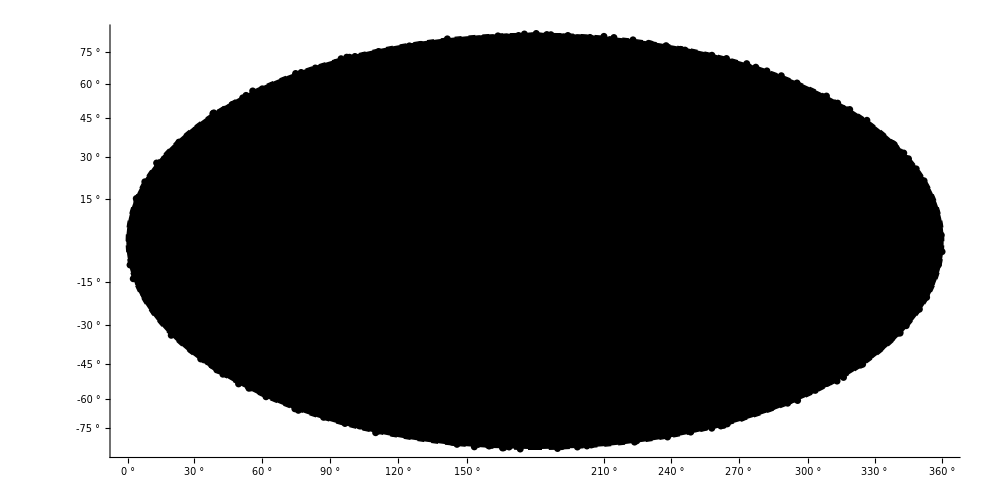

```mathematica
(* Use the Geographics command in order to map the AL *)
geoplotcolreal=GeoGraphics[{Black,Thick,mycircle[bdegalreal[posmaxreal[[1,1]]],ldegalrealrearr[posmaxreal[[1,1]]],errb,errl],AbsolutePointSize@5,Point[GeoPosition@datagalcolreal,VertexColors->(colreal)],Black,Thick,mycircle[bdegalreal[posminreal[[1,1]]],ldegalrealrearr[posminreal[[1,1]]],errb,errl]},GeoRange->{{-90,90},{0,360}},GeoGridLinesStyle->Directive[Black,Dashed],GeoProjection->"Mollweide",GeoGridLines->{Automatic,{0,30,60,90,120,150,180,210,240,270,300,330,360}},GeoBackground->White,Axes->True,ImagePadding->25,ImageSize->1000,Ticks->{tickslgal,ticksbdeg},Background->White,AxesStyle->Black,TicksStyle->Directive[Black,FontSize->19]];
(* Legend for the Geographics projection*)
barlegreal=BarLegend[{"Rainbow",{minvalreal,maxvalreal}},LegendLayout->"Row",LegendMarkerSize->500,LegendFunction->"Frame",LegendMargins->10,LegendLabel->"Δℳ /ℳ̄","Ticks"->{{minvalreal+0.00001,"-0.0018"},{maxvalreal-0.00001,"0.0018"}},BaseStyle->{FontFamily->"Times",18}];
(* Figure 6 - Combine the Geographics plot with the legend *)
alfig=Legended[geoplotcolreal,Placed[barlegreal,Bottom]]
```

```mathematica
Export[NotebookDirectory[]<>"alfig.pdf",alfig,ImageResolution->1000];
```

#### Isotropic Simulated Dataset Analysis and Mapping of the Real Data - Figure 7

```mathematica
(* Implementation of the HC method for ℳ constructing isotropic simulated data. We construct 30 isotropic simulated "Pantheon" datasets (lmax) consisting of 3000 directions (rnmax2) and identify the corresponding extrema of AL. This cell takes some time to be completed. Instead you can use the following lists to run the progrm without going through the (time-consuming) data acquisition process *)

(* Direction of the points*)
v2[i_]:={Sqrt[1-Cos[theta[[i]]]^2]Cos[phi[[i]]],Sqrt[1-Cos[theta[[i]]]^2] Sin[phi[[i]]],Cos[theta[[i]]]}
(* Define the needed quantities for the Do loop *)
rnmax2=3000;lmax=30;dirmaxtab={};xmaxtab={};ymaxtab={};zmaxtab={};
Do[ dMcalmaxis[l]=0;
(* Generate the isotropic simulated datasets and create an appropriate table *)
randdatishc[j_]:={zcmb[[j]],zhel[[j]],RandomReal[NormalDistribution[5 Log10[(1+data[[j,3]])/(1+data[[j,2]])DL[data[[j,2]],ombf2]]+Mbf2,smb[[j]]]],smb[[j]]} ;
randdatabishc=Table[randdatishc[j],{j,1,Length[data]}];
Do[
Clear[vdiris];
(* Generate a random direction where phir=ϕ and csr=cosθ *)
phiris=Random[Real,{0,2Pi}];csris=Random[Real,{-1,1}];
vdiris[l,rn]={Cos[phiris]Sqrt[1-csris^2],Sin[phiris]Sqrt[1-csris^2] ,csris};
(* Fill in the "up" and "down" tables with datapoints *)
upis={};
downis={};
Do[If[vdiris[l,rn].v2[k]≥ 0,AppendTo[upis,randdatabishc[[k]]],AppendTo[downis,randdatabishc[[k]]]],{k,1,Length[data]}];
(* Length of each hemisphere *) 
uplis=upis//Length;
downlis=downis//Length;
(* Minimization of χ^2 on "upper" hemisphere with respect to ℳ *)
chi2upis[Mcal_?NumberQ,om_?NumberQ]:=Module[{Δm,InvCovTotal},
Δm=Table[upis[[i,3]]-(5 Log10[upis[[i,2]]/upis[[i,1]] DL[upis[[i,1]],om]]+Mcal),{i,1,uplis}];
InvCovTotal=Inverse[DiagonalMatrix[upis[[All,4]]^2]];
Δm.InvCovTotal.Δm];
(* Best fit values of ℳ on the "upper" hemisphere *)
chiminupis=FindMinimum[chi2upis[Mcal,ombf2],{Mcal,23,23.1}];
Mcalupis[l,rn]=chiminupis[[2,1,2]];
(* Minimization of χ^2 on "lower" hemisphere with respect to ℳ *)
chi2downis[Mcal_?NumberQ,om_?NumberQ]:=Module[{Δm,InvCovTotal},
Δm=Table[downis[[i,3]]-(5 Log10[downis[[i,2]]/downis[[i,1]] DL[downis[[i,1]],om]]+Mcal),{i,1,downlis}];
InvCovTotal=Inverse[DiagonalMatrix[downis[[All,4]]^2]];
Δm.InvCovTotal.Δm];
(* Best fit values of ℳ on the "lower" hemisphere *)
chimindownis=FindMinimum[chi2downis[Mcal,ombf2],{Mcal,23,23.1}];
Mcaldownis[l,rn]=chimindownis[[2,1,2]];
(* Construct the quantified AL for ℳ as (Δℳ/(ℳ̄))≡2 (Subscript[ℳ, up]-Subscript[ℳ, down])/(Subscript[ℳ, up]+Subscript[ℳ, down]) *)
alMcalis[l,rn]=2(Mcalupis[l,rn]-Mcaldownis[l,rn])/(Mcalupis[l,rn]+Mcaldownis[l,rn]);
(* Identify the value of the maximum difference (Δℳ/(ℳ̄))_max^Pan and its corresponiding direction (xc,yc,zc)*)
If[Abs[alMcalis[l,rn]]>Abs[dMcalmaxis[l]],{dMcalmaxis[l]=alMcalis[l,rn],Mcalupmaxis=Mcalupis[l,rn],Mcaldownmaxis=Mcaldownis[l,rn],xcis[l]=vdiris[l,rn][[1]],ycis[l]=vdiris[l,rn][[2]],zcis[l]=vdiris[l,rn][[3]]}];
(* Print the results as the calculation continues *)
If[Mod[l,6]==0,
If[Mod[rn,rnmax2]==0,Print["Finished step ",rn," of ",rnmax2," of run:", l," //  ℳ_up=", Mcalupis[l,rn], ", ℳ_down=", Mcaldownis[l,rn],", Δℳ/(ℳ̄)=",alMcalis[l,rn], " and the direction is (x,y,z)=(",vdiris[l,rn][[1]],",",vdiris[l,rn][[2]],",",vdiris[l,rn][[3]],"),  ℳ_max^up=", Mcalupmaxis,", ℳ_max^down=", Mcaldownmaxis, "  (Δℳ/(ℳ̄))_max^(Pan.)=", dMcalmaxis[l]," and the direction is (x_max,y_max,z_max)=(",xcis[l],",",ycis[l],",",zcis[l],")"]]],{rn,1,rnmax2}];

(* Append the results in lists *)
AppendTo[dirmaxtab,{dMcalmaxis[l],Mcalupmaxis,Mcaldownmaxis,xcis[l],ycis[l],zcis[l]}];
AppendTo[xmaxtab,xcis[l]];
AppendTo[ymaxtab,ycis[l]];
AppendTo[zmaxtab,zcis[l]],{l,1,lmax}];
```

Finished step 3000 of 3000 of run:6 //  ℳ_up=23.7886, ℳ_down=23.8297, Δℳ/(ℳ̄)=-0.00172841 and the direction is (x,y,z)=(0.907744,0.162794,0.38665),  ℳ_max^up=23.7942, ℳ_max^down=23.8451  (Δℳ/(ℳ̄))_max^(Pan.)=-0.00213506 and the direction is (x_max,y_max,z_max)=(0.813117,0.0189193,0.581793)

Finished step 3000 of 3000 of run:12 //  ℳ_up=23.7836, ℳ_down=23.8184, Δℳ/(ℳ̄)=-0.00146174 and the direction is (x,y,z)=(0.905053,0.000262056,0.425299),  ℳ_max^up=23.7863, ℳ_max^down=23.8403  (Δℳ/(ℳ̄))_max^(Pan.)=-0.00226888 and the direction is (x_max,y_max,z_max)=(0.743787,0.00273544,0.668411)

Finished step 3000 of 3000 of run:18 //  ℳ_up=23.7982, ℳ_down=23.82, Δℳ/(ℳ̄)=-0.000917822 and the direction is (x,y,z)=(0.491623,-0.267781,-0.828613),  ℳ_max^up=23.7952, ℳ_max^down=23.8287  (Δℳ/(ℳ̄))_max^(Pan.)=-0.00140719 and the direction is (x_max,y_max,z_max)=(0.897253,-0.440784,0.0254112)

Finished step 3000 of 3000 of run:24 //  ℳ_up=23.7993, ℳ_down=23.8249, Δℳ/(ℳ̄)=-0.00107302 and the direction is (x,y,z)=(0.612712,-0.788203,0.0576131),  ℳ_max^up=23.8013, ℳ_max^down=23.8325  (Δℳ/(ℳ̄))_max^(Pan.)=-0.00131174 and the direction is (x_max,y_max,z_max)=(0.828043,-0.186188,0.528846)

Finished step 3000 of 3000 of run:30 //  ℳ_up=23.7958, ℳ_down=23.8229, Δℳ/(ℳ̄)=-0.00113745 and the direction is (x,y,z)=(0.621892,0.511084,0.593333),  ℳ_max^up=23.8398, ℳ_max^down=23.796  (Δℳ/(ℳ̄))_max^(Pan.)=0.00183583 and the direction is (x_max,y_max,z_max)=(-0.696451,-0.259804,-0.668923)

```mathematica
(* These are the asymmetries obtained from the 30x3000 isotropic simulated datasets. The format of the list is {(Δℳ/(ℳ̄))_max^Pan,Subscript[ℳ, max]^up,Subscript[ℳ, max]^down,Subscript[x, max],Subscript[y, max],Subscript[z, max]}. Use it if you want to use the stored values in order to save time. If you run the do loop you can skip this cell *)
dirmaxtab
```

{{-0.00204739,23.7807,23.8295,0.828593,-0.558963,-0.0315133},{0.00160285,23.834,23.7959,-0.528537,0.36772,-0.765134},{-0.00118881,23.7997,23.828,0.707184,-0.146949,0.69159},{-0.00138834,23.7994,23.8324,0.910771,-0.409869,0.0500336},{0.00275755,23.8457,23.7801,-0.830631,0.31757,-0.457386},{-0.00213506,23.7942,23.8451,0.813117,0.0189193,0.581793},{-0.00186628,23.7863,23.8307,0.853015,-0.352192,0.385132},{0.00240818,23.8383,23.781,-0.72731,0.0304172,-0.685634},{-0.00163291,23.7887,23.8276,0.805518,-0.592108,-0.02342},{-0.00155742,23.7906,23.8277,0.724215,0.611343,-0.319018},{0.00263565,23.8574,23.7946,-0.726218,-0.13866,-0.673336},{-0.00226888,23.7863,23.8403,0.743787,0.00273544,0.668411},{0.0015874,23.8275,23.7897,-0.854493,0.237924,-0.461772},{0.00157554,23.8277,23.7901,-0.702341,0.0293935,-0.711233},{0.00185167,23.8426,23.7985,-0.714166,0.0601531,-0.697387},{0.00167778,23.8255,23.7855,-0.772193,0.631456,0.0705786},{0.00220569,23.8399,23.7874,-0.740567,0.0845363,-0.666644},{-0.00140719,23.7952,23.8287,0.897253,-0.440784,0.0254112},{-0.0021596,23.794,23.8454,0.734465,-0.0843545,0.673384},{0.00171471,23.8242,23.7834,-0.375825,-0.905542,0.19685},{0.0018777,23.8376,23.7929,-0.732664,0.0718727,-0.676784},{0.00138636,23.8322,23.7992,-0.69553,-0.224782,-0.68243},{-0.00224852,23.7795,23.833,0.784635,-0.563177,0.259188},{-0.00131174,23.8013,23.8325,0.828043,-0.186188,0.528846},{0.00224796,23.8361,23.7826,-0.844811,-0.44354,-0.299276},{-0.00204855,23.7959,23.8447,0.70572,-0.043402,0.70716},{0.00171877,23.8358,23.7948,-0.824244,-0.0683918,-0.56209},{-0.00164303,23.7929,23.832,0.754765,-0.0516492,0.653959},{0.00199785,23.8463,23.7987,-0.740483,0.056048,-0.669734},{0.00183583,23.8398,23.796,-0.696451,-0.259804,-0.668923}}

```mathematica
dirmaxtab1={{-0.0020473924035533195,23.780727867739518,23.82946624261614,0.8285933871831007,-0.558963248803865,-0.031513254402940394},{0.0016028515999356814,23.834035644847976,23.795863814571323,-0.528536826402505,0.36772003523305363,-0.765134497212464},{-0.0011888063773736043,23.799660761626107,23.827970777682673,0.7071843543954383,-0.14694876483374839,0.6915897262193409},{-0.0013883421002172098,23.79937657883703,23.832441207808568,0.9107710408924082,-0.4098691847530533,0.05003361331771772},{0.0027575490315053987,23.84574551973214,23.78008024487622,-0.8306306961246172,0.31757007277914484,-0.4573859371806075},{-0.0021350604388838275,23.794209850789713,23.84506621762508,0.8131169692765262,0.018919268129269404,0.581792794358962},{-0.0018662806894331665,23.786267318001354,23.830700631888472,0.8530148133764843,-0.35219165231070393,0.38513214381941396},{0.002408181488166514,23.83831739607135,23.780979441509466,-0.7273104266774897,0.030417184832771834,-0.6856342597282147},{-0.0016329122035664049,23.788731413614336,23.827608064525844,0.8055182944577466,-0.5921079137368751,-0.023419986849876562},{-0.0015574230414720242,23.790635701472794,23.827716661055963,0.7242146280685245,0.6113432981510102,-0.3190180939968983},{0.0026356512000987663,23.8574189313006,23.794621852061688,-0.7262177471955571,-0.13866009199578527,-0.6733358467703396},{-0.002268880744947265,23.786318370863412,23.84034798398268,0.7437868955662194,0.002735444510475122,0.6684112292049678},{0.0015873966300829845,23.827512093940847,23.78971837834805,-0.8544933117929354,0.2379244085682938,-0.4617717573743212},{0.0015755445848181213,23.82765273897119,23.79014076062655,-0.7023412437461386,0.02939349365752677,-0.7112332949628637},{0.0018516676340774685,23.84262469986306,23.79851691986918,-0.7141655463618006,0.0601531017139703,-0.6973873935940766},{0.001677783724600536,23.825474288553888,23.785533801311388,-0.7721927030216329,0.6314563303682323,0.07057855366915744},{0.0022056854975132222,23.83991084307043,23.787385424738595,-0.7405665011824205,0.08453625183772741,-0.6666444925533072},{-0.001407186729076167,23.795177807677977,23.828685641994834,0.8972533703871889,-0.44078414180419856,0.025411211359672947},{-0.0021595970500636113,23.794003765215,23.84544477147825,0.7344646188513894,-0.08435454622786213,0.6733840168775724},{0.0017147110123235747,23.82416814979844,23.783351580622856,-0.37582511352517745,-0.9055415663414887,0.19685008425599082},{0.0018777023932157319,23.83757254869091,23.792854665106294,-0.732664407314786,0.0718726975193583,-0.6767844424965486},{0.0013863568806819963,23.832240427307468,23.799223323553488,-0.6955302151749241,-0.22478235046145684,-0.6824299339124469},{-0.002248520405650021,23.779508351821995,23.833037241988308,0.7846354937754737,-0.5631772353302322,0.25918823953550607},{-0.0013117351258605918,23.801265654030814,23.83250710048049,0.8280432604297835,-0.1861876141863577,0.5288464154935777},{0.0022479626644675912,23.836095590460978,23.782573095791804,-0.8448111077192191,-0.4435400949255575,-0.29927642150302014},{-0.0020485490454877652,23.79587010549853,23.84466709400181,0.7057198240888576,-0.043401981693559945,0.7071603763454679},{0.0017187692574459597,23.835770057983485,23.79483704638125,-0.8242436929184828,-0.0683918006324941,-0.5620897582151334},{-0.001643031751454197,23.79290640946074,23.832031051665567,0.7547648526103381,-0.051649185498671854,0.6539590039913958},{0.001997852906812421,23.846254506957735,23.798660740746506,-0.7404828836499694,0.05604801998628845,-0.6697340654894617},{0.0018358315781852816,23.839751431729677,23.796025799683264,-0.6964513069108521,-0.2598035180347351,-0.6689227975775239}};
lmax=Length[dirmaxtab1];
xequat1=Table[dirmaxtab1[[i,4]],{i,1,lmax}];
yequat1=Table[dirmaxtab1[[i,5]],{i,1,lmax}];
zequat1=Table[dirmaxtab1[[i,6]],{i,1,lmax}];
deltammax1=Table[dirmaxtab1[[i,1]],{i,1,lmax}];
```

```mathematica
(* double the axis by using also the opposite directions which should have -Δℳ/(ℳ̄) by construction *)
Do[
xequatdoub[i]=-dirmaxtab1[[i,4]];
yequatdoub[i]=-dirmaxtab1[[i,5]];
zequatdoub[i]=-dirmaxtab1[[i,6]];
deltammaxdoub[i]=-dirmaxtab1[[i,1]],{i,1,lmax}];
(* Table the opposite directions data *)
deltammaxdoub1=Table[deltammaxdoub[i],{i,1,lmax}];
xequatdoub1=Table[xequatdoub[i],{i,1,lmax}];
yequatdoub1=Table[yequatdoub[i],{i,1,lmax}];
zequatdoub1=Table[zequatdoub[i],{i,1,lmax}];
(* Join the lists *)
deltammax=Join[deltammax1,deltammaxdoub1];
xequat=Join[xequat1,xequatdoub1];
yequat=Join[yequat1,yequatdoub1];
zequat=Join[zequat1,zequatdoub1];
```

```mathematica
(* Find equatorial coordinates in degrees for each datapoint *)
ragal=Table[ArcTan[yequat[[i]]/xequat[[i]]]/Degree ,{i,1,2lmax}];
decgal=Table[90-ArcCos[zequat[[i]]/Sqrt[xequat[[i]]^2+yequat[[i]]^2+zequat[[i]]^2]]/Degree,{i,1,2lmax}];
Do[
If[yequat[[i]]>0 && xequat[[i]]>0,ragali=ragal[[i]]];
If[yequat[[i]]<0 && xequat[[i]]>0,ragali=ragal[[i]]+360];
If[yequat[[i]]>0 && xequat[[i]]<0,ragali=ragal[[i]]+180];
If[yequat[[i]]<0 && xequat[[i]]<0,ragali=ragal[[i]]+180];
If[yequat[[i]]==0 && xequat[[i]]>0,ragali=0];
If[yequat[[i]]==0 && xequat[[i]]<0,ragali=180];
If[yequat[[i]]>0 && xequat[[i]]==0,ragali=90];
If[yequat[[i]]<0 && xequat[[i]]==0,ragali=270];
adegal[i]=ragali;
ddegal[i]=decgal[[i]],{i,1,2lmax}]
(* Do loop to convert the equatorial coordinates to the galactic ones as it is described in "Practical Astronomy with your Calculator or Spreadsheet" page 57 *)
Do[
snbgal=Cos[ddegal[i] Degree]Cos[27.4 Degree]Cos[adegal[i] Degree - 192.25 Degree]+Sin[ddegal[i] Degree]Sin[27.4 Degree];
bdegal[i]=ArcSin[snbgal]/Degree;
y=Sin[ddegal[i] Degree]-Sin[bdegal[i] Degree]Sin[27.4 Degree];
x=Cos[ddegal[i] Degree] Sin[adegal[i] Degree-192.25 Degree]Cos[27.4 Degree];
ldegtal=ArcTan[y/x]/Degree;
If[y>0 && x>0,ldegtal1=ldegtal];
If[y<0 && x>0,ldegtal1=ldegtal+360];
If[y>0 && x<0,ldegtal1=ldegtal+180];
If[y<0 && x<0,ldegtal1=ldegtal+180];
If[y==0 && x>0,ldegtal1=0];
If[y==0 && x<0,ldegtal1=180];
If[y>0 && x==0,ldegtal1=90];
If[y<0 && x==0,ldegtal1=270];
ldegal[i]=ldegtal1+33,{i,1,2lmax}]
```

```mathematica
(* Construct table to map the prefered anisotropies for Δℳ/(ℳ̄) *)
Do[ldegalarr[i]=If[ldegal[i]>360,ldegal[i]-360,ldegal[i]],{i,1,2lmax}];
tabdata=Table[{deltammax[[i]],ldegalarr[i],bdegal[i]},{i,1,2lmax}];
```

```mathematica
(* Select the simulated datasets that have larger/lower magnitudes of AL than the corresponding magnitude of the real Pantheon data *)
almaxiso=Select[Table[{tabdata[[i,1]],tabdata[[i,2]],tabdata[[i,3]]},{i,1,2lmax}],Abs[#1[[1]]]>Abs[maxvalreal]&];
alminiso=Select[Table[{tabdata[[i,1]],tabdata[[i,2]],tabdata[[i,3]]},{i,1,2lmax}],Abs[#1[[1]]]<Abs[maxvalreal]&];
```

```mathematica
(* Select the (b,l) coordinates of the simulated datasets that have larger/lower magnitudes of AL than the corresponding magnitude of the real Pantheon data *)
datagalhcrand1=Table[{almaxiso[[i,3]],almaxiso[[i,2]]},{i,1,Length[almaxiso]}];
datagalhcrand2=Table[{alminiso[[i,3]],alminiso[[i,2]]},{i,1,Length[alminiso]}];
datagalhcrandtot=Join[datagalhcrand1,datagalhcrand2];
(* Red/Blue is the color selected for the simulated datasets that have larger/lower magnitudes of AL than the corresponding magnitude of the real Pantheon data *)
col1=Table[Red,{i,1,Length[almaxiso]}];
col2=Table[Blue,{i,1,Length[alminiso]}];
col=Join[col1,col2];
```

```mathematica
(* Left panel of Fig. 7 *)
hcmethdrandfig=GeoGraphics[{Green,AbsolutePointSize@15,Point[{87 Degree, 33Degree}],Green,AbsolutePointSize@15,Point[{-60 Degree, -33Degree}],AbsolutePointSize@5,Point[GeoPosition@datagalhcrandtot,VertexColors->(col)]},GeoRange->{{-90,90},{0,360}},GeoGridLinesStyle->Directive[Black,Dashed],GeoProjection->"Mollweide",GeoGridLines->{{-90,90,-75,75,-60,60,-45,45,-30,30,-15,15},{0,30,60,90,120,150,180,210,240,270,300,330,360}},GeoBackground->White,Axes->True,ImagePadding->25,Ticks->{tickslgal,ticksbdeg},Background->White,AxesStyle->Black,TicksStyle->Directive[Black,FontSize->19],ImageSize->700];
```

```mathematica
(* Find the number of simulated datasets that have larger/lower magnitudes of AL than the corresponding magnitude of the real Pantheon data *)
Length[almaxiso]
Length[alminiso]
```

32

28

```mathematica
(* Do loop to convert the equatorial coordinates to the galactic ones as it is described in "Practical Astronomy with your Calculator or Spreadsheet" page 57 *)
Do[
snb=Cos[dectot[[i]] Degree]Cos[27.4 Degree]Cos[ratot[[i]] Degree - 192.25 Degree]+Sin[dectot[[i]]  Degree]Sin[27.4 Degree];
bdegreal[i]=ArcSin[snb]/Degree;
y=Sin[dectot[[i]]  Degree]-Sin[bdegreal[i] Degree]Sin[27.4 Degree];
x=Cos[dectot[[i]]  Degree] Sin[ratot[[i]] Degree-192.25 Degree]Cos[27.4 Degree];
ldegt=ArcTan[y/x]/Degree;
If[y>0 && x>0,ldeg1=ldegt];
If[y<0 && x>0,ldeg1=ldegt+360];
If[y>0 && x<0,ldeg1=ldegt+180];
If[y<0 && x<0,ldeg1=ldegt+180];
If[y==0 && x>0,ldeg1=0];
If[y==0 && x<0,ldeg1=180];
If[y>0 && x==0,ldeg1=90];
If[y<0 && x==0,ldeg1=270];
ldeg[i]=ldeg1+33,{i,1,Length[data]}]
```

```mathematica
(* Construct table to map the pantheon data *)
Do[ldegreal[i]=If[ldeg[i]>360,ldeg[i]-360,ldeg[i]],{i,1,Length[data]}];
datagal=Table[{bdegreal[i],ldegreal[i]},{i,1,Length[data]}];
(* Right panel of Fig. 7 - The Distribution of the pantheon data in the galactic coordinates. Same as Fig. 1 of https://arxiv.org/pdf/1806.02773.pdf *)
distribfig=GeoGraphics[{AbsolutePointSize@5,Blue,Point[GeoPosition@datagal]},GeoRange->{{-90,90},{0,360}},GeoGridLinesStyle->Directive[Black,Dashed],GeoProjection->"Mollweide",GeoGridLines->{{-90,90,-75,75,-60,60,-45,45,-30,30,-15,15},{0,30,60,90,120,150,180,210,240,270,300,330,360}},ImageSize->1000,GeoBackground->White,Axes->True,ImagePadding->25,Ticks->{tickslgal,ticksbdeg},Background->White,AxesStyle->Black,TicksStyle->Directive[Black,FontSize->19]];
```

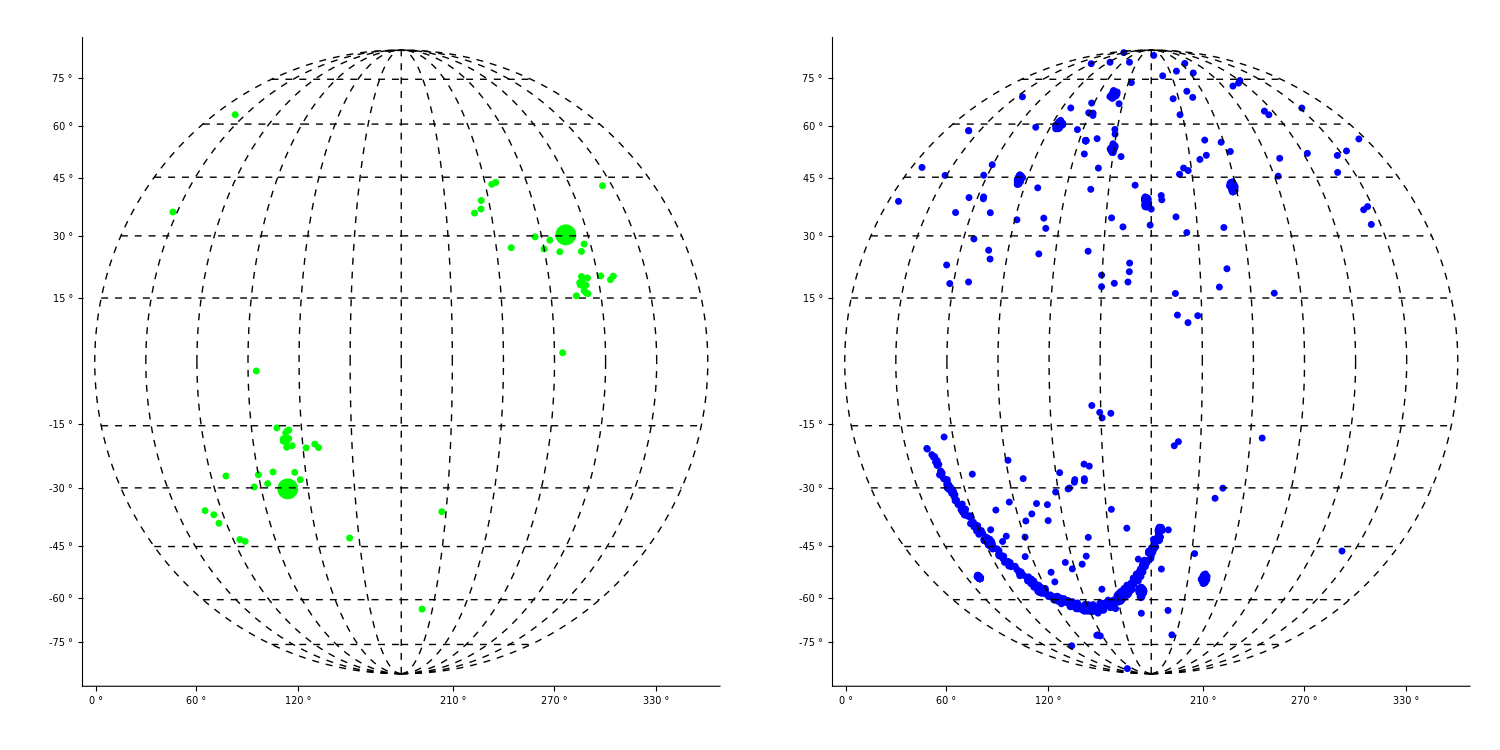

```mathematica
(* Combine the two plots - Figure 7 *)
distribfigreal=GraphicsGrid[{{hcmethdrandfig,distribfig}},Spacings->0,ImageSize->1500,AspectRatio->Full]
```

```mathematica
Export[NotebookDirectory[]<>"distribfigreal.pdf",distribfigreal,ImageResolution->1000];
```

#### More Isotropic Subset of the Full Dataset Analysis - Figure 8

```mathematica
(* Create the isotropic subset *)
listred=Table[{zcmb[[i]],zhel[[i]],mb[[i]],smb[[i]],bdegreal[i],ldegreal[i],theta[[i]],phi[[i]]},{i,1,Length[data]}];
(* Number of data selected in each quadrisphere *)
subsampnum=100;
```

```mathematica
(* Select 100 random data from the upper left quadrisphere where 0<b<90 and 0<l<180*)
upleftlist=Select[listred,0<#1[[5]]<90 &&0<#1[[6]]<180 &];
upleftdatdel=RandomSample[upleftlist,subsampnum];
lengthupleft=Length[upleftdatdel];
(* Select 100 random data from the upper right quadrisphere where 0<b<90 and 180<l<3600*)
uprightlist=Select[listred,0<#1[[5]]<90 &&180<#1[[6]]<360 &];
uprightdatdel=RandomSample[uprightlist,subsampnum];
lengthuright=Length[uprightdatdel];
(* Select 100 random data from the lower left quadrisphere where -90<b<0 and 0<l<180*)
downleftlist=Select[listred,-90<#1[[5]]<0 &&0<#1[[6]]<180 &];
downleftdatdel=RandomSample[downleftlist,subsampnum];
lengthdownleft=Length[downleftdatdel];
(* Select all the points from the lower right quadrisphere where -90<b<0 and 180<l<360*)
downrightlist=Select[listred,-90<#1[[5]]<0 &&180<#1[[6]]<360 &];
downrightdatdel=RandomSample[downrightlist,All];
lengthdownright=Length[downrightdatdel];
redtotlist=Join[upleftdatdel,uprightdatdel,downleftdatdel,downrightdatdel];
```

```mathematica
(* Right Panel of Fig. 8 - Map the isotropic subset in the sky area *)
datagaltotred=Table[{redtotlist[[i,5]],redtotlist[[i,6]]},{i,1,Length[redtotlist]}];
distribfigred=GeoGraphics[{AbsolutePointSize@5,Blue,Point[GeoPosition@datagaltotred]},GeoRange->{{-90,90},{0,360}},GeoGridLinesStyle->Directive[Black,Dashed],GeoProjection->"Mollweide",GeoGridLines->{{-90,90,-75,75,-60,60,-45,45,-30,30,-15,15},{0,30,60,90,120,150,180,210,240,270,300,330,360}},ImageSize->1000,GeoBackground->White,Axes->True,ImagePadding->25,Ticks->{tickslgal,ticksbdeg},Background->White,AxesStyle->Black,TicksStyle->Directive[Black,FontSize->19]];
```

```mathematica
(* Create the physical quantities for the minimization process *)
zcmb2=Table[redtotlist[[i,1]],{i,1,Length[redtotlist]}];
zhel2=Table[redtotlist[[i,2]],{i,1,Length[redtotlist]}];
mb2=Table[redtotlist[[i,3]],{i,1,Length[redtotlist]}];
smb2=Table[redtotlist[[i,4]],{i,1,Length[redtotlist]}];
theta2=Table[redtotlist[[i,7]],{i,1,Length[redtotlist]}];
phi2=Table[redtotlist[[i,8]],{i,1,Length[redtotlist]}];
```

```mathematica
(* χ^2 formula for the isotropic dataset *)
chi2Panthstatred[Mcal_?NumberQ,om_?NumberQ]:=Module[{Δm,InvCovTotal2},
Δm=Table[redtotlist[[i,3]]-(5 Log10[(1+redtotlist[[i,2]])/(1+redtotlist[[i,1]])DL[redtotlist[[i,1]],om]]+Mcal),{i,1,Length[redtotlist]}];
InvCovTotal2=Inverse[DiagonalMatrix[redtotlist[[All,4]][[1;;-1]]^2]];
Δm.InvCovTotal2.Δm]
(* Minimization of χ^2 with respect to ℳ and Subscript[Ω, 0m] for the isotropic subset *)
minred=FindMinimum[chi2Panthstatred[ℳ,om],{ℳ,23,23.1},{om,0.28,0.29}]
```

{376.568,{ℳ→23.7923,om→0.263376}}

```mathematica
(* Rewrite the data of the homogeneous subset in easier form *)
rred[i_]:={zcmb2[[i]],zhel2[[i]],mb2[[i]],smb2[[i]]} 
(* The direction of each datapoint *)
vred[i_]:={Sin[theta2[[i]]] Cos[phi2[[i]]],Sin[theta2[[i]]] Sin[phi2[[i]]],Cos[theta2[[i]]]} 

(* Implementation of the HC Method for ℳ. We use 1500 random directions to split the data into the upper and lower hemishperes. Then we find the best fit values of ℳ as well as the 1σ error for each direction setting Subscript[Ω, 0m]=0.285. Moreover we find the direction corresponding to the maximum difference (Δℳ/(ℳ̄)) - This cell takes some time to be completed. Therefore you can use the following lists to run the progrm without going through the (time-consuming) data acquisition process *)
rnmaxred=1500; dMcalmaxred=0;
Do[
(* Generate a random direction where phir=ϕ and csr=cosθ *)
phirred=Random[Real,{0,2Pi}];csrred=Random[Real,{-1,1}];
vdirred[rn]={Cos[phirred]Sqrt[1-csrred^2],Sin[phirred]Sqrt[1-csrred^2],csrred};
(* Fill in the "up" and "down" tables with datapoints *)
upred={};
downred={};
Do[If[vdirred[rn].vred[i]≥ 0,AppendTo[upred,rred[i]],AppendTo[downred,rred[i]]],{i,1,Length[redtotlist]}];
(* Length of each hemisphere *)
uplred=upred//Length;
downlred=downred//Length;
(* Minimization of χ^2 on "upper" hemisphere with respect to ℳ *)
chi2upred[Mcal_?NumberQ,om_?NumberQ]:=Module[{Δm,InvCovTotal},
Δm=Table[upred[[i,3]]-(5 Log10[upred[[i,2]]/upred[[i,1]] DL[upred[[i,1]],om]]+Mcal),{i,1,uplred}];
InvCovTotal=Inverse[DiagonalMatrix[upred[[All,4]]^2]];
Δm.InvCovTotal.Δm];
(* Best fit values of ℳ on the "upper" hemisphere *)
chiminupred=FindMinimum[chi2upred[Mcal,minred[[2,2,2]]],{Mcal,23.,23.1}];
Mcalupred[rn]=chiminupred[[2,1,2]];
(* Minimization of χ^2 on "lower" hemisphere with respect to ℳ *)
chi2downred[Mcal_?NumberQ,om_?NumberQ]:=Module[{Δm,InvCovTotal},
Δm=Table[downred[[i,3]]-(5 Log10[downred[[i,2]]/downred[[i,1]] DL[downred[[i,1]],om]]+Mcal),{i,1,downlred}];
InvCovTotal=Inverse[DiagonalMatrix[downred[[All,4]]^2]];
Δm.InvCovTotal.Δm];
(* Best fit values of ℳ on the "lower" hemisphere *)
chimindownred=FindMinimum[chi2downred[Mcal,minred[[2,2,2]]],{Mcal,23.,23.1}];
Mcaldownred[rn]=chimindownred[[2,1,2]];
(* Construct the quantified Anisotropy Level (AL) for ℳ as (Δℳ/(ℳ̄))≡2 (Subscript[ℳ, up]-Subscript[ℳ, down])/(Subscript[ℳ, up]+Subscript[ℳ, down]) *)
alMcalred[rn]=2(Mcalupred[rn]-Mcaldownred[rn])/(Mcalupred[rn]+Mcaldownred[rn]);
(* Identify the value of the maximum difference (Δℳ/(ℳ̄))_max^Pan and its corresponiding direction (xc,yc,zc)*)
If[Abs[alMcalred[rn]]>Abs[dMcalmaxred],{dMcalmaxred=alMcalred[rn],xcred=vdirred[rn][[1]],ycred=vdirred[rn][[2]],zcred=vdirred[rn][[3]]}];
(* Print the results as the calculation continues *)
If[Mod[rn,500]==0,Print["Finished step ",rn," of ",rnmaxred," //  ℳ_up=", Mcalupred[rn], ", ℳ_down=", Mcaldownred[rn],", Δℳ/(ℳ̄)=",alMcalred[rn], " and the direction is (x,y,z)=(",vdirred[rn][[1]],",",vdirred[rn][[2]],",",vdirred[rn][[3]],"). The maximum AL is:(Δℳ/(ℳ̄))_max^(Pan.)=", dMcalmaxred," and the direction is (x_max,y_max,z_max)=(",xcred,",",ycred,",",zcred,")"]],{rn,1,rnmaxred}]
```

Finished step 500 of 1500 //  ℳ_up=23.8085, ℳ_down=23.7825, Δℳ/(ℳ̄)=0.00109078 and the direction is (x,y,z)=(0.0864748,0.46241,0.882439). The maximum AL is:(Δℳ/(ℳ̄))_max^(Pan.)=0.00235753 and the direction is (x_max,y_max,z_max)=(-0.82027,0.142534,-0.553932)

Finished step 1000 of 1500 //  ℳ_up=23.8272, ℳ_down=23.7958, Δℳ/(ℳ̄)=0.00131923 and the direction is (x,y,z)=(-0.505662,-0.379012,-0.77502). The maximum AL is:(Δℳ/(ℳ̄))_max^(Pan.)=0.00235753 and the direction is (x_max,y_max,z_max)=(-0.82027,0.142534,-0.553932)

Finished step 1500 of 1500 //  ℳ_up=23.7911, ℳ_down=23.8168, Δℳ/(ℳ̄)=-0.00108009 and the direction is (x,y,z)=(0.495489,0.833396,-0.244829). The maximum AL is:(Δℳ/(ℳ̄))_max^(Pan.)=0.00241446 and the direction is (x_max,y_max,z_max)=(-0.800718,0.110919,-0.588683)

```mathematica
(* Append the data to a table for convenience*)dirtabMrealred=Table[{alMcalred[i],vdirred[i][[1]],vdirred[i][[2]],vdirred[i][[3]]},{i,1,rnmaxred}]
```

{{0.000679715,-0.520969,0.654831,-0.547529},{-0.00140762,0.512888,0.296424,0.805654},{-0.00166851,0.220525,-0.12098,-0.967849},{0.00124867,-0.569967,-0.582353,-0.579657},{0.00141255,-0.605394,-0.215475,-0.766204},{-0.00025689,0.235349,0.941946,-0.239474},{-0.000511074,0.517642,-0.220743,0.826631},{-0.00167673,0.859856,0.0371422,-0.509183},{-0.00169021,0.623365,0.593886,-0.508641},{0.0019288,-0.371471,0.144155,0.917185},{0.0000322381,-0.178465,-0.838383,-0.515038},{-0.00112724,0.676803,-0.62681,-0.386066},{-0.000345392,-0.160747,0.195155,-0.96751},{-0.000501438,0.289738,-0.937707,-0.19172},{-0.000908544,-0.0242034,0.00966733,-0.99966},{-0.00121656,0.376679,0.695335,-0.612063},{-0.000187636,0.481977,-0.424393,0.766544},{-0.00152084,0.754167,-0.193877,0.62741},{-0.000422635,0.324206,-0.107029,0.939912},{-0.00190115,0.947893,-0.28782,0.136594},{-0.00042121,0.421216,-0.788275,0.448553},{0.00167673,-0.972862,-0.0734747,0.219409},{-0.0016059,0.764022,0.644162,-0.0364085},{0.00118983,-0.625236,-0.673372,-0.394525},{0.0000508825,0.0114384,-0.997558,-0.0688988},{-0.000318737,0.301427,-0.523089,0.797195},{0.000640158,-0.380635,0.92213,-0.0692385},{0.00168774,-0.478124,-0.777113,0.409258},{0.00154226,-0.885036,0.435597,0.164218},{0.000715689,-0.18421,-0.595635,0.781848},{0.00163946,-0.965186,0.134549,0.224305},{0.000427754,-0.00480816,-0.93495,-0.354746},{0.00156206,-0.371395,-0.510171,0.775752},{-0.000437059,0.0727789,0.901864,0.425846},{0.00193498,-0.953802,-0.234473,-0.187839},{0.00121735,-0.7724,-0.609206,-0.179629},{0.000729632,0.107643,-0.460594,0.88106},{-0.0000857009,0.144509,-0.989232,0.0231761},{0.00172092,-0.985705,0.160983,-0.0497019},{-0.00131598,0.60546,0.506481,0.613918},{-0.00141255,0.591336,0.179999,0.78608},{0.00186467,-0.465704,0.301296,0.83207},{0.00118998,-0.815535,-0.377971,-0.438225},{0.00104703,-0.529387,-0.827556,0.186816},{-0.00159242,0.853699,-0.474775,-0.213977},{0.00174489,-0.57288,0.30452,0.76097},{0.00135189,-0.166414,0.154594,0.973862},{-0.000668712,0.401927,-0.913743,-0.0594009},{0.00028393,-0.348966,-0.234978,-0.907198},{-0.000317792,0.383567,0.105883,0.917423},{-0.00117169,0.721173,0.677939,0.142504},{-0.00172965,0.653051,-0.297353,-0.696495},{-0.00122331,0.837608,0.413974,0.356424},{0.0019347,-0.839742,-0.124309,-0.528565},{0.00183637,-0.978382,-0.0244939,-0.205351},{-0.000764963,0.629271,-0.723194,0.284619},{-0.000252981,-0.112914,-0.0665492,-0.991374},{0.00168815,-0.795459,0.305018,0.523649},{-0.000653291,0.0746499,0.250495,-0.965235},{0.00134209,-0.639589,-0.645816,-0.41695},{0.00191138,-0.259232,-0.213321,0.941962},{0.00132094,-0.817446,-0.469017,-0.334373},{0.0017752,-0.977555,0.0645721,-0.200542},{0.00115646,-0.449116,-0.625625,-0.637878},{0.00167012,-0.775775,0.449326,0.443034},{-0.000497012,0.316339,0.326507,0.890687},{-0.00166191,0.79808,-0.489321,-0.351615},{-0.000265622,-0.0781701,0.915809,-0.393932},{0.000509264,-0.437554,0.823876,-0.360241},{-0.000699012,0.434658,-0.896816,0.0824182},{-0.00169021,0.654495,0.644676,-0.395006},{-0.000660027,0.287818,0.816412,-0.500632},{0.00200963,-0.937765,-0.0839584,-0.336968},{0.00172237,-0.418389,-0.360316,0.833741},{-0.000352995,0.498158,0.077967,0.863574},{-0.0021564,0.857108,-0.207225,0.471618},{0.00152365,-0.633603,-0.512615,-0.57946},{-0.000563336,0.413138,-0.70131,0.580931},{0.000715689,-0.212239,-0.598942,0.772155},{0.00176263,-0.901371,-0.432317,-0.0251363},{0.000931218,-0.66984,0.730606,0.132396},{0.00094184,-0.00184708,-0.451151,0.892446},{-0.000538448,0.0315479,0.880713,-0.472598},{0.00167673,-0.868438,-0.302167,0.393078},{0.000985666,-0.0627423,-0.498927,0.86437},{-0.00143921,0.770995,-0.30448,0.559337},{-0.000852062,-0.0110387,-0.0383378,-0.999204},{-0.0019288,0.40562,-0.0567048,-0.912281},{-0.00154041,0.667449,0.466705,0.580256},{-0.00157885,0.54106,0.681172,-0.493212},{0.00154491,-0.479399,0.34227,0.808101},{0.00160831,-0.761634,-0.370096,0.531924},{-0.00167673,0.925424,0.196018,-0.324295},{-0.000524288,0.338841,-0.690112,0.639478},{-0.000912037,0.126872,-0.508445,-0.851697},{-0.00071547,-0.0797193,0.652482,-0.753599},{-0.00182856,0.650887,0.25218,-0.716067},{0.000710068,-0.453422,0.834553,-0.312937},{0.000490269,-0.421934,0.555049,-0.716863},{0.000808467,-0.544659,0.736764,-0.400655},{-0.000288815,-0.037962,0.954085,-0.297119},{-0.000828185,0.109214,0.405733,-0.907443},{-0.00111992,0.609556,-0.785729,-0.105221},{0.00113012,-0.589128,-0.678148,-0.439367},{-0.000967567,0.272292,-0.562149,-0.780926},{-0.000547187,0.387389,-0.918539,-0.0788451},{-0.00185619,0.361651,0.0757742,-0.929229},{0.00186763,-0.909444,-0.259088,-0.325246},{-0.000552486,0.60897,-0.100212,0.786838},{0.00124384,0.0341594,0.152643,0.987691},{0.00169021,-0.627527,-0.593713,0.503701},{-0.000880549,0.603496,-0.696405,0.388346},{0.000719059,-0.64466,0.738065,-0.19918},{0.00154484,-0.534482,-0.791731,0.295789},{0.00181272,-0.422476,-0.0245944,0.90604},{-0.00167673,0.957187,0.116838,-0.264844},{0.000757687,-0.278241,-0.671312,0.686966},{-0.0000901667,0.159211,0.558618,0.814001},{0.00142595,-0.444355,-0.65027,0.616196},{0.00104186,-0.521962,-0.841526,0.139247},{0.000615904,-0.236138,-0.506364,0.829358},{0.00160424,-0.933494,0.324992,0.151556},{-0.00175584,0.686638,0.271644,-0.674342},{0.00182856,-0.560186,-0.322028,0.76321},{0.000632814,-0.284851,-0.802126,0.524838},{-0.00169243,0.760172,-0.372152,-0.53258},{0.00015157,0.305458,0.72373,0.618797},{-0.000748215,0.570867,-0.371349,0.732264},{0.0019288,-0.362885,0.00234316,0.931831},{0.000824405,-0.116669,-0.378394,0.918263},{-0.00134135,0.40748,-0.604653,-0.684365},{-0.00167673,0.943469,0.247048,-0.220984},{-0.00147203,0.442164,0.735241,-0.513723},{0.0016533,-0.646524,-0.433936,0.62746},{-0.00171469,0.431838,0.330086,-0.83938},{-0.000281882,0.501851,0.0348816,0.86425},{0.001321,-0.780572,0.507988,-0.364218},{-0.00115295,0.794432,0.459787,0.39683},{-0.000559208,0.176595,0.984137,0.0169845},{-0.00019279,0.338019,0.666404,0.664566},{0.000443095,-0.169643,-0.98182,0.0851535},{0.00172965,-0.655973,0.112828,0.746303},{-0.000961337,0.70257,-0.673256,-0.230482},{0.00197923,-0.909959,0.413406,-0.0327126},{0.000236148,-0.153983,-0.680107,-0.716759},{-0.000843715,0.494175,-0.800193,0.339827},{0.00083779,-0.368356,-0.307441,-0.877379},{-0.000415301,0.409212,-0.778699,0.475577},{0.000116349,0.256769,0.8349,0.486839},{-0.000954426,-0.0158703,-0.388639,-0.921253},{-0.00173361,0.841726,-0.102188,-0.530146},{0.00164184,-0.737136,-0.336818,-0.58582},{0.000140042,-0.0463937,0.921875,0.384701},{-0.00153359,0.779054,0.531761,-0.332123},{0.00073651,-0.671291,0.63347,-0.384817},{0.00158657,-0.370185,-0.61003,0.70059},{0.00042379,-0.378585,-0.640603,-0.668058},{-0.000723485,0.349734,-0.684881,-0.639238},{-0.00182856,0.576871,0.205055,-0.790679},{-0.00163946,0.993319,-0.0116355,-0.114815},{-0.00125358,0.573657,-0.77065,-0.277518},{-0.000226021,-0.0285454,0.980673,-0.193561},{-0.00139106,0.458064,-0.481261,-0.747372},{-0.00015157,-0.308885,-0.731601,-0.607742},{0.00105611,-0.751444,-0.646443,-0.132073},{0.00172963,-0.579526,-0.373392,0.724381},{-0.000974884,0.0689561,0.660949,-0.747256},{-0.00174721,0.194962,-0.0949018,-0.976209},{0.00184606,-0.354555,-0.162525,0.920802},{-0.00121989,0.597905,0.450447,0.663029},{0.00173361,-0.699969,-0.0619532,0.711481},{-0.0017477,0.77182,0.595769,-0.222156},{0.000994133,-0.524033,-0.851627,-0.0110016},{0.000347173,0.139548,-0.19209,0.971405},{-0.000531992,0.246561,-0.932581,-0.26363},{-0.000917891,0.421248,0.697953,0.579147},{-0.000344845,0.216522,0.446009,0.868443},{0.00184251,-0.466116,-0.228278,0.854766},{-0.00148374,0.740747,-0.268716,0.615699},{0.00160276,-0.342128,-0.438668,0.830975},{0.00135219,-0.512331,0.504614,0.694897},{0.000760649,-0.535655,-0.14408,-0.832054},{0.000338116,0.117489,-0.138163,0.983416},{0.00165281,-0.850007,0.35399,0.390102},{-0.000236333,0.309309,0.950945,-0.00558224},{0.00158643,-0.775189,-0.473049,0.418697},{0.000748215,-0.563387,0.363457,-0.741953},{0.00186467,-0.481925,0.250809,0.83955},{-0.000800949,0.0956022,0.786306,-0.610396},{0.000524252,0.103159,-0.139855,0.984784},{0.000109575,-0.219237,0.949113,-0.226095},{-0.000678143,0.14362,0.513161,-0.846191},{-0.00189428,0.841427,-0.534564,0.0790082},{0.00149662,-0.0855183,-0.144083,0.985863},{-0.00186846,0.950929,0.294272,0.095592},{-0.000434753,0.128575,0.905572,-0.404238},{-0.00133761,0.252735,-0.358103,-0.898826},{0.00120709,-0.625684,-0.759715,0.177065},{0.00186467,-0.498701,0.201082,0.843127},{-0.000204979,0.195393,0.920818,0.337515},{0.00018004,0.231086,0.860765,0.453523},{0.000893917,-0.621335,0.699659,0.352732},{-0.00166191,0.836139,-0.445226,-0.320382},{-0.00113968,0.530273,0.82416,0.198923},{-0.00197141,0.797193,0.0612535,0.600609},{0.00163946,-0.976403,0.0352419,0.21306},{-0.00172965,0.847306,-0.192524,-0.494983},{-0.000327125,-0.0967931,0.918787,-0.382702},{-0.00162968,0.596781,0.537075,-0.596157},{0.0016238,-0.62947,-0.640283,0.440233},{0.000396258,-0.394577,-0.807056,-0.439284},{0.000681012,-0.372189,0.237402,-0.897283},{0.00163177,-0.975882,0.190166,0.107193},{-0.00167673,0.931377,0.264629,-0.250014},{0.00176302,-0.784098,-0.239835,-0.572424},{-0.000729222,0.626123,-0.551634,0.551063},{0.00191103,-0.961144,-0.215083,-0.173034},{0.00113586,-0.579883,0.474864,-0.661997},{0.00147544,-0.663882,-0.315448,-0.678051},{-0.00131998,0.492993,0.487384,0.720705},{0.0019288,-0.379875,0.113034,0.918106},{0.00152332,-0.694393,0.00988706,-0.719528},{0.000262513,0.153886,-0.92119,0.35739},{-0.00193661,0.48414,0.2992,-0.822246},{-0.000224001,-0.231832,0.619716,-0.749804},{-0.00136727,0.869501,0.246944,0.427769},{0.000894974,0.0347419,-0.567529,0.82262},{-0.000694269,0.260322,0.404498,0.876706},{-0.000559208,0.158341,0.987375,-0.00434602},{0.000579363,0.0961021,-0.836996,0.538703},{0.000982692,-0.535756,-0.778779,-0.326295},{0.00160276,-0.355108,-0.452523,0.817999},{-0.000189693,0.298923,0.92245,-0.244401},{-0.000925529,0.511074,0.670722,0.537527},{0.00166191,-0.814102,0.42269,0.39821},{-0.00133613,0.8712,0.334027,0.359772},{-0.00111194,0.734374,0.662409,0.148014},{-0.000108735,0.361002,0.032361,0.932004},{0.00100936,-0.589251,0.739529,0.325394},{-0.00125308,0.20138,-0.25881,-0.944703},{-0.00167755,0.49986,0.548535,-0.67026},{-0.00161028,0.747699,0.455263,-0.483406},{0.00173576,-0.747719,0.102638,0.656034},{0.00200381,-0.892874,0.334562,-0.301405},{-0.000110972,-0.175163,0.979492,-0.0995649},{0.000512583,-0.284688,0.944992,0.161069},{-0.000634908,0.527351,-0.685326,0.502225},{-0.000703157,0.0439397,0.596652,0.801296},{0.00123379,-0.0595423,-0.761191,-0.645789},{0.000390081,0.0801725,0.487753,0.869293},{0.000841374,-0.730809,0.681974,0.0288179},{0.00124517,-0.394513,0.426346,0.813995},{-0.000285554,0.0112934,0.953582,-0.300922},{0.000487034,-0.189409,0.935776,0.297402},{-0.0000535896,0.124135,-0.991331,0.0430439},{-0.000887352,0.485181,-0.776944,-0.401194},{0.000557113,-0.513959,0.0269498,-0.857391},{0.00167673,-0.867574,-0.236011,0.437738},{0.00100763,-0.606984,-0.708693,-0.359616},{0.000515643,-0.256587,0.727396,0.636442},{-0.00151807,0.565804,-0.412694,-0.713828},{-0.00138909,0.562315,0.308681,0.767149},{0.00167673,-0.959291,-0.116316,0.257354},{0.000789166,-0.0732537,-0.293482,0.953154},{-0.000181247,-0.11853,0.889287,-0.441724},{0.00195083,-0.847719,0.403567,-0.344248},{0.00167673,-0.857024,-0.00679929,0.515232},{0.000197114,-0.280361,-0.179015,-0.943054},{-0.00213771,0.926295,0.0559431,0.372623},{-0.00167673,0.882634,0.275598,-0.380792},{0.000601121,-0.669724,0.692657,-0.26776},{0.000374665,-0.0364536,-0.999187,-0.017234},{0.00235753,-0.82027,0.142534,-0.553932},{0.00113985,-0.500787,-0.838285,0.215617},{-0.00191034,0.940262,-0.283364,0.188713},{-0.00200381,0.923567,-0.279529,0.262463},{0.000651611,-0.383314,-0.84646,-0.369563},{0.002147,-0.909034,-0.137775,-0.393289},{-0.000418158,0.416937,0.901605,0.115205},{-0.00165281,0.81609,-0.362335,-0.450234},{-0.0000487149,0.317253,0.58985,0.742582},{0.000180721,0.27515,-0.241567,0.930558},{-0.000534234,0.30386,-0.952661,0.0103421},{-0.00101772,0.63106,0.773976,-0.0522082},{0.000430964,-0.416281,0.798031,-0.435726},{0.00172965,-0.673917,0.0987724,0.732175},{0.00120247,-0.647512,0.663085,0.375561},{0.0019347,-0.838503,-0.125329,-0.530288},{0.000415093,-0.351533,-0.900812,-0.254876},{-0.000450249,0.505202,-0.00103452,0.863},{0.00173361,-0.775212,-0.0474132,0.629919},{-0.00142642,0.868758,0.383592,0.313235},{0.00146357,-0.242811,0.392015,0.887337},{-0.000692546,0.388917,0.838035,0.382677},{0.0019494,-0.962578,-0.241482,-0.123005},{-0.00167673,0.799461,0.203733,-0.565115},{-0.000779961,0.169141,0.706426,-0.68728},{0.00155743,-0.881245,-0.367459,-0.29729},{-0.00136898,0.532057,-0.844374,-0.0628409},{-0.00182856,0.622221,0.156685,-0.767001},{-0.00160276,0.35021,0.473862,-0.807965},{-0.00175584,0.752694,0.19118,-0.630002},{0.00113012,-0.577482,-0.689037,-0.437884},{-0.0016806,0.984488,-0.166018,0.0567633},{0.000397305,-0.296294,0.898021,-0.32522},{-0.0000537123,0.195199,-0.712394,0.674086},{0.000853711,0.0439138,-0.601341,0.797785},{0.000164933,0.0173924,-0.970814,0.239201},{0.00167673,-0.833352,-0.265022,0.485064},{-0.000733586,0.326317,0.823818,-0.463509},{-0.0000512498,-0.22445,-0.863269,-0.452095},{-0.00161339,0.419154,0.582397,-0.696508},{0.0017658,-0.709756,-0.285208,-0.64413},{-0.000221583,0.274676,0.230528,0.933494},{-0.000604645,0.536337,-0.286875,0.793754},{-0.00101772,0.643469,0.755481,-0.12327},{0.00168029,-0.719043,-0.684706,0.118974},{0.0013837,-0.551193,0.809396,0.202644},{-0.000851318,0.601381,-0.731559,0.321189},{0.00193455,-0.224108,-0.14681,0.963443},{0.00101428,-0.203536,0.50938,0.836125},{0.0013949,-0.739259,0.520777,0.426953},{0.00162581,-0.771187,-0.567626,0.28822},{-0.000140923,-0.0100392,0.992299,0.123461},{-0.00176869,0.966093,0.249172,-0.0676507},{-0.00100511,0.623519,0.758377,0.189967},{-0.00117169,0.728949,0.670391,0.138596},{-0.00173361,0.726772,0.012635,-0.686763},{0.000363253,-0.197094,0.00342298,-0.980379},{0.00104703,-0.545055,-0.831074,0.110593},{0.00103446,-0.618162,-0.725901,-0.301568},{-0.00185054,0.906987,0.394616,0.14715},{0.00085185,-0.461984,0.876135,-0.137693},{0.00158657,-0.360672,-0.592648,0.720197},{0.000629896,-0.121761,-0.80969,0.574087},{0.00132689,-0.776851,0.483612,-0.403263},{0.000651611,-0.365011,-0.859311,-0.358262},{0.000719071,-0.1196,0.905668,0.406769},{0.00171462,-0.787129,-0.356756,0.503143},{-0.0000324361,-0.113169,0.989164,0.0935323},{-0.00149765,0.790871,0.37514,0.483521},{0.00169132,-0.141341,-0.1177,0.982939},{0.00191034,-0.890764,0.400441,-0.214911},{0.00191152,-0.94691,-0.276398,-0.164211},{-0.00028298,0.303674,0.237181,0.922782},{-0.000841374,0.733459,-0.669833,0.115592},{0.000711945,-0.55082,0.521919,-0.651305},{0.00210522,-0.86196,0.159763,-0.481145},{0.000742707,-0.247019,-0.662717,0.706957},{-0.000372246,0.307454,0.944938,0.112086},{-0.0017351,0.426521,0.429148,-0.796186},{-0.00174721,0.174404,-0.0796644,-0.981446},{-0.00171462,0.903331,0.325203,-0.279707},{-0.000414469,-0.114555,0.238406,-0.964386},{0.00189428,-0.254704,-0.24601,0.935203},{0.000184416,0.159902,-0.966696,0.199825},{0.000016432,-0.156257,-0.0164621,-0.987579},{-0.00127792,0.31567,-0.248442,-0.915767},{-0.00102657,0.486061,0.568518,0.663726},{0.00169243,-0.730279,0.383458,0.565378},{0.001667,-0.273158,0.0998905,0.956769},{-0.000363915,0.140791,0.825402,-0.546708},{0.000923394,-0.275375,0.597685,0.752955},{0.000119013,-0.211697,0.797285,-0.565262},{0.0000911195,-0.0860342,0.995757,0.0326621},{-0.00172965,0.785198,-0.149705,-0.600876},{0.00101772,-0.627231,-0.772711,0.0974589},{-0.000415093,0.338157,0.919744,0.199299},{-0.00111593,0.705544,0.703545,0.0850382},{0.000473536,-0.307246,0.944648,0.115066},{-0.00211586,0.904055,-0.0719782,0.421312},{-0.000597983,0.598075,-0.583223,0.549688},{0.00167673,-0.8532,-0.23717,0.464544},{0.00112392,-0.565196,-0.819305,0.096396},{-0.000952296,0.112362,0.693553,0.711589},{0.00087333,-0.611521,0.715239,-0.338342},{-0.00163497,0.918358,-0.231368,-0.321073},{0.000602144,-0.527271,0.422054,-0.737466},{0.00039888,-0.342884,0.737785,0.581468},{-0.000321393,0.316486,0.946487,0.0632351},{-0.000733586,0.295379,0.811892,-0.50357},{-0.000437672,0.255418,-0.189041,0.948169},{-0.000277743,0.265478,0.961186,0.0751171},{-0.00175584,0.791517,0.108055,-0.601519},{0.00147203,-0.407591,-0.679021,0.610574},{0.000638277,-0.642474,0.704252,0.302085},{0.0019288,-0.406737,0.162455,0.898985},{-0.00167673,0.932634,0.0300169,-0.359572},{0.00163946,-0.966846,0.129548,0.220058},{0.00121989,-0.595178,-0.508671,-0.622106},{-0.000753681,0.414136,0.648609,0.63859},{0.00166191,-0.813694,0.488765,0.314659},{-0.00173192,0.966133,-0.215354,0.142161},{0.00167673,-0.926117,-0.0894002,0.366489},{-0.00102049,0.0180503,-0.359537,-0.932956},{0.00163177,-0.998711,0.0394127,-0.031992},{-0.0016533,0.697121,0.467544,-0.54353},{-0.00110754,0.524131,0.530881,0.665922},{0.00111987,-0.506367,-0.740117,-0.442514},{-0.00111593,0.724861,0.688424,0.0254947},{-0.000869351,0.42366,0.840628,0.337427},{0.00215979,-0.934564,-0.0490465,-0.352399},{-0.00158356,0.711606,0.0724199,0.698837},{-0.00122301,0.781773,0.527239,0.332942},{-0.00167673,0.85065,0.282593,-0.443324},{0.00180857,-0.225757,-0.122487,0.966453},{-0.0000269108,-0.229855,0.828668,-0.510368},{-0.00176263,0.859473,0.511179,-0.00155533},{-0.000733722,0.080385,0.242408,-0.966838},{-0.00206844,0.912542,-0.23811,0.332522},{0.00167673,-0.845407,-0.24294,0.475676},{-0.0014464,0.38048,-0.612392,-0.692973},{-0.0000209646,-0.344572,0.372364,-0.861751},{0.00109312,-0.362726,0.658473,0.659427},{0.000590115,-0.498002,0.661615,-0.560588},{-0.000944061,0.0663218,0.736192,-0.673515},{0.0010796,-0.149808,0.445348,0.882736},{0.00114746,-0.425565,-0.639793,-0.639968},{-0.00213771,0.918158,0.0495524,0.393104},{0.00161028,-0.840621,-0.403251,0.361587},{-0.000337328,0.340955,-0.868442,0.359942},{0.000244618,-0.182671,-0.15465,-0.970935},{0.000708766,-0.0439667,0.464909,0.884266},{0.000602171,0.101053,-0.684434,0.722038},{-0.00052191,0.52918,-0.40426,0.746017},{0.000422635,-0.326335,0.121686,-0.937389},{0.00167673,-0.916534,-0.256822,0.306606},{-0.0000160696,0.178625,0.652849,0.736126},{-0.000279436,0.046434,0.904532,0.42387},{0.00167673,-0.879577,-0.291372,0.376094},{-0.00088609,0.0258478,0.244779,-0.969234},{-0.00174721,0.168342,-0.0215626,-0.985493},{0.00137216,-0.837856,0.435476,-0.329177},{0.00113536,-0.114747,0.125446,0.985442},{-0.00109836,0.530165,0.82059,-0.213443},{0.00132591,-0.560371,-0.378697,-0.736595},{0.0000472466,-0.0786029,0.996081,0.0405395},{-0.00150202,0.349031,0.489333,-0.799206},{0.000813876,-0.131247,-0.66642,0.733934},{-0.00168815,0.792703,-0.291617,-0.535333},{0.000877388,-0.716465,0.103279,-0.689936},{0.0016622,-0.779255,0.620416,0.0885729},{-0.00107759,0.0263077,0.692746,-0.720701},{0.00167021,-0.852776,0.516998,0.0740656},{-0.000460392,0.338994,-0.717524,0.608475},{-0.00189225,0.955911,0.279965,0.0886234},{0.0010419,-0.519205,-0.835891,-0.178082},{0.00191034,-0.937859,0.299787,-0.174781},{0.00149248,-0.502571,0.369959,0.781379},{0.000506225,-0.2829,0.882559,-0.375575},{-0.00115405,-0.129673,-0.275361,-0.952555},{0.0000942307,-0.333598,0.42744,-0.840242},{-0.0000160696,0.197647,0.645914,0.737381},{-0.00169896,0.969887,-0.232921,0.0711847},{-0.00215272,0.859264,-0.227655,0.458082},{0.00162799,-0.0722526,-0.0230899,0.997119},{-0.000968398,0.339915,0.40327,0.849606},{0.00178724,-0.995508,-0.0242998,-0.0915044},{0.00163177,-0.989193,0.143979,0.027688},{-0.00184606,0.377472,0.130895,-0.916723},{-0.00141359,0.855135,0.456153,0.246309},{0.000462842,0.0209612,-0.888265,0.458852},{0.00144012,-0.785694,0.58578,0.198864},{0.00132232,-0.765883,0.56918,0.299094},{0.000114815,0.298948,0.835262,0.461484},{0.000676006,-0.584495,0.249484,-0.77209},{-0.00112097,0.00697313,0.0821185,-0.996598},{-0.00154853,0.483448,-0.417846,-0.769209},{-0.00171469,0.435026,0.307717,-0.846205},{0.00114085,-0.700883,0.636309,0.322295},{0.00168029,-0.718926,-0.683552,0.126107},{0.00116343,-0.465411,0.852211,0.239018},{0.00184251,-0.458107,-0.126859,0.879798},{0.00182856,-0.555954,-0.286803,0.780166},{-0.00173377,0.581066,0.748705,-0.319066},{-0.000791017,0.375978,0.767694,-0.518928},{-0.00191034,0.927229,-0.303461,0.21945},{0.000843278,-0.0345572,-0.664108,-0.746838},{0.00025689,-0.224093,-0.950318,0.216049},{-0.00116304,0.129087,-0.166069,-0.977629},{0.00162002,-0.74799,-0.660784,0.0622532},{0.00201264,-0.93974,0.164119,-0.299923},{-0.00024633,0.351377,-0.0128683,0.936146},{-0.00110772,0.552962,0.694016,0.461058},{0.000422635,-0.315489,0.0999326,-0.943653},{0.00185096,-0.668202,-0.29982,0.680892},{0.000762412,-0.320634,0.869631,0.375413},{0.00136259,-0.753434,0.626426,0.199821},{0.0000942307,-0.332827,0.420509,-0.844037},{0.00093823,-0.597645,-0.799984,-0.0533414},{0.00101772,-0.619622,-0.782597,-0.0600856},{-0.000394031,0.264447,-0.961424,-0.0757128},{-0.000325246,0.471749,0.0846412,0.877661},{0.000180662,-0.269517,0.570536,-0.775789},{-0.000246505,0.329273,0.0716076,0.941515},{-0.000375239,0.428456,0.871968,-0.236848},{0.00184606,-0.403565,-0.231545,0.885168},{0.00162002,-0.767165,-0.636154,0.0822598},{-0.000241961,-0.145443,0.859364,-0.490245},{0.00109078,0.0864748,0.46241,0.882439},{-0.00172965,0.669051,-0.367132,-0.646208},{0.00176263,-0.895638,-0.440124,-0.0642196},{0.000727153,-0.152055,0.897544,0.413877},{-0.00114894,0.0283033,-0.148504,-0.988507},{-0.000604719,0.00819759,0.844041,0.536216},{0.00174489,-0.596965,0.154332,0.787283},{-0.000615908,0.178464,0.783889,0.594701},{0.000350593,-0.202263,0.979034,0.0241305},{0.00175671,-0.477615,-0.518119,0.709533},{0.00157012,-0.157698,-0.296666,0.941871},{0.00112093,-0.599515,0.775029,0.199778},{0.000422635,-0.324062,0.101562,-0.940568},{0.00194755,-0.90597,0.394332,-0.154014},{-0.000841374,0.718959,-0.683965,0.123651},{-0.000990335,0.492972,0.755156,0.432109},{-0.00114347,0.807583,0.57899,0.112158},{-0.000681012,0.374358,-0.239232,0.895893},{0.00179237,-0.606231,-0.725906,0.324875},{6.85777×10^-6,-0.241771,-0.673212,-0.698808},{0.000704046,-0.444635,0.55977,-0.699255},{-0.00171462,0.840787,0.355437,-0.408341},{0.0000527169,-0.306574,-0.703541,-0.641126},{0.000204956,-0.235131,-0.889462,0.391881},{-0.00103797,0.076379,0.709497,-0.700557},{-0.000236086,-0.134981,0.880664,-0.454105},{0.00112093,-0.598283,0.781764,0.175791},{-0.00105611,0.740046,0.662861,0.113786},{-0.000860569,-0.0109553,0.350853,-0.936367},{-0.00057285,0.261945,0.940163,0.217893},{0.00122301,-0.721214,-0.641563,-0.261242},{0.00178724,-0.993866,-0.0727417,-0.0832989},{-0.000431171,-0.0460896,0.825861,-0.561987},{0.000692421,-0.698781,0.23693,-0.674958},{0.000285776,-0.348196,-0.175428,-0.920861},{0.000451686,-0.0682508,-0.995427,-0.0668397},{0.00129411,-0.339968,0.525828,0.779697},{0.00222318,-0.771146,0.172885,-0.612735},{-0.00167673,0.915325,-0.072722,-0.396095},{0.00130352,-0.55874,0.782955,0.273479},{0.000274373,-0.0979286,-0.882644,-0.459728},{-0.0017105,0.206531,0.255787,-0.944414},{-0.00121636,0.444285,0.400233,0.801514},{0.00154736,-0.676709,-0.723032,0.138885},{-0.000956011,0.583991,-0.725825,0.3635},{-0.000221163,0.405489,0.894944,-0.186157},{0.000571281,-0.200636,0.937488,0.284361},{0.00183447,-0.443845,0.165527,0.880683},{-0.00141369,0.807027,-0.30663,0.504664},{-0.00233178,0.861712,-0.118286,0.493418},{-0.00158723,0.955254,-0.278643,-0.0992412},{0.00105878,-0.429348,-0.455153,-0.780061},{-0.000659762,0.132581,0.757262,-0.639513},{0.000590904,-0.54764,0.0422383,-0.835647},{-0.00162968,0.706701,0.553235,-0.441027},{-0.00123585,0.624961,-0.780241,0.0254677},{-0.000291775,0.0130843,0.980622,0.195473},{0.000268007,-0.278633,-0.548478,-0.788376},{-0.000514304,0.401846,-0.0916245,0.911112},{-0.000858597,0.0838587,0.738463,-0.669059},{-0.00167673,0.797041,0.111448,-0.593553},{-0.00018884,-0.0230301,0.986444,-0.162476},{-0.0015986,0.786767,0.353944,0.505689},{0.00121513,-0.657154,-0.649544,-0.382415},{-0.000844139,0.555445,-0.818778,0.145202},{-0.0016794,0.548462,0.632641,-0.546767},{0.000481058,-0.0619676,-0.90827,-0.413771},{0.000727153,-0.162898,0.88909,0.427765},{0.00167673,-0.919114,0.050398,0.390756},{0.0017477,-0.77653,-0.591848,0.216141},{0.00167673,-0.864903,-0.147931,0.479644},{0.000933848,-0.68747,0.717082,-0.114801},{0.00163946,-0.996855,-0.030385,0.073197},{-0.00186346,0.225096,0.205936,-0.952325},{0.00168815,-0.760826,0.314767,0.567508},{0.00167673,-0.902113,0.0348368,0.43009},{0.00158845,-0.681667,-0.448998,-0.577694},{0.00123585,-0.625237,0.780092,-0.0231423},{-0.0000942307,0.332262,-0.436551,0.836077},{-0.00164878,0.735666,0.396602,0.549093},{0.00068053,-0.539427,0.633521,-0.554679},{0.00106517,-0.735875,0.116343,-0.667048},{-0.000849643,0.510358,-0.859277,-0.0343232},{-0.00135519,0.712,0.5409,0.447753},{0.00159937,-0.218429,0.394675,0.89248},{-0.00218518,0.912664,-0.08356,0.400078},{-0.00152409,0.576901,-0.459915,-0.675029},{0.00177663,-0.242817,0.0128093,0.969988},{0.000990704,-0.133452,0.409129,0.902665},{-0.000933208,0.665626,0.746254,-0.00687021},{0.000422635,-0.338828,0.118054,-0.933412},{-0.00137289,0.842298,0.305557,0.444037},{-0.00166268,0.676024,0.396258,0.621266},{0.00180044,-0.869852,-0.480644,0.111085},{-0.000385545,0.00541796,0.938804,-0.34441},{0.00172965,-0.740487,0.108031,0.663331},{-0.00152003,0.847309,-0.475342,-0.23689},{0.000737815,-0.675199,0.0362034,-0.736746},{-0.00167673,0.816428,0.133254,-0.561862},{-0.00173361,0.707479,-0.000610972,-0.706734},{0.00023784,-0.135413,-0.875145,-0.464527},{-0.000841415,0.634338,-0.712414,0.300136},{-0.000241961,-0.153152,0.833344,-0.531114},{0.000586356,0.19145,-0.480043,0.856099},{-0.000221548,0.337434,0.928934,-0.152381},{-0.000561567,0.120858,0.959362,-0.254985},{-0.00174489,0.554969,-0.197974,-0.80797},{0.000194547,0.0194853,-0.996468,0.0816833},{-0.00203641,0.890535,0.151577,0.42892},{-0.000171193,-0.0718399,0.98075,-0.18157},{-0.00163177,0.999934,0.00680309,-0.00921865},{-0.000480022,-0.0650511,0.877667,-0.474836},{-0.000145273,-0.133874,0.827882,-0.544692},{0.00147823,-0.773594,0.592381,0.225027},{-0.000016432,0.16419,-0.00351966,0.986422},{0.00158643,-0.798253,-0.476114,0.368928},{-0.000588348,0.31809,-0.937845,0.138803},{0.000887637,-0.570385,0.730219,-0.376087},{-0.00111992,0.619834,-0.782926,-0.0532263},{0.00162968,-0.672151,-0.504182,0.54223},{-0.000572574,0.410929,-0.75031,0.517854},{0.00084661,-0.519003,0.808919,-0.2762},{-0.000659058,0.417975,-0.775653,-0.472927},{-0.00182743,0.525961,0.284924,-0.801363},{0.000191823,-0.351444,-0.121927,-0.928235},{0.000361865,-0.408371,-0.912434,-0.0263907},{0.000154723,-0.378971,-0.140647,-0.914658},{-0.00155286,0.651831,0.457686,0.604681},{0.0000508825,0.0283316,-0.998168,-0.0534612},{0.000506378,-0.0509175,-0.998518,-0.0192323},{0.000976869,0.0173681,-0.0129658,0.999765},{-0.00113012,0.575188,0.690538,0.438538},{-0.00171462,0.778011,0.355362,-0.518089},{-0.000954025,0.288577,-0.913974,-0.285263},{0.00101294,0.019536,0.296482,0.954839},{0.000157216,-0.165818,-0.85927,-0.4839},{0.00077093,-0.182614,-0.432241,0.883074},{-0.00182773,0.817903,0.191673,0.542491},{-0.00105878,0.413285,0.439112,0.797732},{-0.000422635,0.32213,-0.129402,0.93781},{0.000545606,-0.700572,0.697894,-0.148807},{-0.000150933,0.324715,0.944836,-0.042958},{0.00173476,-0.978919,0.140154,-0.148572},{-0.00162883,0.799206,0.30401,0.518504},{0.00120054,-0.653207,0.419299,-0.630483},{-0.000204646,-0.0565029,0.978928,-0.196233},{-0.00122487,0.392178,0.709645,-0.585322},{0.00141255,-0.68032,-0.172473,-0.712333},{0.00227419,-0.878641,0.0927146,-0.468396},{0.00180565,-0.966829,-0.0174959,-0.254824},{0.000794855,-0.583344,0.767389,-0.266128},{0.00179306,-0.903783,-0.382189,-0.192634},{-0.000353731,0.46555,-0.0643423,0.882679},{0.00118682,-0.351377,0.391769,0.850324},{0.00163177,-0.9995,-0.00486676,0.0312513},{0.000519035,-0.267384,0.694292,-0.66818},{-0.00153359,0.789449,0.512198,-0.338266},{-0.00162883,0.808744,0.259024,0.528053},{-0.00174489,0.580527,-0.309941,-0.752944},{0.00167673,-0.968832,-0.059823,0.240385},{0.00172965,-0.64745,0.26256,0.715451},{-0.00167673,0.862422,0.0376039,-0.504791},{-0.00176263,0.859839,0.510234,-0.018421},{0.00172965,-0.680221,0.25332,0.687843},{-0.00105611,0.778187,0.620196,0.0988997},{-0.00121871,0.483852,0.25387,0.837519},{0.000221583,-0.283836,-0.223959,-0.932352},{0.000262675,0.0994981,-0.856953,0.505699},{0.00167673,-0.910005,-0.0844077,0.405914},{0.000728032,-0.04061,-0.206297,0.977646},{0.0017477,-0.824276,-0.543445,0.158858},{-0.00029822,0.244351,0.933414,-0.262739},{-0.00111987,0.508058,0.738423,0.443407},{-0.000742707,0.19253,0.623255,-0.757948},{-0.00171462,0.765195,0.353338,-0.538172},{-0.000153805,0.0508923,-0.893689,-0.445792},{-0.00205559,0.905042,-0.221769,0.362928},{0.000683937,-0.396577,-0.873191,-0.28331},{0.0010415,-0.587641,0.753318,0.29528},{-0.00128855,0.837441,-0.504158,0.210991},{-0.0000447136,0.24671,-0.38492,0.889366},{-0.000437701,0.331182,0.914259,0.233344},{-0.000285554,0.0124285,0.962922,-0.269493},{-0.00167673,0.860139,-0.0789246,-0.503917},{-0.00122301,0.796096,0.532733,0.287101},{-0.000370098,0.137599,-0.651612,-0.745968},{-0.00167673,0.972484,0.154096,-0.174727},{-0.00157067,0.706164,0.107611,0.699823},{-0.00152817,0.817582,0.343215,0.462345},{0.000895595,-0.545887,0.837689,-0.0168663},{0.0000901667,-0.144943,-0.534052,-0.832935},{0.00174489,-0.571814,0.277171,0.772143},{-0.00135033,0.464175,-0.512664,-0.7223},{-0.00048609,0.0919473,0.882519,-0.461201},{0.00169021,-0.613166,-0.569743,0.547193},{-0.000929458,0.00355963,0.289124,-0.957285},{0.00145918,-0.664226,-0.106487,-0.739908},{0.00174489,-0.599925,0.13442,0.788683},{0.00167673,-0.900517,-0.00163464,0.434819},{0.000511456,-0.383963,0.149652,-0.91114},{0.00177851,-0.215013,0.0898022,0.972474},{-0.00114347,0.808385,0.579081,0.105726},{0.000925024,-0.0772005,-0.587671,0.805408},{0.000631297,-0.450172,-0.828292,0.333583},{-0.00068053,0.550054,-0.647275,0.527708},{0.00191034,-0.90372,0.375735,-0.205215},{0.00101294,0.00870505,0.196248,0.980516},{-0.000173547,0.360878,0.899054,-0.24793},{0.000747945,-0.140022,-0.679252,0.720424},{0.000363239,-0.160484,-0.986359,-0.0366137},{-0.000747945,0.142519,0.685076,-0.714395},{0.000220365,-0.207157,0.970228,-0.125474},{-0.000494118,0.137636,-0.71363,-0.686868},{0.000178236,0.255642,0.586168,0.7688},{-0.00167673,0.825937,0.274758,-0.492277},{0.00179165,-0.822149,-0.0713597,-0.564783},{-0.000309407,0.373844,0.927276,-0.0199848},{-0.00157723,0.681011,0.355063,0.640433},{-0.00176482,0.94312,-0.332452,-0.00050048},{-0.00120712,0.754603,-0.646616,-0.111637},{-0.00044497,0.129823,0.951453,0.279076},{0.0011585,0.197723,0.324536,0.924977},{-0.00163177,0.997565,0.0694418,-0.00652962},{-0.000841374,0.725598,-0.686267,0.0504502},{-0.000526399,0.114399,0.940601,-0.319661},{0.000250779,-0.325673,-0.902558,0.28165},{-0.000696187,0.240328,0.507619,-0.827385},{-0.000221163,0.414504,0.896997,-0.153567},{-0.0017752,0.979573,-0.057808,0.1926},{-0.00121735,0.774652,0.597894,0.206},{-0.00182856,0.567692,0.163216,-0.806899},{-0.000692566,0.148804,0.715708,-0.682363},{-0.000456387,0.402213,-0.9115,-0.085975},{-0.00167673,0.748379,0.266585,-0.60734},{0.000565234,0.132497,-0.367456,0.920555},{-0.000948916,0.426418,0.837293,0.34221},{0.0016786,-0.866736,-0.43711,0.240216},{0.00030316,-0.340051,0.0426439,-0.93944},{0.00171758,-0.787252,0.612915,0.0676005},{0.000373991,-0.296233,0.930804,0.214128},{0.0015208,-0.398857,0.274386,0.875},{-0.00125254,0.0435341,0.119558,-0.991872},{0.00145366,-0.46461,0.564934,0.6819},{-0.000877388,0.715833,-0.103953,0.690491},{0.00196115,-0.936744,-0.26197,-0.232125},{-0.00133465,0.843897,-0.446245,0.29783},{0.000459576,-0.0724485,-0.985617,-0.15268},{0.000929458,-0.00452746,-0.294568,0.95562},{-0.000544727,0.408864,0.681362,0.607104},{0.000708766,-0.0486824,0.443282,0.895059},{-0.000657322,0.107193,-0.881166,-0.460496},{-0.0016414,0.929078,-0.18711,-0.319068},{0.000829994,-0.623737,0.70597,-0.335497},{-0.000689498,0.14165,-0.934279,-0.327196},{-0.00163177,0.999223,0.0353616,-0.0173963},{-0.000507303,0.290388,-0.956745,-0.0176866},{0.000552486,-0.601798,0.145561,-0.785271},{-0.000711945,0.513278,-0.517715,0.684483},{0.000358271,-0.151797,-0.917588,0.367409},{-0.00126615,0.478741,0.489454,0.728863},{0.00182856,-0.604064,-0.23884,0.760304},{-0.0000942307,0.350162,-0.426799,0.833804},{-0.000276145,0.246463,-0.943665,0.220801},{-0.00106847,0.765327,-0.625223,0.152872},{0.00129004,-0.799744,0.404397,-0.443703},{-0.00169021,0.63348,0.57304,-0.519932},{0.00165281,-0.717408,0.395224,0.573693},{0.00039888,-0.369947,0.784461,0.497755},{-0.00206844,0.900471,-0.245552,0.358964},{0.00174489,-0.548491,0.194286,0.813272},{0.000806319,0.01324,0.129003,0.991556},{-0.000618073,-0.169054,0.364846,-0.915592},{0.000235864,-0.29465,-0.567633,-0.768749},{0.00069273,-0.641016,0.165847,-0.749395},{-0.000763736,0.74228,-0.670008,0.0104509},{0.00180044,-0.903862,-0.416511,0.0977323},{0.00229023,-0.808394,0.220343,-0.545846},{0.00197688,-0.881782,0.276188,-0.382336},{-0.00167673,0.964975,0.233523,-0.11954},{-0.000991268,0.672498,0.730321,0.119909},{-0.00173284,0.747301,0.411805,0.521496},{0.00018601,-0.373964,-0.875285,0.306637},{-0.000622851,0.482977,-0.697062,0.52994},{0.000931218,-0.652456,0.72451,0.222229},{-0.000712503,0.445829,0.843814,0.298689},{-0.0019606,0.833649,-0.551565,-0.0283755},{-0.000552892,-0.172556,0.680896,-0.711762},{0.0013899,-0.255943,0.413286,0.873892},{-0.0000181591,0.271366,-0.480275,0.834084},{-0.00053356,0.731292,-0.632107,0.256228},{-0.000394031,0.273052,-0.960881,-0.0463763},{-0.000988372,0.0158363,-0.50379,-0.863681},{0.000281752,-0.202768,-0.878721,0.432128},{-0.0016786,0.893538,0.41543,-0.170318},{0.000227361,0.290239,-0.319091,0.902187},{0.000648059,-0.233169,-0.759364,0.607453},{0.000249549,-0.311895,-0.863428,-0.396502},{-0.000697426,0.263268,-0.893347,-0.364172},{0.00114823,-0.603609,0.408397,-0.68474},{0.00201284,-0.936605,0.257093,-0.238064},{0.00164878,-0.765392,-0.380786,-0.518824},{0.00160831,-0.77873,-0.371266,0.505708},{0.000241961,0.156083,-0.835061,0.527553},{-0.000273115,0.373363,-0.850971,0.369389},{-0.00184606,0.390716,0.170544,-0.904575},{0.00020251,-0.0192982,-0.887557,-0.460293},{-0.000715689,0.189523,0.559657,-0.806762},{-0.00177051,0.959894,0.272056,-0.0677458},{0.00173361,-0.80743,-0.0162502,0.589739},{-0.000893358,0.00739432,0.710584,-0.703574},{-0.00122301,0.785423,0.554773,0.274479},{0.0000269108,0.215228,-0.817311,0.53449},{0.00195816,-0.966928,-0.149419,-0.206698},{-0.000728032,0.044375,0.234025,-0.971217},{0.000392914,-0.0303263,-0.963565,0.26575},{0.00109113,-0.775534,0.53154,-0.340606},{0.000257804,-0.422412,-0.890257,0.170325},{-0.0000482419,-0.259626,-0.397044,-0.880313},{0.00163177,-0.99296,0.116212,-0.0229129},{0.0017477,-0.741385,-0.644373,0.187433},{-0.00217977,0.913342,-0.125572,0.387348},{0.000545606,-0.659863,0.743439,-0.108993},{-0.00120021,0.337185,-0.315127,-0.887131},{0.00161028,-0.833649,-0.421811,0.356517},{0.00100936,-0.585362,0.745137,0.319567},{0.00100936,-0.576124,0.74878,0.327734},{0.000135708,-0.24808,-0.207832,-0.946183},{-0.0016128,0.897233,-0.291503,-0.33166},{-0.00166348,0.9026,-0.414414,-0.116508},{-0.0000226215,-0.233695,0.861204,-0.451347},{0.0019288,-0.401767,0.130434,0.906405},{0.000321816,-0.406041,-0.839435,0.36122},{0.00210522,-0.863009,0.154625,-0.480943},{0.000371551,-0.325863,0.783032,-0.529787},{0.00152751,-0.67552,-0.437104,-0.593812},{0.000503584,-0.0735174,-0.990792,0.113696},{-0.000362563,0.091105,0.992067,0.0866211},{0.00147814,-0.460773,0.412253,0.785962},{0.00111593,-0.709213,-0.70423,0.0328039},{0.001591,-0.908466,0.401068,0.117622},{-0.000178236,-0.184442,-0.49225,-0.850688},{-0.00157885,0.567889,0.701223,-0.431031},{-0.00112524,0.0291166,0.652657,-0.757094},{0.00162712,-0.95238,0.223187,0.207749},{0.000480463,0.0912926,-0.683892,0.723849},{-0.00153229,0.564232,0.782787,-0.262463},{-0.000776314,0.405252,0.857241,0.317661},{0.0016486,-0.666094,0.408829,0.623841},{-0.00174489,0.600532,-0.219229,-0.76896},{-0.00048244,0.537096,0.0973989,0.837879},{0.000663054,-0.416509,0.887256,0.198236},{0.00122301,-0.79501,-0.538241,-0.279742},{0.00104659,-0.697734,-0.714684,0.0489244},{0.000490614,-0.506021,0.153727,-0.848711},{0.000606813,-0.731794,0.653336,-0.193982},{-0.00163177,0.996313,-0.0645954,-0.0564608},{0.00162002,-0.756268,-0.649082,0.0821692},{-0.00137169,0.322819,-0.515127,-0.793998},{0.00174489,-0.588611,0.2628,0.764508},{0.00129004,-0.813878,0.40375,-0.417839},{0.00173361,-0.843755,0.059069,0.533469},{0.000729288,-0.775484,0.577264,-0.255718},{-0.00144498,0.363905,0.652425,-0.664767},{-0.00110313,0.0717879,-0.205715,-0.975975},{0.00167673,-0.92479,-0.250582,0.286308},{0.0012412,-0.287889,0.394274,0.872736},{-0.00150239,0.466322,0.715853,-0.51971},{0.00108033,-0.639112,0.765848,-0.0708032},{0.00167673,-0.880549,-0.257164,0.398121},{0.00185223,-0.952101,-0.129932,-0.276806},{-0.00121989,0.589689,0.500801,0.633613},{-0.00179223,0.42371,0.287481,-0.858967},{0.000265358,-0.311939,-0.304883,-0.899856},{0.00018601,-0.301574,-0.866973,0.396751},{0.00172965,-0.617598,0.182986,0.764911},{-0.00104871,0.727046,-0.57661,0.372726},{-0.00167012,0.726285,-0.447945,-0.521397},{0.00167673,-0.834749,-0.230658,0.49999},{0.00129034,0.00143513,-0.058043,0.998313},{-0.000765889,0.373104,0.822542,-0.429207},{-0.000204956,0.235132,0.885927,-0.399808},{0.00154996,-0.28253,-0.449169,0.847599},{-0.00165222,0.820731,0.570337,-0.0334204},{0.00185096,-0.648097,-0.284139,0.706566},{0.00164263,-0.977309,0.164398,-0.133564},{-0.00135219,0.492164,-0.53049,-0.690185},{-0.00178724,0.987512,0.120467,0.101524},{-0.00163177,0.98646,-0.151458,-0.0629111},{-0.00162968,0.723629,0.578077,-0.377079},{0.00165281,-0.820531,0.368338,0.437099},{0.000854704,-0.560428,0.738242,-0.375392},{-0.000195583,-0.00386718,0.991015,-0.133695},{-0.00155353,0.135011,0.173226,-0.975584},{0.00170994,-0.844239,-0.53564,0.0187062},{-0.00189225,0.953309,0.296405,0.0578361},{-0.00190898,0.939055,0.144031,0.31214},{0.00138909,-0.525068,-0.265464,-0.808599},{-0.000967403,0.561124,0.827728,0.0023251},{0.00180852,-0.936689,-0.338431,0.0898765},{-0.00112523,0.152415,0.320915,-0.934764},{0.00139582,-0.801163,0.272033,-0.533044},{0.000342446,-0.019917,-0.928074,-0.371862},{-0.00129638,0.446578,0.301693,0.842348},{0.00173361,-0.647566,0.0164255,0.761832},{-0.000542395,0.547076,-0.17803,0.817932},{-0.00169652,0.802663,-0.538283,-0.256874},{-0.00140393,0.792327,-0.560949,-0.239904},{-0.000930024,0.664579,-0.610399,0.430986},{0.00042121,-0.421921,0.79747,-0.431305},{0.00115655,-0.12036,-0.81184,-0.571339},{0.000181247,0.122441,-0.869333,0.478819},{0.00184802,-0.737627,-0.225118,-0.636575},{0.000740217,-0.450408,0.892744,0.0118632},{0.000328963,0.211701,-0.643845,0.735287},{-0.000517802,0.12471,0.977605,0.169515},{0.00110313,-0.0769822,0.215545,0.973455},{0.000727153,-0.174714,0.919709,0.351583},{0.00129595,-0.782253,0.578818,0.230328},{0.000837119,-0.657173,0.633436,-0.408513},{0.00173361,-0.59751,-0.0635134,0.799343},{-0.00180894,0.201697,0.0662036,-0.977208},{-0.000240903,0.232552,-0.899174,0.370682},{-0.000225396,-0.156903,0.876026,-0.456027},{-0.000429885,0.0431164,0.999044,0.00725705},{-0.00203037,0.811315,-0.242132,0.53211},{0.00158723,-0.900347,0.339718,0.27197},{0.000806322,-0.125152,-0.760297,-0.637406},{-0.00103446,0.617638,0.727607,0.298515},{0.00176482,-0.939015,0.343701,0.0110111},{-0.00092489,-0.0242275,-0.362129,-0.931813},{-0.00167673,0.744787,0.329151,-0.580476},{-0.000790893,0.117235,0.672062,-0.731156},{-0.00175584,0.793635,0.0788094,-0.603268},{0.00194755,-0.90598,0.410889,-0.101837},{0.00115967,-0.0408296,-0.520707,0.852759},{0.00117881,0.169587,0.42134,0.890906},{-0.000494118,0.154245,-0.717419,-0.679351},{0.000360325,-0.0202024,-0.924328,-0.381064},{-0.000363253,0.266679,0.104948,0.958054},{0.00162581,-0.735395,-0.597098,0.32042},{0.00105611,-0.746919,-0.662803,-0.0529568},{-0.000679686,0.658737,-0.708832,0.252233},{0.00174423,-0.83942,-0.268583,-0.47248},{0.00101772,-0.604553,-0.796391,-0.0166111},{0.000333639,-0.483505,-0.103406,-0.869212},{-0.000837799,0.089546,0.393916,-0.914774},{-0.000582419,0.197157,-0.66324,-0.721971},{-0.00182856,0.584867,0.0938643,-0.80568},{-0.000363253,0.28797,0.0222661,0.957381},{0.000291715,-0.147217,0.804525,0.575385},{0.000533597,0.0350867,-0.0107674,0.999326},{0.0000487149,-0.320372,-0.58505,-0.745036},{0.00131808,-0.519621,0.852796,0.0522831},{-0.000527893,0.31553,-0.948912,0.00273097},{-0.000290617,0.207068,-0.855145,-0.475236},{-0.00155619,0.110593,0.161491,-0.980658},{-0.000410127,-0.0213775,0.795159,-0.606024},{-0.000422635,0.331908,-0.131394,0.934116},{0.000502218,-0.451428,0.121089,-0.884053},{-0.000645639,0.578446,-0.343661,0.739796},{0.000490614,-0.509565,0.179813,-0.841434},{0.000968398,-0.361021,-0.414071,-0.835589},{0.000590904,-0.540942,0.0224498,-0.84076},{-0.000514304,0.406152,-0.089147,0.909447},{-0.00102848,0.552109,0.826883,0.106957},{-0.000832691,0.5094,0.855459,-0.0932841},{0.000787542,-0.615633,0.668156,-0.417807},{-0.00163946,0.991642,0.0629426,-0.112626},{-0.00173725,0.439935,0.384013,-0.811783},{-0.00176263,0.90362,0.425776,-0.0467423},{-0.00051272,-0.208005,-0.309923,-0.927729},{-0.00113968,0.547092,0.809398,0.213462},{0.00129395,0.101274,0.393557,0.913705},{0.00163946,-0.99129,-0.122223,0.0490508},{0.00072092,-0.13707,-0.641868,0.754465},{0.00180852,-0.933937,-0.329048,0.139604},{0.00133613,-0.869637,-0.34566,-0.352492},{0.000515209,-0.492728,0.410802,-0.767112},{-0.000712311,0.127279,0.33191,-0.934685},{0.00112724,-0.681256,0.645376,0.345514},{-0.000634991,0.424474,0.224769,0.877098},{0.000298835,-0.288727,0.739787,-0.607744},{0.00186467,-0.522914,0.280739,0.804827},{-0.00104506,0.559038,0.809635,0.178794},{0.00116686,0.108233,0.440666,0.891122},{0.000981737,-0.327392,-0.36806,-0.870256},{0.000450249,-0.504384,0.0153659,-0.863343},{-0.00176263,0.8751,0.483842,-0.00986027},{-0.00141369,0.800335,-0.346694,0.489149},{0.000415093,-0.351485,-0.904174,-0.242748},{0.000538448,-0.0385763,-0.904918,0.423834},{0.000574393,-0.344443,0.843701,0.411738},{0.00147203,-0.422989,-0.722606,0.546736},{-0.00163177,0.99969,0.0154943,0.0194811},{-0.00065931,0.0247219,0.670045,0.741909},{-0.000142586,0.314558,-0.440794,0.840687},{-0.000448225,0.514618,0.106444,0.850786},{-0.000236148,0.156215,0.68568,0.710943},{0.00173361,-0.680868,-0.162599,0.714129},{-0.00163767,0.639684,0.716138,-0.279197},{0.00131923,-0.505662,-0.379012,-0.77502},{0.001667,-0.250533,0.0938182,0.963551},{-0.00103729,0.620651,-0.758452,-0.198854},{-0.0016789,0.606664,0.656573,-0.448186},{-0.000630054,0.336515,0.90666,0.254411},{-0.00108877,0.58406,0.612777,0.532333},{-0.0022001,0.815494,-0.268907,0.512502},{0.000494118,-0.136103,0.709296,0.691646},{-0.00120054,0.649724,-0.374154,0.661715},{-0.000189813,0.179018,0.0785706,0.980703},{0.00116663,-0.232266,0.219393,0.947586},{-0.00191034,0.878475,-0.400916,0.2599},{0.000644577,0.117417,-0.681215,0.722606},{0.00163475,-0.952752,0.0666438,0.296349},{-0.00166348,0.867545,-0.491118,-0.0785405},{0.000881954,-0.604973,0.754152,-0.255465},{0.000714945,-0.11849,-0.735531,0.667049},{-0.000432893,0.129891,0.968555,0.212202},{-0.000919271,0.0844499,-0.527331,-0.845453},{-0.00155809,0.809703,-0.27093,0.520556},{-0.00144652,0.542782,-0.669453,-0.507168},{-0.000726301,0.623609,-0.565395,0.539852},{0.00227419,-0.882798,0.117758,-0.454754},{-0.00172965,0.6612,-0.210585,-0.720048},{0.000311125,-0.293932,-0.939227,-0.17736},{0.0016823,-0.971564,0.23621,-0.0163968},{0.00064837,0.0911292,-0.423756,0.90118},{-0.00181387,0.514071,0.395872,-0.760932},{-0.00182856,0.599124,0.233445,-0.765868},{-0.000841374,0.709771,-0.70392,0.0268664},{-0.000726375,-0.0825465,0.382127,-0.920416},{-0.00140434,0.773336,-0.381576,0.506311},{0.00168815,-0.722499,0.365672,0.586752},{-0.000363253,0.246954,0.0705078,0.966459},{-0.00176482,0.943293,-0.329358,0.0415066},{-0.00132591,0.605632,0.402391,0.686507},{-0.000925748,0.0203681,0.624032,-0.781133},{0.00105436,-0.647961,-0.701341,-0.297097},{0.00069273,-0.709325,0.176935,-0.682314},{0.0019347,-0.832128,-0.141739,-0.536165},{0.000618828,-0.326609,0.231202,-0.916445},{0.00179237,-0.52323,-0.731634,0.436969},{-0.0016107,0.0656155,0.0601596,-0.99603},{0.000971128,-0.0591804,-0.361073,0.930658},{0.000152541,-0.286433,-0.760474,-0.582782},{0.00115107,-0.113086,-0.239857,0.964199},{0.000524613,-0.0225105,-0.926463,0.375711},{0.00132591,-0.591817,-0.357806,-0.722307},{0.00163946,-0.987589,-0.00823224,0.156845},{-0.00159525,0.786172,-0.227048,0.574789},{-0.00167673,0.955613,0.246848,-0.160842},{0.00166348,-0.894945,0.43216,0.110954},{0.000969687,-0.62617,-0.740393,-0.244396},{0.000255509,0.125679,-0.727975,0.673985},{0.00194363,-0.960897,-0.122442,-0.248366},{-0.00147544,0.63209,0.218921,0.743328},{-0.00108144,0.349234,-0.659571,-0.665584},{0.00139106,-0.438171,0.448291,0.779128},{-0.00176263,0.87139,0.488851,-0.0412952},{0.000106003,0.197409,-0.842373,0.501436},{0.00182743,-0.523529,-0.287989,0.80186},{0.000437492,0.183964,-0.327846,0.926647},{0.0018541,-0.968207,-0.247354,-0.0372982},{0.00114802,-0.805841,0.562718,-0.184307},{-0.00154491,0.496409,-0.353389,-0.792902},{0.00170976,-0.696563,-0.703363,0.141707},{0.00112079,-0.654172,0.603831,0.455464},{0.00161028,-0.82316,-0.4046,0.39838},{0.00180852,-0.936339,-0.32957,0.121048},{-0.000257904,0.244863,0.746036,0.619251},{0.000546267,-0.538061,0.0939219,-0.837657},{0.000685946,-0.402111,0.245064,-0.882185},{-0.0015326,0.599839,-0.480844,-0.639517},{0.00140762,-0.512601,-0.288153,-0.808832},{0.000976045,-0.551544,0.733191,0.397781},{-0.000719803,0.402387,0.834927,0.375476},{0.00158723,-0.935696,0.296837,0.190683},{0.00141255,-0.607592,-0.209096,-0.766232},{-0.0014205,0.613783,0.287616,0.735219},{-0.00163177,0.978614,-0.123363,-0.164611},{0.00214146,-0.917982,-0.0918958,-0.385829},{0.000191649,0.186065,-0.95847,0.216138},{-0.00167673,0.805484,0.225171,-0.548173},{0.000932663,-0.670343,0.735509,0.0983228},{-0.00149511,0.24345,0.33923,-0.908656},{-0.000348376,0.224047,-0.970146,-0.0928455},{-0.000954025,0.284373,-0.908421,-0.306437},{0.00162968,-0.660655,-0.529955,0.531679},{0.00120769,-0.495567,0.708185,0.50288},{-0.00185319,0.898469,0.322496,0.29791},{0.000375048,-0.109914,0.631361,0.76766},{-0.00160831,0.751834,0.381919,-0.537478},{0.000258082,0.0716655,-0.985548,0.15349},{0.000531701,-0.266226,0.93189,0.246384},{0.000106035,-0.189622,-0.935435,-0.298338},{-0.00186467,0.469022,-0.232848,-0.851939},{0.00133613,-0.839976,-0.377609,-0.389682},{-0.000969687,0.616118,0.749908,0.240907},{0.00073015,0.0474622,-0.39662,0.916755},{0.00173361,-0.689934,-0.144868,0.709228},{0.00148374,-0.714323,0.382363,-0.586125},{0.00241446,-0.800718,0.110919,-0.588683},{-0.00179237,0.576293,0.736697,-0.353785},{0.00128191,-0.259341,0.180358,0.948796},{0.0012113,-0.644699,0.584453,0.492725},{-0.0017477,0.739417,0.603907,-0.297588},{0.000890094,-0.499785,-0.840572,-0.208937},{-0.000765889,0.369218,0.815521,-0.445649},{-0.00177615,0.469387,0.32939,-0.819255},{-0.00192477,0.917043,0.246547,0.313444},{0.000312057,-0.320269,0.596421,-0.73601},{0.00173361,-0.795586,-0.044338,0.604217},{-0.000485474,0.438585,-0.291458,0.850115},{-0.0019603,0.96294,0.188511,0.192899},{0.000171193,0.0756055,-0.976068,0.2039},{0.00174745,-0.674946,-0.69632,0.244104},{0.00135033,-0.510988,0.482826,0.711175},{0.00207094,-0.882808,-0.102977,-0.458308},{0.000414732,-0.218161,-0.972638,-0.0798881},{0.00141382,-0.0817172,0.135939,0.987341},{0.00122301,-0.714081,-0.649738,-0.260633},{0.0000908231,-0.259986,0.908881,-0.326103},{0.0000233633,-0.206876,0.825816,-0.524624},{-0.000429888,0.220559,-0.972881,0.0696804},{0.000747797,-0.685401,0.624336,-0.374739},{0.00087243,0.0142406,-0.480679,0.876781},{0.00169021,-0.660661,-0.621274,0.421361},{-0.00180527,0.648383,0.666838,-0.367323},{-0.00096768,0.0415437,0.702787,0.710186},{0.00033984,-0.323195,-0.263128,-0.909015},{0.00195816,-0.964979,-0.157314,-0.209926},{-0.000675119,-0.0627664,0.438869,-0.896356},{-0.001235,0.263555,-0.171415,-0.949292},{-0.00211586,0.894544,-0.12292,0.429747},{0.0017982,-0.599196,-0.556738,0.575331},{-0.000677215,0.270335,0.719308,-0.639934},{-0.000609193,0.0831039,0.995289,-0.04993},{0.0013715,-0.792157,0.324798,-0.516715},{0.00162968,-0.630914,-0.567815,0.528709},{0.00101428,-0.196131,0.487851,0.850608},{0.00124517,-0.408828,0.403584,0.818522},{0.000742707,-0.192849,-0.621114,0.759623},{-0.000816075,0.589109,-0.807553,0.028448},{0.00172965,-0.681885,0.32361,0.65598},{-0.00166348,0.934287,-0.355826,-0.0222598},{0.000572459,-0.603938,0.191164,-0.773767},{0.000536239,-0.404955,0.821023,0.402409},{0.000945468,-0.0264466,0.499055,0.866167},{-0.00170609,0.716989,0.43127,-0.547661},{-0.000345394,0.395199,-0.834997,0.382882},{0.0016806,-0.978893,0.189566,-0.0763698},{0.00167673,-0.845059,-0.0505953,0.532274},{-0.00150365,0.827631,0.551343,0.105108},{0.00039322,0.224141,-0.593946,0.772651},{-0.00102332,0.01635,0.383635,-0.92334},{0.0000869219,-0.337553,0.32525,-0.883329},{0.000473536,-0.314251,0.944172,0.0989196},{-0.000631565,0.40774,-0.20216,0.890438},{-0.00087979,0.710831,-0.0979395,0.696511},{-0.00160152,-0.107519,-0.190769,-0.975729},{-0.000910111,0.754986,-0.608586,0.244172},{-0.000976045,0.538972,-0.762173,-0.358611},{0.00112084,-0.648359,0.343463,-0.679458},{0.00130475,-0.524396,0.844454,0.109116},{0.00103791,-0.46472,0.85885,0.215434},{0.00167673,-0.923875,-0.182337,0.336465},{-0.00177195,0.850135,0.507949,0.138774},{-0.0011332,0.55814,0.800107,0.219794},{-0.00105411,0.0602516,-0.27293,-0.960145},{-0.00044497,0.139993,0.93377,0.329356},{-0.000388742,0.261579,-0.707375,-0.656656},{0.00171462,-0.889787,-0.339413,0.305085},{-0.00187082,0.85442,-0.51003,0.099172},{0.0000667647,-0.23399,-0.912221,-0.336304},{0.00168367,-0.973922,0.0497154,-0.22137},{0.00127549,-0.575677,0.600863,0.55458},{-0.000196012,0.429781,0.705761,0.563196},{-0.00129411,0.335966,-0.52515,-0.781885},{-0.00160831,0.723349,0.381414,-0.575578},{0.000371331,-0.382553,-0.923932,-0.00167903},{-5.74308×10^-6,-0.20869,0.76006,-0.615432},{0.00172965,-0.721323,0.179385,0.668965},{0.000363253,-0.283106,0.0244722,-0.958776},{-0.00146915,0.633244,-0.440855,-0.63612},{0.00176263,-0.898093,-0.435971,-0.0579482},{0.000103234,0.249551,0.66893,0.700184},{-0.00184251,0.480008,0.264062,-0.836579},{-0.00118876,0.225893,-0.467952,-0.854396},{-0.00166191,0.795054,-0.456146,-0.399775},{-0.000333912,0.371189,-0.0445335,0.927489},{-0.00137169,0.303053,-0.478391,-0.824197},{0.00055376,-0.269092,0.960506,-0.0708323},{0.00182856,-0.584791,-0.178792,0.791235},{-0.000702139,0.477163,-0.839411,0.260203},{-0.0014205,0.613518,0.24714,0.750011},{-0.00166348,0.897431,-0.4288,-0.103677},{0.0017752,-0.979052,0.0676556,-0.19204},{0.00063462,-0.0868325,-0.976724,0.196139},{0.00107099,-0.785943,0.505906,-0.355462},{-0.00187082,0.857432,-0.512109,0.0505355},{0.000353963,-0.294002,0.0150218,-0.955687},{-0.00194755,0.906556,-0.403753,0.123047},{0.00152621,-0.286276,-0.404643,0.86851},{0.00097114,-0.377652,-0.455574,-0.806121},{-0.00179164,0.304898,0.235831,-0.922725},{-0.000529447,0.35313,-0.93322,-0.0663237},{-0.00175584,0.711998,0.20121,-0.672736},{-0.00113908,0.195638,-0.187181,-0.962647},{0.00167673,-0.804403,-0.288545,0.519304},{-0.0011155,0.616694,0.771023,-0.158786},{-0.00112509,0.603936,0.787132,-0.125234},{-0.000744241,0.0831531,0.606559,0.790678},{0.00116013,-0.559236,-0.811486,-0.169547},{0.000157556,-0.263142,0.905697,-0.332368},{-0.00163177,0.9992,0.0123117,-0.0380574},{0.00082691,-0.477244,-0.703777,-0.526248},{-0.0015855,0.793148,-0.598008,-0.115333},{-0.000590115,0.484312,-0.688302,0.540076},{-0.0012457,0.542214,-0.714221,-0.442596},{-0.0022615,0.848177,-0.166929,0.502723},{0.000534234,-0.300011,0.953175,0.0380993},{-0.00102227,0.434785,-0.834498,-0.338491},{-0.00152727,0.314398,0.448489,-0.836667},{0.00116901,-0.809039,-0.573386,-0.129169},{0.00167673,-0.942939,0.00754325,0.33288},{-0.00057984,-0.197972,0.57089,-0.796801},{0.00198264,-0.777194,0.0157951,-0.629062},{0.00161339,-0.409111,-0.548211,0.729447},{0.00162968,-0.708261,-0.51177,0.48627},{-0.000970434,0.182268,-0.55647,-0.810629},{0.000310286,-0.0235663,-0.997188,-0.0711332},{-0.00116343,0.464301,-0.828393,-0.313352},{0.0019288,-0.430149,0.146646,0.890768},{-0.0018427,0.222708,0.00680352,-0.974861},{0.000582419,-0.191505,0.658912,0.727434},{0.00166558,-0.823171,0.546424,0.154308},{-0.000462497,0.22823,-0.762461,-0.605446},{-0.00165222,0.794541,0.605239,-0.0488913},{-0.000608137,-0.0661457,0.205668,-0.976384},{0.00162712,-0.937494,0.268274,0.221662},{-0.00018004,-0.274285,-0.843042,-0.462654},{0.000967403,-0.560418,-0.82758,0.0322911},{-0.00149439,0.760224,-0.227623,0.608479},{-0.000668374,0.338886,-0.675998,-0.654357},{0.00173361,-0.695847,-0.026204,0.717711},{-0.000576182,0.308619,-0.665613,-0.679495},{0.0010178,0.0337694,0.134947,0.990277},{0.0016411,-0.840348,0.51594,0.166197},{0.00165281,-0.690528,0.410225,0.595723},{-0.00039322,-0.223596,0.577856,-0.784912},{-0.00152365,0.614675,0.543017,0.572107},{-0.00123585,0.603509,-0.797329,-0.00657376},{0.00196604,-0.860935,0.507526,0.0347611},{0.00173492,0.0888451,0.261392,0.961135},{0.0016128,-0.878286,0.216557,0.426282},{0.00135219,-0.55342,0.561156,0.615492},{-0.00069273,0.678279,-0.194591,0.708571},{0.00167673,-0.899425,-0.322518,0.294987},{0.00110366,-0.023776,-0.695334,0.718293},{-0.00165868,0.307104,0.382989,-0.87121},{-0.0000239734,-0.23077,0.42055,-0.87743},{0.000413822,0.203939,-0.351507,0.913702},{-0.000246901,0.196426,0.871397,-0.449537},{-0.00163177,0.989385,-0.121496,-0.0797239},{-0.000413177,0.262146,-0.815678,0.515702},{-0.000350593,0.203842,-0.978151,-0.0408591},{-0.000104667,-0.216996,0.351791,-0.91058},{0.00166191,-0.789102,0.50914,0.343649},{0.000711945,-0.580583,0.528749,-0.61915},{-0.00125308,0.187343,-0.24466,-0.951338},{0.000964001,-0.609684,-0.717229,-0.337444},{0.000792844,-0.0937759,-0.380844,0.919872},{0.000211076,-0.316441,0.82961,-0.460014},{-0.00115856,0.079841,-0.0769794,-0.993831},{0.000252981,0.120281,0.0798587,0.989523},{-0.00106068,0.796168,-0.598948,0.0858932},{-0.0000269108,-0.23104,0.818386,-0.52618},{-0.00168412,0.366216,0.321441,-0.873248},{-0.00172965,0.757899,-0.215931,-0.6156},{0.000379805,-0.267351,-0.938871,-0.216897},{-0.000476151,-0.0754002,-0.0374654,-0.996449},{-0.00125358,0.575666,-0.773361,-0.265559},{-0.00205925,0.863973,-0.370504,0.340995},{-0.00140265,0.625104,0.758196,-0.18543},{0.0011563,-0.681872,-0.703884,-0.198991},{-0.000171193,-0.0761566,0.978514,-0.191599},{0.00191103,-0.959424,-0.209687,-0.188514},{0.00135033,-0.457243,0.518567,0.722507},{-0.000932773,0.0449096,0.747861,-0.662334},{-0.000686736,-0.00181447,0.803164,0.595755},{0.00105411,-0.0652193,0.295012,0.953265},{0.00191152,-0.944127,-0.271155,-0.187348},{0.000789166,-0.075517,-0.303874,0.949714},{-0.00138788,-0.136651,-0.36281,-0.921789},{-0.000727153,0.148012,-0.908291,-0.39128},{0.00167673,-0.912801,-0.311909,0.263641},{-0.00097114,0.351972,0.472988,0.807711},{0.000119013,-0.208766,0.812191,-0.54476},{0.00115458,-0.754511,-0.656277,-0.00377466},{-0.00158215,0.85868,-0.437307,-0.267267},{0.000841415,-0.658242,0.670922,-0.34144},{0.000390673,-0.451531,-0.881679,0.136978},{-0.00153359,0.810497,0.506206,-0.294705},{-0.00167755,0.504108,0.537903,-0.675674},{0.000601121,-0.696856,0.674277,-0.24442},{0.000681856,-0.606979,0.251465,-0.753885},{0.00121117,-0.418337,-0.311683,-0.85314},{-0.000810499,0.750351,-0.660808,-0.0175253},{0.000896707,-0.719023,0.215133,-0.660851},{0.0013153,-0.72868,-0.495498,-0.472766},{-0.000843715,0.502309,-0.793782,0.342924},{0.0015136,-0.292512,-0.532169,0.794501},{0.00206835,-0.927703,0.19935,-0.315636},{-0.00167673,0.939124,-0.0275056,-0.342476},{0.00110551,-0.146122,0.141676,0.979069},{-0.00135219,0.493464,-0.558452,-0.666802},{-0.0017752,0.974706,-0.000993092,0.223489},{0.000570825,-0.366738,0.179121,-0.912918},{0.00161218,-0.798935,0.596516,0.0766288},{0.00176869,-0.959093,-0.263056,0.104607},{-0.00158723,0.90622,-0.331435,-0.26252},{-0.00169243,0.857554,-0.293235,-0.422627},{-0.0011453,0.728159,0.560455,0.394556},{-0.000177679,-0.16813,0.961555,-0.217128},{0.00103446,-0.618872,-0.730075,-0.289807},{-0.000769895,-0.0974366,0.474858,-0.874652},{-0.000292222,-0.0642959,0.961026,-0.268876},{0.00186467,-0.529254,0.303955,0.79215},{0.000234728,-0.0583894,0.859592,0.507635},{-0.00139898,0.70755,-0.0474604,0.705068},{-0.00135215,0.535512,-0.624078,-0.568994},{0.00199539,-0.865856,0.301102,-0.399539},{-0.00099515,0.628399,-0.35233,0.693526},{0.000363253,-0.213637,0.00110868,-0.976912},{-0.000608726,0.280206,-0.655775,-0.701031},{-0.000207792,0.172155,0.955332,0.240216},{-0.00082383,0.36162,0.722892,0.588777},{-0.00194755,0.922269,-0.369087,0.114868},{-0.0016411,0.853698,-0.500936,-0.142347},{0.00167673,-0.93715,-0.132677,0.322718},{0.00165882,-0.527739,-0.773937,0.350018},{0.00167673,-0.769564,-0.162111,0.61765},{-0.000394031,0.259279,-0.962401,-0.0809876},{-0.00176263,0.856404,0.51602,0.017189},{-0.000617737,0.681115,-0.696591,0.225486},{0.00176263,-0.853826,-0.520525,-0.00589865},{-0.0016786,0.929678,0.360969,-0.073483},{0.00139106,-0.436061,0.491434,0.753885},{-0.00074075,0.69723,-0.632299,0.33774},{0.00103458,-0.833823,0.417649,-0.360983},{-0.00172965,0.836167,-0.17469,-0.519913},{-0.000991714,0.780277,-0.539558,0.316299},{0.000535823,-0.379261,0.916102,0.130069},{0.00135219,-0.491955,0.519489,0.69865},{0.00132701,-0.609333,-0.079261,-0.788943},{-0.000167606,-0.203065,0.925904,-0.318539},{0.00112509,-0.600987,-0.799129,-0.0144297},{0.000728786,-0.236443,-0.686755,0.687359},{0.000197114,-0.287626,-0.178579,-0.940947},{0.00140664,-0.176161,0.312399,0.933474},{0.000608935,-0.264088,-0.923359,-0.278687},{-0.0010857,0.792507,-0.534067,0.294457},{0.00116568,-0.0472572,-0.649637,-0.758775},{-0.000363253,0.20785,0.00249529,0.978158},{0.00166348,-0.888225,0.445758,0.111156},{0.00106382,-0.470749,-0.509202,-0.720492},{-0.00174794,0.824295,-0.557276,-0.0999005},{0.00147847,-0.45829,0.657503,0.598047},{0.000858265,-0.0203521,0.404007,0.914529},{0.00155197,-0.243539,-0.333672,0.910688},{0.00154598,-0.250669,-0.453129,0.855476},{0.00121871,-0.0878763,0.193214,0.977213},{-0.00173357,0.965599,-0.222753,0.134163},{0.00104805,-0.808013,0.496459,-0.317243},{-0.000455516,0.152614,0.98247,-0.107062},{0.00100935,-0.807939,0.509875,-0.295401},{0.000616447,0.190827,-0.593635,0.781781},{-0.000291715,0.149076,-0.804522,-0.574909},{-0.00165662,0.781209,-0.612954,-0.118318},{0.00191034,-0.897105,0.406557,-0.172956},{0.000919723,-0.655737,-0.754275,-0.0328474},{-0.000350593,0.202848,-0.975631,-0.0836435},{-0.00169719,0.971844,-0.20748,0.111677},{0.0016823,-0.973683,0.219632,-0.060857},{-0.000363253,0.210845,0.00345573,0.977513},{-0.00182856,0.632728,0.216089,-0.743614},{-6.11037×10^-6,0.169062,-0.98197,0.0845757},{0.00161198,-0.523584,-0.649146,0.551788},{-0.00201264,0.943661,-0.133491,0.302794},{-0.000812698,0.645708,-0.753,0.126696},{-0.00170609,0.705687,0.408528,-0.578888},{0.000681856,-0.646887,0.301744,-0.700348},{0.00169243,-0.842828,0.28907,0.45396},{0.00179237,-0.552658,-0.740036,0.383296},{0.00200163,-0.747842,0.0902275,-0.657717},{-0.000711362,0.338656,0.759174,-0.555847},{0.00198967,-0.765143,0.105063,-0.63523},{-0.00171989,0.397063,0.427337,-0.812234},{0.000189693,-0.290052,-0.915074,0.280194},{0.00216494,-0.929113,0.0651025,-0.364021},{0.000800345,-0.0350199,-0.208478,0.9774},{0.00173201,-0.604505,-0.61254,0.509282},{0.00161198,-0.529719,-0.640267,0.556287},{-0.000415093,0.328235,0.921041,0.20963},{-0.000895039,0.155559,0.412293,-0.897673},{0.00182856,-0.538175,-0.165951,0.826334},{0.000682678,-0.154929,-0.631134,0.760044},{0.00115327,-0.608425,0.695526,0.382182},{-0.000435018,0.0955947,0.913575,0.395274},{-0.000467252,0.10125,0.97568,0.194416},{0.000325246,-0.456208,-0.0937584,-0.88492},{0.000333399,-0.0300055,-0.896728,-0.441563},{-0.00101428,0.182693,-0.472258,-0.86232},{-0.00111593,0.733964,0.677407,0.0491546},{-0.00127745,0.443732,0.792383,-0.418607},{-0.000621777,0.481142,-0.252391,0.839524},{-0.00173361,0.84405,-0.127306,-0.520935},{-0.000359695,-0.114832,0.114104,-0.98681},{-0.000250804,-0.0872309,0.955741,-0.280979},{-0.00167673,0.927164,0.064897,-0.368992},{-0.00192477,0.928161,0.183588,0.323747},{0.000225396,0.155118,-0.886186,0.436593},{0.00163946,-0.97796,0.00725433,0.208667},{-0.00167673,0.971415,0.203735,-0.121844},{0.000309407,-0.366775,-0.927598,0.0709867},{-0.000621777,0.480069,-0.286864,0.829001},{0.0019347,-0.85223,-0.114843,-0.510406},{-0.000016432,0.144469,-0.00802706,0.989477},{-0.0000575504,-0.138944,-0.0405031,-0.989472},{0.00167387,-0.161791,-0.143833,0.976287},{0.000352733,-0.183126,0.938876,0.291507},{0.00153359,-0.743229,-0.573056,0.345278},{0.00101986,0.000666749,0.251874,0.96776},{0.000413822,0.194095,-0.369618,0.908686},{0.000251195,0.00463002,-0.970537,-0.240907},{-0.000394031,0.273161,-0.961484,0.03053},{-0.00147544,0.673496,0.270025,0.688106},{-0.000640205,0.713079,-0.671494,0.201529},{0.00167673,-0.950267,-0.239971,0.198512},{-0.000606404,0.747532,-0.629468,0.212052},{-0.0017752,0.981525,-0.0356341,0.187984},{0.000270119,-0.139668,0.961721,0.235765},{0.000966265,-0.100548,-0.431531,0.896477},{0.00154514,-0.223161,-0.396526,0.890487},{0.0019288,-0.361337,0.0831848,0.928717},{0.000366217,0.103224,-0.15941,0.981801},{0.000237405,-0.225673,-0.959322,0.169624},{-0.00180852,0.954839,0.293101,-0.048729},{0.00157885,-0.503768,-0.717188,0.481518},{-0.0000487149,0.327415,0.575053,0.749742},{-0.00183823,0.528143,0.454954,-0.716994},{-0.000160676,-0.160736,0.872028,-0.46231},{-0.00111593,0.730156,0.676642,0.0950215},{-0.00187068,0.952641,0.0362741,0.301925},{0.00174503,-0.811936,0.548945,0.198544},{0.000887352,-0.476916,0.776704,0.411438},{-0.00200381,0.898361,-0.346613,0.269827},{0.00167673,-0.902742,0.0216476,0.429637},{-0.00091142,0.0596687,0.432209,-0.899797},{0.00155809,-0.809372,0.269843,-0.521634},{0.00122331,-0.822034,-0.422917,-0.381315},{-0.000225296,-0.187232,0.944086,-0.271376},{0.00077552,-0.726742,0.174711,-0.664321},{-0.00173361,0.587664,0.0079354,-0.809066},{0.0014253,-0.537986,0.80787,0.240658},{-0.00163177,0.993522,-0.0244023,-0.110991},{-0.001667,0.265715,-0.108852,-0.957887},{0.00150426,-0.477975,-0.737201,0.477571},{-0.00163475,0.973522,-0.0200305,-0.227714},{-0.00142727,0.160212,0.26058,-0.952066},{-0.000010733,0.109918,-0.93829,-0.327917},{0.000538983,-0.186937,-0.800404,0.569568},{-0.00075829,0.113136,0.301903,-0.946602},{0.00194755,-0.899351,0.407271,-0.159056},{0.000930019,-0.0851706,-0.691104,0.717719},{0.00200085,-0.848038,0.397918,-0.34999},{0.000928251,-0.646342,0.555677,-0.522939},{0.00174489,-0.5939,0.261075,0.761001},{0.00144961,-0.782831,0.260562,-0.565052},{-0.000494469,0.111855,-0.688488,-0.71657},{0.00172965,-0.715306,0.221849,0.662662},{0.00140315,-0.487884,-0.421311,-0.764504},{0.000361865,-0.405325,-0.914124,-0.00942154},{-0.00132468,0.762132,-0.554572,-0.334071},{0.00178222,-0.9963,0.0586579,-0.0628198},{0.00174489,-0.553455,0.114398,0.824985},{0.000348032,0.0622143,-0.973636,0.219461},{-0.0019494,0.957535,0.229151,0.174975},{0.000601121,-0.67536,0.691036,-0.2576},{0.00162968,-0.725182,-0.550215,0.413974},{-0.00172965,0.641326,-0.33027,-0.692548},{-0.000837972,0.464853,-0.875711,0.130544},{0.00217977,-0.920538,0.162589,-0.35521},{-0.000237405,0.221198,0.969565,-0.104952},{-0.0000694417,0.181638,-0.734176,0.654212},{-2.95357×10^-6,-0.250834,0.585513,-0.770881},{0.000326591,-0.284671,0.91591,-0.282968},{-0.00147847,0.459122,-0.658902,-0.595866},{0.00167673,-0.843068,-0.204107,0.497571},{-0.000722376,0.355328,-0.906216,0.229159},{-0.00108009,0.495489,0.833396,-0.244829}}

```mathematica
dirtabMrealred={{0.0006797153587725257,-0.5209688442873528,0.6548312038048312,-0.5475285908566014},{-0.0014076246369713152,0.5128881499941037,0.2964238981952792,0.8056541554378904},{-0.0016685139718787224,0.2205251707142641,-0.1209803351922972,-0.9678493723602883},{0.0012486668323932778,-0.5699669346352074,-0.5823534376044571,-0.5796569391742126},{0.0014125527970072548,-0.6053938864420191,-0.21547544221755421,-0.766204004205001},{-0.0002568899703340253,0.23534931062633715,0.9419464191903634,-0.23947368407021274},{-0.0005110740581946208,0.5176419627809213,-0.22074287337217074,0.8266313460205299},{-0.0016767340698127635,0.8598562900339035,0.037142163827648005,-0.5091832873880797},{-0.0016902078789693426,0.6233653749238043,0.5938855794222855,-0.5086408633804025},{0.0019287991178171644,-0.3714712311693404,0.144154889119782,0.9171850916562032},{0.00003223806442284195,-0.17846461589277215,-0.8383829412506142,-0.5150382749798452},{-0.001127237521707826,0.6768030570973609,-0.626809847926316,-0.38606610372610417},{-0.000345392294509822,-0.16074720388945005,0.1951546760122971,-0.9675096841232438},{-0.0005014377647201196,0.28973849438670246,-0.9377072822030431,-0.1917202591639945},{-0.0009085438451006296,-0.0242033824371251,0.009667334927112298,-0.9996603117629554},{-0.0012165559464911097,0.3766793430089214,0.6953352895355255,-0.612063319989782},{-0.00018763550047392322,0.48197652921438333,-0.4243929698566781,0.7665436924420457},{-0.0015208390676863081,0.7541671746226104,-0.19387652711509545,0.6274103640804307},{-0.0004226354435326251,0.3242060000937055,-0.10702920418110742,0.9399123464215156},{-0.0019011498337494675,0.9478934949716527,-0.2878195555707165,0.13659365146851044},{-0.00042120998830826934,0.42121573814721724,-0.7882749012327434,0.44855320980191826},{0.0016767340698127635,-0.9728624492128967,-0.07347474935359243,0.21940855981230722},{-0.001605901459872692,0.7640216734992711,0.6441624813996671,-0.036408515218236515},{0.0011898259151927296,-0.6252360686188391,-0.6733718269930282,-0.3945253364615886},{0.000050882535521396486,0.011438359975654023,-0.9975580760009971,-0.06889883109499273},{-0.000318737006039983,0.3014265475268388,-0.5230891813673414,0.797194922702406},{0.0006401582937065864,-0.38063457973993164,0.9221297870402586,-0.06923851933203728},{0.001687737047275487,-0.4781237840506331,-0.7771134652762143,0.409258242692188},{0.0015422640856823044,-0.8850355226684118,0.43559687974690436,0.16421778822591704},{0.000715688839288917,-0.18421003669718433,-0.5956345835244263,0.7818478786117573},{0.0016394587403732292,-0.9651857543816278,0.13454935271379093,0.22430544180440148},{0.0004277543468709851,-0.004808159600029294,-0.9349504362486417,-0.3547457728567531},{0.0015620560929771846,-0.37139480993288354,-0.5101709220428804,0.7757522320024832},{-0.0004370592525848458,0.07277891615011436,0.9018640124650065,0.42584566733093965},{0.0019349814785145551,-0.9538022386901254,-0.2344732491885302,-0.18783925277928015},{0.001217353191879908,-0.7723997604090097,-0.6092060684543452,-0.17962899620747186},{0.0007296323282853956,0.10764312305931371,-0.46059415705822454,0.8810595783157125},{-0.00008570091872590968,0.14450908540323315,-0.9892320220763303,0.023176081090122258},{0.001720915208029862,-0.9857049017232777,0.1609831283745927,-0.04970190235225014},{-0.0013159838218439312,0.6054598960346795,0.506481196087755,0.6139178383979342},{-0.0014125527970072548,0.5913357483349555,0.17999938855566688,0.7860803094218327},{0.0018646658885973057,-0.4657039434328755,0.3012962314608308,0.8320699597861771},{0.0011899752486249822,-0.815534790376097,-0.3779705531314516,-0.43822513238256877},{0.0010470288592083431,-0.5293865614337223,-0.8275564939087028,0.18681573264293028},{-0.001592417614266379,0.8536994857490215,-0.47477455235372795,-0.213977364385052},{0.001744890421824549,-0.572880491632272,0.3045201175722732,0.7609700653119906},{0.001351894809167031,-0.1664141266618924,0.1545941809402519,0.9738618883942283},{-0.0006687118868860368,0.4019269452328485,-0.9137429940653018,-0.05940093848053751},{0.00028393018999068014,-0.3489664556580111,-0.23497822074951455,-0.9071976899214844},{-0.0003177922567349114,0.3835672372547963,0.10588318792362399,0.9174229804293401},{-0.0011716850192227874,0.7211732113396299,0.6779393399748775,0.14250421243076583},{-0.0017296479913222562,0.6530511918759109,-0.2973534153373056,-0.6964948579685941},{-0.0012233118437046614,0.8376083358619621,0.4139737637319942,0.3564239030089331},{0.0019346991547793966,-0.8397419598028265,-0.12430878640857805,-0.5285648177547712},{0.0018363675039042265,-0.9783818420063509,-0.02449392917885872,-0.20535096460849822},{-0.0007649627375159949,0.6292713111656867,-0.723193878466834,0.2846194496022987},{-0.0002529810310998281,-0.1129140902184706,-0.06654917738137525,-0.9913736002234462},{0.0016881506606125829,-0.7954593172212953,0.3050176994507237,0.523649384290308},{-0.0006532912806471085,0.07464993581124059,0.250495186772874,-0.9652354886176744},{0.0013420942975948353,-0.6395892195102203,-0.6458162253650886,-0.41694967722915455},{0.0019113789322206193,-0.25923187765385725,-0.21332145912433678,0.94196220130381},{0.001320944982316848,-0.8174457345090088,-0.4690174804241543,-0.3343726576584948},{0.001775199888063075,-0.9775547790596938,0.06457209699792389,-0.2005420111269558},{0.0011564593496250376,-0.449116186020597,-0.6256249388548089,-0.6378777996899007},{0.0016701200051132301,-0.7757749727383539,0.4493261515150857,0.4430340858641111},{-0.00049701183192528,0.3163386104667942,0.3265065380335391,0.8906870180648705},{-0.0016619125467140436,0.7980803273070675,-0.48932067035257626,-0.3516149495273907},{-0.0002656222817060702,-0.07817008322397188,0.9158093019137591,-0.3939324315374282},{0.0005092637434108312,-0.4375543127217548,0.8238764432063016,-0.36024134930394447},{-0.0006990119079593782,0.43465807530138884,-0.8968163694386041,0.08241818417226399},{-0.0016902078789693426,0.6544947875319207,0.6446758434415274,-0.3950058606862702},{-0.0006600268411647764,0.28781771630076025,0.8164119205313123,-0.5006321385985816},{0.0020096290866987,-0.937765165616089,-0.08395843826369545,-0.3369680619900801},{0.0017223721915228317,-0.4183890764242579,-0.36031559445375533,0.8337405190599132},{-0.00035299471131573735,0.4981577882478913,0.07796699545390963,0.8635739491368757},{-0.0021564038735860072,0.8571079736628091,-0.20722471595645187,0.47161831874981397},{0.0015236542493445215,-0.6336025372692081,-0.5126146454307323,-0.5794601367272354},{-0.0005633362076574748,0.4131382444677419,-0.701309927808392,0.5809313006849435},{0.000715688839288917,-0.21223897478571754,-0.5989420361366071,0.7721548128001552},{0.0017626347089024555,-0.9013710859913819,-0.43231739888758625,-0.02513626777762845},{0.00093121782890791,-0.6698401910564188,0.7306061693591187,0.13239616210409988},{0.0009418402374846554,-0.0018470829033866135,-0.45115134051700545,0.8924455480501077},{-0.0005384482338081068,0.03154788371268845,0.8807132807960925,-0.47259797720963004},{0.0016767340698127635,-0.8684381426759502,-0.3021673784584642,0.39307768664868936},{0.0009856657869390382,-0.06274225632245577,-0.4989266136499483,0.8643700847804501},{-0.0014392068264560732,0.7709954775181812,-0.30447973101715153,0.5593371675887762},{-0.0008520619483301242,-0.011038679144054596,-0.038337775338958865,-0.9992038643564256},{-0.0019287991178171644,0.4056201042965317,-0.05670478133951647,-0.9122811511610378},{-0.0015404106671273205,0.6674493778666736,0.4667054599634798,0.5802562723708098},{-0.0015788497415553744,0.5410600651930836,0.6811721391816696,-0.49321245184598117},{0.001544910062024042,-0.4793987471480138,0.3422701743837643,0.8081014595706546},{0.001608311347608811,-0.7616337599775757,-0.3700960276835402,0.5319238159316473},{-0.0016767340698127635,0.9254241003672087,0.19601831641019374,-0.32429470253344517},{-0.0005242883749124623,0.3388412734054852,-0.6901116839643965,0.6394782678815396},{-0.0009120369720853693,0.12687160165744243,-0.5084449672929854,-0.8516967253238151},{-0.0007154703818837888,-0.0797193176327281,0.6524819893529524,-0.7535994187671498},{-0.0018285550992151588,0.6508867286615727,0.25218007438998513,-0.7160668101042652},{0.000710068379001075,-0.4534221514453367,0.8345532011193668,-0.3129365863559258},{0.0004902692033742818,-0.4219343865740101,0.5550485478227501,-0.7168629457478396},{0.0008084667697002333,-0.5446591941247393,0.7367642665766199,-0.400655435194888},{-0.00028881462667737663,-0.03796200333623429,0.9540854555684529,-0.2971192181186495},{-0.0008281854277548748,0.10921430148702214,0.4057332477398634,-0.9074429833489068},{-0.0011199245727967727,0.6095561018734005,-0.7857289403194387,-0.1052206776893041},{0.0011301241674312038,-0.5891283682666709,-0.6781479052488558,-0.4393667992805541},{-0.0009675665569697358,0.2722915690294354,-0.5621493776233851,-0.7809259751558588},{-0.000547186648071409,0.3873888582077958,-0.9185386915751919,-0.07884506716209372},{-0.0018561949125572403,0.36165076851401534,0.0757741571368456,-0.9292292498320437},{0.001867632216707195,-0.9094440658204042,-0.2590883234424216,-0.32524564839494396},{-0.0005524863377997461,0.6089698561139283,-0.10021161653939961,0.7868375602722215},{0.0012438378684238166,0.03415936191654356,0.1526425532517414,0.9876909379609817},{0.0016902078789693426,-0.6275271923713528,-0.5937132498687068,0.5037005060200612},{-0.0008805491074545446,0.6034962666059633,-0.6964045883316291,0.38834637315586984},{0.0007190589624344823,-0.6446601709113244,0.7380653641435849,-0.1991802758612894},{0.0015448440317899286,-0.5344820910129029,-0.7917307313506057,0.29578935650477667},{0.001812716153371241,-0.4224759227362272,-0.024594409191993603,0.9060404018280146},{-0.0016767340698127635,0.9571867738960391,0.11683842715514982,-0.2648438442146691},{0.0007576874952150765,-0.2782409132459033,-0.6713115454762687,0.6869663769838734},{-0.00009016666526576235,0.15921064086457767,0.5586179202957848,0.8140012229474245},{0.0014259497759646555,-0.44435506599653646,-0.6502703474833775,0.6161956268159172},{0.0010418636910163928,-0.521961841183578,-0.8415260810988636,0.13924687134236846},{0.0006159039865368963,-0.23613761986608406,-0.506363724947674,0.8293580665436957},{0.0016042356745359955,-0.9334941090232559,0.3249916113929316,0.15155593338138673},{-0.0017558398899792437,0.6866379504217464,0.2716442514791872,-0.6743424394763654},{0.0018285550992151588,-0.5601864366316477,-0.3220284512186929,0.7632095602255169},{0.0006328141471704555,-0.28485070882088914,-0.8021255008931139,0.524837836384924},{-0.0016924254755975926,0.7601722723720388,-0.3721516853540677,-0.5325797962792598},{0.00015157021592089354,0.3054576818134537,0.7237301566239578,0.6187974345569094},{-0.0007482148728262405,0.5708672794497741,-0.37134877588981197,0.7322640479354094},{0.0019287991178171644,-0.36288481608393186,0.002343159842667188,0.931831057573036},{0.0008244053097238666,-0.11666929798346394,-0.3783935241955541,0.9182628249879847},{-0.0013413522148734364,0.4074804873778821,-0.6046526182621633,-0.6843645692428812},{-0.0016767340698127635,0.9434686533809392,0.24704847974517194,-0.22098404635438385},{-0.0014720335025222772,0.4421640581623596,0.735241456359668,-0.513722635786577},{0.0016532982701385173,-0.6465240729083496,-0.4339361083385568,0.6274600202642295},{-0.0017146879809394884,0.4318379907413021,0.33008610360744634,-0.8393801963102115},{-0.0002818823856236413,0.5018509893474441,0.0348816114000702,0.8642504600387124},{0.0013210047961068918,-0.7805723580158758,0.5079882071084135,-0.36421803269513553},{-0.0011529543468601277,0.7944317144271541,0.4597869058411135,0.3968302563179724},{-0.0005592076780193121,0.17659510100200357,0.9841370310832867,0.016984532747955194},{-0.00019279044530972063,0.33801897186722185,0.6664044787768539,0.664566208382563},{0.0004430947674445789,-0.1696430891281171,-0.9818197940440517,0.08515347517491922},{0.0017296479913222562,-0.6559734514958118,0.1128277043393027,0.7463033833945782},{-0.0009613369630292285,0.7025702648898225,-0.6732555911714729,-0.23048195558219953},{0.0019792302917900073,-0.9099588136074283,0.4134063924103404,-0.03271257025103802},{0.00023614811454531802,-0.15398312103692802,-0.6801068121419188,-0.7167593197956226},{-0.0008437150276883928,0.49417483653427446,-0.8001928284477554,0.33982740948473245},{0.0008377897039359816,-0.3683560456201104,-0.3074405590144004,-0.877379123485411},{-0.00041530127672504064,0.4092115367490446,-0.7786992252128565,0.47557694944602},{0.00011634852313915796,0.25676896566496776,0.834899739340496,0.4868389092097245},{-0.0009544260825470263,-0.01587032044578697,-0.38863926397938814,-0.9212533068719523},{-0.001733605073268807,0.8417262974214736,-0.10218834606938935,-0.5301456235382307},{0.0016418369854258221,-0.7371357723475158,-0.33681797557819865,-0.5858195152545153},{0.00014004165951008148,-0.04639370409192933,0.9218746339767223,0.3847009012868501},{-0.0015335902862331236,0.7790536458938151,0.5317610337477523,-0.3321228986490935},{0.0007365103122397121,-0.671291238988465,0.6334696826288257,-0.3848171431309503},{0.0015865726078830927,-0.3701853285422989,-0.6100302734919879,0.7005896716019446},{0.00042379048253276175,-0.3785851281043207,-0.6406028765613678,-0.6680578233353278},{-0.0007234854113985142,0.34973383894772136,-0.6848805416723308,-0.639237737882788},{-0.0018285550992151588,0.5768705997017491,0.20505488241782877,-0.7906786998499167},{-0.0016394587403732292,0.9933187820741056,-0.011635495365628272,-0.11481468732880806},{-0.001253579251062783,0.5736573428786618,-0.7706498748609603,-0.2775176090596412},{-0.00022602123814515542,-0.028545352028907074,0.98067280724673,-0.19356138045685578},{-0.0013910559856694957,0.4580640316543657,-0.4812613200355217,-0.7473719855214105},{-0.00015157021592089354,-0.30888526228590424,-0.7316007927981957,-0.6077418652023405},{0.0010561104062820537,-0.751444272565881,-0.64644277225294,-0.13207288680826068},{0.0017296304819718492,-0.5795261596590292,-0.37339195044011253,0.7243810334467531},{-0.0009748839302347346,0.06895613874450557,0.6609492450035164,-0.7472557436773104},{-0.0017472074031570331,0.19496242163890937,-0.09490178575705747,-0.9762086381551915},{0.0018460615000962654,-0.3545549855805831,-0.16252474364669103,0.9208020796580174},{-0.0012198941426379657,0.597904664815871,0.45044691663483927,0.6630290997275965},{0.001733605073268807,-0.6999692159153942,-0.061953185241524336,0.7114807795079341},{-0.0017476984571253495,0.7718199122903722,0.5957689485384765,-0.22215621294359544},{0.000994132506736755,-0.524033374408274,-0.8516266711723909,-0.01100161143242484},{0.00034717295306676665,0.1395476033759322,-0.19208973663516846,0.9714051675132602},{-0.0005319924589946871,0.24656120166160458,-0.932580824474321,-0.26362962591101424},{-0.0009178912647779596,0.42124813949584006,0.6979532358747311,0.5791470327156008},{-0.0003448451559970105,0.21652227285490866,0.4460094258644109,0.8684432608972465},{0.0018425057011925176,-0.46611598847940816,-0.22827827706067907,0.8547659992688479},{-0.0014837398841375624,0.7407472157396634,-0.2687160176465783,0.615699004574557},{0.0016027631245315334,-0.34212751528499435,-0.43866834310547465,0.8309746374240392},{0.001352190942533435,-0.5123311140548302,0.5046138061060894,0.6948969249165395},{0.0007606485426159542,-0.535655078126221,-0.14407987034395367,-0.8320544623035572},{0.000338116364756338,0.1174893294451016,-0.1381627388850588,0.9834161454086054},{0.0016528065307929922,-0.8500067337865778,0.35399036239006754,0.39010175064003816},{-0.00023633257707477958,0.3093086191963903,0.9509453278985792,-0.005582243158969713},{0.0015864324660273602,-0.7751887281577776,-0.4730492648922396,0.41869658312677793},{0.0007482148728262405,-0.5633873215405649,0.3634570671843609,-0.7419526172479555},{0.0018646658885973057,-0.48192471251488156,0.25080893897913414,0.8395495504111772},{-0.0008009492295791748,0.09560219083290718,0.7863059792798833,-0.6103958781452019},{0.0005242518995664761,0.10315925234030925,-0.139855375499447,0.9847835511423295},{0.00010957487949531271,-0.2192369802485045,0.9491134023389699,-0.22609488271975875},{-0.0006781430285208902,0.14362000660303323,0.5131607342740911,-0.8461910862817099},{-0.0018942764025798554,0.8414265125415662,-0.5345644297290628,0.0790081923637016},{0.0014966210900083784,-0.08551829873426046,-0.14408339390923375,0.9858633760218474},{-0.0018684626835426706,0.9509289632297566,0.29427243746181003,0.09559204695509615},{-0.0004347531991625687,0.12857501247575312,0.905571533702834,-0.404238374618191},{-0.0013376075963279447,0.25273483137712766,-0.3581025666716471,-0.8988257098859341},{0.0012070863917059067,-0.6256839698217764,-0.7597154340404613,0.17706504225503106},{0.0018646658885973057,-0.4987013740130223,0.20108196746520363,0.8431269073620213},{-0.0002049785186087175,0.19539281069738118,0.9208175401745878,0.3375154918438539},{0.00018004047238267978,0.23108607624486474,0.8607649553690727,0.45352278550722325},{0.0008939173146297103,-0.6213353624161104,0.6996588778970627,0.35273194070152436},{-0.0016619125467140436,0.836139405736347,-0.445225847927265,-0.320382331773018},{-0.0011396808446784386,0.5302732678665445,0.8241601123094731,0.19892302698323427},{-0.0019714138577970252,0.7971927403212666,0.06125350832650626,0.6006094758632803},{0.0016394587403732292,-0.976403398337751,0.03524186213444169,0.21305965096138713},{-0.0017296479913222562,0.84730567592119,-0.19252362417914073,-0.49498257109181587},{-0.0003271247812451844,-0.09679310408005429,0.918787404015346,-0.382701974420422},{-0.0016296796653252476,0.5967809743255771,0.5370749161152156,-0.5961568612058817},{0.0016237952111786483,-0.6294697897065392,-0.640283299985229,0.44023298332454686},{0.0003962577027699348,-0.3945768337275474,-0.8070556938392321,-0.4392837685679031},{0.0006810118078942242,-0.3721887909350237,0.23740177717874233,-0.8972825085193069},{0.0016317654259564982,-0.9758823615331106,0.19016619468062798,0.10719344592487356},{-0.0016767340698127635,0.931377490168054,0.2646294503434199,-0.2500144492208314},{0.0017630180869849734,-0.784097937202077,-0.23983522384602718,-0.5724242223021083},{-0.0007292223611768626,0.6261229564715971,-0.5516340618987572,0.5510625237959343},{0.001911034273016218,-0.9611443963539432,-0.2150832133306161,-0.17303369816538872},{0.0011358630215796107,-0.5798825056536355,0.4748642787803151,-0.6619971271654528},{0.0014754449158632488,-0.6638818855720162,-0.31544811155497804,-0.678051127073573},{-0.0013199797335048565,0.49299273146351763,0.48738351415218345,0.7207048472549691},{0.0019287991178171644,-0.3798752020998127,0.11303402931418782,0.9181057341323089},{0.001523321747552528,-0.6943929057133826,0.009887057153894407,-0.7195281360695778},{0.00026251308171856353,0.15388592212859958,-0.9211904614846628,0.35738950270021186},{-0.0019366077720692097,0.4841401939341751,0.2991995999192521,-0.8222456275502709},{-0.00022400069722799907,-0.2318324772987654,0.6197158616610241,-0.7498039432246618},{-0.00136727331693085,0.8695013768174472,0.2469436998976567,0.4277688216705604},{0.0008949741909662616,0.03474185630784012,-0.567528748056721,0.8226202790774466},{-0.0006942694991924506,0.26032209661522904,0.404497803802219,0.8767062978746263},{-0.0005592076780193121,0.15834078715159003,0.9873749577594162,-0.004346022757164669},{0.0005793628349207411,0.0961021313890418,-0.8369964158779721,0.5387034250400791},{0.0009826924015577574,-0.5357557010886179,-0.7787794744353997,-0.3262948956835917},{0.0016027631245315334,-0.35510759850786644,-0.4525228394495837,0.8179985777851098},{-0.00018969296285624844,0.29892261958108607,0.9224497816403733,-0.2444006298159005},{-0.000925528605512353,0.5110743377334392,0.6707220387037445,0.5375267138546875},{0.0016619125467140436,-0.8141017724022341,0.42269043709315873,0.39820986748388765},{-0.0013361321273010864,0.871200346511927,0.33402667348206216,0.3597723414049585},{-0.001111939442386833,0.7343744587818395,0.6624092889810755,0.14801381070854935},{-0.0001087346292073485,0.3610016643430266,0.032361049801553105,0.9320035197343979},{0.0010093619988267122,-0.5892506785028261,0.7395286927879118,0.32539353163110274},{-0.0012530812337981506,0.20138023783791234,-0.2588100863229261,-0.9447027781402283},{-0.0016775457508023037,0.4998598695509384,0.5485353642755229,-0.6702604456117325},{-0.0016102803897757828,0.7476992843887577,0.4552628063562178,-0.48340620318030736},{0.0017357582946107093,-0.7477194182317417,0.102637575566158,0.6560344500718593},{0.0020038089456654857,-0.8928736522635069,0.3345621005206884,-0.3014047809654171},{-0.00011097218099538602,-0.17516330473309394,0.9794920333305547,-0.09956492011224016},{0.0005125828559581905,-0.28468798386841276,0.9449918986319684,0.16106850517989524},{-0.0006349076410390485,0.5273506792347836,-0.6853255409923796,0.5022252124038722},{-0.0007031569947644296,0.043939681749932326,0.5966521283690225,0.8012961637749367},{0.001233792041112781,-0.05954230161618472,-0.7611910408155941,-0.6457885983046773},{0.00039008118610362873,0.0801724997698419,0.48775267226091507,0.8692926440405389},{0.0008413737974172256,-0.7308086500824754,0.6819737878610818,0.028817870064219875},{0.0012451734412439912,-0.39451312170824765,0.42634592699915386,0.8139954221807673},{-0.0002855541330761074,0.011293390034432502,0.953581983494397,-0.30092168432404764},{0.0004870343945302987,-0.1894094162202465,0.935775799152605,0.2974016253610745},{-0.00005358956492089104,0.12413530006769187,-0.9913312528670529,0.043043865604093234},{-0.0008873520392592771,0.48518136784159027,-0.7769444900986809,-0.4011935936735084},{0.0005571128479477601,-0.5139591543774146,0.02694982932845066,-0.8573912142836666},{0.0016767340698127635,-0.8675737146092343,-0.2360113972224806,0.4377379011465963},{0.001007631553786753,-0.6069839809356015,-0.7086934968969699,-0.3596164266875388},{0.0005156427609643522,-0.25658660203351774,0.7273961991846236,0.6364417373716595},{-0.0015180707872189845,0.5658036339264453,-0.4126936869662981,-0.7138278283828616},{-0.0013890861231288048,0.5623151412523854,0.3086809850307424,0.7671490933311207},{0.0016767340698127635,-0.9592910373424596,-0.11631624627126355,0.2573543015529185},{0.0007891664830129723,-0.07325368729347735,-0.2934824977243333,0.9531536711503534},{-0.00018124718261716758,-0.11853017668041842,0.8892865075796116,-0.44172401412303386},{0.0019508314334176658,-0.8477188682332985,0.4035666815570742,-0.34424795421072096},{0.0016767340698127635,-0.8570237055806403,-0.006799287605878792,0.5152321202728731},{0.0001971143318888565,-0.2803605059336397,-0.17901525014473674,-0.9430543605372126},{-0.0021377062505800416,0.926294888931561,0.055943089682571286,0.37262333455653973},{-0.0016767340698127635,0.8826340995220971,0.27559807655813945,-0.380792261683809},{0.0006011209329192683,-0.6697243724133418,0.6926569999190996,-0.2677602387559215},{0.0003746654743918839,-0.03645363397941768,-0.9991867302192573,-0.01723399905546852},{0.0023575336337669267,-0.8202700052356333,0.14253421781812967,-0.55393241037306},{0.0011398473764359,-0.5007866679556706,-0.8382851915363212,0.21561690761341068},{-0.0019103388766348154,0.9402617977678911,-0.28336380602078454,0.18871328807402143},{-0.0020038089456654857,0.9235672770483155,-0.2795291295570056,0.26246323646305725},{0.0006516110036037645,-0.3833138900319598,-0.846459611618402,-0.3695626978029447},{0.0021469970783027257,-0.9090335977856658,-0.1377745642548399,-0.3932888093262218},{-0.0004181582136561433,0.41693696849080497,0.9016048637643397,0.11520518192418239},{-0.0016528065307929922,0.8160895481153716,-0.36233519092203265,-0.4502344487890091},{-0.00004871487913602548,0.3172533879155118,0.5898495467627223,0.7425818473676427},{0.00018072076547503394,0.2751499050947395,-0.24156714715954697,0.9305578128948},{-0.0005342343193834287,0.30385979596420554,-0.9526606245936714,0.010342086123564131},{-0.001017716813275443,0.6310595440091183,0.7739755532415525,-0.052208188049731596},{0.0004309644566243996,-0.4162810285901774,0.7980309460369526,-0.4357255035033759},{0.0017296479913222562,-0.6739168508486305,0.09877240303636466,0.7321749043368577},{0.0012024684504165436,-0.6475118438517489,0.663085357099569,0.37556120842260254},{0.0019346991547793966,-0.8385028069519935,-0.12532887753603053,-0.5302883321261995},{0.0004150928986454492,-0.35153277566593477,-0.9008123469707107,-0.25487609377445275},{-0.00045024908866332116,0.5052020448497636,-0.001034520251858404,0.8630004772000222},{0.001733605073268807,-0.7752124777010254,-0.04741323856453831,0.6299187243013651},{-0.0014264227717372096,0.8687584007104406,0.3835918694858946,0.31323492598903124},{0.0014635725521870647,-0.2428111303091343,0.3920153336688611,0.8873368769337224},{-0.0006925463009340975,0.38891692630721547,0.8380345169177776,0.38267711309423125},{0.0019494027066158193,-0.9625777529234791,-0.2414824798799054,-0.12300520918984181},{-0.0016767340698127635,0.7994611767115046,0.2037331687966066,-0.5651146988560372},{-0.0007799610627729996,0.16914090788256086,0.7064261882406312,-0.687279705686466},{0.0015574288160304325,-0.8812450568315489,-0.3674588978965832,-0.29728960319289477},{-0.00136898239183549,0.5320567093011891,-0.8443735415096371,-0.06284091410906867},{-0.0018285550992151588,0.6222209753823396,0.15668474072584104,-0.7670012710666951},{-0.0016027631245315334,0.3502103886731056,0.47386235635159296,-0.8079648203346159},{-0.0017558398899792437,0.7526939041077759,0.19117971623546748,-0.6300017482667173},{0.0011301241674312038,-0.5774822817245815,-0.6890371656385452,-0.4378835446359809},{-0.0016806009816138937,0.9844876007881013,-0.16601833858023102,0.05676332574425147},{0.0003973046433687922,-0.2962944614618273,0.8980207511528172,-0.3252204215697032},{-0.000053712313099347525,0.19519903187660856,-0.7123939330662402,0.67408621265002},{0.0008537114869319809,0.043913798123042934,-0.6013410105558232,0.7977847876201387},{0.00016493268373244234,0.017392406423520544,-0.9708143118709521,0.23920091150605716},{0.0016767340698127635,-0.833352239749604,-0.26502166295894647,0.4850644933066046},{-0.0007335855694775793,0.32631661971419756,0.8238181964088055,-0.4635094853010481},{-0.00005124980012645801,-0.22444976508284473,-0.8632686617214061,-0.4520945925843267},{-0.0016133920959750007,0.419153897941288,0.5823970444161759,-0.6965082142343528},{0.001765798291315653,-0.7097556825989945,-0.2852081827717625,-0.6441297722497108},{-0.0002215825441623753,0.2746756230421778,0.23052792461252572,0.9334935340323645},{-0.0006046451584911203,0.5363370936123601,-0.2868753576695142,0.7937537723862702},{-0.001017716813275443,0.6434693925482824,0.7554811045319747,-0.1232697917118869},{0.0016802876501902481,-0.7190433671967862,-0.6847056135762537,0.11897419395597342},{0.0013837036686975411,-0.5511932866938993,0.8093956830471766,0.202643995638093},{-0.0008513182935658791,0.6013808530531333,-0.7315589072923108,0.3211894063358347},{0.001934552423079665,-0.22410774648096804,-0.14680988251944424,0.9634430841320358},{0.001014276808410219,-0.2035355911568628,0.5093804010209746,0.8361249130292301},{0.0013949013911475209,-0.7392585016211395,0.5207766999735639,0.4269525694330838},{0.0016258082094487108,-0.7711874661343631,-0.567626116965329,0.288219505613557},{-0.00014092325285263642,-0.010039213111096613,0.9922986693008978,0.12346078366743685},{-0.001768685427673365,0.9660934676153342,0.24917221278737664,-0.06765072213673229},{-0.001005112384532356,0.6235190719491142,0.7583774858088824,0.1899672496350724},{-0.0011716850192227874,0.72894897369514,0.6703914376022247,0.13859550547699762},{-0.001733605073268807,0.7267716249216608,0.012635023975067041,-0.6867629586530408},{0.00036325347070270296,-0.19709365887931668,0.003422982005044156,-0.9803786884789758},{0.0010470288592083431,-0.5450548910681101,-0.8310742108642086,0.11059304570886619},{0.001034463896922594,-0.6181621041118711,-0.7259010244032926,-0.3015680948148105},{-0.0018505423156877363,0.9069867394168002,0.39461619750083604,0.14714996157683036},{0.0008518501612754685,-0.4619836435510119,0.8761345494170358,-0.1376930078440407},{0.0015865726078830927,-0.36067233789400766,-0.5926476027348944,0.7201973921437466},{0.0006298958497258213,-0.12176096902727576,-0.8096899556107668,0.5740874865424024},{0.0013268878490757222,-0.7768514482480635,0.4836118944067621,-0.4032633915236903},{0.0006516110036037645,-0.3650112640016799,-0.8593109251205066,-0.35826179132086533},{0.0007190707777760552,-0.11959955392307121,0.9056680602788699,0.40676935884123755},{0.001714617872762596,-0.7871292123145585,-0.35675625199218175,0.5031427032021372},{-0.00003243608165629403,-0.11316913026614543,0.9891635120337556,0.09353231749427815},{-0.001497652739508918,0.7908709111543046,0.3751403279797041,0.48352139168111274},{0.0016913195779820164,-0.14134070801187681,-0.11769958470897596,0.982939271785412},{0.0019103388766348154,-0.8907639201815193,0.4004411438504615,-0.21491051350407664},{0.0019115152977492828,-0.9469101434885376,-0.276398316776249,-0.1642106897914184},{-0.00028298001034784335,0.30367363683035775,0.23718092341910246,0.9227824943399641},{-0.0008413737974172256,0.7334589882799368,-0.6698331292116448,0.11559191806483504},{0.000711944624698818,-0.5508199792037504,0.5219187270468089,-0.6513049922024384},{0.0021052172437242846,-0.8619602614165317,0.1597632455466228,-0.4811446904114747},{0.0007427065094384134,-0.24701934219238403,-0.6627167786943908,0.7069567991184269},{-0.0003722460508094116,0.3074540465246855,0.9449384894905452,0.11208595074728778},{-0.0017350980774879692,0.4265210064887504,0.42914780339904846,-0.7961859040837101},{-0.0017472074031570331,0.17440357761101508,-0.07966442942499959,-0.9814463667469904},{-0.001714617872762596,0.9033308374970581,0.32520336210253636,-0.279707295764823},{-0.00041446945018237027,-0.11455537793033972,0.2384059680035034,-0.9643856385324024},{0.0018942799372379188,-0.2547036370273972,-0.24601015998361095,0.9352032177392537},{0.0001844157426913297,0.15990169998851422,-0.966696123520786,0.19982505125901606},{0.000016432033222260315,-0.15625674657666141,-0.016462125564297457,-0.9875792766007103},{-0.001277917150733932,0.31567040487168907,-0.2484416252337701,-0.9157668668058191},{-0.0010265730207668468,0.48606103114896093,0.5685181161998119,0.6637257156017282},{0.0016924254755975926,-0.7302794980386483,0.3834576525763334,0.5653778236056557},{0.0016670009210016012,-0.2731577058332493,0.09989048100437639,0.9567689164833013},{-0.0003639146060337343,0.14079078219854926,0.8254018290294791,-0.5467081271416322},{0.0009233940997173264,-0.27537537131086065,0.5976850701333484,0.7529548205670114},{0.00011901316359695863,-0.21169652658994423,0.7972852205235611,-0.5652617603946418},{0.00009111946892637799,-0.0860341595550803,0.9957566517710925,0.03266211633183436},{-0.0017296479913222562,0.7851982801120826,-0.14970486660367013,-0.6008761218622394},{0.001017716813275443,-0.6272310417775459,-0.7727114489353547,0.09745889859258061},{-0.0004150928986454492,0.3381570866142786,0.9197444005686033,0.19929882687874456},{-0.001115925576335227,0.705544236611072,0.7035451932496553,0.08503817519329093},{0.00047353646497303386,-0.307246217305504,0.9446478963552236,0.11506569368456376},{-0.0021158604763771164,0.9040547279950378,-0.07197819241079892,0.4213124595915627},{-0.0005979831342884722,0.5980750789961371,-0.5832233237550414,0.5496878700789081},{0.0016767340698127635,-0.8531995831619245,-0.23717033509429644,0.4645435431082616},{0.0011239187966868111,-0.5651961083422243,-0.8193052976971783,0.09639599722054037},{-0.0009522960993658048,0.11236237390048823,0.6935533050051443,0.71158872254125},{0.0008733301757645186,-0.6115211173944548,0.7152387363661525,-0.3383422423848179},{-0.0016349745280416041,0.9183575475449457,-0.23136830091226676,-0.3210733937905843},{0.000602143724615627,-0.5272705326465947,0.42205391419101196,-0.7374661205225785},{0.00039887972040905396,-0.34288356495639183,0.737784633806925,0.5814677076168351},{-0.0003213930879244736,0.31648580955551225,0.9464872215053063,0.0632350525986769},{-0.0007335855694775793,0.2953789788952648,0.8118916448711738,-0.503570467576456},{-0.0004376722169773462,0.2554182537848363,-0.18904068993183618,0.9481693589141131},{-0.00027774274553758673,0.26547802603786025,0.9611861646217117,0.07511707283198121},{-0.0017558398899792437,0.7915173144436382,0.10805471605635378,-0.6015185111647949},{0.0014720335025222772,-0.40759073934380824,-0.6790211734562375,0.6105735297237196},{0.0006382772617471595,-0.6424739674664913,0.7042524809212901,0.3020854916146647},{0.0019287991178171644,-0.4067366766907463,0.1624548930924069,0.8989848071824695},{-0.0016767340698127635,0.9326343170371375,0.030016932020533543,-0.3595722660005174},{0.0016394587403732292,-0.9668462438255878,0.12954817244891967,0.22005820097305384},{0.0012198941426379657,-0.5951784312431989,-0.5086713858096071,-0.622106145477939},{-0.000753680784716391,0.4141358173184971,0.6486090552937118,0.6385904933562188},{0.0016619125467140436,-0.8136943043692482,0.48876519660178935,0.31465880192338425},{-0.0017319210894898875,0.9661329548239073,-0.2153540684313261,0.1421609609326746},{0.0016767340698127635,-0.9261172123519877,-0.08940020776339083,0.3664894430092711},{-0.0010204853953570741,0.018050336755616042,-0.3595373118505746,-0.9329561118993066},{0.0016317654259564982,-0.9987107428365827,0.03941270285926148,-0.03199204582593407},{-0.0016532982701385173,0.6971213710602411,0.4675439259451826,-0.5435296416230262},{-0.0011075358831689538,0.5241307377332131,0.5308806302946647,0.6659224625594014},{0.001119868071567887,-0.506367142171355,-0.7401170717714752,-0.44251444880549573},{-0.001115925576335227,0.7248606748479842,0.68842357664056,0.025494728559918745},{-0.0008693512834610401,0.4236597317954099,0.8406278694984909,0.33742735022145043},{0.0021597919280289635,-0.934563695497205,-0.04904645838106487,-0.3523991259621424},{-0.0015835596788912512,0.7116055134880209,0.07241989132948068,0.6988368568652317},{-0.0012230149840552883,0.7817726526575541,0.5272391261779535,0.3329420721144736},{-0.0016767340698127635,0.8506495805857412,0.2825934001389657,-0.44332410406744294},{0.0018085665492726106,-0.22575712625401056,-0.12248687946540489,0.9664526291052025},{-0.000026910848392416732,-0.22985470570397953,0.8286684058391524,-0.5103679921681363},{-0.0017626347089024555,0.8594729230636156,0.5111789075112692,-0.0015553250688634668},{-0.000733721975853995,0.08038499027366713,0.24240845128401198,-0.9668383505451101},{-0.0020684421903605734,0.9125418491169821,-0.23810995756071532,0.3325222123717353},{0.0016767340698127635,-0.8454065373174322,-0.24294039640357287,0.4756760982603856},{-0.0014463989165726307,0.380479852359516,-0.6123921731670798,-0.6929725161881835},{-0.000020964605458304957,-0.3445717248734998,0.3723642117084273,-0.8617512519610648},{0.0010931153884666202,-0.36272570255876124,0.6584729387190306,0.659426609773959},{0.000590115202874536,-0.4980023875583587,0.6616151405679367,-0.5605881088262965},{-0.0009440610215795498,0.06632183004192374,0.7361917799378997,-0.6735154623405146},{0.001079600225047505,-0.1498076751692382,0.44534797986070485,0.8827359952411464},{0.0011474597713963942,-0.42556478774858547,-0.6397932895551717,-0.6399680914457171},{-0.0021377062505800416,0.9181578366214543,0.049552418039216235,0.39310398740928276},{0.0016102803897757828,-0.8406208335910738,-0.40325089784575596,0.3615872336231465},{-0.00033732796814250405,0.3409549904498351,-0.8684418275482121,0.3599423379543929},{0.00024461843978874524,-0.18267073041096393,-0.15465015775485827,-0.9709349787485887},{0.0007087664409986127,-0.043966744874314755,0.46490874661870735,0.8842662396940073},{0.0006021714590832581,0.10105295946438628,-0.6844341413983197,0.7220375374395946},{-0.0005219095645527295,0.5291799328855697,-0.4042604368175277,0.7460174916550721},{0.0004226354435326251,-0.3263345856028106,0.12168592896289201,-0.9373890723343642},{0.0016767340698127635,-0.9165344857022595,-0.2568220050384196,0.30660560048136887},{-0.000016069567575381945,0.17862464918492113,0.6528485066537849,0.7361263900061503},{-0.00027943581007987934,0.04643400943810101,0.904532166659097,0.42386960524022244},{0.0016767340698127635,-0.8795767516278352,-0.29137206286340556,0.3760944814518674},{-0.0008860904244495819,0.02584784064106292,0.24477867871927464,-0.9692343821690604},{-0.0017472074031570331,0.16834218370081253,-0.02156257416728805,-0.9854927521712791},{0.0013721559934374273,-0.8378564684950937,0.43547586055910803,-0.32917672012345345},{0.0011353606661027964,-0.11474678303699554,0.12544637842925097,0.9854422265773097},{-0.001098363651065924,0.5301645225074135,0.8205898378476594,-0.21344295981746075},{0.0013259106863367186,-0.560371420175007,-0.3786967381252967,-0.736595310862285},{0.00004724659851137172,-0.07860289786307975,0.9960813869622881,0.040539548527467106},{-0.001502015077897929,0.3490312384877588,0.4893327935646183,-0.7992062385279208},{0.0008138759181105644,-0.13124666844709842,-0.6664197415495766,0.7339339480460982},{-0.0016881506606125829,0.7927031446499365,-0.29161738852287905,-0.5353326285340713},{0.0008773876274975774,-0.7164651015455724,0.10327897752884971,-0.6899356571941241},{0.0016621962123792118,-0.7792552663046628,0.6204160483828622,0.08857289001406121},{-0.0010775942513247259,0.02630766747243809,0.6927464029566716,-0.7207012750250636},{0.0016702117717594684,-0.8527763600268398,0.5169978340641737,0.07406564218534029},{-0.00046039218576224966,0.33899351580869236,-0.7175242357941495,0.6084754450983898},{-0.0018922457680895465,0.9559107096788814,0.27996536451351206,0.08862341560803055},{0.0010418979724277184,-0.519205115224149,-0.8358905393754394,-0.17808159508414945},{0.0019103388766348154,-0.9378588097600461,0.2997871901512994,-0.1747812735296843},{0.0014924789610827054,-0.5025705495445032,0.36995935657814927,0.7813788563883834},{0.0005062252130456712,-0.28289987828286234,0.8825593758784539,-0.3755750350017635},{-0.0011540517047149935,-0.12967281101191308,-0.275361143666334,-0.9525550916577147},{0.00009423073171777346,-0.3335976245466845,0.42744043242326857,-0.8402424064676922},{-0.000016069567575381945,0.1976473959450056,0.6459143971497796,0.7373805655364094},{-0.0016989605401601623,0.9698868705357505,-0.23292100881497915,0.07118470351824646},{-0.0021527207525233044,0.8592638364197753,-0.22765475345132333,0.45808184056147305},{0.0016279879314040476,-0.07225256676881522,-0.023089913856530878,0.9971190613329062},{-0.0009683978654873945,0.33991510465470043,0.4032700018793997,0.8496063954630833},{0.0017872432623723216,-0.9955081478025231,-0.024299810852811573,-0.09150435427512449},{0.0016317654259564982,-0.9891932908507508,0.14397919473076048,0.0276879905472327},{-0.0018460615000962654,0.3774724114914711,0.13089450634538766,-0.9167230807454402},{-0.001413590028050806,0.8551353808937631,0.45615270554233994,0.24630913415884925},{0.00046284177363479037,0.02096119000007847,-0.8882654516465973,0.4588519542563234},{0.0014401227792549328,-0.785693592304006,0.5857803331478489,0.19886422581656404},{0.0013223209441201246,-0.7658826596051915,0.5691803888919317,0.2990943607240155},{0.00011481536467621375,0.29894806072786523,0.8352621673950518,0.46148366028015464},{0.0006760056532662246,-0.5844948340467603,0.24948405066564264,-0.772090342794231},{-0.0011209735042421965,0.006973131954088624,0.08211846619802003,-0.9965981802813185},{-0.00154852718100617,0.48344752075427355,-0.41784612871118076,-0.7692094041271372},{-0.0017146879809394884,0.4350264149849736,0.30771713350828966,-0.8462045757444018},{0.0011408517191846441,-0.7008828220284989,0.6363090718310355,0.32229495014798726},{0.0016802876501902481,-0.7189257619893605,-0.6835515078701148,0.12610743370836563},{0.001163426870667778,-0.4654106652776555,0.8522108269399297,0.23901803089342732},{0.0018425057011925176,-0.4581067393134765,-0.12685884874676245,0.8797982995495164},{0.0018285550992151588,-0.5559540673246878,-0.28680301234436956,0.7801660766371041},{-0.001733770390597507,0.5810661451852266,0.7487049282694299,-0.31906592626704766},{-0.0007910168033075767,0.375978207850127,0.7676938342831865,-0.5189282840869114},{-0.0019103388766348154,0.9272286451811466,-0.3034609622190823,0.21945041345279792},{0.0008432783807776782,-0.03455715085755905,-0.6641075912608729,-0.7468379412926804},{0.0002568899703340253,-0.22409320399324628,-0.9503184945425149,0.21604859373411633},{-0.0011630360917690315,0.1290872133583598,-0.16606906595429982,-0.9776285371655431},{0.0016200218722026882,-0.7479902532570799,-0.6607837194742985,0.062253169478518},{0.0020126351293510156,-0.9397397698671047,0.16411906253635383,-0.29992348731353036},{-0.000246329529188993,0.3513766752860638,-0.012868312409627597,0.9361457357701526},{-0.0011077233447474282,0.5529617384909677,0.6940161324722515,0.4610584817930423},{0.0004226354435326251,-0.31548899361793736,0.0999326462102091,-0.9436525637793638},{0.00185096130113475,-0.6682018206881808,-0.29981971154339065,0.6808924051559382},{0.0007624122762210333,-0.3206344290489004,0.8696311690447719,0.37541336248768387},{0.0013625894244732072,-0.753433631643078,0.6264259372500751,0.19982068924284957},{0.00009423073171777346,-0.3328268342629794,0.42050892379662613,-0.844037050965114},{0.0009382302739205781,-0.5976454182772557,-0.7999841575405473,-0.0533413694644701},{0.001017716813275443,-0.6196218611700197,-0.7825972555927339,-0.06008564469923039},{-0.0003940313755916964,0.26444725895654736,-0.961423535313986,-0.07571283229892689},{-0.0003252456207027719,0.4717485730651147,0.08464116440661294,0.8776611858222516},{0.00018066163821098277,-0.2695174487393971,0.5705359208955522,-0.7757893449853965},{-0.00024650472547267936,0.32927345093477545,0.07160762405426847,0.941515450052099},{-0.0003752390385250667,0.4284558731975273,0.8719682744646592,-0.23684782677843874},{0.0018460615000962654,-0.4035647660841401,-0.23154495646659315,0.8851680138314628},{0.0016200218722026882,-0.7671646177578111,-0.6361538963319344,0.08225976806562318},{-0.00024196136792420104,-0.14544305656293982,0.8593636107135152,-0.4902453486562208},{0.0010907809362283572,0.08647476555307536,0.4624104097973524,0.8824390788227736},{-0.0017296479913222562,0.6690509794130131,-0.3671316152848321,-0.6462082976911068},{0.0017626347089024555,-0.8956375526115591,-0.4401241001465258,-0.0642195517127564},{0.000727152713294366,-0.1520551745201414,0.8975437401793667,0.4138773470081236},{-0.0011489356337494683,0.02830327104832061,-0.14850384009066506,-0.9885067194138295},{-0.0006047189691817786,0.00819758577928195,0.8440408924160478,0.5362161611858718},{0.001744890421824549,-0.5969653602376848,0.15433219414442056,0.787282625571567},{-0.0006159083633333833,0.17846387260519417,0.7838888380068579,0.5947007111337728},{0.00035059347915830695,-0.20226291542457084,0.9790339290920091,0.024130452350005882},{0.0017567062032766022,-0.47761501605591355,-0.518118951493591,0.70953269730231},{0.0015701241259609845,-0.15769830321032122,-0.2966662421817729,0.9418706842843827},{0.0011209330118367397,-0.5995154396433895,0.7750290123486892,0.19977804595853077},{0.0004226354435326251,-0.32406196516361213,0.10156248288502927,-0.9405683945383908},{0.0019475452711733105,-0.9059702941442441,0.394331865039822,-0.15401365635036246},{-0.0008413737974172256,0.7189591019945927,-0.6839650583096838,0.12365115717436548},{-0.0009903352823623004,0.4929722655380934,0.755155719326619,0.43210899664151414},{-0.0011434657167065918,0.8075834943186475,0.5789900780007462,0.11215787658819498},{-0.0006810118078942242,0.3743583814888686,-0.23923174870464933,0.8958928354556421},{0.00179236789339735,-0.6062312013307173,-0.7259061935332956,0.32487525101662795},{6.8577714464028825*^-6,-0.2417711010438717,-0.6732119187820819,-0.6988078756781306},{0.000704046141923836,-0.4446347504409311,0.5597696866645677,-0.6992552013333777},{-0.001714617872762596,0.8407869791174762,0.35543667819249347,-0.40834057298044046},{0.00005271690650125574,-0.3065741884024785,-0.7035409482014561,-0.6411258856177604},{0.00020495560871874885,-0.2351305371565851,-0.8894619798924271,0.3918813810610289},{-0.0010379666231338986,0.07637899431877224,0.7094966179760351,-0.7005574910793696},{-0.00023608594414761157,-0.13498114419155294,0.880663825568609,-0.4541049625886088},{0.0011209330118367397,-0.5982827300489578,0.7817641431892275,0.1757913517462648},{-0.0010561104062820537,0.7400459952374668,0.6628609672162806,0.1137860407698772},{-0.0008605687107760488,-0.010955256765149066,0.3508528373900608,-0.9363665248419303},{-0.0005728500911484223,0.2619451920155927,0.9401634259307277,0.21789320531423506},{0.0012230149840552883,-0.7212144243908506,-0.6415625367778582,-0.26124177585855834},{0.0017872432623723216,-0.9938661549180234,-0.0727417088101668,-0.08329891900763442},{-0.0004311705374368098,-0.046089605156224116,0.8258612706441664,-0.5619865745251805},{0.0006924206841623318,-0.6987814451559997,0.23692978502908232,-0.674958346027194},{0.00028577626592944097,-0.34819626687792116,-0.17542790928820629,-0.9208606889074201},{0.0004516858268077757,-0.06825084892431063,-0.9954266786177085,-0.06683972708822261},{0.0012941054122369276,-0.33996762130714636,0.5258278360315252,0.7796968021719495},{0.002223179388333206,-0.7711464198065047,0.1728852440007902,-0.6127347644996138},{-0.0016767340698127635,0.9153254199037884,-0.07272196006347686,-0.39609454957431534},{0.0013035156804998974,-0.5587400185793008,0.7829551211196941,0.2734791947305091},{0.0002743730643519469,-0.0979286136581125,-0.8826438295839719,-0.45972802473238505},{-0.0017104967508795622,0.20653080160840134,0.25578742072305477,-0.944414010583726},{-0.0012163571557928703,0.4442852174970253,0.4002328725495593,0.8015137511261732},{0.001547357605194299,-0.6767092346521928,-0.7230322219296497,0.13888490842390833},{-0.0009560107586096006,0.5839907308419162,-0.7258252816911824,0.3635003256513538},{-0.00022116296458206346,0.40548880558147254,0.8949438499899051,-0.18615674554889772},{0.0005712805633719538,-0.20063644227391272,0.9374880433534989,0.28436101455877383},{0.0018344689066338584,-0.44384494990640316,0.16552687536949287,0.8806829815393249},{-0.0014136920343576305,0.8070268177543743,-0.3066296596241696,0.5046642123868244},{-0.002331777083562497,0.8617118333180829,-0.11828628074904467,0.49341774603893884},{-0.001587230508095253,0.9552535518833721,-0.27864283282854385,-0.09924123803886031},{0.0010587792800612395,-0.4293478952573706,-0.45515329407055233,-0.7800614486915702},{-0.000659762209734174,0.13258120494052086,0.7572615625416006,-0.6395132133064753},{0.0005909036038941757,-0.5476397425041758,0.04223827190779205,-0.8356474381078443},{-0.0016296796653252476,0.7067010337455626,0.5532349099128476,-0.44102696443264855},{-0.0012358465391498754,0.6249605934969815,-0.7802407674575342,0.02546765346824742},{-0.00029177476827523533,0.013084296791433353,0.9806218541596806,0.19547270991599763},{0.0002680073288252774,-0.2786328235698379,-0.5484775851431142,-0.7883756009828549},{-0.0005143042979116014,0.4018462712877981,-0.09162452092850942,0.9111116953572238},{-0.000858596872809579,0.0838587189524782,0.7384634915884879,-0.6690585825221798},{-0.0016767340698127635,0.7970412235964837,0.11144818264846633,-0.5935525170296005},{-0.0001888401444779041,-0.02303014707823715,0.9864436400437959,-0.1624763285611186},{-0.0015986014467421553,0.7867671362381033,0.3539440503521888,0.5056887210092598},{0.0012151312321687603,-0.6571544413429817,-0.6495436089113282,-0.3824148798695485},{-0.0008441394401499337,0.5554449912266469,-0.8187779063898825,0.14520193431573514},{-0.00167940330512542,0.5484621688262387,0.632640983493624,-0.5467674417617042},{0.0004810578054822937,-0.061967601419476576,-0.9082695041359373,-0.4137711012516164},{0.000727152713294366,-0.16289751853697598,0.8890903130175061,0.42776490477004847},{0.0016767340698127635,-0.9191135108886873,0.05039796614011027,0.39075618883238583},{0.0017476984571253495,-0.776530241962524,-0.5918480084367128,0.21614050575290333},{0.0016767340698127635,-0.8649032724377158,-0.14793069054623406,0.479644493475162},{0.0009338475600312578,-0.6874697541016643,0.7170816465804469,-0.11480091172491691},{0.0016394587403732292,-0.9968545264814889,-0.030385040505688597,0.07319701050476257},{-0.0018634640944483292,0.22509602682294777,0.20593607505830674,-0.9523245831637983},{0.0016881506606125829,-0.7608259438420383,0.31476693684496165,0.5675082894955028},{0.0016767340698127635,-0.9021134822283933,0.03483678890659013,0.43009029670575005},{0.0015884516949639768,-0.6816673849391701,-0.44899847332091075,-0.5776936448202323},{0.0012358465391498754,-0.6252367166439505,0.7800919714312228,-0.023142261532545727},{-0.00009423073171777346,0.33226156816425123,-0.4365509559813831,0.8360774564313842},{-0.0016487757147187756,0.7356656376234538,0.39660197881784454,0.5490928336974059},{0.0006805298404784343,-0.539427486466452,0.6335214997665856,-0.5546787324010016},{0.0010651669578862874,-0.7358748287250946,0.11634276794951377,-0.6670476720554973},{-0.000849643349124457,0.5103584033430605,-0.8592765656658954,-0.034323225876163654},{-0.0013551897312394558,0.7120001649050955,0.5408999921803067,0.4477532396694197},{0.0015993669744794295,-0.21842890342099636,0.3946754181358947,0.8924797636190738},{-0.002185182589515368,0.9126639352713782,-0.08356001993772971,0.400077822833218},{-0.0015240851435744844,0.5769011933069403,-0.45991466862247793,-0.6750285258764288},{0.0017766283916110799,-0.24281705354576058,0.012809280404061743,0.969987526127468},{0.0009907039473600488,-0.13345224236236725,0.40912856420766447,0.9026651189438035},{-0.0009332079438500822,0.6656260150302159,0.7462538497705712,-0.0068702123399864146},{0.0004226354435326251,-0.33882820034068706,0.11805447420518136,-0.9334123374875808},{-0.0013728890244801225,0.8422981366148274,0.3055569219814836,0.4440369539626077},{-0.0016626807649543897,0.6760236723895198,0.39625756891227776,0.621266394913421},{0.0018004397510309289,-0.8698515887682692,-0.48064375516564833,0.11108462601810487},{-0.0003855449106910302,0.005417963175813363,0.9388035664435682,-0.3444103792104155},{0.0017296479913222562,-0.7404869178674193,0.10803053434997564,0.6633313863486852},{-0.001520027677947593,0.8473090966903862,-0.4753423554617722,-0.2368901428294894},{0.0007378151202719562,-0.6751992315938177,0.03620339738837441,-0.7367464364845328},{-0.0016767340698127635,0.8164280510634493,0.1332544964780927,-0.5618616169530606},{-0.001733605073268807,0.7074791394832064,-0.0006109720459463252,-0.7067339626120006},{0.00023784044902900193,-0.13541315764309636,-0.8751446671117473,-0.464526735896864},{-0.0008414151611576447,0.6343382092965099,-0.712413691492322,0.3001362497279858},{-0.00024196136792420104,-0.15315165508955786,0.8333439064069973,-0.5311143984092832},{0.0005863560347339047,0.1914501348290776,-0.48004254151476156,0.8560992957653781},{-0.0002215476912136318,0.3374342812446812,0.9289339048970214,-0.15238079332270404},{-0.0005615668781750526,0.12085803469414237,0.959362192712313,-0.25498533025272674},{-0.001744890421824549,0.5549685834892265,-0.19797394085883688,-0.8079704141122885},{0.0001945468188655502,0.019485270866574325,-0.9964678446555524,0.0816832833985881},{-0.0020364054456137003,0.890534820498389,0.15157704244728143,0.42891972871720085},{-0.00017119291243471385,-0.07183994164384187,0.9807503536389306,-0.18157028011687926},{-0.0016317654259564982,0.9999343650607792,0.006803086273540561,-0.009218654329738563},{-0.0004800223155122859,-0.06505112508399126,0.8776666922606285,-0.47483631750487865},{-0.00014527255742830252,-0.13387354861725884,0.8278819885554565,-0.5446919184328747},{0.0014782303740355398,-0.7735935643574778,0.5923813397524647,0.22502743276713555},{-0.000016432033222260315,0.16418983829303974,-0.003519658860944717,0.9864224799764085},{0.0015864324660273602,-0.7982527685100789,-0.47611400661438946,0.3689281370017574},{-0.0005883479545826597,0.3180900347903393,-0.9378445399364079,0.13880327329911268},{0.0008876365220083531,-0.5703848339755249,0.7302191869967325,-0.37608653274551584},{-0.0011199245727967727,0.6198343250575666,-0.7829255195282955,-0.05322631258859889},{0.0016296796653252476,-0.6721507536556076,-0.504182300438839,0.542230183855896},{-0.0005725741836919767,0.41092928204995216,-0.7503095378699757,0.5178539586942001},{0.0008466095111540314,-0.5190026888347257,0.8089190474211069,-0.2761995360272247},{-0.0006590576673532358,0.4179745481915339,-0.7756526050443445,-0.4729273869760612},{-0.0018274349813937817,0.5259612230315948,0.28492417213465,-0.801363218522346},{0.00019182275902209745,-0.3514438296807656,-0.12192682033797189,-0.9282354685431865},{0.00036186459120293534,-0.4083711825060352,-0.9124343871332007,-0.026390651289481704},{0.00015472328893101627,-0.3789713881714682,-0.14064680642416394,-0.914657948519595},{-0.0015528593991106152,0.6518314736016293,0.45768587724415627,0.604681211708761},{0.000050882535521396486,0.028331573015616104,-0.9981679316287975,-0.053461221818707605},{0.000506377635627147,-0.05091748371660205,-0.9985176664429095,-0.019232255545723165},{0.000976869434296735,0.017368094272163626,-0.01296582350738011,0.9997650907698912},{-0.0011301241674312038,0.5751884581024039,0.6905382289274073,0.4385375605983808},{-0.001714617872762596,0.7780113144624073,0.3553622370221475,-0.518088867924309},{-0.0009540250655093714,0.28857696609901445,-0.9139739660381465,-0.28526290337439464},{0.0010129442097405474,0.01953603669221185,0.2964822858206159,0.9548385190517521},{0.00015721577595100944,-0.1658178976678482,-0.859270341518374,-0.4838996848520486},{0.000770930122212942,-0.18261410228654693,-0.43224116194464013,0.8830739875949387},{-0.001827728565996533,0.8179028270510226,0.19167294236726495,0.5424909664374331},{-0.0010587792800612395,0.4132846406000511,0.43911224527111953,0.7977319361145339},{-0.0004226354435326251,0.32213037888580065,-0.12940202059720093,0.9378097547286721},{0.0005456059840880284,-0.700571631372938,0.6978939124749398,-0.14880684206675854},{-0.0001509329375998249,0.3247154543671132,0.9448356919665419,-0.04295798972560472},{0.0017347639904741416,-0.9789193795620965,0.14015430457514383,-0.14857193283664982},{-0.0016288258910117388,0.7992064255918002,0.30401023824692397,0.5185044496760147},{0.0012005435126610114,-0.6532073722642898,0.41929850187941603,-0.6304830649123407},{-0.00020464633188555222,-0.056502872325476655,0.978928073808351,-0.19623264694959075},{-0.0012248689341517465,0.3921775529000392,0.7096445662069866,-0.5853215839640931},{0.0014125527970072548,-0.6803195540112529,-0.17247334733016523,-0.712332962097542},{0.0022741896569381972,-0.878640763739696,0.09271459884404208,-0.4683955715590318},{0.0018056508760691133,-0.9668291773972558,-0.017495918934067402,-0.25482392853497515},{0.0007948549974798252,-0.58334366984096,0.7673892835555742,-0.2661275076735655},{0.001793062428205897,-0.9037829734563094,-0.38218922141100836,-0.19263368326364727},{-0.00035373102544487687,0.46555049256211106,-0.06434229954210272,0.8826793343931929},{0.0011868172225680703,-0.3513770753907093,0.39176871331164626,0.8503243064619574},{0.0016317654259564982,-0.9994997113059965,-0.004866764403433156,0.03125126722984284},{0.0005190349157395712,-0.26738414453319775,0.6942917365680596,-0.6681801432140573},{-0.0015335902862331236,0.7894489764285486,0.5121978636861174,-0.3382656678578164},{-0.0016288258910117388,0.8087441474584062,0.2590240476295789,0.5280525037355335},{-0.001744890421824549,0.5805272622731215,-0.3099408077151442,-0.7529440838937235},{0.0016767340698127635,-0.9688323062523819,-0.059822990379169334,0.24038546583307552},{0.0017296479913222562,-0.6474501091064571,0.26255956470015374,0.7154514876653082},{-0.0016767340698127635,0.8624223985089726,0.03760386969130555,-0.5047906056319493},{-0.0017626347089024555,0.859838609215811,0.5102335080030461,-0.018421004661126172},{0.0017296479913222562,-0.680221272900878,0.25331979876682204,0.6878430776316979},{-0.0010561104062820537,0.7781874083374676,0.6201961097667775,0.09889966094568092},{-0.001218706287812122,0.4838515219240952,0.2538700704495595,0.8375187711697407},{0.0002215825441623753,-0.28383591709421385,-0.22395904631568217,-0.9323516062841618},{0.000262675248150274,0.09949810251612347,-0.8569531700079878,0.505698914383798},{0.0016767340698127635,-0.9100050110410114,-0.08440766847288271,0.4059140615736545},{0.0007280320229868364,-0.04060997122650128,-0.20629669406839182,0.9776464106482645},{0.0017476984571253495,-0.8242761854002143,-0.5434453604556183,0.1588581454673781},{-0.00029821968602528244,0.2443506683613127,0.9334135952255959,-0.262739055184811},{-0.001119868071567887,0.5080575347851579,0.7384226954562177,0.4434066578020699},{-0.0007427065094384134,0.19252985742400439,0.6232546845557646,-0.7579484495528617},{-0.001714617872762596,0.7651948144324944,0.35333755967317243,-0.538172337536804},{-0.00015380451133352831,0.05089234679414991,-0.8936889186558385,-0.4457915271845596},{-0.0020555884341125342,0.9050424456008316,-0.22176888279325455,0.36292800151751514},{0.0006839373458663443,-0.39657658111352295,-0.8731908669693624,-0.2833102983543003},{0.0010414983346498574,-0.5876405847845564,0.7533183233736935,0.29527960780167684},{-0.0012885525209962092,0.8374410588668466,-0.5041580710596407,0.21099078726190168},{-0.00004471357925991336,0.24670994012184322,-0.3849196417794343,0.8893655462280223},{-0.00043770110243378414,0.3311819139515697,0.9142586842760467,0.23334437661363716},{-0.0002855541330761074,0.012428535560977167,0.962922255667105,-0.26949259923935576},{-0.0016767340698127635,0.8601389453905779,-0.07892456470805044,-0.5039165682015518},{-0.0012230149840552883,0.7960962544161657,0.5327325005076996,0.28710074295857435},{-0.0003700981555441359,0.1375989089168088,-0.6516119291607833,-0.7459681186486902},{-0.0016767340698127635,0.9724838850454273,0.15409606395809688,-0.1747269195046215},{-0.001570671781802216,0.7061636395921991,0.10761092408829268,0.6998234085358694},{-0.0015281682722932876,0.8175820984322443,0.34321500589001247,0.46234507897786337},{0.0008955952599555973,-0.5458873031095123,0.8376888327180665,-0.016866293109830233},{0.00009016666526576235,-0.14494257847959227,-0.5340521693961546,-0.8329345288238135},{0.001744890421824549,-0.5718142398691876,0.2771710424102006,0.7721429196282681},{-0.0013503322970879797,0.46417466037779054,-0.5126641066461306,-0.7223000750518358},{-0.0004860902154465916,0.09194729135786396,0.8825185050108155,-0.4612014569853691},{0.0016902078789693426,-0.6131662392474383,-0.5697433672456781,0.54719252418752},{-0.0009294580958830954,0.0035596299274655648,0.28912449004007634,-0.9572848887838172},{0.0014591834907475227,-0.6642261148916714,-0.106487070064688,-0.7399082187710544},{0.001744890421824549,-0.5999250300750686,0.1344199435327216,0.7886832298648729},{0.0016767340698127635,-0.9005165325764043,-0.0016346403097868398,0.4348187007335671},{0.0005114561032551042,-0.3839631746747323,0.14965244837651448,-0.9111401786709966},{0.0017785131816110721,-0.21501307218914356,0.08980219249623386,0.9724736217557037},{-0.0011434657167065918,0.8083853536997118,0.5790812625611873,0.10572611443883351},{0.0009250243001739308,-0.07720053455155533,-0.5876714970500406,0.8054081505795172},{0.0006312970460824214,-0.4501721930105592,-0.8282917654909048,0.3335831948105654},{-0.0006805298404784343,0.5500539205437914,-0.64727483582742,0.527708225631353},{0.0019103388766348154,-0.9037201103323024,0.3757347775259237,-0.2052153482040654},{0.0010129442097405474,0.008705047132275358,0.19624775508660816,0.9805157014438328},{-0.00017354690418047342,0.3608783955403994,0.8990535417447905,-0.24793045942024805},{0.0007479451851590043,-0.14002159817748577,-0.679252035128373,0.7204239202148872},{0.0003632385227171476,-0.16048424721158142,-0.9863590847930912,-0.03661368928512099},{-0.0007479451851590043,0.14251894892951705,0.685075504425383,-0.7143947805186799},{0.0002203648756146605,-0.20715693823007178,0.970228014993027,-0.12547351061412437},{-0.000494118411640422,0.13763611600884265,-0.7136302246451142,-0.6868684022743835},{0.00017823624781803244,0.2556423052204058,0.5861680605960072,0.768800374947042},{-0.0016767340698127635,0.8259367837328451,0.2747584844683129,-0.4922765528539007},{0.0017916528240469057,-0.8221485026367662,-0.07135969449997688,-0.5647828198635234},{-0.0003094072075300873,0.37384411901068354,0.9272762173753951,-0.019984778485253596},{-0.0015772267344217915,0.6810113484991109,0.35506298012995335,0.6404325283405419},{-0.0017648249786241066,0.943120029485542,-0.3324520409067013,-0.000500479929086528},{-0.0012071212202304743,0.754602889061052,-0.646615540579575,-0.11163701223920997},{-0.0004449695015536952,0.12982252978822678,0.9514530573414456,0.27907559985602615},{0.001158497792179955,0.19772347200013393,0.32453593875149933,0.9249766770459109},{-0.0016317654259564982,0.9975646312809069,0.06944184966529461,-0.006529619625294081},{-0.0008413737974172256,0.7255977747957297,-0.6862671839572055,0.050450187660035395},{-0.0005263986372377541,0.11439894411971376,0.9406006526183301,-0.3196612173509106},{0.0002507794382329676,-0.3256726128579322,-0.9025578830374388,0.2816498127129934},{-0.0006961868528663154,0.24032786961563754,0.5076190816362005,-0.8273846644970099},{-0.00022116296458206346,0.4145041729353589,0.8969968529943653,-0.15356736742348331},{-0.001775199888063075,0.9795730846285841,-0.057808026803864605,0.19260011398824384},{-0.001217353191879908,0.7746523077060008,0.5978944381916719,0.2060001042359747},{-0.0018285550992151588,0.5676917381547064,0.16321592720786568,-0.8068994060826696},{-0.0006925658358016961,0.1488037369443318,0.7157082806975907,-0.6823628835248152},{-0.0004563866184138947,0.402213362718481,-0.9115002518949367,-0.08597500593869578},{-0.0016767340698127635,0.7483789335633081,0.26658512705025916,-0.6073395605707261},{0.0005652335742594073,0.13249651178502284,-0.36745595325850844,0.9205546136865983},{-0.0009489157111351991,0.42641840830918093,0.8372929503101643,0.34221025176923847},{0.0016786030527244128,-0.8667357548174398,-0.4371103817572877,0.24021583103750888},{0.00030315982740997897,-0.34005118997033035,0.04264386865151337,-0.9394395609437548},{0.0017175816109536604,-0.787251636846998,0.6129151925717047,0.06760049553451886},{0.00037399121268995967,-0.29623301532228097,0.9308035684961942,0.2141278064797285},{0.0015207980105842237,-0.39885690633496,0.2743856784943013,0.875000381546275},{-0.0012525434043561018,0.04353411077865856,0.1195580450762546,-0.9918722977562463},{0.0014536555788642169,-0.46460989962290866,0.5649339083503404,0.6818997876289448},{-0.0008773876274975774,0.7158326997793122,-0.10395333997346964,0.6904905857685688},{0.001961147326832467,-0.936744196849469,-0.26196984217191455,-0.23212520643235957},{-0.001334653761614418,0.8438970755661565,-0.4462453694800685,0.29783014633929517},{0.0004595763612009826,-0.07244846426756199,-0.9856166052546571,-0.15267982011895787},{0.0009294580958830954,-0.004527461034344175,-0.29456768186360194,0.9556198945700567},{-0.0005447274447661824,0.40886394609621707,0.6813622995131878,0.6071043488435333},{0.0007087664409986127,-0.048682400069545634,0.4432816204387322,0.8950594555138114},{-0.0006573219640094459,0.10719339508021017,-0.8811656342220413,-0.4604961466909855},{-0.001641399974547447,0.9290776118929397,-0.18711007052321527,-0.319068350965917},{0.0008299942845591079,-0.623737358892723,0.7059701032354526,-0.3354965282372605},{-0.0006894975119854131,0.14164960698247403,-0.934279471895709,-0.3271960532096707},{-0.0016317654259564982,0.9992231602916065,0.03536161946429538,-0.01739631586620527},{-0.0005073027931873943,0.2903880825075401,-0.9567454961165208,-0.01768663897823952},{0.0005524863377997461,-0.6017983280100743,0.14556117989634562,-0.7852711094338457},{-0.000711944624698818,0.5132776484438364,-0.5177149644601009,0.6844832146824653},{0.00035827110901771793,-0.15179670232476664,-0.9175884701084849,0.36740871068511205},{-0.001266145766414475,0.4787409166288101,0.48945418104264166,0.7288633201124088},{0.0018285550992151588,-0.6040636249458015,-0.23883972530131534,0.7603043618415788},{-0.00009423073171777346,0.35016183171253246,-0.42679949272716783,0.8338038645985975},{-0.0002761452630591882,0.24646308058950195,-0.9436647102324498,0.2208005085325644},{-0.0010684695264005864,0.7653272374795684,-0.6252234042966475,0.15287221556451436},{0.0012900350746648276,-0.7997439368558167,0.4043974726468026,-0.4437029632301751},{-0.0016902078789693426,0.6334795670491143,0.5730398179845738,-0.5199317312258149},{0.0016528065307929922,-0.7174076264461646,0.3952242839934205,0.5736933526360302},{0.00039887972040905396,-0.3699472685098275,0.7844610062523776,0.4977549077524246},{-0.0020684421903605734,0.9004714531913761,-0.24555178060502042,0.35896446206987576},{0.001744890421824549,-0.5484908044385806,0.19428584790828368,0.8132716930699593},{0.0008063188304289043,0.013239950149353056,0.12900347133251613,0.9915557513847637},{-0.0006180725798370069,-0.16905368400497728,0.36484630245365685,-0.9155916270424496},{0.0002358635085504689,-0.2946498110086506,-0.5676328591557066,-0.7687486104568152},{0.000692729649851985,-0.6410157668563246,0.1658468683746292,-0.749395491641047},{-0.0007637364300785533,0.7422804103885805,-0.670007889087481,0.010450881010620527},{0.0018004397510309289,-0.9038621774005154,-0.4165111801740035,0.09773229279443862},{0.002290231397874498,-0.8083940801762537,0.2203428813891818,-0.5458461557592045},{0.001976875223443312,-0.8817820575014619,0.27618762561002513,-0.38233597597974633},{-0.0016767340698127635,0.9649752778801546,0.23352305884589644,-0.11953950839523464},{-0.0009912675139594096,0.6724977527322035,0.7303208722239863,0.11990911626782896},{-0.0017328438501817704,0.7473008702408125,0.4118049301752832,0.5214960295348896},{0.00018600983670916493,-0.3739644906263079,-0.8752851252278748,0.3066374231978699},{-0.000622850600712075,0.48297743337116233,-0.6970624795872833,0.5299402781501259},{0.00093121782890791,-0.6524560348484965,0.7245104359628391,0.22222905024031947},{-0.0007125032237834495,0.4458285560789763,0.8438138695276852,0.298688888606941},{-0.001960601434644628,0.8336493256947068,-0.551564715283092,-0.028375458118633623},{-0.000552891629219039,-0.17255608235883826,0.6808959278851024,-0.7117619924036793},{0.0013898988721473757,-0.25594332952647586,0.4132860378196837,0.8738922490869276},{-0.000018159099659487406,0.27136635734654474,-0.480274826052731,0.8340841633555252},{-0.0005335600095659138,0.7312916359075637,-0.632107300963073,0.2562282250666741},{-0.0003940313755916964,0.273051868580908,-0.960880800746166,-0.04637632824924032},{-0.0009883715982371625,0.01583631360471823,-0.5037901640022279,-0.863680891201155},{0.00028175159588908716,-0.20276817429065036,-0.8787210981464991,0.4321276422158702},{-0.0016786030527244128,0.8935376857336477,0.4154299892328815,-0.17031831439902478},{0.000227360914146034,0.2902394039007534,-0.3190909722061084,0.9021873640657443},{0.0006480594911576362,-0.23316898844488043,-0.7593638907802934,0.6074526353606557},{0.0002495490754026417,-0.31189542828204303,-0.8634279256853277,-0.3965015245411967},{-0.0006974260785953282,0.2632677440463844,-0.8933470308037064,-0.36417190652071063},{0.0011482280887263698,-0.6036087111748679,0.40839722932692485,-0.6847395321375173},{0.002012837033571481,-0.9366049253460335,0.2570927296373303,-0.23806415560763827},{0.0016487757147187756,-0.7653915054640362,-0.3807857880205605,-0.5188236954930423},{0.001608311347608811,-0.7787304063933144,-0.37126642443728874,0.5057076193256875},{0.00024196136792420104,0.15608257791116215,-0.8350607454219185,0.5275526327561979},{-0.0002731147054902906,0.37336278454069355,-0.8509714210305657,0.36938851052684263},{-0.0018460615000962654,0.3907157106107962,0.1705440873877905,-0.9045750094596723},{0.0002025100622345906,-0.01929817894884643,-0.8875571943652039,-0.4602931750741326},{-0.000715688839288917,0.18952292466905257,0.5596566212317378,-0.8067623735254166},{-0.0017705109666479465,0.9598937618351789,0.272056007392674,-0.06774581043478833},{0.001733605073268807,-0.8074302839512713,-0.01625024053841969,0.5897391510157801},{-0.0008933576502867683,0.00739432482984974,0.7105836232924417,-0.7035739039140777},{-0.0012230149840552883,0.7854225510618669,0.5547728082538843,0.27447868315329726},{0.000026910848392416732,0.21522752575999327,-0.8173110075116973,0.5344902516935606},{0.001958157882244861,-0.9669281555262574,-0.1494189926927922,-0.20669762135366032},{-0.0007280320229868364,0.044375002764243686,0.23402496435080405,-0.9712173676321271},{0.000392913540274004,-0.03032630571684813,-0.9635649369611233,0.26574974589014166},{0.0010911313531065522,-0.775534083172999,0.5315397648347422,-0.3406058781589696},{0.0002578041084751727,-0.42241173966543266,-0.8902571538088581,0.17032475534981395},{-0.00004824189483521047,-0.25962610629856914,-0.3970438637174886,-0.880312703084837},{0.0016317654259564982,-0.9929600862901411,0.11621216533347596,-0.022912871124769363},{0.0017476984571253495,-0.7413851561743992,-0.6443732462427374,0.18743310734995133},{-0.0021797734611647876,0.913341848661309,-0.12557153949895355,0.38734797785945063},{0.0005456059840880284,-0.659862699218173,0.743439134419831,-0.10899298873597096},{-0.0012002065882511866,0.3371854563429276,-0.3151270850873558,-0.8871307052938467},{0.0016102803897757828,-0.8336494449867818,-0.4218108616650399,0.35651675957046836},{0.0010093619988267122,-0.5853618126534313,0.7451365877791194,0.3195669160598136},{0.0010093619988267122,-0.5761242084749008,0.7487798329789084,0.32773412720259554},{0.00013570790609095213,-0.24808017173591076,-0.20783233849849544,-0.9461828298303282},{-0.0016128022858638413,0.8972332831516056,-0.29150314502835845,-0.3316599946384349},{-0.0016634810098356135,0.9026001572820102,-0.41441397016749154,-0.11650758518014215},{-0.000022621522386015232,-0.23369450756184956,0.8612040986564429,-0.4513472915535979},{0.0019287991178171644,-0.40176651537764946,0.13043436944662823,0.9064052859446272},{0.0003218162584177726,-0.4060409665408682,-0.8394350083682943,0.3612196010964508},{0.0021052172437242846,-0.8630094678979318,0.15462465978055354,-0.4809426919148234},{0.0003715508608684703,-0.3258633989558864,0.7830315097420071,-0.5297874101675781},{0.0015275085930124147,-0.6755202570962897,-0.43710377120062865,-0.5938119866209768},{0.0005035838623674229,-0.07351744002908298,-0.9907918268701127,0.11369583026195351},{-0.0003625625921133542,0.09110502154659836,0.9920668629423169,0.08662109731920964},{0.0014781402395013386,-0.46077321567012114,0.41225264710496357,0.785961703059358},{0.001115925576335227,-0.7092131939572816,-0.7042304650329174,0.03280392714953795},{0.0015909984264184866,-0.9084657255453814,0.40106752765587084,0.11762169769779285},{-0.00017823624781803244,-0.18444190438341648,-0.492250221790303,-0.85068848767032},{-0.0015788497415553744,0.5678892795469025,0.7012232411641334,-0.43103101074860917},{-0.0011252446928550323,0.029116566425576505,0.6526570642481886,-0.7570937736149471},{0.0016271235986267101,-0.952380065217313,0.22318692411948013,0.20774938815493993},{0.0004804629267612037,0.09129260496333673,-0.6838920994975063,0.7238489182998764},{-0.0015322881072783463,0.5642316626908023,0.7827871349111317,-0.26246320167748194},{-0.0007763141768987317,0.40525159209106576,0.8572413292606238,0.31766090492085297},{0.0016485953375443062,-0.6660939975430397,0.40882909999948736,0.6238409680605645},{-0.001744890421824549,0.6005322651254981,-0.2192286957720655,-0.7689601923983567},{-0.00048244046802451866,0.5370956981883185,0.09739891307730515,0.8378792650012066},{0.0006630544464227452,-0.4165088771174392,0.8872558204845706,0.19823588045210538},{0.0012230149840552883,-0.7950101903181623,-0.5382406233640072,-0.2797424326965864},{0.001046593569652525,-0.6977343523867704,-0.714683971908728,0.0489243681224254},{0.0004906142264428247,-0.5060205577109718,0.1537274127438552,-0.8487114219479772},{0.0006068127824181177,-0.7317942751383057,0.6533361902878025,-0.19398185826262748},{-0.0016317654259564982,0.9963130064725525,-0.06459543370971284,-0.05646081010291715},{0.0016200218722026882,-0.7562678122423636,-0.6490818244919725,0.08216922343749622},{-0.0013716871124921845,0.322818616736209,-0.5151271090742652,-0.7939976084254352},{0.001744890421824549,-0.5886111703189056,0.2628001542896486,0.7645083185166432},{0.0012900350746648276,-0.8138778066719177,0.4037497242191777,-0.41783857648599976},{0.001733605073268807,-0.8437548261647161,0.05906895280841235,0.5334685109149999},{0.0007292875895656926,-0.7754837930895184,0.5772636072026515,-0.25571784148720633},{-0.0014449843952494693,0.3639046193336163,0.6524245338936704,-0.6647673695371056},{-0.001103134364452112,0.07178794889107294,-0.20571458827704656,-0.9759754087906201},{0.0016767340698127635,-0.9247898857940684,-0.25058181507957616,0.28630826234046913},{0.001241200742055752,-0.2878889893850182,0.39427373882757416,0.8727360131573572},{-0.0015023931329984311,0.46632184817018507,0.7158530402089516,-0.5197098793969035},{0.0010803334565441598,-0.63911226953308,0.7658475155641877,-0.0708031767397258},{0.0016767340698127635,-0.8805489138285967,-0.2571640752425115,0.3981208971656003},{0.001852226134979656,-0.952100967463517,-0.12993238666797982,-0.2768055683142906},{-0.0012198941426379657,0.5896892899084675,0.5008009999441561,0.633612578648957},{-0.0017922311758455317,0.4237104573449368,0.28748070419769295,-0.8589669918282908},{0.00026535751171567377,-0.31193889575172973,-0.3048826437874127,-0.8998559322660429},{0.00018600983670916493,-0.3015735710471221,-0.866972977976139,0.3967508496589156},{0.0017296479913222562,-0.6175975590799275,0.18298565012162124,0.7649114372710628},{-0.0010487123798222952,0.7270460574113476,-0.5766100646579327,0.37272625844953566},{-0.0016701200051132301,0.7262854045727815,-0.447945155026923,-0.5213968250694063},{0.0016767340698127635,-0.8347493878607226,-0.23065821918764576,0.4999902452921785},{0.0012903441023757508,0.0014351334866599549,-0.058042966422979646,0.9983130543274972},{-0.0007658885941624346,0.37310408055250793,0.8225418278142362,-0.4292065779680958},{-0.00020495560871874885,0.23513197843832173,0.8859269955932166,-0.3998078428381031},{0.0015499639684103549,-0.2825296085525013,-0.4491692018107223,0.8475989903461949},{-0.0016522235096211697,0.8207308724826161,0.5703366640691714,-0.03342042148706015},{0.00185096130113475,-0.6480967869841472,-0.2841391693072771,0.7065659821744856},{0.0016426302530558627,-0.9773094008051081,0.16439848635887552,-0.13356448922101727},{-0.001352190942533435,0.4921636584616469,-0.5304901337302582,-0.6901848674844299},{-0.0017872432623723216,0.9875122584269322,0.12046743109611917,0.10152407350791992},{-0.0016317654259564982,0.9864596636119544,-0.1514579885655113,-0.06291112593396553},{-0.0016296796653252476,0.7236287569411498,0.5780767884961955,-0.37707910142267365},{0.0016528065307929922,-0.8205313674538709,0.3683382463827176,0.4370986287738561},{0.0008547037497754195,-0.5604278469662556,0.7382420725927279,-0.37539215575017093},{-0.00019558287374279591,-0.003867181840353753,0.9910150085444224,-0.13369479325804823},{-0.0015535300066469968,0.13501055963075428,0.1732264332833737,-0.9755843129120678},{0.0017099390799555853,-0.8442393412332457,-0.5356398157178109,0.01870621639575698},{-0.0018922457680895465,0.9533094401315638,0.2964052899341473,0.05783610857499233},{-0.0019089811488479306,0.9390545367463311,0.14403142433657778,0.31214023422127135},{0.0013890861231288048,-0.5250675010886243,-0.26546398259631526,-0.8085994022039904},{-0.0009674031596649891,0.5611241331060225,0.827728398176644,0.0023251017057011047},{0.0018085191524797636,-0.9366891039741908,-0.3384312823571721,0.08987652428808968},{-0.0011252296043691233,0.15241476484710392,0.3209149877136948,-0.9347637723603334},{0.0013958186012774311,-0.8011627050759075,0.27203311385574114,-0.5330443742892367},{0.0003424460149881424,-0.019917048446488225,-0.9280741704216832,-0.37186240113418945},{-0.0012963769401474422,0.4465775508602106,0.3016930661045069,0.8423477814609341},{0.001733605073268807,-0.6475659110746893,0.0164255022707568,0.7618323921238588},{-0.0005423949753646907,0.5470763733582515,-0.17802957818232767,0.817932094373002},{-0.0016965219604502372,0.8026625684312187,-0.5382830478877533,-0.2568738242718982},{-0.001403930356765091,0.792327457353034,-0.5609485397915277,-0.23990401420199037},{-0.0009300237651897566,0.6645785218246715,-0.6103986456020406,0.43098594150683067},{0.00042120998830826934,-0.4219209281596498,0.7974704145296891,-0.43130461199799996},{0.001156548652976287,-0.12036018053368298,-0.8118404960120851,-0.5713391601988707},{0.00018124718261716758,0.12244099106577126,-0.8693334800055451,0.47881886371391036},{0.001848015569417699,-0.7376269128080748,-0.2251184423796615,-0.6365753878385372},{0.0007402172886718432,-0.4504077439847495,0.8927441558154549,0.011863238003147147},{0.0003289625822851116,0.21170061577561414,-0.6438445909992451,0.7352870132956522},{-0.0005178021992614032,0.12471008542915993,0.9776051885017473,0.16951545654221278},{0.001103134364452112,-0.0769822084324276,0.21554544788546695,0.9734546211717934},{0.000727152713294366,-0.17471428389072557,0.9197086812955201,0.3515833621692108},{0.0012959533562677983,-0.782252521125131,0.5788175882027679,0.23032844544369158},{0.0008371188131714686,-0.6571733537724446,0.6334355684893238,-0.4085126236287988},{0.001733605073268807,-0.5975095005405244,-0.06351344868421693,0.7993425039368609},{-0.0018089383308804617,0.20169677853236648,0.06620356134110968,-0.9772080116307988},{-0.00024090289981035479,0.2325522834069417,-0.8991743653795865,0.37068166413573156},{-0.00022539633869403128,-0.15690343519656605,0.876025570966315,-0.4560268753447092},{-0.00042988511486627835,0.043116367748711554,0.9990436997593253,0.007257051974268736},{-0.002030365133271965,0.8113145451413033,-0.24213173556806403,0.5321098866521436},{0.001587230508095253,-0.9003466268074729,0.33971789716992673,0.2719700386786166},{0.0008063224243732907,-0.12515232277582472,-0.7602966760264916,-0.6374055698900691},{-0.001034463896922594,0.6176379975666424,0.7276069333593485,0.2985154175068232},{0.0017648249786241066,-0.9390147460929282,0.34370054262808225,0.011011067940720043},{-0.0009248900300035952,-0.02422754369538381,-0.3621291304129143,-0.9318130279368683},{-0.0016767340698127635,0.7447866131595258,0.3291506588316112,-0.5804763084304813},{-0.0007908931545729439,0.11723490842999762,0.6720621730583074,-0.7311555318737292},{-0.0017558398899792437,0.7936349564780488,0.07880937718632193,-0.6032682967996824},{0.0019475452711733105,-0.905979653634458,0.41088934363076196,-0.10183719600946062},{0.001159666854994022,-0.04082960713032083,-0.5207069712414544,0.8527585785450269},{0.0011788105811033408,0.16958699560077134,0.42133975832744214,0.8909057520162706},{-0.000494118411640422,0.15424547141904507,-0.7174190788652514,-0.6793513081071169},{0.00036032508851617366,-0.02020241925572965,-0.9243277945008108,-0.38106428666234604},{-0.00036325347070270296,0.2666792984479577,0.10494847906867064,0.9580542617829524},{0.0016258082094487108,-0.7353946011383129,-0.5970976592118786,0.32042029583083065},{0.0010561104062820537,-0.7469189247959998,-0.6628029092144633,-0.052956806157767655},{-0.0006796858164338874,0.65873733566833,-0.7088324717291733,0.252233323767699},{0.0017442342312690188,-0.8394195159214745,-0.2685834238323973,-0.4724804977272864},{0.001017716813275443,-0.6045533443968638,-0.7963914387169576,-0.016611144358571805},{0.0003336390940231221,-0.4835053758836626,-0.1034055184706731,-0.869212200927604},{-0.0008377986623235542,0.08954600949509872,0.39391640687496293,-0.9147739483491112},{-0.0005824189797383591,0.197156859011665,-0.6632400519663573,-0.7219707794726308},{-0.0018285550992151588,0.5848672588181263,0.0938643168713195,-0.8056797003653818},{-0.00036325347070270296,0.2879700387636324,0.02226612148588153,0.9573805286344861},{0.00029171472715738416,-0.1472170746246071,0.804524524667113,0.5753845862969642},{0.000533597222763057,0.03508669214794791,-0.010767377335839384,0.9993262668515337},{0.00004871487913602548,-0.3203715633670203,-0.5850502994659001,-0.7450357095338666},{0.0013180798415915402,-0.5196206257849373,0.8527959225603592,0.05228307300930135},{-0.0005278927548170347,0.31553005687184915,-0.9489116529115552,0.0027309666984345338},{-0.00029061724028290486,0.20706751801109297,-0.855145238708424,-0.47523642926341225},{-0.0015561896238432994,0.11059322162166073,0.1614906938037394,-0.9806578889429938},{-0.00041012651189837153,-0.021377467668263817,0.795158876292078,-0.6060242283358084},{-0.0004226354435326251,0.33190768438341495,-0.13139435530808055,0.9341160594061175},{0.000502217606730459,-0.4514277576628133,0.1210887243497326,-0.8840534488631775},{-0.00064563941003515,0.5784458384474506,-0.3436606550173238,0.7397957597714993},{0.0004906142264428247,-0.5095648352394425,0.17981251402463974,-0.8414339774976636},{0.0009683978654873945,-0.3610214208754428,-0.41407106473994637,-0.835588826525465},{0.0005909036038941757,-0.5409419742190688,0.022449767256128884,-0.8407602443491974},{-0.0005143042979116014,0.40615166898224414,-0.0891470065074541,0.9094468830084017},{-0.0010284826874775131,0.5521094995500159,0.8268829231184764,0.10695668264150116},{-0.0008326913214284246,0.5094001103857281,0.8554587116098118,-0.09328408369003283},{0.0007875415660459022,-0.6156333745724256,0.6681563831715353,-0.4178068880950865},{-0.0016394587403732292,0.9916418554579408,0.06294259893533476,-0.11262619474703905},{-0.001737253482389659,0.43993540838215006,0.3840126947976887,-0.8117826597592782},{-0.0017626347089024555,0.9036204184353006,0.42577611612617966,-0.04674225415315658},{-0.0005127202438248287,-0.2080049435480093,-0.30992330456047956,-0.9277292108961007},{-0.0011396808446784386,0.547091549235965,0.809397811496523,0.21346198607534417},{0.0012939517840562151,0.10127439123315324,0.39355698084259355,0.913704766601563},{0.0016394587403732292,-0.9912898843527522,-0.12222267777752009,0.049050812600809124},{0.000720919894437897,-0.13707028696164336,-0.6418678085737919,0.7544650109507602},{0.0018085191524797636,-0.9339369940472991,-0.32904776855686685,0.13960392959240742},{0.0013361321273010864,-0.8696372303353108,-0.34565981687693553,-0.3524916716907409},{0.0005152088111184078,-0.49272843067370176,0.4108015256058204,-0.7671119867175598},{-0.0007123107826594536,0.12727923185863296,0.3319101571995368,-0.9346847835956543},{0.001127237521707826,-0.6812557136630314,0.6453763124342539,0.3455142080294793},{-0.0006349908227282024,0.42447418711447366,0.22476872581114818,0.8770978761636239},{0.0002988348960786507,-0.2887270171453574,0.7397867948345512,-0.6077435378173642},{0.0018646658885973057,-0.5229137634711376,0.2807393023917558,0.8048270870597245},{-0.0010450621562916001,0.5590382931297483,0.8096349313907452,0.1787944761072917},{0.0011668598465070527,0.10823274393297062,0.4406661810509195,0.8911223204581615},{0.000981736551909303,-0.3273918734035383,-0.36806041626641023,-0.8702563364935175},{0.00045024908866332116,-0.5043840679576806,0.015365896116487948,-0.8633426904925987},{-0.0017626347089024555,0.8750998052930035,0.483842025798568,-0.00986026608592494},{-0.0014136920343576305,0.8003352623612103,-0.34669401785152293,0.4891489811981422},{0.0004150928986454492,-0.3514853971533635,-0.9041743683889963,-0.24274827936836507},{0.0005384482338081068,-0.03857627692101974,-0.9049181237435957,0.4238337647937964},{0.0005743927321862697,-0.3444432121644979,0.8437008322326063,0.41173751260215563},{0.0014720335025222772,-0.42298918775551086,-0.7226064040165358,0.5467358886301725},{-0.0016317654259564982,0.9996901590590184,0.0154943394537067,0.019481050419519752},{-0.0006593100548522787,0.024721852858905793,0.6700448941254042,0.741908801570448},{-0.00014258598245915947,0.31455838961342614,-0.4407937196637202,0.8406865743122283},{-0.00044822543000112516,0.5146182653834892,0.10644437275056702,0.8507864811122865},{-0.00023614811454531802,0.15621537946895453,0.6856799054897439,0.7109429108057457},{0.001733605073268807,-0.680867965098523,-0.16259870960594025,0.7141291716048852},{-0.001637670627927904,0.6396840762523238,0.7161378474535662,-0.2791968231083294},{0.001319227716186288,-0.5056621311643393,-0.3790120101584779,-0.775019809593257},{0.0016670009210016012,-0.25053291392989735,0.09381817615451188,0.9635514562600358},{-0.001037290415477129,0.6206509993275243,-0.758452103291459,-0.19885357438705342},{-0.0016789049304626858,0.6066643017616818,0.6565726798066678,-0.44818605634211983},{-0.0006300543696413555,0.33651490788125943,0.9066603528586678,0.25441053698277405},{-0.0010887708187008707,0.5840597287307752,0.6127772222034775,0.5323328932383602},{-0.0022000997589565756,0.8154943131832071,-0.26890704037864765,0.512501735412326},{0.000494118411640422,-0.13610340471979163,0.7092962940405173,0.6916463189261319},{-0.0012005435126610114,0.6497243016535681,-0.37415405125084134,0.6617152543000395},{-0.00018981335001907825,0.17901810671165247,0.0785706228207114,0.9807034081203863},{0.001166626974228161,-0.23226562535184542,0.21939301529986868,0.9475860826951543},{-0.0019103388766348154,0.8784748562855322,-0.400916196581497,0.25990023122871575},{0.00064457687166773,0.11741710073454573,-0.6812150533312974,0.7226058922884113},{0.0016347519382262626,-0.9527518093828612,0.06664377909637753,0.29634877496867995},{-0.0016634810098356135,0.8675449762169316,-0.49111821272058437,-0.07854053332453526},{0.0008819538154221444,-0.6049734955877618,0.7541515876950223,-0.2554651686892002},{0.0007149450989100194,-0.11848988572453181,-0.7355310138782887,0.6670489296926907},{-0.0004328932008995508,0.12989103152334588,0.9685549325712517,0.2122019380724396},{-0.0009192707277508917,0.08444988002002299,-0.5273307985177809,-0.8454528057196352},{-0.0015580883452321482,0.8097030321889386,-0.27092959793873256,0.5205556191463074},{-0.0014465198150492378,0.5427823837241272,-0.6694533910696353,-0.5071680600196748},{-0.0007263008520790131,0.6236092822585283,-0.5653945996659567,0.5398522110259212},{0.0022741896569381972,-0.8827976819949476,0.11775789717912001,-0.45475414271482917},{-0.0017296479913222562,0.6611996226006372,-0.21058468053210977,-0.7200480202027946},{0.0003111254112324362,-0.29393228721809633,-0.9392269313187244,-0.1773600350032405},{0.001682301665353698,-0.9715636213184975,0.2362102344069621,-0.01639679517147441},{0.0006483701918702639,0.09112915147657506,-0.4237560467964348,0.9011804983212948},{-0.0018138688009639817,0.5140706157323421,0.39587177451747085,-0.7609316264822742},{-0.0018285550992151588,0.5991235590728333,0.23344486885048185,-0.7658684313713959},{-0.0008413737974172256,0.7097710525529307,-0.7039199156185091,0.02686643544528633},{-0.0007263752596480516,-0.08254652650356044,0.382127134627044,-0.9204156256517606},{-0.001404338670638737,0.7733364026219556,-0.38157589766440225,0.5063108162989787},{0.0016881506606125829,-0.7224992901939558,0.3656724715268524,0.5867524343679142},{-0.00036325347070270296,0.24695426692393374,0.07050783177576025,0.9664586052730575},{-0.0017648249786241066,0.9432925334091504,-0.3293575571827999,0.04150657708274319},{-0.0013259106863367186,0.6056320704774054,0.40239091489124,0.6865066254758521},{-0.0009257479191123186,0.02036814220244561,0.6240318654277134,-0.7811333879140163},{0.0010543560518219948,-0.6479614788574245,-0.701341246793485,-0.29709657935267353},{0.000692729649851985,-0.7093248635227153,0.17693501247336044,-0.6823138862353111},{0.0019346991547793966,-0.8321280823319511,-0.14173918973957753,-0.5361649528703993},{0.0006188283757662448,-0.3266087485766414,0.2312021920581029,-0.9164454548639152},{0.00179236789339735,-0.5232298535057186,-0.7316344393227174,0.43696861168431433},{-0.0016107033271922841,0.06561554017038482,0.06015962273614117,-0.9960298292121545},{0.0009711280512980683,-0.05918040714734163,-0.36107304980901245,0.9306577953853357},{0.0001525410966478624,-0.2864326500052467,-0.7604743061191898,-0.5827822635800688},{0.001151071624556788,-0.11308635493423395,-0.23985703682509577,0.9641991901122782},{0.0005246126003449116,-0.022510537641477184,-0.9264633832184614,0.375711159337188},{0.0013259106863367186,-0.5918166934785378,-0.35780577152783194,-0.7223074353635739},{0.0016394587403732292,-0.987588992520981,-0.00823224446663269,0.15684454725120434},{-0.0015952494971716356,0.786172187429996,-0.22704786205514774,0.5747891439890997},{-0.0016767340698127635,0.9556128183901089,0.2468483984351552,-0.1608415665134847},{0.0016634810098356135,-0.8949452896289383,0.43215982802785907,0.11095409685949909},{0.0009696866115136844,-0.6261701090173463,-0.7403928249137587,-0.24439611164956943},{0.00025550920612662023,0.12567928244007628,-0.7279754691873336,0.6739854851751845},{0.0019436331745738354,-0.9608965886062832,-0.1224415605626841,-0.24836628243741488},{-0.0014754449158632488,0.6320899838026719,0.2189205288866812,0.7433276897898489},{-0.0010814430939362757,0.34923391770485607,-0.6595707578161891,-0.6655840188573461},{0.0013910559856694957,-0.4381706483655546,0.44829149434390037,0.7791284996775707},{-0.0017626347089024555,0.8713895550505825,0.4888506434552681,-0.0412951781945341},{0.00010600348394212895,0.19740899022504096,-0.8423726572175421,0.5014359350411446},{0.0018274349813937817,-0.5235285678593171,-0.28798947676423287,0.8018602745542616},{0.00043749203499972354,0.18396359672587234,-0.3278461830075631,0.9266467910520448},{0.0018540996745132793,-0.9682069944274556,-0.2473541252577311,-0.037298158932253744},{0.001148021608931443,-0.8058405126512327,0.5627183000365245,-0.18430730580745425},{-0.001544910062024042,0.49640941696938695,-0.3533893520736599,-0.7929020472826843},{0.0017097612841825932,-0.6965629882446677,-0.703362687608725,0.141707209017361},{0.0011207881323398064,-0.6541715899352601,0.6038309874596453,0.45546423515473067},{0.0016102803897757828,-0.8231599978280643,-0.40460026771587476,0.39837951922751214},{0.0018085191524797636,-0.936339030706878,-0.32957023496598103,0.12104825401207675},{-0.00025790393587333524,0.24486302273118715,0.7460363763820798,0.6192510195499414},{0.0005462674508633266,-0.5380614813300245,0.0939218650876295,-0.8376565677933892},{0.0006859459124833598,-0.40211101005854427,0.24506429864318485,-0.8821849154912031},{-0.0015325998132192911,0.5998389708950094,-0.48084448353839554,-0.6395168423476507},{0.0014076246369713152,-0.512600580971477,-0.2881525895737212,-0.808831706543248},{0.0009760445276942847,-0.5515440309213836,0.7331911116013421,0.3977813165846029},{-0.0007198030968115696,0.40238666860871247,0.8349269688321054,0.37547559926420626},{0.001587230508095253,-0.9356963913349549,0.2968368541589786,0.19068336386728713},{0.0014125527970072548,-0.6075919955280975,-0.20909588036418467,-0.7662316097531549},{-0.0014205035621180678,0.6137833969047141,0.2876156714423941,0.7352191287125567},{-0.0016317654259564982,0.978613664822562,-0.12336316807809625,-0.164611128980667},{0.0021414623763403307,-0.9179820559633812,-0.09189576159894984,-0.38582912529952007},{0.0001916490159509254,0.18606530928206985,-0.9584696812335605,0.21613785146939146},{-0.0016767340698127635,0.8054842938223146,0.22517082316045037,-0.5481725575061309},{0.0009326632018543742,-0.6703425287503276,0.7355090262164216,0.09832276696059461},{-0.0014951143386274335,0.24345037516249227,0.3392295773411758,-0.9086557151584801},{-0.00034837561580240164,0.22404715503315126,-0.9701456491327488,-0.0928455264961574},{-0.0009540250655093714,0.2843731083221177,-0.9084207620038778,-0.306437031743083},{0.0016296796653252476,-0.6606552316127584,-0.5299549411317585,0.5316788742396363},{0.001207689963045382,-0.49556669505186013,0.7081848305663614,0.5028796043896298},{-0.0018531909802462225,0.8984685546559392,0.32249589117018,0.2979104839927911},{0.00037504793396561073,-0.10991355422444268,0.6313607563675465,0.7676604756770731},{-0.001608311347608811,0.7518340960842975,0.381919461987019,-0.5374783870265418},{0.0002580816295352036,0.07166550762372963,-0.9855480695577864,0.15348960097659314},{0.0005317012984030832,-0.2662259354166251,0.931889904108125,0.2463837615040665},{0.0001060348126627578,-0.1896220616128451,-0.93543466157103,-0.29833784151727594},{-0.0018646658885973057,0.46902233076934047,-0.23284755575577165,-0.8519390054565281},{0.0013361321273010864,-0.8399756004068172,-0.3776093631223866,-0.38968212635879595},{-0.0009696866115136844,0.6161183340699431,0.7499081587390957,0.24090652103962928},{0.0007301500417358101,0.04746218863337096,-0.3966204534614636,0.9167549053842872},{0.001733605073268807,-0.6899342519933607,-0.1448684677247141,0.709227646799993},{0.0014837398841375624,-0.7143225715303099,0.3823625256457829,-0.5861246990053426},{0.002414460548542667,-0.8007180591013563,0.11091937172376276,-0.5886828371927981},{-0.00179236789339735,0.5762933759357454,0.7366966777633208,-0.35378517468241566},{0.0012819078696973153,-0.2593414760190351,0.1803579868815136,0.9487955498337437},{0.0012113029336331886,-0.6446990800498378,0.5844526922523436,0.4927252243409912},{-0.0017476984571253495,0.7394169761296829,0.6039071051793437,-0.2975882116703229},{0.0008900943448378923,-0.49978477050579845,-0.8405715559795724,-0.20893693414173287},{-0.0007658885941624346,0.369217595776959,0.8155213988422969,-0.4456492062137948},{-0.0017761461458355467,0.4693869091825159,0.32938957089232157,-0.8192548077829369},{-0.0019247693003386494,0.9170425897818152,0.24654731069032504,0.3134442727465758},{0.00031205663630342185,-0.3202686024779137,0.5964207611999641,-0.7360097131672241},{0.001733605073268807,-0.7955855744944513,-0.04433804896543155,0.6042166259465829},{-0.00048547371410552357,0.43858517690943283,-0.29145763577023853,0.8501149858381185},{-0.0019603047296599453,0.9629399446517132,0.1885111670822023,0.19289946313938122},{0.00017119291243471385,0.07560548092451586,-0.9760678950738382,0.20390016052053417},{0.0017474547426948295,-0.6749455546425688,-0.6963201690150221,0.24410391330563752},{0.0013503322970879797,-0.5109881567357298,0.4828263806233498,0.7111749361795432},{0.002070942034747483,-0.8828077772030973,-0.10297728002173914,-0.4583078750240397},{0.0004147315274373353,-0.21816050113626015,-0.9726375905137592,-0.07988812967872405},{0.0014138234074676504,-0.08171720918520693,0.13593893278756924,0.9873413311897552},{0.0012230149840552883,-0.7140806038806531,-0.6497377645473662,-0.26063332189578714},{0.00009082313161699318,-0.259986440288121,0.9088805875219802,-0.32610294155682085},{0.000023363279308182587,-0.2068757370398132,0.825816262003149,-0.5246236087285631},{-0.0004298875947698726,0.22055912587571025,-0.9728814466932905,0.06968043249659628},{0.0007477969511536722,-0.6854014833498494,0.6243362814733853,-0.37473859456668157},{0.0008724298529785033,0.014240582819246839,-0.4806790380014407,0.8767809693572151},{0.0016902078789693426,-0.6606609255887083,-0.6212743698929001,0.42136124491278415},{-0.0018052689343524336,0.648383077660415,0.6668382408445638,-0.36732294394842235},{-0.0009676795569650261,0.04154371458389489,0.7027869710420259,0.7101863087332412},{0.0003398396927493214,-0.3231954534205825,-0.2631279220391932,-0.9090150689243828},{0.001958157882244861,-0.9649785007586346,-0.15731418138733078,-0.20992556158803488},{-0.0006751189318020791,-0.06276637019627367,0.438868530139503,-0.8963564001141379},{-0.0012349999109774572,0.26355495251064487,-0.17141479127306308,-0.9492922396922477},{-0.0021158604763771164,0.894543755821038,-0.12292021412137086,0.4297465414426829},{0.001798198076613791,-0.5991962422764714,-0.5567384296458753,0.5753313690363153},{-0.0006772149324560154,0.27033454884728597,0.7193078942845912,-0.6399338910539132},{-0.0006091932595015717,0.08310393530177897,0.9952892682043506,-0.04993003639700311},{0.0013715042558639402,-0.7921566503868722,0.3247977744353536,-0.5167148604111282},{0.0016296796653252476,-0.6309141465587187,-0.5678154897966741,0.5287087186902129},{0.001014276808410219,-0.1961307839688375,0.487851005739233,0.850608083537294},{0.0012451734412439912,-0.40882839923627146,0.403584445161281,0.8185224099569717},{0.0007427065094384134,-0.1928486502724703,-0.6211135679827567,0.7596231524616768},{-0.0008160753167577822,0.5891089983790788,-0.8075526614059129,0.028447971545006556},{0.0017296479913222562,-0.6818852077624346,0.3236099350100602,0.6559795525758148},{-0.0016634810098356135,0.9342869187174765,-0.35582643987995216,-0.022259788762745703},{0.0005724590171478532,-0.6039380162942608,0.19116359332899321,-0.7737669888668683},{0.0005362392686859374,-0.4049554458974159,0.8210226614147291,0.40240884220093887},{0.0009454681936468812,-0.026446574232892626,0.4990545824527033,0.8661669021870451},{-0.0017060927242482078,0.7169889055500971,0.43127045507745415,-0.5476611214020579},{-0.00034539412026294425,0.3951990870510591,-0.8349965493723466,0.3828817625981733},{0.0016806009816138937,-0.97889349456022,0.1895657506828737,-0.07636984009227066},{0.0016767340698127635,-0.8450590811873255,-0.050595255526872926,0.5322736790608791},{-0.001503645372008037,0.8276314321141344,0.5513425191992688,0.10510774995075756},{0.00039322000479605554,0.22414081685312118,-0.5939461743006608,0.7726505265992023},{-0.0010233211146797102,0.01634999027955516,0.38363460871530053,-0.9233402215942489},{0.00008692192867196999,-0.33755328458323935,0.3252500759942662,-0.8833290259766123},{0.00047353646497303386,-0.3142511755488557,0.9441721865726397,0.09891956716849681},{-0.0006315647864699853,0.4077396116516367,-0.2021599449298099,0.8904379628902559},{-0.0008797901479719994,0.7108309679492276,-0.09793949667795422,0.696510724967558},{-0.0016015209264726188,-0.10751887592289076,-0.19076878240173625,-0.975728939296789},{-0.0009101111254844849,0.7549856132615733,-0.6085859291903639,0.24417184636961586},{-0.0009760445276942847,0.5389718924045778,-0.7621729880310838,-0.35861070189496225},{0.001120836958625894,-0.648358942134348,0.3434633638663254,-0.6794583135381135},{0.0013047453682263463,-0.5243959377465007,0.8444540734436528,0.10911561904415845},{0.0010379124460692666,-0.4647195885640099,0.8588503495977725,0.21543393651112885},{0.0016767340698127635,-0.9238746238758362,-0.18233738213621822,0.33646509244495615},{-0.0017719514230080074,0.8501349922638073,0.5079490407223544,0.13877415810537785},{-0.0011331974168980262,0.5581396897972348,0.8001066380054174,0.2197941184215686},{-0.0010541127604727584,0.06025155002424355,-0.27292955899772353,-0.9601454090631191},{-0.0004449695015536952,0.13999287640952934,0.9337700559389449,0.3293561555313125},{-0.00038874223991178697,0.2615787317433145,-0.7073749279833467,-0.6566561340306769},{0.001714617872762596,-0.8897874846590876,-0.3394131951733492,0.30508509482810164},{-0.0018708246358447368,0.8544203773460332,-0.5100301258792245,0.09917201959970723},{0.00006676468000753379,-0.23399026244534243,-0.9122214862296463,-0.3363042032769362},{0.0016836716346116437,-0.9739218920651008,0.04971537739635467,-0.2213696668621793},{0.001275489417034052,-0.5756772424506194,0.6008631616683492,0.5545801776789052},{-0.00019601228754849003,0.42978114696679537,0.7057605716803792,0.563196396626692},{-0.0012941054122369276,0.3359660019361835,-0.5251502885882304,-0.7818849147660509},{-0.001608311347608811,0.7233488527403323,0.3814140502530422,-0.5755777614786859},{0.0003713310944253586,-0.382552517418498,-0.9239322227654605,-0.0016790331876194164},{-5.743081180780469*^-6,-0.20868953301215287,0.7600603255080554,-0.6154323524155669},{0.0017296479913222562,-0.721323184657334,0.17938490611945787,0.668964811281068},{0.00036325347070270296,-0.2831064734490381,0.024472183204997895,-0.9587762183848899},{-0.0014691515976530635,0.6332438433904963,-0.4408551005353962,-0.6361202835470334},{0.0017626347089024555,-0.8980930815896853,-0.43597112119408027,-0.05794823798459725},{0.00010323400123357534,0.24955085489548176,0.6689296296118176,0.7001839197299027},{-0.0018425057011925176,0.480008001012093,0.2640617603954575,-0.836578571122418},{-0.0011887595511535871,0.22589269937408546,-0.46795247918162647,-0.8543962579490025},{-0.0016619125467140436,0.7950542257552948,-0.4561455395702635,-0.3997749677491098},{-0.0003339124129311074,0.3711893862457942,-0.04453348194536353,0.9274886568170484},{-0.0013716871124921845,0.3030534922350405,-0.4783905789416995,-0.8241972062704239},{0.0005537595642682749,-0.26909185015717135,0.960506304008316,-0.0708323099953323},{0.0018285550992151588,-0.5847907933435816,-0.17879225801264065,0.791235146145143},{-0.0007021386102874892,0.4771627737648167,-0.8394105963335333,0.2602028787235995},{-0.0014205035621180678,0.6135182204213018,0.247140337231454,0.750011364530033},{-0.0016634810098356135,0.8974305677605025,-0.42880005756471246,-0.10367683772936698},{0.001775199888063075,-0.9790521965123856,0.06765561497713424,-0.19204039748536983},{0.0006346204986234267,-0.08683251580656279,-0.9767238666758644,0.19613924254073045},{0.0010709942816711235,-0.7859429459909789,0.5059056983724692,-0.355461826362952},{-0.0018708246358447368,0.8574323913189376,-0.5121092241966947,0.05053550048973299},{0.00035396273826453087,-0.2940016542707382,0.01502183606871476,-0.9556868586138422},{-0.0019475452711733105,0.9065555691865407,-0.4037529866627086,0.12304684367268459},{0.0015262129218081226,-0.28627627843596515,-0.4046426428569993,0.8685103476565819},{0.0009711396242380064,-0.37765222428655665,-0.4555743392690415,-0.806120846331983},{-0.0017916386109070636,0.3048979349071153,0.2358308621525617,-0.9227247984885613},{-0.0005294474686127278,0.3531301921534875,-0.933220354945386,-0.0663237250555826},{-0.0017558398899792437,0.7119976158236585,0.2012099650326632,-0.6727361630185942},{-0.001139079501386641,0.19563788316128722,-0.1871811662355987,-0.9626468873262156},{0.0016767340698127635,-0.804403290867027,-0.28854541706146214,0.5193042344667758},{-0.0011154957034859756,0.6166935833634153,0.7710226904574647,-0.15878612986694607},{-0.0011250870394007519,0.6039362074734874,0.7871324652067384,-0.12523393917027237},{-0.0007442405428652928,0.08315313638595788,0.6065585476170936,0.790678369643321},{0.001160126864028138,-0.5592356570400155,-0.8114858392909969,-0.1695470805564302},{0.00015755606815985023,-0.2631422458640647,0.9056971656757066,-0.33236847402936365},{-0.0016317654259564982,0.9991997070969497,0.012311681249181363,-0.038057428213011946},{0.0008269100957680963,-0.47724402716213243,-0.7037766498548732,-0.5262476276973806},{-0.0015854971394799588,0.7931484719241118,-0.598008265833583,-0.11533262972445069},{-0.000590115202874536,0.48431165346578847,-0.6883022819805032,0.540076097358202},{-0.0012457009770491438,0.5422144932408144,-0.7142211219077034,-0.4425964667058566},{-0.0022614988429160874,0.8481770302293344,-0.16692910489587318,0.5027229846844177},{0.0005342343193834287,-0.30001094170414594,0.953174631579468,0.03809929882736762},{-0.0010222719517276396,0.4347845399329662,-0.8344976478717463,-0.33849088544863626},{-0.0015272680236066065,0.3143977027806784,0.44848948019626783,-0.83666676200236},{0.001169014567121248,-0.8090388934450832,-0.5733858844025933,-0.1291692550919573},{0.0016767340698127635,-0.9429389125737716,0.007543253511182553,0.3328803185540703},{-0.0005798404964431106,-0.19797185353758714,0.5708902350758266,-0.7968007810625938},{0.001982635960430457,-0.7771944385426747,0.015795133929824744,-0.6290622532329178},{0.0016133920959750007,-0.40911078845611926,-0.5482113285069712,0.7294468466347868},{0.0016296796653252476,-0.708260611894418,-0.5117695053300143,0.4862703764915328},{-0.0009704341994699413,0.18226796681291377,-0.556469771097659,-0.8106292507234152},{0.0003102855553798891,-0.023566325327797403,-0.9971883986057197,-0.07113315680261045},{-0.001163426870667778,0.46430061801135436,-0.8283932113912984,-0.31335223540783286},{0.0019287991178171644,-0.4301491314632065,0.14664551339352433,0.8907675443700218},{-0.0018426959637613182,0.2227084653360267,0.006803515518072658,-0.9748613499591966},{0.0005824189797383591,-0.191504763400248,0.6589121758683374,0.7274343063723818},{0.0016655783279666417,-0.8231706956752572,0.5464238978989223,0.15430790513276071},{-0.00046249730747431275,0.22822997028797928,-0.7624606265215528,-0.6054460121816885},{-0.0016522235096211697,0.7945406966121767,0.6052393913663359,-0.0488913138046454},{-0.0006081368145678331,-0.066145689241941,0.20566842989573675,-0.9763837589487706},{0.0016271235986267101,-0.9374939202865209,0.2682744458729448,0.22166183956056762},{-0.00018004047238267978,-0.2742845243644972,-0.8430416067159003,-0.46265413544030354},{0.0009674031596649891,-0.5604178980366237,-0.8275802468936073,0.032291090283982804},{-0.001494385583026384,0.7602242206247486,-0.22762340595260136,0.608479021362307},{-0.0006683740730846795,0.3388860615483333,-0.675998210113453,-0.6543566743081843},{0.001733605073268807,-0.6958473857984262,-0.026204035396265493,0.7177114769922852},{-0.0005761817573361743,0.30861946986527283,-0.6656125952894386,-0.6794953243489877},{0.0010178046509792336,0.03376935811433447,0.134947233397297,0.9902771706199034},{0.001641102227747534,-0.8403478730104266,0.5159400021283052,0.16619677051825144},{0.0016528065307929922,-0.6905283095806978,0.41022499087740316,0.5957231828015916},{-0.00039322000479605554,-0.22359625760287646,0.5778563819965029,-0.7849119156771031},{-0.0015236542493445215,0.6146753191418298,0.5430174023352632,0.5721069417503624},{-0.0012358465391498754,0.6035089693623891,-0.7973291099923683,-0.006573755237670786},{0.0019660374643797594,-0.8609351045329868,0.5075257759910522,0.0347610771906659},{0.001734924158780225,0.0888451273149289,0.2613919627270114,0.9611351544783464},{0.0016128022858638413,-0.8782861430399295,0.21655728993223175,0.4262820558283589},{0.001352190942533435,-0.5534200754284206,0.5611559754736765,0.6154918287865305},{-0.000692729649851985,0.6782787292826327,-0.19459111030735274,0.7085705788360739},{0.0016767340698127635,-0.8994246045131378,-0.32251815496400804,0.2949871531355184},{0.001103663559403461,-0.02377595669195311,-0.6953339367502354,0.7182934082161705},{-0.001658683070447014,0.3071042892958209,0.3829892401568752,-0.8712096173827331},{-0.000023973415311749535,-0.23076995172185852,0.4205499019774798,-0.8774297745854213},{0.00041382200742607917,0.20393935318270237,-0.3515065437726691,0.9137022982943699},{-0.00024690109371230094,0.1964259437401991,0.8713974921307804,-0.4495367163357836},{-0.0016317654259564982,0.9893850913077866,-0.12149581662533353,-0.07972394646795922},{-0.00041317673978843094,0.26214579618159534,-0.8156781324656368,0.5157022064735506},{-0.00035059347915830695,0.2038416738524719,-0.9781508604867053,-0.040859100946305627},{-0.00010466661323048618,-0.21699593381612095,0.3517912771179014,-0.9105798493548084},{0.0016619125467140436,-0.7891021566744939,0.50913957107671,0.34364907026716374},{0.000711944624698818,-0.5805833222651594,0.5287492346836988,-0.6191504281908822},{-0.0012530812337981506,0.18734330948659741,-0.24465963393043172,-0.9513380828683545},{0.0009640008354578241,-0.6096842155189153,-0.7172285651157342,-0.33744383640705267},{0.0007928436377357948,-0.09377586266089194,-0.38084438760781003,0.9198715345143786},{0.00021107581296160198,-0.31644119611044885,0.8296095662000003,-0.4600140618216314},{-0.0011585561775239017,0.07984104280027421,-0.07697935339455377,-0.9938307637799915},{0.0002529810310998281,0.12028096082529433,0.07985866681963702,0.9895226545141522},{-0.0010606830146050613,0.7961678957055702,-0.5989482807517654,0.08589318268796786},{-0.000026910848392416732,-0.2310397965731109,0.8183860284115696,-0.5261795519593983},{-0.001684118615282832,0.36621597430381453,0.3214409526285528,-0.8732477163657265},{-0.0017296479913222562,0.7578990781635463,-0.21593052927269735,-0.6155997026045898},{0.00037980538414050346,-0.26735137988690655,-0.9388711432464485,-0.21689678663289036},{-0.00047615052786861785,-0.07540020544850425,-0.0374653511757075,-0.9964492744137076},{-0.001253579251062783,0.5756662931977877,-0.7733607785056199,-0.2655587037645357},{-0.0020592486682739397,0.8639732112721338,-0.3705037096913925,0.340994561993345},{-0.0014026549779385029,0.6251036165581498,0.758195947824668,-0.18543023827891425},{0.0011562997974415637,-0.6818724620565731,-0.7038837813821949,-0.1989913761850235},{-0.00017119291243471385,-0.07615660620476296,0.9785140840596569,-0.1915994744989229},{0.001911034273016218,-0.9594236070115538,-0.20968739241663956,-0.18851403069917572},{0.0013503322970879797,-0.4572431997419445,0.5185670601483366,0.7225073428131092},{-0.000932773060400703,0.044909613743100534,0.7478610598673744,-0.6623344787397776},{-0.0006867362145688119,-0.0018144731548297697,0.8031641284009092,0.5957550591788359},{0.0010541127604727584,-0.06521929365979465,0.2950116213041223,0.9532652238648123},{0.0019115152977492828,-0.9441268178149186,-0.271155344783986,-0.18734815418827389},{0.0007891664830129723,-0.0755170166757313,-0.3038742370652313,0.94971449827852},{-0.0013878844175043324,-0.13665084117055828,-0.3628095322547105,-0.921789450423738},{-0.000727152713294366,0.1480118141772068,-0.9082909305961908,-0.39128006371482515},{0.0016767340698127635,-0.9128012485500019,-0.3119093067297921,0.2636407878551763},{-0.0009711396242380064,0.3519724630644429,0.4729881826769236,0.8077113124701985},{0.00011901316359695863,-0.20876618709644323,0.8121905609924202,-0.5447597376459009},{0.0011545822075619005,-0.7545107046653678,-0.6562768840292801,-0.0037746568306258332},{-0.0015821518628689082,0.8586799051571768,-0.4373066752088045,-0.26726708045901015},{0.0008414151611576447,-0.6582418932344667,0.6709219140677958,-0.34144017809084837},{0.00039067325169324184,-0.4515307292132849,-0.881678550463107,0.1369778603621541},{-0.0015335902862331236,0.8104965614615872,0.5062055411758114,-0.29470540195566064},{-0.0016775457508023037,0.504107647630117,0.5379034718121097,-0.6756739854495721},{0.0006011209329192683,-0.6968564326768872,0.6742774092362551,-0.2444199002341806},{0.0006818561592174515,-0.6069791577923677,0.2514645300127833,-0.7538845350258341},{0.0012111662824776292,-0.4183370847327396,-0.31168333750946675,-0.8531398365193554},{-0.0008104987343306939,0.7503505784223464,-0.6608077424782237,-0.017525322881010275},{0.0008967071426412113,-0.7190226412876375,0.2151329825827178,-0.6608511489895538},{0.0013152967281303905,-0.728680058483504,-0.49549780401711346,-0.47276558523510936},{-0.0008437150276883928,0.5023087365639826,-0.7937817086211232,0.3429235078410722},{0.0015135985250464834,-0.2925118747570459,-0.5321693125435778,0.7945014952239009},{0.0020683501097715495,-0.927703254880945,0.19934991378181507,-0.31563631406807957},{-0.0016767340698127635,0.9391237305482811,-0.027505600207400206,-0.3424763651382531},{0.0011055070583389386,-0.14612198145619473,0.14167599542016762,0.9790690878875812},{-0.001352190942533435,0.4934636947819047,-0.5584515810468292,-0.666802379688681},{-0.001775199888063075,0.9747059484567151,-0.000993091842055788,0.22348898812176166},{0.0005708251805940511,-0.36673808904249966,0.17912058212723025,-0.9129178446628469},{0.0016121756285696607,-0.7989349082240454,0.5965157463597731,0.07662882464111709},{0.001768685427673365,-0.9590927992686173,-0.2630556555026406,0.10460747821816341},{-0.001587230508095253,0.9062197088497359,-0.3314348730102894,-0.26252002636932914},{-0.0016924254755975926,0.8575543773527193,-0.2932353361863442,-0.42262693654672734},{-0.0011452999968413848,0.7281590367642401,0.5604548264420561,0.3945564657895988},{-0.0001776786679879054,-0.1681296293844396,0.9615548199868162,-0.21712843177062813},{0.001034463896922594,-0.6188718949576297,-0.730074895325769,-0.28980722014232163},{-0.0007698947209605788,-0.09743664481199052,0.4748577287814713,-0.874652066632375},{-0.0002922221265863427,-0.06429594312744194,0.9610263069643628,-0.2688763080299027},{0.0018646658885973057,-0.5292537272885227,0.30395455857085385,0.7921503130563059},{0.00023472789555501004,-0.058389399607030504,0.8595915806139235,0.5076347038483355},{-0.0013989752631238886,0.7075495783107452,-0.04746037508076028,0.7050681577191529},{-0.0013521537905666493,0.5355116887712394,-0.6240776567804879,-0.5689941207927816},{0.0019953903596162475,-0.865855719701672,0.3011016506681566,-0.39953932049901053},{-0.00099515006535959,0.6283989406952207,-0.3523302280919902,0.6935259055765477},{0.00036325347070270296,-0.21363746137175785,0.001108683587644369,-0.9769123839522832},{-0.0006087257084499059,0.2802060270426808,-0.655774912646353,-0.7010305602130513},{-0.00020779237228078405,0.1721554753808889,0.9553317448231868,0.24021604781834505},{-0.0008238300584260189,0.36162025284976584,0.722891995702957,0.5887766599292703},{-0.0019475452711733105,0.9222691916963177,-0.36908651334119086,0.11486811445071998},{-0.001641102227747534,0.8536983715295113,-0.5009355376862656,-0.142347032040827},{0.0016767340698127635,-0.9371499417501055,-0.13267707918449811,0.3227178013944141},{0.0016588248331738905,-0.5277390041171968,-0.7739371798293616,0.35001826411083736},{0.0016767340698127635,-0.7695641827188086,-0.16211072248360112,0.6176496436752612},{-0.0003940313755916964,0.25927869920539376,-0.9624009363770171,-0.08098761509638108},{-0.0017626347089024555,0.8564043361347946,0.5160195273050595,0.017188964174271737},{-0.000617736608074653,0.681114657193601,-0.6965907488595622,0.22548647932707122},{0.0017626347089024555,-0.853826221052859,-0.5205247257803132,-0.005898651873445071},{-0.0016786030527244128,0.9296780578559694,0.36096947691349907,-0.07348296045987746},{0.0013910559856694957,-0.43606125475972984,0.4914341625045719,0.75388530030821},{-0.0007407497498126762,0.6972300179880495,-0.6322987727306622,0.33774037961085224},{0.001034576182706853,-0.8338227742023361,0.41764936144482956,-0.3609828141425101},{-0.0017296479913222562,0.836166532214363,-0.17468952710897181,-0.5199125883483209},{-0.000991714212573204,0.7802766269875696,-0.5395582311161423,0.3162993844630759},{0.0005358226818814322,-0.3792612809012281,0.9161020126968167,0.13006914754084176},{0.001352190942533435,-0.4919554761322601,0.5194885457838322,0.6986497407878145},{0.001327013258315164,-0.6093326421696871,-0.0792609576402453,-0.7889432373627772},{-0.00016760621846663665,-0.20306458300013763,0.9259036333740855,-0.3185392233864571},{0.0011250870394007519,-0.6009867314117618,-0.7991287330231954,-0.014429716689848493},{0.0007287857507022535,-0.23644286465054026,-0.6867545324392753,0.687359428486988},{0.0001971143318888565,-0.28762591645059005,-0.17857920966969723,-0.940946756229971},{0.0014066426748398082,-0.1761609665306433,0.3123993692244912,0.933474128178778},{0.0006089348602218922,-0.2640877560499694,-0.9233586179926684,-0.27868713584082316},{-0.0010856994126368846,0.7925067996347275,-0.5340674879184462,0.29445694232128794},{0.0011656806679103725,-0.04725720579409621,-0.6496367774211085,-0.7587745474925023},{-0.00036325347070270296,0.20784986294060656,0.0024952916521329424,0.9781575578582122},{0.0016634810098356135,-0.8882253119400542,0.4457578615068425,0.11115630496665596},{0.0010638242480807407,-0.470748905890136,-0.5092018086579977,-0.7204921829296025},{-0.0017479428376698796,0.8242953559045796,-0.5572764706959679,-0.09990045767056699},{0.0014784737809510654,-0.4582902317946186,0.6575027002548597,0.5980470404568548},{0.0008582653620659384,-0.02035213000216291,0.404007456864374,0.9145292590192815},{0.0015519704887393875,-0.2435388411096995,-0.33367185418546447,0.9106876119698668},{0.001545975062989267,-0.2506688493488974,-0.45312902720898457,0.8554760152492524},{0.0012187073787355593,-0.0878763428785645,0.1932137558746072,0.9772134837910889},{-0.0017335651508332563,0.9655990697735121,-0.2227525203945172,0.1341631510900756},{0.001048052281022474,-0.8080128372422472,0.49645930636007995,-0.3172434585301991},{-0.00045551635534683995,0.1526144871578044,0.9824695832058953,-0.10706230141742201},{0.0010093510541669655,-0.807939388377325,0.5098746750184475,-0.2954010163884113},{0.0006164466616556495,0.1908270922956234,-0.5936353033992707,0.7817813936159221},{-0.00029171472715738416,0.1490755656657104,-0.8045224104600692,-0.5749088334588088},{-0.0016566199771847199,0.781209285623137,-0.6129542134133638,-0.11831814871351087},{0.0019103388766348154,-0.8971050472933528,0.40655725279333066,-0.17295587391566358},{0.0009197229470476223,-0.6557365240355785,-0.7542749225918708,-0.03284740773279238},{-0.00035059347915830695,0.20284842507571973,-0.9756312232156252,-0.08364348588553039},{-0.0016971932480505554,0.9718437699839374,-0.20748018914816985,0.11167657701795508},{0.001682301665353698,-0.9736827377833692,0.21963231862470003,-0.060856969676619244},{-0.00036325347070270296,0.21084487203855615,0.0034557294143053633,0.9775134259278795},{-0.0018285550992151588,0.6327279566905344,0.2160885903112752,-0.7436135111464202},{-6.1103670354874776*^-6,0.16906171369477033,-0.9819700012253942,0.08457572734530139},{0.0016119831763283326,-0.5235844199460766,-0.6491455185461501,0.5517875052419912},{-0.0020126351293510156,0.9436608829611697,-0.13349055933033985,0.30279433372937925},{-0.0008126979842442182,0.6457081818457558,-0.7529999878202261,0.1266963387008},{-0.0017060927242482078,0.7056872460547798,0.40852754224432325,-0.5788875175571098},{0.0006818561592174515,-0.646887361487544,0.3017444585318319,-0.7003477873835364},{0.0016924254755975926,-0.8428280142535851,0.2890698125039016,0.4539598901756825},{0.00179236789339735,-0.5526576409419663,-0.740036444655484,0.38329569850199396},{0.0020016349938430235,-0.7478420720272124,0.09022746342034535,-0.6577166868422725},{-0.0007113621375885043,0.3386559078414838,0.7591744989072707,-0.5558473318213868},{0.0019896676933594593,-0.7651433941869401,0.10506326742543802,-0.6352301127701518},{-0.0017198885314940924,0.39706324748880734,0.42733710118054136,-0.8122338206749667},{0.00018969296285624844,-0.29005207774703606,-0.9150743275610023,0.28019415988454677},{0.002164938147455579,-0.929112551813644,0.06510253712412747,-0.3640213259169579},{0.0008003450683333184,-0.035019923514849415,-0.2084782597511377,0.9773998261551673},{0.0017320124883937083,-0.604504585088417,-0.612540373750735,0.5092823353822422},{0.0016119831763283326,-0.5297188834672045,-0.6402673626882733,0.5562873437122773},{-0.0004150928986454492,0.32823472520448566,0.921041354554257,0.20963012276577864},{-0.0008950391011851576,0.15555884197592892,0.4122929128774993,-0.8976725464634054},{0.0018285550992151588,-0.5381745385475979,-0.16595055087501104,0.8263344242637847},{0.0006826777672832219,-0.15492874904128526,-0.6311338902295228,0.7600441403788671},{0.0011532665584515361,-0.6084253203582984,0.6955255098575152,0.38218175608517146},{-0.00043501823313398506,0.0955946508173981,0.9135753540527377,0.395274253149019},{-0.00046725183151767114,0.10125015795926771,0.9756797574133873,0.19441557676013832},{0.0003252456207027719,-0.4562084092493928,-0.09375844491737015,-0.8849199067355277},{0.0003333993390331168,-0.030005485498394636,-0.8967283322849843,-0.4415630973229039},{-0.001014276808410219,0.18269332817343858,-0.47225821973601745,-0.8623197328906951},{-0.001115925576335227,0.7339643212585016,0.6774069704642864,0.04915456729485412},{-0.0012774484597229746,0.44373183916186154,0.7923825908814158,-0.41860707660297225},{-0.0006217766201837504,0.48114169719675326,-0.2523913117695913,0.8395244445290755},{-0.001733605073268807,0.8440500373339191,-0.12730573351141072,-0.5209345301395669},{-0.0003596949268763205,-0.11483225948649649,0.11410353227314489,-0.9868099797347093},{-0.00025080442681431407,-0.08723085974485972,0.9557414733189441,-0.28097867051843395},{-0.0016767340698127635,0.9271642144831735,0.06489698204409189,-0.36899173581988076},{-0.0019247693003386494,0.9281612693957729,0.1835878224713048,0.3237470763325472},{0.00022539633869403128,0.15511842018585426,-0.8861857034563599,0.43659268741998103},{0.0016394587403732292,-0.9779598482574943,0.0072543348038784546,0.20866698306807474},{-0.0016767340698127635,0.9714145015814466,0.20373476219253164,-0.1218442152571152},{0.0003094072075300873,-0.3667748061400935,-0.9275975030897214,0.07098671595876982},{-0.0006217766201837504,0.4800690644211876,-0.28686351258995696,0.8290012174480308},{0.0019346991547793966,-0.8522303673079299,-0.11484295558145917,-0.5104062074382579},{-0.000016432033222260315,0.14446896591850747,-0.008027062995101506,0.9894767729189553},{-0.00005755044495958475,-0.13894350269374608,-0.04050312189088503,-0.9894716772986911},{0.0016738692981639633,-0.16179050798003175,-0.14383326499988022,0.9762867526536645},{0.0003527325991273013,-0.18312597258318888,0.9388762171178083,0.29150699321974294},{0.0015335902862331236,-0.7432291434759445,-0.5730560231647843,0.34527848847354536},{0.0010198614348667036,0.0006667489896311707,0.2518735768441636,0.9677599168871958},{0.00041382200742607917,0.19409481721193694,-0.369617798401412,0.9086858010535643},{0.0002511945131716501,0.004630019037795524,-0.9705371442597297,-0.24090706618087898},{-0.0003940313755916964,0.2731609512402307,-0.9614837558802549,0.030530016310679642},{-0.0014754449158632488,0.6734957900149162,0.27002454291065237,0.6881062178603512},{-0.0006402051943730706,0.7130788236007092,-0.6714944039686456,0.20152879886264885},{0.0016767340698127635,-0.9502666052630924,-0.23997123978473428,0.19851242529860902},{-0.000606404397847966,0.7475317759402732,-0.6294681741381024,0.21205202594369355},{-0.001775199888063075,0.981525438178385,-0.03563413222483732,0.18798410259730014},{0.0002701188813300237,-0.13966824422333282,0.9617211225017621,0.23576527329002883},{0.0009662649762701197,-0.10054791956752382,-0.4315308890829273,0.8964771093775574},{0.0015451361325136354,-0.22316051388303998,-0.39652575087963626,0.8904867848164835},{0.0019287991178171644,-0.3613373298909568,0.08318479668842367,0.9287171924903617},{0.0003662171388467706,0.10322431296337484,-0.15941006710808286,0.9818009837629191},{0.000237404563358131,-0.22567346019912504,-0.959322208766161,0.16962425867124065},{-0.0018085191524797636,0.9548387664881776,0.29310136710410395,-0.04872903254776051},{0.0015788497415553744,-0.503768222163519,-0.7171875310627269,0.48151804081088945},{-0.00004871487913602548,0.32741533568081826,0.5750529354760263,0.7497421685895906},{-0.0018382264500791314,0.5281434386048457,0.4549544602174217,-0.7169943844877197},{-0.0001606763756457418,-0.16073578590994295,0.872028441578107,-0.4623098573541029},{-0.001115925576335227,0.7301555704543788,0.6766415262292057,0.09502151291498007},{-0.0018706836958955048,0.9526413629315396,0.03627405266000207,0.30192486935586826},{0.0017450258701038437,-0.8119356610339792,0.5489449901085576,0.19854440353742264},{0.0008873520392592771,-0.4769160129902483,0.7767044606180961,0.4114380845393848},{-0.0020038089456654857,0.8983611944157015,-0.346612810707508,0.2698272110470612},{0.0016767340698127635,-0.9027421231628581,0.02164764892102831,0.42963710077646566},{-0.0009114201345223696,0.059668653950139164,0.4322093530022097,-0.8997970476241794},{0.0015580883452321482,-0.8093718391293059,0.2698431677128885,-0.5216338666757738},{0.0012233118437046614,-0.8220339354531572,-0.4229172641252071,-0.3813150884350689},{-0.00022529632739317287,-0.18723209485144393,0.9440864314993578,-0.27137603526536436},{0.0007755198871473423,-0.7267420597317018,0.17471113566061527,-0.6643207039473493},{-0.001733605073268807,0.5876639764571084,0.007935397575542097,-0.8090661779112616},{0.001425300916259266,-0.5379861546367922,0.807870490137113,0.2406577831376706},{-0.0016317654259564982,0.9935217736443633,-0.024402309749371916,-0.11099104726712972},{-0.0016670009210016012,0.2657151620998014,-0.10885161959942251,-0.9578866203997521},{0.001504262513364417,-0.47797527515528243,-0.73720126301652,0.4775708681934856},{-0.0016347519382262626,0.9735220535946065,-0.0200305300167638,-0.22771383144681323},{-0.001427265566626932,0.1602115335089455,0.2605804161980767,-0.9520662325829801},{-0.000010733029997652859,0.10991779806964676,-0.9382902858683663,-0.3279167838226338},{0.0005389829118885432,-0.1869370563544075,-0.8004044272463056,0.5695676340927938},{-0.0007582896588265478,0.11313636917625029,0.30190295172290593,-0.9466016953875648},{0.0019475452711733105,-0.8993507652175496,0.4072705302196084,-0.15905633064184177},{0.0009300187118867927,-0.08517062597981388,-0.6911044705557667,0.7177190085597844},{0.0020008506829016447,-0.8480378102939754,0.39791803842427725,-0.3499901527305803},{0.0009282512164892653,-0.6463420909394244,0.5556770100724265,-0.5229387745778862},{0.001744890421824549,-0.5939001497460078,0.2610751819806721,0.7610008945365494},{0.0014496119885593262,-0.7828306016144598,0.2605615325304046,-0.565052154178134},{-0.0004944691893710978,0.11185518419958634,-0.6884881194479499,-0.7165699736569362},{0.0017296479913222562,-0.7153058138257506,0.221849260054077,0.6626616772686791},{0.0014031457888296545,-0.48788393189549734,-0.42131140369341435,-0.7645037410739561},{0.00036186459120293534,-0.40532525915269846,-0.9141239898927224,-0.009421538908687133},{-0.0013246784387340644,0.7621324922189294,-0.5545722501156726,-0.3340713751667499},{0.0017822230003976603,-0.9962996098934228,0.05865794563565128,-0.06281984352112224},{0.001744890421824549,-0.5534554098474525,0.11439813176074697,0.8249849554750919},{0.00034803210281585784,0.06221431794071406,-0.9736355494728023,0.21946114791909332},{-0.0019494027066158193,0.957535078896435,0.22915122559395398,0.1749751082056723},{0.0006011209329192683,-0.6753597493226534,0.6910364744825562,-0.2576000775030206},{0.0016296796653252476,-0.7251819184118421,-0.5502149903679032,0.4139742136691229},{-0.0017296479913222562,0.6413261030896754,-0.3302698947742559,-0.6925479233248866},{-0.0008379724016361262,0.4648525469485696,-0.875711325010021,0.1305441873260591},{0.0021797734611647876,-0.9205384531450977,0.16258873247365613,-0.35520960059356577},{-0.000237404563358131,0.22119754946339257,0.9695652153301817,-0.10495207159998488},{-0.00006944174722812614,0.18163799744700176,-0.7341759854758361,0.6542119383151213},{-2.953567230883858*^-6,-0.2508335134387223,0.5855130232561843,-0.770880696433235},{0.00032659112150401366,-0.2846712193945515,0.9159100853018532,-0.2829682181637564},{-0.0014784737809510654,0.4591217373824932,-0.6589016278161297,-0.595865651908327},{0.0016767340698127635,-0.8430681720701354,-0.20410664248281,0.4975706339171504},{-0.0007223760298883525,0.3553281285478835,-0.9062162897661513,0.22915923988600095},{-0.0010800884224291185,0.49548866338531755,0.8333964266242845,-0.244829288579829}};
rnmaxred=Length[dirtabMrealred];
```

```mathematica
(* Append the data in 1-dimensional arrays *)
deltaM1realred=Table[dirtabMrealred[[i,1]],{i,1,rnmaxred}];
xequat1realred=Table[dirtabMrealred[[i,2]],{i,1,rnmaxred}];
yequat1realred=Table[dirtabMrealred[[i,3]],{i,1,rnmaxred}];
zequat1realred=Table[dirtabMrealred[[i,4]],{i,1,rnmaxred}];
```

```mathematica
(* Double the axis by using also the opposite directions which should have -(Δℳ/(ℳ̄)) by construction *)
Do[
xequatdoubrealred[i]=-dirtabMrealred[[i,2]];
yequatdoubrealred[i]=-dirtabMrealred[[i,3]];
zequatdoubrealred[i]=-dirtabMrealred[[i,4]];
deltaMdoubrealred[i]=-dirtabMrealred[[i,1]],{i,1,rnmaxred}];
(* Table the opposite directions *)
deltaMdoub1realred=Table[deltaMdoubrealred[i],{i,1,rnmaxred}];
xequatdoub1realred=Table[xequatdoubrealred[i],{i,1,rnmaxred}];
yequatdoub1realred=Table[yequatdoubrealred[i],{i,1,rnmaxred}];
zequatdoub1realred=Table[zequatdoubrealred[i],{i,1,rnmaxred}];
(* Join the two lists *)
deltaMrealred=Join[deltaM1realred,deltaMdoub1realred];
xequatrealred=Join[xequat1realred,xequatdoub1realred];
yequatrealred=Join[yequat1realred,yequatdoub1realred];
zequatrealred=Join[zequat1realred,zequatdoub1realred];
```

```mathematica
(* Find equatorial coordinates ra (ragalreal) and declination (decgalreal) for each datapoint *)
ragalrealred=Table[ArcTan[yequatrealred[[i]]/xequatrealred[[i]]]/Degree ,{i,1,2rnmaxred}];
decgalrealred=Table[90-ArcCos[zequatrealred[[i]]/Sqrt[xequatrealred[[i]]^2+yequatrealred[[i]]^2+zequatrealred[[i]]^2]]/Degree,{i,1,2rnmaxred}];
Do[
If[yequatrealred[[i]]>0 && xequatrealred[[i]]>0,ragalirealred=ragalrealred[[i]]];
If[yequatrealred[[i]]<0 && xequatrealred[[i]]>0,ragalirealred=ragalrealred[[i]]+360];
If[yequatrealred[[i]]>0 && xequatrealred[[i]]<0,ragalirealred=ragalrealred[[i]]+180];
If[yequatrealred[[i]]<0 && xequatrealred[[i]]<0,ragalirealred=ragalrealred[[i]]+180];
If[yequatrealred[[i]]==0 && xequatrealred[[i]]>0,ragalirealred=0];
If[yequatrealred[[i]]==0 && xequatrealred[[i]]<0,ragalirealred=180];
If[yequatrealred[[i]]>0 && xequatrealred[[i]]==0,ragalirealred=90];
If[yequatrealred[[i]]<0 && xequatrealred[[i]]==0,ragalirealred=270];
adegalrealred[i]=ragalirealred;
ddegalrealred[i]=decgalrealred[[i]],{i,1,2rnmaxred}]
(* Do loop to convert the equatorial coordinates to the galactic ones as it is described in "Practical Astronomy with your Calculator or Spreadsheet" page 57 *)
Do[
snbgalrealred=Cos[ddegalrealred[i] Degree]Cos[27.4 Degree]Cos[adegalrealred[i] Degree - 192.25 Degree]+Sin[ddegalrealred[i] Degree]Sin[27.4 Degree];
bdegalrealred[i]=ArcSin[snbgalrealred]/Degree;
yrealred=Sin[ddegalrealred[i] Degree]-Sin[bdegalrealred[i] Degree]Sin[27.4 Degree];
xrealred=Cos[ddegalrealred[i] Degree] Sin[adegalrealred[i] Degree-192.25 Degree]Cos[27.4 Degree];
ldegtalrealred=ArcTan[yrealred/xrealred]/Degree;
If[yrealred>0 && xrealred>0,ldegtal1realred=ldegtalrealred];
If[yrealred<0 && xrealred>0,ldegtal1realred=ldegtalrealred+360];
If[yrealred>0 && xrealred<0,ldegtal1realred=ldegtalrealred+180];
If[yrealred<0 && xrealred<0,ldegtal1realred=ldegtalrealred+180];
If[yrealred==0 && xrealred>0,ldegtal1realred=0];
If[yrealred==0 && xrealred<0,ldegtal1realred=180];
If[yrealred>0 && xrealred==0,ldegtal1realred=90];
If[yrealred<0 && xrealred==0,ldegtal1realred=270];
ldegalrealred[i]=ldegtal1realred+33,{i,1,2rnmaxred}]
```

```mathematica
(* Construct the appropriate table to map the prefered anisotropies *)
Do[ldegalrealrearrred[i]=If[ldegalrealred[i]>360,ldegalrealred[i]-360,ldegalrealred[i]],{i,1,2rnmaxred}];
tabdatarealred=Table[{deltaMrealred[[i]],ldegalrealrearrred[i],bdegalrealred[i]},{i,1,2rnmaxred}];
```

```mathematica
(* Find the maximum and minimum value of the anisotropy Δℳ/(ℳ̄) as well as the corresponding position *)
maxvalrealred=Max[deltaMrealred];
minvalrealred=Min[deltaMrealred];
posmaxrealred=Position[tabdatarealred,_?(maxvalrealred+10^-8>#>maxvalrealred-10^-8&)];
posminrealred=Position[tabdatarealred,_?(minvalrealred-10^-8<#<minvalrealred+10^-8&)];
(* Print the results in galactic pairs of the form (l,b) *)
Print["The maximum value of the anisotropy is Δℳ/(ℳ̄)=",maxvalrealred ,", while the galactic coordinates are (l_max, b_max) are:(",ldegalrealrearrred[posmaxrealred[[1,1]]],"°, ",bdegalrealred[posmaxrealred[[1,1]]],"°). The minimum value of the anisotropy is Δℳ/(ℳ̄)=",minvalrealred ,", whereas the galactic coordinates are (l_min, b_min) are:(",ldegalrealrearrred[posminrealred[[1,1]]],"°, ",bdegalrealred[posminrealred[[1,1]]],"°)" ]
```

The maximum value of the anisotropy is Δℳ/(ℳ̄)=0.00241446, while the galactic coordinates are (l_max, b_max) are:(285.298°, 23.7594°). The minimum value of the anisotropy is Δℳ/(ℳ̄)=-0.00241446, whereas the galactic coordinates are (l_min, b_min) are:(105.298°, -23.7594°)

```mathematica
vredis[i_]:={Sin[theta2[[i]]] Cos[phi2[[i]]],Sin[theta2[[i]]] Sin[phi2[[i]]],Cos[theta2[[i]]]} 

(* Implementation of the HC method for ℳ constructing isotropic simulated data. We construct 100 points (lmaxredis) consisting of 1500 directions (rnmaxredis) and find the maximum ℳ difference for isotropic simulated data. This cell takes some time to be completed. Instead you can use the following lists to run the progrm without going through the (time-consuming) data acquisition process *)

rnmaxredis=1500;lmaxredis=100;dirmaxtabredis={};xmaxtabredis={};ymaxtabredis={};zmaxtabredis={};
Do[ dMcalmaxredis[l]=0;
(* Generate the isotropic simulated datasets and create an appropriate table *)
randdatredis[j_]:={zcmb2[[j]],zhel2[[j]],RandomReal[NormalDistribution[5 Log10[(1+redtotlist[[j,2]])/(1+redtotlist[[j,1]])DL[redtotlist[[j,1]],minred[[2,2,2]]]]+minred[[2,1,2]],smb2[[j]]]],smb2[[j]]} ;
randdatabredis=Table[randdatredis[j],{j,1,Length[redtotlist]}];
Do[
(* Generate a random direction where phir=ϕ and csr=cosθ *)
phiredis=Random[Real,{0,2Pi}];csredis=Random[Real,{-1,1}];
vdiredis[l,rn]={Cos[phiredis]Sqrt[1-csredis^2],Sin[phiredis]Sqrt[1-csredis^2] ,csredis};
(* Fill in the "up" and "down" tables with datapoints *)
upredis={};
downredis={};
Do[If[vdiredis[l,rn].vredis[k]≥ 0,AppendTo[upredis,randdatabredis[[k]]],AppendTo[downredis,randdatabredis[[k]]]],{k,1,Length[redtotlist]}];
(* Length of each hemisphere *) 
uplredis=upredis//Length;
downlredis=downredis//Length;
(* Minimization of χ^2 on "upper" hemisphere with respect to ℳ *)
chi2upredis[Mcal_?NumberQ,om_?NumberQ]:=Module[{Δm,InvCovTotal},
Δm=Table[upredis[[i,3]]-(5 Log10[upredis[[i,2]]/upredis[[i,1]] DL[upredis[[i,1]],om]]+Mcal),{i,1,uplredis}];
InvCovTotal=Inverse[DiagonalMatrix[upredis[[All,4]]^2]];
Δm.InvCovTotal.Δm];
(* Best fit values of ℳ on the "upper" hemisphere *)
chiminupredis=FindMinimum[chi2upredis[Mcal,minred[[2,2,2]]],{Mcal,23.,23.1}];
Mcalupredis[l,rn]=chiminupredis[[2,1,2]];
(* Minimization of χ^2 on "lower" hemisphere with respect to ℳ *)
chi2downredis[Mcal_?NumberQ,om_?NumberQ]:=Module[{Δm,InvCovTotal},
Δm=Table[downredis[[i,3]]-(5 Log10[downredis[[i,2]]/downredis[[i,1]] DL[downredis[[i,1]],om]]+Mcal),{i,1,downlredis}];
InvCovTotal=Inverse[DiagonalMatrix[downredis[[All,4]]^2]];
Δm.InvCovTotal.Δm];
(* Best fit values of ℳ on the "lower" hemisphere *)
chimindownredis=FindMinimum[chi2downredis[Mcal,minred[[2,2,2]]],{Mcal,23.,23.1}];
Mcaldownredis[l,rn]=chimindownredis[[2,1,2]];
(* Identify the value of the maximum difference (Δℳ/(ℳ̄))_max^Pan and its corresponiding direction (xc,yc,zc)*)
alMcalredis[l,rn]=2(Mcalupredis[l,rn]-Mcaldownredis[l,rn])/(Mcalupredis[l,rn]+Mcaldownredis[l,rn]);
If[Abs[alMcalredis[l,rn]]>Abs[dMcalmaxredis[l]],{dMcalmaxredis[l]=alMcalredis[l,rn],Mcalupmaxredis=Mcalupredis[l,rn],Mcaldownmaxredis=Mcaldownredis[l,rn],xcredis[l]=vdiredis[l,rn][[1]],ycredis[l]=vdiredis[l,rn][[2]],zcredis[l]=vdiredis[l,rn][[3]]}];
(* Print the results as the calculation continues *)
If[Mod[l,25]==0,
If[Mod[rn,rnmaxredis]==0,Print["Finished step ",rn," of ",rnmaxredis," of run:", l," //  ℳ_up=", Mcalupredis[l,rn], ", ℳ_down=", Mcaldownredis[l,rn],", Δℳ/(ℳ̄)=",alMcalredis[l,rn], " and the direction is (x,y,z)=(",vdiredis[l,rn][[1]],",",vdiredis[l,rn][[2]],",",vdiredis[l,rn][[3]],"),  ℳ_max^up=", Mcalupmaxredis,", ℳ_max^down=", Mcaldownmaxredis, "  (Δℳ/(ℳ̄))_max^(Pan.)=", dMcalmaxredis[l]," and the direction is (x_max,y_max,z_max)=(",xcredis[l],",",ycredis[l],",",zcredis[l],")"]]],{rn,1,rnmaxredis}];
(* Append the results in lists *)
AppendTo[dirmaxtabredis,{dMcalmaxredis[l],Mcalupmaxredis,Mcaldownmaxredis,xcredis[l],ycredis[l],zcredis[l]}];
AppendTo[xmaxtabredis,xcredis[l]];
AppendTo[ymaxtabredis,ycredis[l]];
AppendTo[zmaxtabredis,zcredis[l]],{l,1,lmaxredis}];
```

Finished step 1500 of 1500 of run:25 //  ℳ_up=23.8152, ℳ_down=23.8023, Δℳ/(ℳ̄)=0.000544018 and the direction is (x,y,z)=(-0.239351,0.742193,-0.625988),  ℳ_max^up=23.784, ℳ_max^down=23.8282  (Δℳ/(ℳ̄))_max^(Pan.)=-0.00185905 and the direction is (x_max,y_max,z_max)=(0.738683,-0.585762,-0.333511)

Finished step 1500 of 1500 of run:50 //  ℳ_up=23.8037, ℳ_down=23.8102, Δℳ/(ℳ̄)=-0.000270582 and the direction is (x,y,z)=(0.0754872,0.286219,-0.955186),  ℳ_max^up=23.8325, ℳ_max^down=23.7823  (Δℳ/(ℳ̄))_max^(Pan.)=0.00210991 and the direction is (x_max,y_max,z_max)=(-0.870707,0.491774,-0.00515912)

Finished step 1500 of 1500 of run:75 //  ℳ_up=23.7952, ℳ_down=23.8064, Δℳ/(ℳ̄)=-0.000471191 and the direction is (x,y,z)=(0.17876,0.14567,-0.973049),  ℳ_max^up=23.8103, ℳ_max^down=23.7742  (Δℳ/(ℳ̄))_max^(Pan.)=0.00151969 and the direction is (x_max,y_max,z_max)=(-0.367758,0.894263,0.255046)

Finished step 1500 of 1500 of run:100 //  ℳ_up=23.8288, ℳ_down=23.7887, Δℳ/(ℳ̄)=0.0016856 and the direction is (x,y,z)=(-0.886029,-0.350702,0.303251),  ℳ_max^up=23.8518, ℳ_max^down=23.7917  (Δℳ/(ℳ̄))_max^(Pan.)=0.0025225 and the direction is (x_max,y_max,z_max)=(-0.824334,-0.0344292,-0.565056)

```mathematica
dirmaxtabredis
```

{{0.00183023,23.8235,23.7799,-0.441611,-0.871998,0.211184},{-0.00177008,23.7713,23.8134,-0.0906581,-0.390334,-0.916199},{0.00210086,23.8332,23.7832,-0.658136,-0.0989137,-0.746373},{0.00202367,23.8347,23.7865,-0.593113,0.712049,0.37577},{-0.00113755,23.7889,23.816,0.804087,-0.116739,0.582937},{-0.00276486,23.7891,23.8549,0.288658,0.469547,0.834387},{-0.00275402,23.754,23.8195,0.505353,-0.746076,-0.433577},{0.00306086,23.8186,23.7458,-0.530259,0.767049,0.361195},{0.0022918,23.866,23.8114,-0.353661,-0.648071,-0.674484},{-0.00215607,23.7682,23.8195,-0.0765768,0.17613,-0.981384},{0.00168405,23.8322,23.7921,-0.0410142,-0.222871,0.973985},{-0.00222833,23.7774,23.8304,0.036267,-0.040051,-0.998539},{0.00207185,23.8214,23.7721,-0.535738,0.844091,0.022254},{-0.00253297,23.7575,23.8177,0.571443,-0.799855,-0.183535},{-0.0023518,23.7481,23.804,0.2102,-0.847458,-0.487474},{0.00179155,23.8297,23.787,-0.84365,0.0456961,-0.534945},{-0.00192741,23.7718,23.8177,0.402349,-0.468524,-0.786512},{0.00217781,23.8165,23.7647,-0.24487,0.636758,0.731149},{-0.00203075,23.7883,23.8367,0.823682,-0.121496,0.553883},{-0.00210097,23.8022,23.8523,0.219778,0.424554,0.878323},{0.00242178,23.8356,23.778,-0.827822,0.106716,-0.550748},{0.00232959,23.8493,23.7938,-0.417968,-0.691139,-0.589601},{0.00280702,23.8704,23.8035,-0.384532,-0.632233,-0.67262},{-0.00285117,23.7702,23.8381,0.48303,0.835098,-0.263237},{-0.00185905,23.784,23.8282,0.738683,-0.585762,-0.333511},{0.00320822,23.8252,23.7489,-0.143134,0.360617,0.921666},{0.00121636,23.8239,23.7949,-0.243798,-0.40902,-0.879355},{0.00165579,23.8175,23.7781,-0.312364,-0.36574,0.876734},{-0.00236205,23.7586,23.8148,0.63826,-0.768788,-0.0398593},{0.0023838,23.8309,23.7742,-0.726875,0.465121,0.505287},{0.00225797,23.8152,23.7615,-0.565652,0.824559,0.0118875},{0.00205475,23.8478,23.7988,-0.362915,-0.598273,-0.714396},{0.00273959,23.8616,23.7963,-0.223048,-0.428769,-0.875447},{0.00175263,23.8364,23.7947,-0.813981,0.576759,0.069168},{-0.00262607,23.7484,23.8108,0.512714,-0.76927,-0.381245},{-0.00155901,23.7939,23.831,0.298909,0.781565,-0.547548},{-0.00134545,23.7891,23.8211,0.671803,-0.355231,0.649993},{-0.00133548,23.7742,23.806,-0.0139448,-0.0754123,-0.997055},{0.0020599,23.8464,23.7974,-0.394447,-0.707572,-0.586305},{0.00213563,23.8165,23.7657,-0.63573,0.708048,0.307435},{0.00188716,23.8447,23.7998,-0.864663,0.269746,-0.423787},{-0.00278717,23.7809,23.8473,0.828713,-0.171694,0.532688},{0.00169861,23.8293,23.7889,-0.26945,-0.540316,-0.797155},{0.00154208,23.8082,23.7716,-0.827641,0.495764,-0.263113},{-0.0030074,23.784,23.8556,0.814957,-0.212975,0.538968},{-0.00190475,23.7784,23.8237,0.54733,-0.834609,-0.0621119},{-0.00189028,23.7791,23.8241,0.779245,-0.216765,0.588039},{0.00120174,23.8068,23.7782,0.106689,-0.0168701,0.994149},{0.00228245,23.8137,23.7594,-0.243642,0.807237,0.537594},{0.00210991,23.8325,23.7823,-0.870707,0.491774,-0.00515912},{0.00292049,23.8709,23.8013,-0.282715,-0.524932,-0.802819},{-0.00154659,23.7852,23.822,0.589038,-0.709198,-0.387391},{0.0015627,23.8229,23.7857,-0.529827,0.308039,-0.790187},{0.00318239,23.8601,23.7842,-0.775796,0.170427,-0.607532},{-0.00149799,23.7998,23.8355,0.848993,0.0214828,0.527968},{-0.0016119,23.789,23.8273,0.843847,-0.532555,-0.0656369},{0.00207675,23.8243,23.7749,-0.56,0.770169,0.305353},{-0.00187771,23.7838,23.8285,0.383927,-0.725689,-0.570942},{0.00300393,23.8803,23.8087,-0.387863,-0.644814,-0.658618},{0.00239976,23.8291,23.772,-0.814985,0.303932,0.493382},{0.00242837,23.8557,23.7979,-0.739727,0.0663074,-0.669632},{-0.00208361,23.7634,23.813,0.57348,-0.728828,-0.374073},{-0.00166333,23.8045,23.8441,0.78953,0.0878692,0.607389},{-0.00167317,23.7636,23.8034,-0.0403188,-0.644928,-0.763179},{-0.00251747,23.784,23.844,0.36741,0.611078,0.701138},{0.00263343,23.8409,23.7782,-0.832528,-0.02975,-0.553184},{-0.00211392,23.7652,23.8155,0.321297,-0.835112,-0.446494},{-0.00234358,23.7882,23.844,0.78406,-0.0995511,0.612649},{-0.00191007,23.7955,23.841,0.351999,0.664957,0.658733},{0.00283477,23.8467,23.7792,-0.838005,-0.00272683,-0.545656},{0.00219953,23.833,23.7807,-0.455868,0.726802,0.513754},{0.0028156,23.8583,23.7912,-0.210134,-0.411385,-0.886908},{-0.00234194,23.7733,23.829,0.345211,-0.309307,-0.886092},{0.00227368,23.8309,23.7768,-0.585239,0.807695,-0.0715778},{0.00151969,23.8103,23.7742,-0.367758,0.894263,0.255046},{-0.00230351,23.7631,23.8179,0.584015,-0.738994,-0.335878},{-0.00218569,23.7651,23.8171,-0.0374026,-0.116918,-0.992437},{0.00299056,23.8501,23.7788,-0.834372,0.173284,-0.523256},{0.0021025,23.8347,23.7846,-0.708539,-0.0963849,-0.699058},{-0.00152478,23.7879,23.8242,0.0676035,-0.973359,-0.219095},{0.00141461,23.8344,23.8007,-0.837987,0.373125,-0.398191},{0.00302546,23.8057,23.7338,-0.107664,0.677328,0.727761},{-0.00198107,23.7754,23.8226,0.475614,-0.328486,-0.81602},{-0.002057,23.7778,23.8268,0.559678,0.150486,-0.814932},{0.00214653,23.8289,23.7778,-0.736197,0.00329966,-0.676759},{-0.00173515,23.7891,23.8304,0.452087,0.865939,-0.213932},{0.00236096,23.8541,23.7979,-0.37149,-0.631119,-0.680944},{-0.00212866,23.768,23.8187,0.479727,-0.714828,-0.508805},{-0.00247085,23.8045,23.8634,0.304645,0.611196,0.730501},{0.00219818,23.8369,23.7846,-0.510968,0.401634,-0.760001},{0.00208408,23.8195,23.7699,-0.127078,-0.326668,0.936557},{0.00207432,23.8363,23.7869,-0.867434,0.238556,-0.436634},{-0.00216352,23.7852,23.8367,0.813206,-0.0463814,0.580124},{-0.00276737,23.7609,23.8268,0.275814,-0.92935,-0.245428},{-0.00170481,23.7841,23.8247,0.0681244,-0.223475,-0.972326},{-0.00244093,23.779,23.8372,0.124971,0.405921,-0.905324},{0.00160874,23.823,23.7847,-0.326234,-0.609635,-0.722438},{0.00181906,23.8316,23.7883,-0.730015,0.136632,-0.669634},{-0.00150898,23.785,23.8209,0.25666,0.505347,-0.823863},{0.0025225,23.8518,23.7917,-0.824334,-0.0344292,-0.565056}}

```mathematica
(* These are the asymmetries obtained from the 100x1500 isotropic simulated dataset. The format of the list is {(Δℳ/(ℳ̄))_max^Pan,Subscript[ℳ, max]^up,Subscript[ℳ, max]^down,Subscript[x, max],Subscript[y, max],Subscript[z, max]}. Use it if you want to use the stored values in order to save time. If you run the do loop you can skip this cell *)
dirmaxtab1redis={{0.001830226563978747,23.82345135327251,23.779888904335714,-0.4416108966711825,-0.8719982725988631,0.2111843472558348},{-0.0017700831716909063,23.77126295661073,23.813377342122607,-0.0906580970304238,-0.3903340997220774,-0.9161988867254629},{0.0021008579322072045,23.83318062057109,23.78316303393645,-0.6581363148158321,-0.09891372871638346,-0.7463730068752873},{0.0020236651435341607,23.834692432674487,23.78650775122178,-0.5931125154101173,0.7120494809847584,0.37576998375764314},{-0.0011375510860448903,23.788913332132577,23.815989836783007,0.804087461266666,-0.1167390350924744,0.5829368339017582},{-0.0027648576425677363,23.789084039679633,23.8549485234571,0.2886575839439512,0.4695470941137769,0.8343873954231025},{-0.0027540152361729283,23.75402676188675,23.819535920119385,0.5053528737964977,-0.7460758493754791,-0.4335773286557755},{0.0030608609060583506,23.818636843766534,23.74584271576614,-0.5302590255920929,0.7670487275566463,0.36119470557007594},{0.0022917965574219025,23.865983591734892,23.811350216989947,-0.35366075445811107,-0.6480705733664867,-0.6744839528799429},{-0.002156071704448449,23.76823623590364,23.819537562185516,-0.0765767533789278,0.17613016811114096,-0.9813838009275903},{0.0016840540106646193,23.832204169668838,23.792103216739235,-0.04101420200559581,-0.22287100528255394,0.9739847792641259},{-0.0022283268530200267,23.777381319169375,23.83042419488954,0.03626699328945606,-0.04005099916717444,-0.9985392444283067},{0.0020718534909063588,23.82137412609556,23.77207080358465,-0.5357380761881774,0.8440909150987723,0.022254005704766877},{-0.0025329701155886587,23.757483779448425,23.81773708579552,0.57144298834919,-0.7998549433906967,-0.1835346850053493},{-0.0023517988087710237,23.748062633046743,23.803979050539787,0.21020017184121378,-0.8474578474912854,-0.4874741885303894},{0.0017915483671255446,23.829669703010165,23.787015905335384,-0.843650307870772,0.045696093977977074,-0.5349448803612457},{-0.001927413802948321,23.771831550584153,23.817693904703294,0.40234863501118967,-0.46852419305528126,-0.7865117013919946},{0.002177814075193238,23.816485752755746,23.76467429272521,-0.24486950492800966,0.636758016573985,0.7311485169820671},{-0.0020307472407464387,23.788328345940275,23.836685528698492,0.8236819534215092,-0.12149566710236301,0.5538834195776927},{-0.0021009733548568187,23.802240291624468,23.852300752109876,0.21977758707441838,0.4245537736687774,0.8783233490482574},{0.0024217785878034885,23.83561871832396,23.777963940837676,-0.8278217369395694,0.10671590791762169,-0.5507475708958435},{0.0023295891689063884,23.849317910497575,23.793823437469126,-0.41796785945925974,-0.6911393735411107,-0.5896009114649041},{0.0028070191428917982,23.870378739051535,23.803468038791188,-0.38453158681459765,-0.6322325864458906,-0.6726198148863791},{-0.0028511701757389257,23.770244891815594,23.83811465924952,0.4830296193547263,0.835098152328036,-0.26323651495248324},{-0.0018590495179869081,23.783969330059282,23.82822604448996,0.7386833447920609,-0.5857622009990981,-0.3335109593514213},{0.003208221801937515,23.825247767882875,23.748933505098222,-0.14313388773901325,0.3606172177241521,0.9216658355725285},{0.0012163597105722592,23.823872386515827,23.79491160136118,-0.2437983541834737,-0.40902041555959295,-0.8793546850690496},{0.0016557923399746276,23.817496221964294,23.778092016753167,-0.31236420795499015,-0.365739755941254,0.8767342998381458},{-0.002362054482129305,23.758636329974486,23.814821880072202,0.6382598561197126,-0.7687883938260999,-0.03985927225037489},{0.0023837964824091735,23.8309182224267,23.774177792214473,-0.7268754428993084,0.4651210846385953,0.5052865198425056},{0.0022579703606338914,23.81521909488294,23.761505677686692,-0.5656516735116762,0.8245585920849539,0.011887492263660704},{0.002054752142567556,23.84775830217363,23.79880736073271,-0.3629151255298457,-0.5982730819624118,-0.7143962003404368},{0.0027395892415746546,23.86155196017102,23.79627053128379,-0.22304844949932442,-0.42876872013645434,-0.8754466139111478},{0.0017526297999169403,23.83641267373777,23.794672843797557,-0.8139807922549411,0.5767590959505341,0.06916802063338978},{-0.002626070228208375,23.748363914085825,23.810810780457576,0.5127138979590907,-0.7692704887775178,-0.38124450676120447},{-0.0015590089181795291,23.793908535559375,23.831032389374247,0.29890886765804864,0.7815653412579135,-0.5475482683561189},{-0.0013454496267186651,23.78905782457333,23.821086349927132,0.6718033675059896,-0.35523060176808163,0.6499934268706868},{-0.001335483758446499,23.774211929953694,23.805983218876182,-0.013944786326242823,-0.07541230250944977,-0.9970549270549435},{0.0020599034458167456,23.846425811654836,23.797355017503975,-0.3944467424657687,-0.7075721141854205,-0.5863049296955617},{0.002135627186090611,23.816480227373397,23.765671359122994,-0.6357295650338545,0.7080477717715036,0.30743498992677254},{0.001887158497379463,23.844710251403217,23.799753923692656,-0.8646630033546914,0.26974597757295576,-0.42378650074401325},{-0.0027871683515659105,23.780926412537383,23.847300355682176,0.8287125933349758,-0.17169376604922085,0.5326881717739322},{0.0016986073133694198,23.829321565671723,23.788879253591176,-0.2694501152054125,-0.5403157506444058,-0.7971546431034333},{0.001542083693179443,23.808243958355053,23.771557940038942,-0.8276411728370107,0.49576372761517423,-0.26311293279898784},{-0.003007401585991039,23.78398025186489,23.8556159504523,0.814957030995204,-0.2129752922519564,0.5389680533405259},{-0.0019047468435247688,23.778401602161995,23.823736613417573,0.5473299944315861,-0.8346088873268067,-0.06211185386566409},{-0.0018902794398869206,23.7790926502201,23.82408430355461,0.7792452497467286,-0.2167645438081193,0.5880390916383165},{0.0012017431513265061,23.80679202956194,23.778199560687185,0.10668850173156044,-0.01687012982196452,0.994149366201108},{0.002282447605623697,23.813666216454287,23.75937472975433,-0.2436417295797193,0.8072372005092046,0.5375935357883921},{0.002109907529097055,23.832485077292873,23.78225372934082,-0.870707314713174,0.4917744966547983,-0.005159122492574442},{0.0029204939327606223,23.870912719105604,23.80129951580893,-0.28271509065262246,-0.5249324163701286,-0.8028188685881128},{-0.001546586235027905,23.785203006925343,23.82201734276573,0.5890383860143906,-0.7091981097428759,-0.38739104395777346},{0.0015626992988383578,23.822898706074554,23.785699744365964,-0.5298270699623404,0.3080393348862368,-0.7901867147060662},{0.00318238904282312,23.860057174050194,23.78424582014935,-0.7757961504894659,0.17042722429944862,-0.6075318050137881},{-0.001497985911289952,23.799844927605843,23.83552348298493,0.8489927804011695,0.021482835432664372,0.5279675620797784},{-0.0016119022721726465,23.78896286900613,23.82733928182082,0.8438465682977986,-0.5325549362607865,-0.06563694871258308},{0.0020767538301909388,23.82429741034027,23.77487153213268,-0.5599998605784,0.7701685404309928,0.3053531979242512},{-0.0018777148646699875,23.783773004384596,23.828474116464175,0.3839274896410682,-0.7256892602333369,-0.5709420113110435},{0.003003932073904031,23.880308587281814,23.80868134406838,-0.38786275564704453,-0.6448140454112,-0.65861774165469},{0.0023997579172441623,23.829073459290758,23.77195798325414,-0.8149847055626788,0.3039317134523417,0.4933816405753637},{0.0024283676993067916,23.855714428943504,23.797854235492796,-0.7397269781167242,0.0663073972137133,-0.6696322325881889},{-0.002083612737955177,23.76340692539184,23.81297230028204,0.5734799739693394,-0.7288277864225536,-0.37407322437529056},{-0.0016633345853001847,23.804493821949215,23.84412161694981,0.7895298311603491,0.08786915205986597,0.607389214445063},{-0.0016731703808023917,23.763604919713792,23.80339877055283,-0.040318789835747056,-0.6449283119337199,-0.7631787914063803},{-0.0025174689701179193,23.784039284456046,23.843990327784383,0.3674095216801201,0.6110780088353779,0.7011375831436903},{0.0026334320674574222,23.840920551694033,23.778219666256682,-0.832527519502026,-0.0297499665438244,-0.5531842990924861},{-0.002113920480560103,23.765175488858702,23.815466335474028,0.3212970885842892,-0.8351116227435034,-0.44649385037867184},{-0.002343580284568749,23.78820917911151,23.844024160593968,0.7840600593769063,-0.09955110583699331,0.6126494924640957},{-0.0019100656817899774,23.79551373326475,23.841008176114222,0.3519986369548062,0.6649570253627578,0.6587329610719894},{0.0028347715122422294,23.846716779821367,23.779212466086186,-0.8380050426708748,-0.00272682608679121,-0.5456556724507476},{0.0021995291434748136,23.833040881150957,23.780677001095363,-0.45586791265813575,0.7268020798185246,0.5137540101840385},{0.002815598348601501,23.858261701780755,23.791180855892172,-0.21013423847569934,-0.411385146413043,-0.8869080353288931},{-0.0023419413362454327,23.773255361291767,23.828996201608522,0.34521100851217024,-0.3093070477340762,-0.8860917050870301},{0.0022736787380890546,23.83090417927835,23.776781887488536,-0.585239343597585,0.8076951994505935,-0.07157775834666558},{0.0015196929870965976,23.81032429426079,23.774167385110943,-0.36775756024739753,0.8942626541408684,0.2550464316351273},{-0.002303511511710839,23.763054822770524,23.81785641115304,0.5840154766183315,-0.7389936846475917,-0.3358783367846738},{-0.002185692762607099,23.76514395443741,23.817144085736256,-0.03740257002617061,-0.1169183240491259,-0.9924369769698129},{0.002990556971849504,23.850054113574128,23.778835659388136,-0.8343715214392488,0.17328361718536736,-0.5232561057706908},{0.002102496353207466,23.83470010680711,23.784640361968236,-0.7085390402621294,-0.09638488278804508,-0.699058211306008},{-0.0015247751598126762,23.78785245986536,23.824151260155958,0.06760346078129152,-0.9733586782235133,-0.21909508350797735},{0.0014146142347324984,23.834354263878893,23.8006616780673,-0.8379867978234641,0.3731248424808836,-0.39819088211207543},{0.003025457145315693,23.805744864565646,23.73383039074492,-0.10766401113807766,0.6773275233216922,0.7277608720291042},{-0.0019810719801376577,23.775409786755915,23.822557286195785,0.47561402056643237,-0.3284864656641433,-0.816019574101083},{-0.0020569950747768634,23.77784380701042,23.82680507114985,0.5596783301150776,0.15048631188875658,-0.8149319215331536},{0.0021465300012846107,23.828878339012146,23.77778377476802,-0.7361972195932581,0.003299663817908779,-0.6767590162545638},{-0.0017351462859868235,23.789113932215255,23.830427367328404,0.4520867358415143,0.8659392625918627,-0.21393171054807603},{0.0023609613048064574,23.85414924578934,23.79789692723466,-0.3714901539380011,-0.6311186693482397,-0.6809436766188726},{-0.0021286587066641667,23.768010609705435,23.81865849846456,0.47972680189659694,-0.7148282577023292,-0.508805225535583},{-0.002470848694642899,23.804481326733168,23.863371352517646,0.30464470899166485,0.611195736337589,0.7305007687649181},{0.002198181984773719,23.836902644438457,23.7845623212504,-0.5109681519440968,0.4016339872072449,-0.7600011105379024},{0.002084080981082446,23.819474243182825,23.769884204761187,-0.12707750012704716,-0.32666831879991715,0.9365570556319012},{0.002074321728734721,23.836298606070837,23.78690568234712,-0.867433979052262,0.2385561278674071,-0.436634018191974},{-0.0021635226224851526,23.785156624084532,23.836672075942843,0.8132063588692171,-0.04638140649424995,0.5801242823966992},{-0.0027673720153224644,23.76090620544753,23.82675258305053,0.2758143652679568,-0.9293501181027122,-0.2454277773486715},{-0.001704809909012079,23.78408583747927,23.82466777493635,0.06812440030612506,-0.22347515928518508,-0.9723260354764712},{-0.002440931236540461,23.779046631652164,23.837160575420828,0.12497081076895533,0.4059206224958281,-0.905323558010256},{0.0016087424174106135,23.82299591878831,23.784701657545156,-0.32623448103240343,-0.6096347910762694,-0.7224378761491619},{0.0018190607938123595,23.831591089961403,23.788279370281078,-0.7300148852196315,0.1366319513327426,-0.6696342115160898},{-0.001508984550480471,23.784963258586302,23.82088150071348,0.2566600673161693,0.5053474279502522,-0.8238626019606207},{0.0025224966957490174,23.851815566423348,23.79172522930784,-0.8243335676283841,-0.03442924056467186,-0.5650564544142473}};
lmaxredis=Length[dirmaxtab1redis];
deltammax1redis=Table[dirmaxtab1redis[[i,1]],{i,1,lmaxredis}];
xequat1redis=Table[dirmaxtab1redis[[i,4]],{i,1,lmaxredis}];
yequat1redis=Table[dirmaxtab1redis[[i,5]],{i,1,lmaxredis}];
zequat1redis=Table[dirmaxtab1redis[[i,6]],{i,1,lmaxredis}];
```

```mathematica
(* double the axis by using also the opposite directions which should have -Δℳ/(ℳ̄) by construction *)
Do[
xequatdoubredis[i]=-dirmaxtab1redis[[i,4]];
yequatdoubredis[i]=-dirmaxtab1redis[[i,5]];
zequatdoubredis[i]=-dirmaxtab1redis[[i,6]];
deltammaxdoubredis[i]=-dirmaxtab1redis[[i,1]],{i,1,lmaxredis}];
(* Table the opposite directions data *)
deltammaxdoub1redis=Table[deltammaxdoubredis[i],{i,1,lmaxredis}];
xequatdoub1redis=Table[xequatdoubredis[i],{i,1,lmaxredis}];
yequatdoub1redis=Table[yequatdoubredis[i],{i,1,lmaxredis}];
zequatdoub1redis=Table[zequatdoubredis[i],{i,1,lmaxredis}];
(* Join the lists *)
deltammaxredis=Join[deltammax1redis,deltammaxdoub1redis];
xequatredis=Join[xequat1redis,xequatdoub1redis];
yequatredis=Join[yequat1redis,yequatdoub1redis];
zequatredis=Join[zequat1redis,zequatdoub1redis];
```

```mathematica
(* Find equatorial coordinates in degrees for each datapoint *)
ragalredis=Table[ArcTan[yequatredis[[i]]/xequatredis[[i]]]/Degree ,{i,1,2lmaxredis}];
decgalredis=Table[90-ArcCos[zequatredis[[i]]/Sqrt[xequatredis[[i]]^2+yequatredis[[i]]^2+zequatredis[[i]]^2]]/Degree,{i,1,2lmaxredis}];
Do[
If[yequatredis[[i]]>0 && xequatredis[[i]]>0,ragaliredis=ragalredis[[i]]];
If[yequatredis[[i]]<0 && xequatredis[[i]]>0,ragaliredis=ragalredis[[i]]+360];
If[yequatredis[[i]]>0 && xequatredis[[i]]<0,ragaliredis=ragalredis[[i]]+180];
If[yequatredis[[i]]<0 && xequatredis[[i]]<0,ragaliredis=ragalredis[[i]]+180];
If[yequatredis[[i]]==0 && xequatredis[[i]]>0,ragaliredis=0];
If[yequatredis[[i]]==0 && xequatredis[[i]]<0,ragaliredis=180];
If[yequatredis[[i]]>0 && xequatredis[[i]]==0,ragaliredis=90];
If[yequatredis[[i]]<0 && xequatredis[[i]]==0,ragaliredis=270];
adegalredis[i]=ragaliredis;
ddegalredis[i]=decgalredis[[i]],{i,1,2lmaxredis}]
(* Do loop to convert the equatorial coordinates to the galactic ones - See Practical Astronomy with your Calculator or Spreadsheet page 57*)
Do[
snbgalredis=Cos[ddegalredis[i] Degree]Cos[27.4 Degree]Cos[adegalredis[i] Degree - 192.25 Degree]+Sin[ddegalredis[i] Degree]Sin[27.4 Degree];
bdegalredis[i]=ArcSin[snbgalredis]/Degree;
yredis=Sin[ddegalredis[i] Degree]-Sin[bdegalredis[i] Degree]Sin[27.4 Degree];
xredis=Cos[ddegalredis[i] Degree] Sin[adegalredis[i] Degree-192.25 Degree]Cos[27.4 Degree];
ldegtalredis=ArcTan[yredis/xredis]/Degree;
If[yredis>0 && xredis>0,ldegtal1redis=ldegtalredis];
If[yredis<0 && xredis>0,ldegtal1redis=ldegtalredis+360];
If[yredis>0 && xredis<0,ldegtal1redis=ldegtalredis+180];
If[yredis<0 && xredis<0,ldegtal1redis=ldegtalredis+180];
If[yredis==0 && xredis>0,ldegtal1redis=0];
If[yredis==0 && xredis<0,ldegtal1redis=180];
If[yredis>0 && xredis==0,ldegtal1redis=90];
If[yredis<0 && xredis==0,ldegtal1redis=270];
ldegalredis[i]=ldegtal1redis+33,{i,1,2lmaxredis}]
```

```mathematica
(* Construct table to map the prefered anisotropies for Δℳ/(ℳ̄) *)
Do[ldegalarredis[i]=If[ldegalredis[i]>360,ldegalredis[i]-360,ldegalredis[i]],{i,1,2lmaxredis}];
tabdataredis=Table[{deltammaxredis[[i]],ldegalarredis[i],bdegalredis[i]},{i,1,2lmaxredis}];
(* Sort the data *)
tabsortredis=Sort[tabdataredis,#1[[1]]>#2[[1]]&];
datagalcolredis=Table[{tabsortredis[[i,3]],ldegalarredis[i]},{i,1,2lmaxredis}];
```

```mathematica
(* Select the simulated datasets that have larger/lower magnitudes of AL than the corresponding magnitude of the real Pantheon data *)
almaxisored=Select[Table[{tabdataredis[[i,1]],tabdataredis[[i,2]],tabdataredis[[i,3]]},{i,1,2lmaxredis}],Abs[#1[[1]]]>Abs[maxvalrealred]&];
alminisored=Select[Table[{tabdataredis[[i,1]],tabdataredis[[i,2]],tabdataredis[[i,3]]},{i,1,2lmaxredis}],Abs[#1[[1]]]<Abs[maxvalrealred]&];
```

```mathematica
(* Select the (b,l) coordinates of the simulated datasets that have larger/lower magnitudes of AL than the corresponding magnitude of the real Pantheon data *)
datagalhcrand1red=Table[{almaxisored[[i,3]],almaxisored[[i,2]]},{i,1,Length[almaxisored]}];
datagalhcrand2red=Table[{alminisored[[i,3]],alminisored[[i,2]]},{i,1,Length[alminisored]}];
datagalhcrandtotred=Join[datagalhcrand1red,datagalhcrand2red];
```

```mathematica
(* Red/Blue is the color selected for the simulated datasets that have larger/lower magnitudes of AL than the corresponding magnitude of the real Pantheon data *)
col1red=Table[Red,{i,1,Length[almaxisored]}];
col2red=Table[Blue,{i,1,Length[alminisored]}];
colred=Join[col1red,col2red];
```

```mathematica
(* Left Panel of Fig. 8 *)
hcmethdredrandfig=GeoGraphics[{Green,AbsolutePointSize@14,Point[{89 Degree, 26Degree}],Green,AbsolutePointSize@14,Point[{-62.3 Degree, -25.9Degree}],AbsolutePointSize@5,Point[GeoPosition@datagalhcrandtotred,VertexColors->(colred)]},GeoRange->{{-90,90},{0,360}},GeoGridLinesStyle->Directive[Black,Dashed],GeoProjection->"Mollweide",GeoGridLines->{{-90,90,-75,75,-60,60,-45,45,-30,30,-15,15},{0,30,60,90,120,150,180,210,240,270,300,330,360}},ImageSize->700,GeoBackground->White,Axes->True,ImagePadding->25,Ticks->{tickslgal,ticksbdeg},Background->White,AxesStyle->Black,TicksStyle->Directive[Black,FontSize->19]];
```

```mathematica
(* Find the number of simulated datasets that have larger/lower magnitudes of AL than the corresponding magnitude of the real Pan-theon data *)
Length[almaxisored]
Length[alminisored]
```

52

148

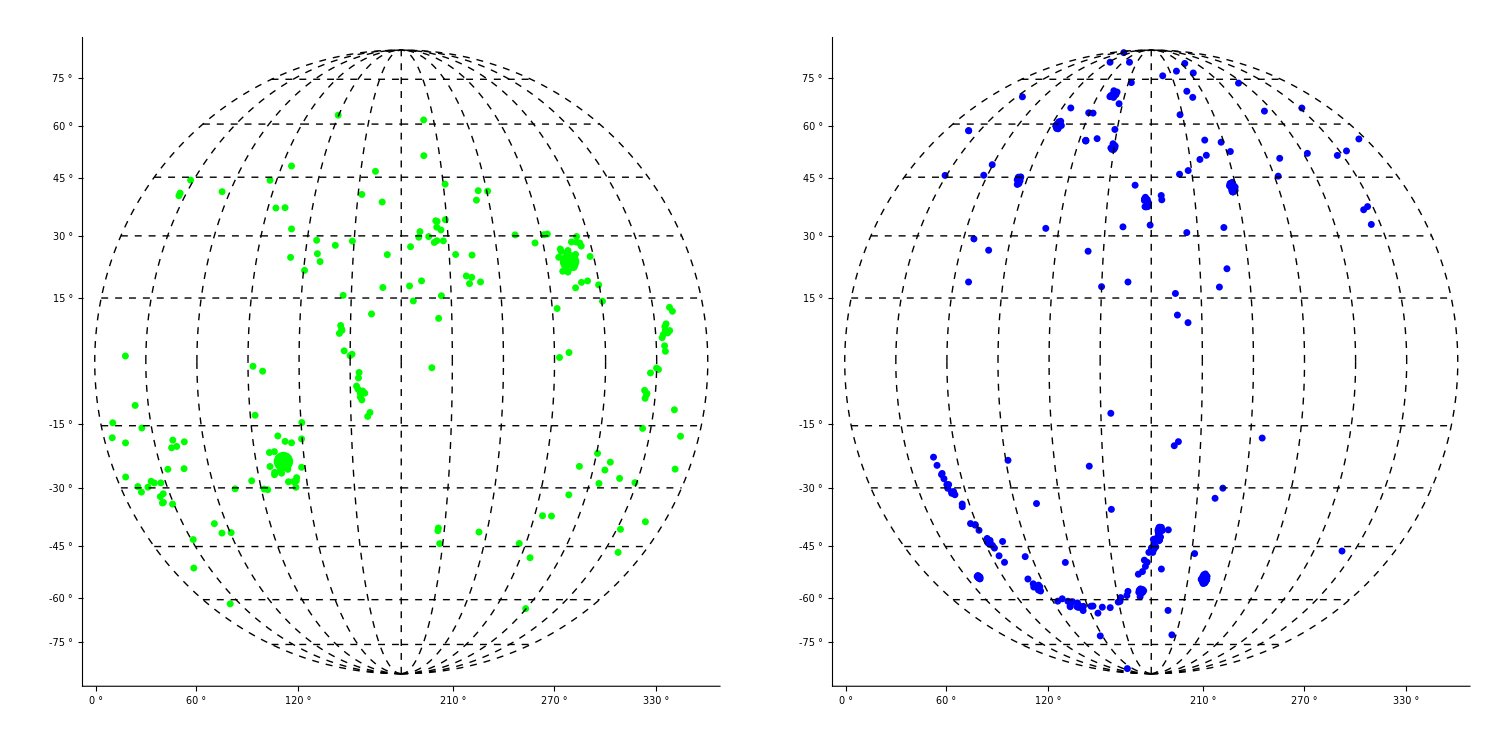

```mathematica
(* Figure 8 - Combine the two plots*)
distribfigredreal=GraphicsGrid[{{hcmethdredrandfig,distribfigred}},Spacings->0,ImageSize->1500,AspectRatio->Full]
```

```mathematica
Export[NotebookDirectory[]<>"distribfigredreal.pdf",distribfigredreal,ImageResolution->1000];
```

### Dipole Fitting Method - Figure 9

#### Real Data Analysis

##### Main Analysis

```mathematica
(* Eq. (3.7) from the paper *)
mbbf=Table[5 Log10[(1+data[[i,3]])/(1+data[[i,2]])DL[data[[i,2]],ombf2]]+Mbf2,{i,1,Length[data]}];
mbvar=Table[(mbbf[[i]]-data[[i,4]])/mbbf[[i]],{i,1,Length[data]}];
smbvar=Table[data[[i,5]]/mbbf[[i]],{i,1,Length[data]}];

(* The direction of each datapoint *)
xcart=Table[Sin[theta[[i]]] Cos[phi[[i]]],{i,1,Length[data]}];
ycart=Table[Sin[theta[[i]]] Sin[phi[[i]]],{i,1,Length[data]}];
zcart=Table[Cos[theta[[i]]],{i,1,Length[data]}];

(* χ^2 formula *)
chi2Panthstatdf[c1_?NumberQ,c2_?NumberQ,c3_?NumberQ,bb_?NumberQ]:=Module[{Δm,sdΔm},
Δm=Table[mbvar[[i]]-c1 xcart[[i]]-c2 ycart[[i]]-c3 zcart[[i]]-bb,{i,1,Length[data]}];
sdΔm=Inverse[DiagonalMatrix[smbvar[[All]]^2]];
Δm.sdΔm.Δm]
```

```mathematica
(* Minimization of χ^2 with respect to the parameters Subscript[c, 1], Subscript[c, 2],Subscript[c, 3] and B *)
minci=FindMinimum[chi2Panthstatdf[c1,c2,c3,bb],{c1,0,1},{c2,0.4,0.5},{c3,0,1},{bb,0,0.1}];
c1bf=minci[[2,1,2]];
c2bf=minci[[2,2,2]];
c3bf=minci[[2,3,2]];
bbf=minci[[2,4,2]];
(* 1σ errors for the Subscript[c, i]'s *)
chifundf=ListInterpolation[ParallelTable[chi2Panthstatdf[c1,c2,c3,bb],{c1,c1bf-0.0002,c1bf+0.0002,0.0002},{c2,c2bf-0.00002,c2bf+0.00002,0.00002},{c3,c3bf-0.0002,c3bf+0.0002,0.0002},{bb,bbf-0.00002,bbf+0.00002,0.00002},DistributedContexts->Automatic],{{c1bf-0.0002,c1bf+0.0002},{c2bf-0.00002,c2bf+0.00002},{c3bf-0.0002,c3bf+0.0002},{bbf-0.00002,bbf+0.00002}}];
(* Params that we want to calculate the errors *)
paramsdf={c1,c2,c3,bb};
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
Fijdf=1/2Table[D[chifundf[c1,c2,c3,bb],paramsdf[[p]],paramsdf[[d]]]/.minci[[2]],{p,1,Length[paramsdf]},{d,1,Length[paramsdf]}];
cijdf=Inverse[Fijdf];
errorsdf=√Diagonal[cijdf];
Print["The best fit parameters for the c_i's and B are: c_1=",ScientificForm[c1bf],"±",ScientificForm[errorsdf[[1]]],", c_2=",ScientificForm[c2bf],"±",ScientificForm[errorsdf[[2]]],", c_3=",ScientificForm[c3bf],"±",ScientificForm[errorsdf[[3]]],"and B=",ScientificForm[bbf],"±",ScientificForm[errorsdf[[4]]]," respectively"]
```

The best fit parameters for the c_i's and B are: c_1=-1.40777×10^-4±3.75512×10^-4, c_2=-8.2112×10^-5±4.54028×10^-4, c_3=5.2818×10^-4±7.14604×10^-4and B=-5.90281×10^-5±3.00698×10^-4 respectively

##### A Constant and (l,b) Coordinates Best Fit of the Real Data

```mathematica
(* Magnitude of the monopole A constant *)
abf=Sqrt[c1bf^2+c2bf^2+c3bf^2];
(* Error of the monopole A constant *)
DipMagDer={c1,c2,c3,0}/Sqrt[c1^2+c2^2+c3^2]/.{c1->c1bf,c2->c2bf,c3->c3bf};
erra=Sqrt[DipMagDer.cijdf.DipMagDer];
(* l coordinate *)
DipL=If[c2<0,2Pi-ArcCos[c1/Sqrt[c1^2+c2^2]],ArcCos[c1/Sqrt[c1^2+c2^2]]];
lcoorbf=(DipL/.{c1->c1bf,c2->c2bf,c3->c3bf})/Degree;
DipLDer={D[DipL,c1],D[DipL,c2],D[DipL,c3],0}/.{c1->c1bf,c2->c2bf,c3->c3bf};
lcoorerr=Sqrt[DipLDer.cijdf.DipLDer]/Degree;
(* b coordinate *)
DipB=ArcTan[c3/Sqrt[c1^2+c2^2]];
bcoorbf=(DipB/.{c1->c1bf,c2->c2bf,c3->c3bf})/Degree;
DipBDer={D[DipB,c1],D[DipB,c2],D[DipB,c3],0}/.{c1->c1bf,c2->c2bf,c3->c3bf};
bcoorerr=Sqrt[DipBDer.cijdf.DipBDer]/Degree;
(* Print the Best Fit Values *)
Print["The best fit for the parameter A and the galactic coordinates (l,b) of the Real Data are: A=",ScientificForm[abf],"±",ScientificForm[erra]," and (",lcoorbf,"°±",lcoorerr, "°, ",bcoorbf,"°±",bcoorerr, "°)"]
```

The best fit for the parameter A and the galactic coordinates (l,b) of the Real Data are: A=5.52752×10^-4±6.03965×10^-4 and (210.254°±136.564°, 72.852°±60.6313°)

#### Random Simulated Datasets Analysis

```mathematica
(* Implementation of the DF method using isotropic simulated Pantheon datasets *)
jmaxdf=30;lcoorlist={};lerrlist={};bcoorlist={};berrlist={};Acoorlist={};
Do[
(* Generate the isotropic simulated datasets and create an appropriate table *)
randdat[j_]:=RandomReal[NormalDistribution[5 Log10[(1+data[[j,3]])/(1+data[[j,2]])DL[data[[j,2]],ombf2]]+Mbf2,data[[j,5]]] ];
randdatab=Table[randdat[j],{j,1,Length[data]}];
(* Eq. (3.7) from the paper *)
mbbfrand=Table[5 Log10[(1+data[[i,3]])/(1+data[[i,2]])DL[data[[i,2]],ombf2]]+Mbf2,{i,1,Length[data]}];
mbvarand=Table[(mbbfrand[[i]]-randdatab[[i]])/mbbfrand[[i]],{i,1,Length[data]}];
smbvarand=Table[data[[i,5]]/mbbfrand[[i]],{i,1,Length[data]}];
(* The direction of each datapoint *)
xcartrand=Table[Sin[theta[[i]]] Cos[phi[[i]]],{i,1,Length[data]}];
ycartrand=Table[Sin[theta[[i]]] Sin[phi[[i]]],{i,1,Length[data]}];
zcartrand=Table[Cos[theta[[i]]],{i,1,Length[data]}];
(* χ^2 formula *)
chi2Panthstatdfrand[c1_?NumberQ,c2_?NumberQ,c3_?NumberQ,bb_?NumberQ]:=Module[{Δm,sdΔm},
Δm=Table[mbvarand[[i]]-c1 xcartrand[[i]]-c2 ycartrand[[i]]-c3 zcartrand[[i]]-bb,{i,1,Length[data]}];
sdΔm=Inverse[DiagonalMatrix[smbvarand[[All]]^2]];
Δm.sdΔm.Δm];
(* Minimization of χ^2 with respect to the parameters Subscript[c, 1], Subscript[c, 2],Subscript[c, 3] and B *)
mincirand=FindMinimum[chi2Panthstatdfrand[c1,c2,c3,bb],{c1,0,1},{c2,0.4,0.5},{c3,0,1},{bb,0,0.1}];
(* 1σ errors for the Subscript[c, i]'s *)
c1bfrand=mincirand[[2,1,2]];
c2bfrand=mincirand[[2,2,2]];
c3bfrand=mincirand[[2,3,2]];
bbfrand=mincirand[[2,4,2]];
chifundfrand=ListInterpolation[ParallelTable[chi2Panthstatdfrand[c1,c2,c3,bb],{c1,c1bfrand-0.00002,c1bfrand+0.00002,0.00002},{c2,c2bfrand-0.00002,c2bfrand+0.00002,0.00002},{c3,c3bfrand-0.0002,c3bfrand+0.0002,0.0002},{bb,bbfrand-0.0002,bbfrand+0.0002,0.0002},DistributedContexts->Automatic],{{c1bfrand-0.00002,c1bfrand+0.00002},{c2bfrand-0.00002,c2bfrand+0.00002},{c3bfrand-0.0002,c3bfrand+0.0002},{bbfrand-0.0002,bbfrand+0.0002}}];
(* Params that we want to calculate the errors *)
paramsdfrand={c1,c2,c3,bb};
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
Fijdfrand=1/2Table[D[chifundfrand[c1,c2,c3,bb],paramsdfrand[[p]],paramsdfrand[[d]]]/.mincirand[[2]],{p,1,Length[paramsdfrand]},{d,1,Length[paramsdfrand]}];
cijdfrand=Inverse[Fijdfrand];
(* Magnitude of the monopole A constant *)
abfrand=Sqrt[c1bfrand^2+c2bfrand^2+c3bfrand^2];
(* Error of the monopole A constant *)
DipMagDerand={c1,c2,c3,0}/Sqrt[c1^2+c2^2+c3^2]/.{c1->c1bfrand,c2->c2bfrand,c3->c3bfrand};
errarand=Sqrt[DipMagDerand.cijdfrand.DipMagDerand];
(* l coordinate *)
DipLrand=If[c2<0,2Pi-ArcCos[c1/Sqrt[c1^2+c2^2]],ArcCos[c1/Sqrt[c1^2+c2^2]]];
lcoorbfrand=(DipLrand/.{c1->c1bfrand,c2->c2bfrand,c3->c3bfrand})/Degree;
DipLDerand={D[DipLrand,c1],D[DipLrand,c2],D[DipLrand,c3],0}/.{c1->c1bfrand,c2->c2bfrand,c3->c3bfrand};
lcoorerrand=Sqrt[DipLDerand.cijdfrand.DipLDerand]/Degree;
(* b coordinate *)
DipBrand=ArcTan[c3/Sqrt[c1^2+c2^2]];
bcoorbfrand=(DipBrand/.{c1->c1bfrand,c2->c2bfrand,c3->c3bfrand})/Degree;
DipBDerand={D[DipBrand,c1],D[DipBrand,c2],D[DipBrand,c3],0}/.{c1->c1bfrand,c2->c2bfrand,c3->c3bfrand};
bcoorerrand=Sqrt[DipBDerand.cijdfrand.DipBDerand]/Degree;
(* Append the data in lists *)
AppendTo[Acoorlist,abfrand];
AppendTo[lcoorlist,lcoorbfrand];
AppendTo[lerrlist,lcoorerrand];
AppendTo[bcoorlist,bcoorbfrand];
AppendTo[berrlist,bcoorerrand];
(* Print the results as the calculation continues *)
If[Mod[j,5]==0,Print["Finished step ",j," of ",jmaxdf," // l=",lcoorbfrand,"°±",lcoorerrand,"° and b=",bcoorbfrand,"°±",bcoorerrand]],{j,1,jmaxdf}]
```

Finished step 5 of 30 // l=334.331°±63.9703° and b=42.6811°±46.1566

Finished step 10 of 30 // l=184.658°±36.5509° and b=-43.0028°±23.7564

Finished step 15 of 30 // l=91.3354°±55.3137° and b=-7.5679°±105.909

Finished step 20 of 30 // l=187.646°±59.9758° and b=47.1985°±66.1255

Finished step 25 of 30 // l=226.576°±46.0832° and b=-49.1693°±31.7991

Finished step 30 of 30 // l=49.5111°±23.5305° and b=21.6677°±35.7618

```mathematica
(* Select the simulated datasets that have larger/lower magnitudes of AL than the corresponding magnitude of the real Pantheon data *)
amaxdf=Select[Table[{Acoorlist[[i]],bcoorlist[[i]],lcoorlist[[i]]},{i,1,jmaxdf}],Abs[#1[[1]]]>Abs[abf]&];
amindf=Select[Table[{Acoorlist[[i]],bcoorlist[[i]],lcoorlist[[i]]},{i,1,jmaxdf}],Abs[#1[[1]]]<Abs[abf]&];
```

```mathematica
(* Select the (b,l) coordinates of the simulated datasets that have larger/lower magnitudes of AL than the corresponding magnitude of the real Pantheon data *)
datagalrand1=Table[{amaxdf[[i,2]],amaxdf[[i,3]]},{i,1,Length[amaxdf]}];
datagalrand2=Table[{amindf[[i,2]],amindf[[i,3]]},{i,1,Length[amindf]}];
datagalrand=Join[datagalrand1,datagalrand2];
```

```mathematica
(* Red/Blue is the color selected for the simulated datasets that have larger/lower magnitudes of AL than the corresponding magnitude of the real Pantheon data *)
col1df=Table[Red,{i,1,Length[amaxdf]}];
col2df=Table[Blue,{i,1,Length[amindf]}];
coldf=Join[col1df,col2df];
```

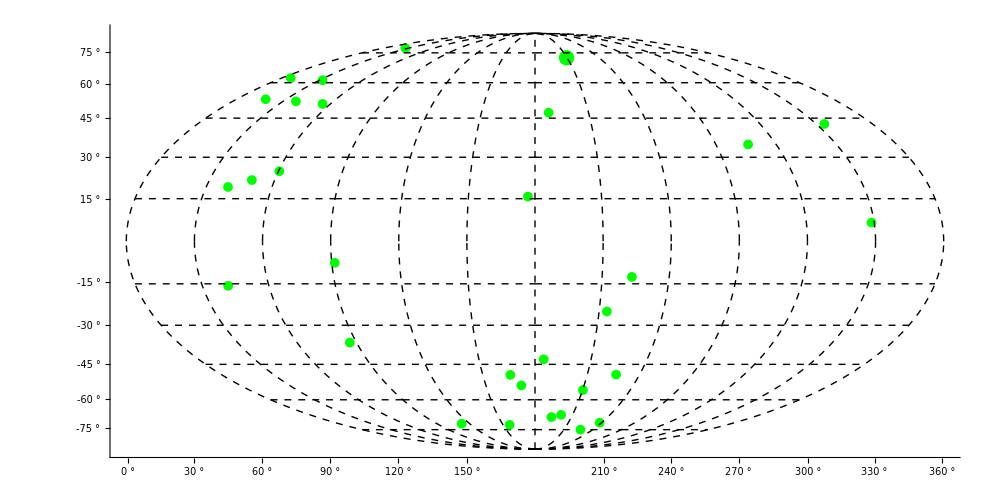

```mathematica
(* Fig. 9 - The different directions of the 30 random
simulated datasets using the DF method *)
dfrandomfig=GeoGraphics[{Green,AbsolutePointSize@11,Point[{12.5 Degree,71.5 Degree}],AbsolutePointSize@7,Point[GeoPosition@datagalrand,VertexColors->(coldf)]},GeoRange->{{-90,90},{0,360}},GeoGridLinesStyle->Directive[Black,Dashed],GeoProjection->"Mollweide",GeoGridLines->{{-90,90,-75,75,-60,60,-45,45,-30,30,-15,15},{0,30,60,90,120,150,180,210,240,270,300,330,360}},ImageSize->1000,GeoBackground->White,Axes->True,ImagePadding->25,Ticks->{tickslgal,ticksbdeg},Background->White,AxesStyle->Black,TicksStyle->Directive[Black,FontSize->19]]
```

```mathematica
Export[NotebookDirectory[]<>"dfrandomfig.pdf",dfrandomfig,ImageResolution->1000];
```

```mathematica
(* Find the number of simulated datasets that have larger/lower magnitudes of AL than the corresponding magnitude of the real Pantheon data *)
Length[amaxdf]
Length[amindf]
```

19

11

## Section IV - Modified Theory of Gravity Scenario

### μ Plot for 100pts Subsample - Figure 10

```mathematica
(* 1σ error calculations for μ *)
G=10^((4/15)(M-M0));
D[G,M]
D[G,M0]
```

1/3 2^(2+(4 (M-M0))/15) 5^(-1+(4 (M-M0))/15) Log[10]

-1/3 2^(2+(4 (M-M0))/15) 5^(-1+(4 (M-M0))/15) Log[10]

```mathematica
(* Partial derivative of μ with respect M *)
dgm=Table[1/3 2^(2+(4 (tabsubsamp[[i,6]]-Mbf))/15) 5^(-1+(4 (tabsubsamp[[i,6]]-Mbf))/15) Log[10],{i,1,Length[tabsubsamp]}];
(* 1σ error of the first derivative of μ with respect M *)
sdgm=Table[tabsubsamp[[i,7]],{i,1,Length[tabsubsamp]}];
(* Partial derivative of μ with respect Subscript[M, 0] *)
dgm0=Table[-1/3 2^(2+(4 (tabsubsamp[[i,6]]-Mbf))/15) 5^(-1+(4 (tabsubsamp[[i,6]]-Mbf))/15) Log[10],{i,1,Length[tabsubsamp]}];
(* 1σ error of the first derivative of μ with respect Subscript[M, 0] *)
sdgm0=Table[errors[[1]],{i,1,Length[tabsubsamp]}];
```

```mathematica
(* 1σ Error of μ *)
sG=Table[√((dgm[[i]]*sdgm[[i]])^2+(dgm0[[i]]*sdgm0[[i]])^2),{i,1,Length[tabsubsamp]}];
(* Eq. (4.1) setting b=-3/2 *)
gvalsubsamp=Table[10^((4/15)(tabsubsamp[[i,6]]-Mbf)),{i,1,Length[tabsubsamp]}];
gaa=Table[{{tabsubsamp[[i,5]],gvalsubsamp[[i]]},ErrorBar[{-sG[[i]],sG[[i]]}]},{i,1,Length[tabsubsamp]}];
```

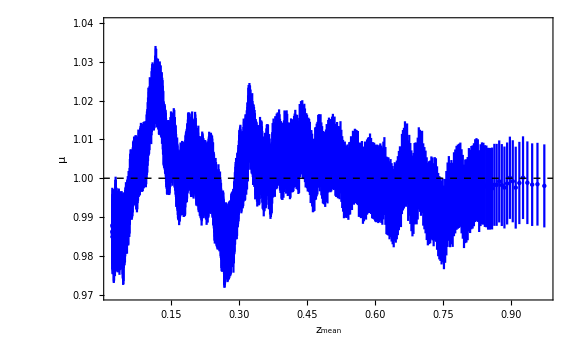

```mathematica
(* μ Plot for 100pts subsample *)
geffplot=ErrorListPlot[gaa,PlotRange->{All,{0.97,1.04}},Frame->True,PlotStyle->Blue,FrameLabel->{"z_mean","μ"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImageSize->Large,Axes->None];
gefffig=Show[{geffplot,Graphics[{{Directive[Black,Dashed],Line[{{0,1},{1,1}}]}}]}]
```

```mathematica
Export[NotebookDirectory[]<>"gefffig.pdf",gefffig,ImageResolution->1000];
```

### μ Analysis - Figures 11 & 12

#### χ^2 Formula

```mathematica
(* μ Parametrization (4.2) *)
Geffz[z_,ga_,n_]:=1+ga(z/(1+z))^n-ga(z/(1+z))^(2n)
(* χ^2 formula Including μ *)
chi2Panthstatgeff[data_,Mcal_?NumberQ,om_?NumberQ,ga_?NumberQ,b_]:=Module[{Δm,InvCovTotal},
Δm=Table[data[[i,4]]-(5 Log10[(1+data[[i,3]])/(1+data[[i,2]])DL[data[[i,2]],om]]+Mcal-(5 b)/2  Log10[Geffz[data[[i,2]],ga,2]]),{i,1,Length[data]}];
InvCovTotal=Inverse[DiagonalMatrix[data[[All,5]]^2]];
Δm.InvCovTotal.Δm]
```

#### Interpolation of the Best Fits of the Extra Parameter g_α - Figure 11

```mathematica
(* This cell calculates the best fit values of Subscript[g, α] for b<0 *)
mingeff1={};
For[b=-2,b≤-0.2,b+=0.2,minlist1=FindMinimum[chi2Panthstatgeff[data,Mcal,om,ga,b],{Mcal,23.,23.1},{om,0.18,0.19},{ga,-0.1,-0.2}];
AppendTo[mingeff1,{b,minlist1[[2,2,2]],minlist1[[2,3,2]]}]];
```

```mathematica
(* This cell calculates the best fit values of Subscript[g, α] for b>0 *)
mingeff2={};
For[b=0.2,b≤2,b+=0.2,minlist2=FindMinimum[chi2Panthstatgeff[data,Mcal,om,ga,b],{Mcal,23.,23.1},{om,0.18,0.19},{ga,-0.1,-0.2}];AppendTo[mingeff2,{b,minlist2[[2,2,2]],minlist2[[2,3,2]]}]]
```

```mathematica
(* This cell calculates the best fit values of Subscript[g, α] for b≈0 *)
mingeff0=FindMinimum[chi2Panthstatgeff[data,Mcal,om,ga,10^(-7)],{Mcal,23.7,23.8},{om,0.18,0.19},{ga,-0.1,-0.2}];
mingeff3={{0,mingeff0[[2,2,2]],mingeff0[[2,3,2]]}};
```

```mathematica
(* Join the three lists and create appropriate tables *)
mingeff=Join[mingeff1,mingeff2,mingeff3]//Sort
gatab=Table[{mingeff[[i,1]],mingeff[[i,3]]},{i,1,Length[mingeff]}];
gafunc=Interpolation[gatab];
```

{{-2,0.183113,-0.341594},{-1.8,0.181855,-0.383344},{-1.6,0.180252,-0.436646},{-1.4,0.178148,-0.507},{-1.2,0.17527,-0.603977},{-1.,0.250655,-0.221685},{-0.8,0.252195,-0.254907},{-0.6,0.15496,-1.35961},{-0.4,0.145403,-2.04788},{-0.2,0.167959,-2.95994},{0,0.285,2.73714},{0.2,0.242226,1.56456},{0.4,0.226497,1.04774},{0.6,0.218389,0.786431},{0.8,0.21341,0.629551},{1.,0.210127,0.524228},{1.2,0.207805,0.448832},{1.4,0.206053,0.39241},{1.6,0.282564,0.00926076},{1.8,0.203624,0.313413},{2.,0.202744,0.284729}}

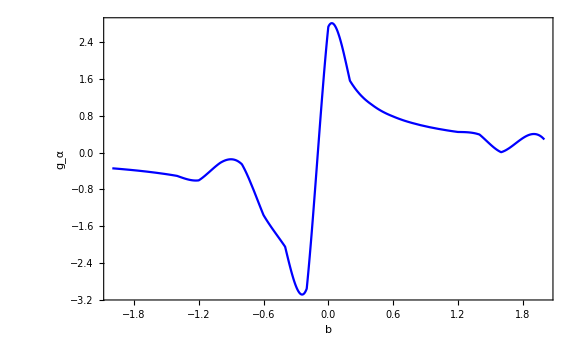

```mathematica
(* Figure 11 - Interpolation of the best fits of the extra parameter Subscript[g, α] as a function of b *)
gabfig=Plot[gafunc[x],{x,-2,2},Frame->True,PlotStyle->Blue,FrameLabel->{"b","g_α"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImageSize->Large,Axes->None]
```

```mathematica
Export[NotebookDirectory[]<>"gabfig.pdf",gabfig,ImageResolution->1000];
```

#### Minimization of χ^2 Setting b=-3/2

```mathematica
(* Minimization of χ^2 with respect to ℳ and Subscript[Ω, 0m] and Subscript[g, α] *)
mingeffbconst=FindMinimum[chi2Panthstatgeff[data,Mcal,om,ga,-3/2],{Mcal,23.,23.1},{om,0.17,0.18},{ga,0,-0.1}];
Mcalbfgeff=mingeffbconst[[2,1,2]];
ombfgeff=mingeffbconst[[2,2,2]];
gabfgeff=mingeffbconst[[2,3,2]];
chifungeff=ListInterpolation[ParallelTable[chi2Panthstatgeff[data,Mcal,om,ga,-3/2],{Mcal,Mcalbfgeff-0.02,Mcalbfgeff+0.02,0.02},{om,ombfgeff-0.02,ombfgeff+0.02,0.02},{ga,gabfgeff-0.02,gabfgeff+0.02,0.02},DistributedContexts->Automatic],{{Mcalbfgeff-0.02,Mcalbfgeff+0.02},{ombfgeff-0.02,ombfgeff+0.02},{gabfgeff-0.02,gabfgeff+0.02}}];
(* Params that we want to calculate the errors *)
paramsgeff={Mcal,om,ga};
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
Fijgeff=1/2Table[D[chifungeff[Mcal,om,ga],paramsgeff[[p]],paramsgeff[[d]]]/.mingeffbconst[[2]],{p,1,Length[paramsgeff]},{d,1,Length[paramsgeff]}];  
cijgeff=Inverse[Fijgeff] ;  
errorsgeff=√Diagonal[cijgeff];
Print["The best fit parameters for ℳ, Ω_(0  m) and g_α are: ℳ=",Mcalbfgeff,"±",errorsgeff[[1]],", Ω_(0  m)=",ombfgeff,"±",errorsgeff[[2]]," and g_α=",gabfgeff,"±",errorsgeff[[3]]," respectively"]
```

The best fit parameters for ℳ, Ω_(0  m) and g_α are: ℳ=23.7925±0.00959951, Ω_(0  m)=0.179277±0.0777579 and g_α=-0.46922±0.365015 respectively

#### Contour Plots Setting b=-3/2 - Figure 12

```mathematica
(* Corresponding Contour Plots for the 3 parameters *)
contourMomgeff=ContourPlot[chi2Panthstatgeff[data,Mcal,om,gabfgeff,-3/2],{om,0.13,0.24},{Mcal,23.75,23.83},Contours->{mingeffbconst[[1]]+dchi[1,3],mingeffbconst[[1]]+dchi[2,3],mingeffbconst[[1]]+dchi[3,3],mingeffbconst[[1]]+dchi[4,3]},ContourShading->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.55,.9],Hue[0.6,.1,.9],White},ContourStyle->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.55,.9],Hue[0.6,.1,.9],White},FrameLabel->{"Ω_(0  m)","ℳ"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Green,Point[{ombfgeff,Mcalbfgeff}]}}];
contourMgageff=ContourPlot[chi2Panthstatgeff[data,Mcal,ombfgeff,ga,-3/2],{ga,-0.72,-0.22},{Mcal,23.75,23.83},Contours->{mingeffbconst[[1]]+dchi[1,3],mingeffbconst[[1]]+dchi[2,3],mingeffbconst[[1]]+dchi[3,3],mingeffbconst[[1]]+dchi[4,3]},ContourShading->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.55,.9],Hue[0.6,.1,.9],White},ContourStyle->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.55,.9],Hue[0.6,.1,.9],White},FrameLabel->{"g_α","ℳ"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Green,Point[{gabfgeff,Mcalbfgeff}]}}];
contourgaomgeff=ContourPlot[chi2Panthstatgeff[data,Mcalbfgeff,om,ga,-3/2],{om,0,0.4},{ga,-1.8,0.9},Contours->{mingeffbconst[[1]]+dchi[1,3],mingeffbconst[[1]]+dchi[2,3],mingeffbconst[[1]]+dchi[3,3],mingeffbconst[[1]]+dchi[4,3]},ContourShading->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.55,.9],Hue[0.6,.1,.9],White},ContourStyle->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.55,.9],Hue[0.6,.1,.9],White},FrameLabel->{"Ω_(0  m)","g_α"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Green,Point[{ombfgeff,gabfgeff}]}}];
```

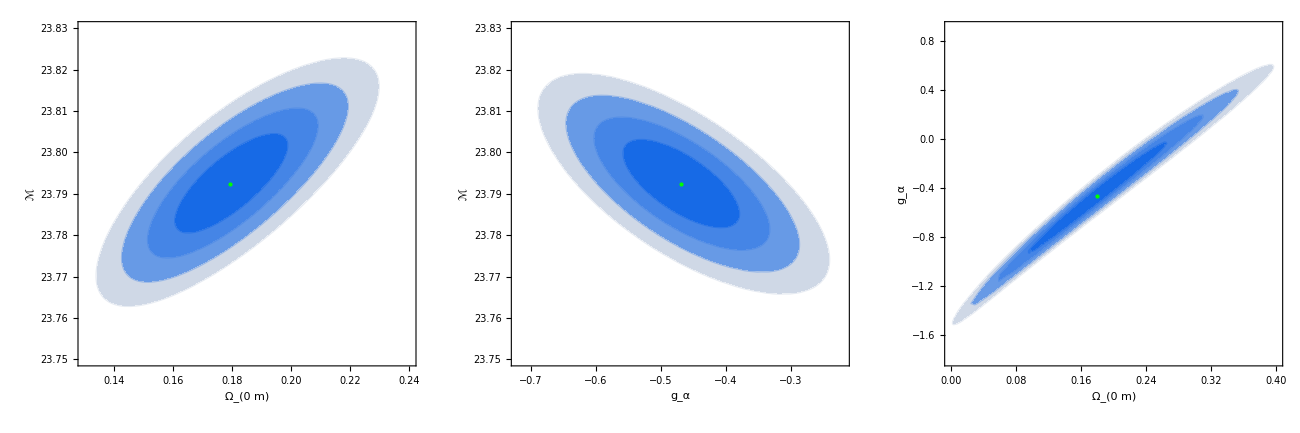

```mathematica
(* Figure 12 - Combine the Contour Plots *)
contourgeffig=GraphicsGrid[{{contourMomgeff,contourMgageff,contourgaomgeff}},ImageSize->1300,Spacings->0]
```

```mathematica
Export[NotebookDirectory[]<>"contourgeffig.pdf",contourgeffig,ImageResolution->1000];
```